# GH, SHEL and OIF Shifts: Double Interface M. T. Lusk December 18, 2016

-Graphics-

## Plotting Tools

```mathematica
Clear[font,coloredfont];
font[name_,size_]:=Style[name,FontFamily->"Tahoma",FontSize->size,Bold]

coloredfont[name_,size_,color_]:=Style[name,FontFamily->"Tahoma",FontSize->size,Bold, color]
```

## Theory

### Basic Theory of Modal Representation of the E-Field

References:

[1] An angular spectrum representation approach to the Goos-Hanchen shift, M. McGuirk and C. K. Carniglia, J.Opt. Soc. Am. Vol 67(1) p 103 1977 [Spectral_Decomposition_McGuirk_JOSA_1977.pdf]

[2] Optical Coherence and Quantum Optics, Mandel and Wolf [Quantum_Optics_Mandel_Wolf.pdf]

McGuirk gives the key result and some hints about the proof, while Mandel gives a step-by-step detailed proof. See Mandel p111 Eq 3.2-12. This is the derivation repeated below.

Consider a beam characterized by

E⃗[r⃗,t]=E[r⃗] f ⅇ^(ⅈ(k_0·r- ω t))

Here f is the fixed polarization of the beam. This is a monchromatic beam since there is only 1 temporal frequency, ω. Since k_0=k_0 κ_0, we immediately have that k_0=ω/c. The beam can be decomposed into plane waves via a Fourier transform, but the magnitude of each wave vector must be k_0 because both the speed and temporal frequency are fixed. Thus, the E-field can be described in terms of a spectrum of mono-length wave vectors:

k=k_0 κ.

Suppose our incident beam, traveling with central wave vector, k_0, makes an angle of θ with a planar interface with unit normal, n̂.

It will be convenient to define the beam frame, which is fixed once θ is prescribed. Let u_3 be the unit vector along the beam axis. Then

u_2= n×u_3

u_1= u_2×u_3

Note that (û)_2 is normal to the plane of incidence (which is the plane containing (û)_3 and n̂), so E-fields in this direction are TE (s-polarized). Therefore E-fields in the (û)_1 direction are TM (p-polarized). The polarization of the beam is then

f= f_1 u_1+f_2 u_2.

Coordinates along each beam axis will be referred to as x, y, and z respectively.

Suppose that |k|=k_0. This implies that

k= k_0(κ_x u_1 +κ_y u_2  + √(1-κ_x^2-κ_y^2)u_3).

Consider the z = z_0 plane, where z_0 is completely arbitrary, and define the angular spectrum, Ẽ[κ_x,κ_y;z_0], as:

Ẽ[κ_x,κ_y;z_0]=∫∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(-ⅈ κ_x x')ⅇ^(-ⅈ κ_y y').

Then, as shown below,

E[x,y,z]=(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yẼ[κ_x,κ_y;z]ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y)

Note that we can and have dropped the subscript on z.

Proof:

E[x,y,z_0]= (1/(2π))^2∫∫ⅆ k_xⅆ k_y∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(-ⅈ κ_x x')ⅇ^(ⅈ κ_x x)ⅇ^(-ⅈ κ_y y')ⅇ^(ⅈ κ_y y)

E[x,y,z_0]= (1/(2π))^2∫∫ⅆ κ_xⅆ κ_y∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(ⅈ κ_x(x-x'))ⅇ^(ⅈ κ_y(y-y'))

E[x,y,z_0]= ∫ⅆx'ⅆy' E[x',y',z_0]δ[x-x']δ[y-y']

E[x,y,z_0]= E[x,y,z_0]

This result can be used to construct a general spectral representation of the E-field. First note that

(∇^2 +κ^2)E[r]=0

Substitute our Fourier expression into this Helmholtz equation and reverse the order of integration and differentiation:

(1/(2π))^2∫∫ⅆ κ_xⅆ κ_y(∇^2 +κ^2)(Ẽ[κ_x,κ_y;z]ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y))=0

(1/(2π))^2∫∫ⅆ κ_xⅆ κ_y((-κ_x^2-κ_y^2+1+∂_zz)Ẽ[κ_x,κ_y;z])ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y))=0

Since this holds for all values of x and y, the integrand must be zero implying that

(∂_zz + κ_z^2)Ẽ[κ_x,κ_y;z]=0

The general solution to this equation is

Ẽ[κ_x,κ_y;z]= A[κ_x,κ_y]ⅇ^(ⅈ κ_z z)+B[κ_x,κ_y]ⅇ^(-ⅈ κ_z z)

Substitution of this result into the expression for E gives

E[x,y,z]=(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yA[κ_x,κ_y]ⅇ^(ⅈ (κ_x x+κ_y y +κ_z z))+(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yB[κ_x,κ_y]ⅇ^(ⅈ (κ_x x+κ_y y-κ_z z))

This is not a Fourier decomposition of the beam. Rather, it is a modal representation of the beam that only superficially resembles a Fourier transform.

The final expression is

E(r)≡E(r)f= (∑_(λ=1,2) u_λ f_λ)∫∫∫ⅆ k_xⅆ k_yⅆ k_z Ẽ(k)ⅇ^(ⅈ(k·r))

### Derivation of Reflected E-field

The unit normal of the plane is

n= -Sin[θ]u_1+Cos[θ]u_3

κ ... the normalized wave vector for each plane wave element of the incident beam. The coordinate basis chosen {u_1, u_2, u_3}, is that of the beam with the plane of incidence that which contains interface normal, n, and u_3.

u_(1') ... TM/1/p polarization of an individual plane wave element
u_(2') ... TE/2/s polarization of an individual plane wave element
u_(3') ... direction of propagation of an individual plane wave element

Construct a set of linearized relations in which the primed basis vectors are expressed in terms of the beam basis vectors. (Eq 19 of Bliokh PRE 2007).

```mathematica
Clear[κvec,κx,κy,κz,e1,e2];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

nvec = {-Sin[θ],0,Cos[θ]};

u2prime= Cross[nvec,κvec]/(√(Cross[nvec,κvec].Cross[nvec,κvec]));

u1prime  =Simplify[ Cross[u2prime,κvec]/(√(Cross[u2prime,κvec].Cross[u2prime,κvec]))];

u1prime=FullSimplify[Expand[Normal[Series[u1prime,{κx,0,1},{κy,0,1}]]]/. {κx^2->0,κy^2->0,κx κy->0},{θ>0,θ<π/2}]

u2prime=FullSimplify[Expand[Normal[Series[u2prime,{κx,0,1},{κy,0,1}]]]/. {κx^2->0,κy^2->0,κx κy->0},{θ>0,θ<π/2}]

u3prime= Cross[u1prime,u2prime]/.{κx^2->0,κy^2->0,κx κy->0}
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

{κx,κy,1}

The physical polarization of each plane wave element is taken to be the same as that of the beam, so the polarization does not change from plane wave to plane wave. Instead, the electric field of each plane wave is expressed in terms of the Fourier transform of the scalar E-field of the beam. Call this Ẽ so that

E=E e

Ẽ=ℱ[E]

Ẽ=Ẽ e = Ẽ (f_1 u_1+f_2 u_2)

where f is the polarization vector of the beam.

But we can also write

Ẽ=(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2')

Since

u_(1')=u_1+κ_y Cot[θ]u_2-κ_x u_3

u_(2')=-κ_y Cot[θ]u_1+u_2-κ_y u_3

u_(3')=κ_x u_1+κ_y u_2+u_3

Now invert these equations to obtain the unprimed basis vectors in terms of their primed counterparts.

```mathematica
sol=Simplify[Solve[{
u1p == {u1,u2,u3}.u1prime ,
u2p =={u1,u2,u3}.u2prime,
u3p =={u1,u2,u3}.u3prime
},{u1,u2,u3}]];

Expand[sol] /. {κx^2->0,κy^2->0,κx κy->0}
```

{{u1→u1p+u3p κx-u2p κy Cot[θ],u2→u2p+u3p κy+u1p κy Cot[θ],u3→u3p-u1p κx-u2p κy}}

We have two ways of writing the E-field:

Ẽ= Ẽ (f_1 u_1+f_2 u_2)=(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2')

Using the relations derived above, equate the components.

(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') =Ẽ (f_1(u_(1')-κ_y Cot[θ]u_(2')+κ_x u_(3'))+ f_2(κ_y Cot[θ]u_(1')+u_(2')+κ_y u_(3')))

(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') =Ẽ (f_1+f_2 κ_y Cot[θ])u_(1')+Ẽ (f_2-f_1 κ_y Cot[θ])u_(2') + Ẽ (f_1 κ_x+f_2 κ_y)u_(3'))

This implies that

(Ẽ)_x' =Ẽ (f_1+f_2 κ_y Cot[θ])

(Ẽ)_y' =Ẽ (f_2-f_1 κ_y Cot[θ])

It also leaves a u_(3') component that sums to zero when all plane waves are taken into account.

Not surprisingly, we can recover our original formulation of the incident field:

```mathematica
Etilde = Etildemag Expand[( f1 + κy Cot[θ] f2) u1prime+(f2 - κy Cot[θ]f1) u2prime] /. {κy^2->0,κx κy ->0}
```

{Etildemag f1,Etildemag f2,Etildemag (-f1 κx-f2 κy)}

That is not the point though. We did this in order to be able to apply polarization-dependent reflection coefficients to each plane-wave vector.

The (Ẽ)_x' is multiplied by R_1, while the (Ẽ)_y' component is multiplied by R_2. We also need to constructed the primed unit vectors, here expressed in terms of the original incident angle although we could have put in θR directly. Later we will re-write the final result in terms of θR.

```mathematica
u1prime$R = u1prime/. {θ->π-θ}
u2prime$R = u2prime/. {θ->π-θ}
```

{1,-κy Cot[θ],-κx}

{κy Cot[θ],1,-κy}

```mathematica
Clear[R1,R2];

Etilde$R = Simplify[Etildemag Expand[( f1 + κy Cot[θ] f2) u1prime$R R1+(f2 - κy Cot[θ]f1) u2prime$R R2] /. {κy^2->0,κx κy ->0, θ->-θR}]
```

{Etildemag (f1 R1-f2 (R1+R2) κy Cot[θR]),Etildemag (f2 R2+f1 (R1+R2) κy Cot[θR]),-Etildemag (f1 R1 κx+f2 R2 κy)}

The final expression is therefore:

(Ẽ)_R= Ẽ((f_1 R_1-f_2 κ_y Cot[θ_R](R_1+R_2))u_1+(f_2 R_2 + f_1 κ_y Cot[θ_R](R_1+R_2 ))u_2-(f_1 R_1 κ_x + f_2 R_2  κ_y)u_3

Since the basis vectors are constant for a given beam, the reflected beam is easily recovered by just taking the inverse Fourier transform of each of its components above.

### Aside: Reflected Polarization Vector

As an aside, we also recover Bliokh’s polarization vector for plane wave elements of the reflected beam.

```mathematica
etildeR = Simplify[Expand[1/Etildemag Etilde$R ]/. {κy^2->0,κx κy ->0}]
```

{f1 R1-f2 (R1+R2) κy Cot[θR],f2 R2+f1 (R1+R2) κy Cot[θR],-f1 R1 κx-f2 R2 κy}

Replace f1 with 1, f2 with mc, and remember that Bliokh’s (m̃)^R ≡ m_c ρR. Then it clear that the line above is the same as Bliokh’s Eq 40 (below) once it is normalized.

-Graphics-

### Aside: Construction of Formulae for the Goos-Hanchen Shifts

The work below does not derive Artmann’s formula for the GH shift. Rather, Artmann’s formula is used to get an explicit expression for the GH shift. However, in the application section in which a Gaussian beam is considered analytically, I derive Artmann’s formula explicitly by analytically calculating the centroid of the reflected beam. (That was fun and cool to do!)

Start by defining the two reflection coefficients. These will be complex valued for angles of incidence greater than the critical angle. The existence of a critical angle implies that n_2 < n_1--i.e. that the wave impinges on a material with a lower dielectric constant.

```mathematica
Clear[R1,R2,β,n];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(-n^2 Cos[β]+√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)
```

The GH shift can be estimated from the phase of these reflection coefficients. These phases, in turn, can be obtained in an analytically simple form or just by brute force. The approaches are shown to be equivalent below.

The brute force approach is:

```mathematica
Clear[Φ1,Φ2];

Φ1[β_,n_]=FullSimplify[ArcTan[Re[R1 /. {κx->0,κy->0}],Im[R1 /. {κx->0,κy->0}]]];

Φ2[β_,n_]=FullSimplify[ArcTan[Re[R2 /. {κx->0,κy->0}],Im[R2 /. {κx->0,κy->0}]]];
```

The derivative of these expressions with respect to β gives the GH shift:

GH_λ := (∂_β Φ_λ)/k_0

This is written in the coordinate system of the reflected beam, and the shift will come out to be negative. This is still “up and to the right” in our fixed frame though. If we use the expressions for Φ directly, the resulting formulae are ugly and do not offer any insights. We can analytically derive equivalent phase representations, with only a little effort, that work much better. First separate the reflection coefficients into real and imaginary parts.

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2)))((n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2)))
```

(-n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2))/(n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2))

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2))(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))
```

((n^2 Cos[β]-ⅈ √(-n^2+Sin[β]^2)) (-n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2)))/(-n^2+n^4 Cos[θ]^2+Sin[θ]^2)

```mathematica
R1$analytic=(-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2)+ⅈ 2 n^2 Cos[β] √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2);
```

```mathematica
R2$analytic=((Cos[θ])^2-2ⅈ Cos[θ] √(1-n^2-Cos[θ]^2)-(1-n^2-Cos[θ]^2))/((Cos[θ])^2+1-n^2-Cos[θ]^2);
```

Then the phases are

```mathematica
Clear[Φ1$analytic];
Φ1$analytic[θ_,n_]=FullSimplify[ArcTan[-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2),2 n^2 Cos[θ] √(Sin[θ]^2-n^2)] ,{θ>0,n>0,(Sin[θ]^2-n^2)>0}]
```

ArcTan[-n^2-n^4 Cos[θ]^2+Sin[θ]^2,2 n^2 Cos[θ] √(-n^2+Sin[θ]^2)]

```mathematica
Clear[Φ2$analytic];
Φ2$analytic[θ_,n_]=FullSimplify[ArcTan[(Cos[θ])^2-(1-n^2-Cos[θ]^2),-2Cos[θ] √(1-n^2-Cos[θ]^2)] ,{θ>0,n>0,1-n^2-Cos[θ]^2>0}]
```

ArcTan[n^2+Cos[2 θ],-2 Cos[θ] √(1-n^2-Cos[θ]^2)]

Below is a comparison of the two expressions for Φ_1. They are clearly equivalent.

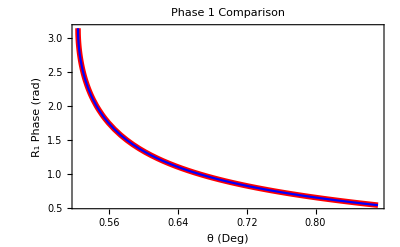

```mathematica
Plot[{Φ1[θ,1/2],Φ1$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_1 Phase (rad)",10]},PlotLabel->font["Phase 1 Comparison",14]]
```

Below is a comparison of the two expressions for Φ_2. They are clearly equivalent.

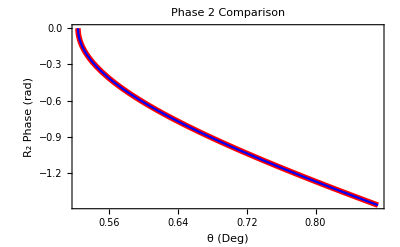

```mathematica
Plot[{Φ2[θ,1/2],Φ2$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_2 Phase (rad)",10]},PlotLabel->font["Phase 2 Comparison",14]]
```

These formula can be used to calculate the GH shifts for each polarization using Artmann’s formulae:

```mathematica
Clear[GHshift$1,GHshift$2];
GHshift$1[θ_,n_]=1/k0 FullSimplify[D[Φ1$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]

GHshift$2[θ_,n_]=1/k0 FullSimplify[D[Φ2$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]
```

(4 n^2 Sin[θ])/(k0 (-1+n^2+(1+n^2) Cos[2 θ]) √(-n^2+Sin[θ]^2))

-(2 √2 Sin[θ])/(k0 √(1-2 n^2-Cos[2 θ]))

These are very small shifts in general. For instance, for 600 nm light and n = 0.5, the critical angle is 30°. At 35°, the GH shift for polarization 1 is only 600 nm. This is shown below.

```mathematica
Print["GH_1 for 600 nm light: ",GHshift$1[35. Degree,1/2]/. k0->2π/(600.0*10^-9)," meters"]
```

GH_1 for 600 nm light: -6.0434×10^-7 meters

Here is a plot of the GH shifts for both polarizations.

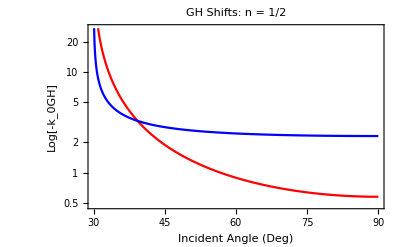

```mathematica
LogPlot[{-k0 GHshift$1[θ Degree,1/2],-k0 GHshift$2[θ Degree,1/2]},{θ,30 , 90 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-k_0GH]",12]},GridLines->Automatic]
```

Here is the same plot but now in units for 600 nm incident light.

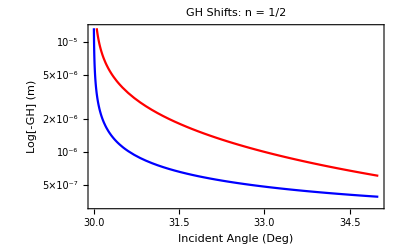

```mathematica
k0set = 2π/(600.*10^-9);

LogPlot[{-GHshift$1[θ Degree,1/2]/. k0->k0set,-GHshift$2[θ Degree,1/2]/. k0->k0set},{θ,30 , 35 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-GH] (m)",12]},GridLines->Automatic]
```

## Application

### Construction of E-field in Paraxial Approximation: Must Run for Each Application

r … radial distance from the center axis of the beam

z … axial distance from the beam’s focus (or “waist”)

z_R… Rayleigh Range, π w0^2/λ

k = 2 π/λ  … wave number (in radians per meter) for a wavelength λ

E0 ≡ E(0,0) … electric field amplitude (and phase) at the origin at time 0

w(z) … radius at which the field amplitudes fall to 1/e of their axial values, at the plane z along the beam

w0 = w(0) … waist size

R(z) … radius of curvature of the beam’s wavefronts at z

ψ(z) … the Gouy phase at z, an extra phase term beyond that attributable to the phase velocity of light

p ... radial index ≥ 0

ℓ … azimuthal mode index ≥ 0

Nmax ... combined mode number, Nmax = |ℓ| + 2 p

There is also an understood time dependence e^(ⅈ ω t) multiplying such phasor quantities; the actual field at a point in time and space is given by the real part of that complex quantity.

```mathematica
Clear[Escalar,r,φfunc,z,w,w0,zR,λ,k,R,ψ,Nmax,Evec,k0];

ω = c1 k0;

r[x_,y_]=Sqrt[x^2+y^2];
φfunc[x_,y_]=ArcTan[x,y];

λ = 2 π/k0;

zR = π w0^2/λ;

w[z_]=w0 √(1+(z/zR)^2);

R[z_]=Simplify[z(1 + (zR/z)^2)];

Nmax = 2 p+Abs[ℓ];

ψ[z_]=(Nmax+1)ArcTan[zR,z];


Escalar[x_,y_,z_]=Simplify[1/w[z] Exp[(-(x^2+y^2))/w[z]^2]Exp[-ⅈ (k0 (x^2+y^2)/(2 R[z])+ k0 z+ψ[z])]((r[x,y] √2)/w[z])^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2(x^2+y^2))/w[z]^2]Exp[-ⅈ ℓ φfunc[x,y]],{Element[x,Reals],Element[y,Reals],Element[z,Reals]}];
```

```mathematica
Escalar2D[x_,y_]=FullSimplify[Escalar[x,y,0],{k0>0,w0>0}] /. w0 ->wk/k0
```

(2^(Abs[ℓ]/2) ⅇ^(-(k0^2 (x^2+y^2))/wk^2-ⅈ ℓ ArcTan[x,y]) k0 (k0/(wk √(1/(x^2+y^2))))^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2 k0^2 (x^2+y^2))/wk^2])/wk

### Key Fields: Must Run for Each Application

```mathematica
Clear[κvec,κx,κy,κz];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

κvec0 = {0,0,1};


nvec = {-Sin[θ],0,Cos[θ]};
```

### Fresnel Coefficients for a Double-Interface: Must Run for Each Application

In this derivation of the double-interface Fresnel coefficients, only the fixed frame coordinates are used. These are referred to as {x, y, z} even though {𝕏, 𝕐, ℤ} are used everywhere else in this notebook.

#### p/TM/1 Polarization: Derivation of E-field Terms

⟦E_x⟧=0

⟦ϵ E⃗⟧·n̂=0

E_i(r⃗, t) =  E_i Cos[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ + E_i Sin[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

E_r(r⃗, t) =  E_r Cos[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ -  E_r Sin[θ] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

E_t(r⃗, t) =  E_t Cos[θ_2] ⅇ^(ⅈ (k⃗·r⃗-ω t))x̂ -  E_t Sin[θ_2] ⅇ^(ⅈ (k⃗·r⃗-ω t))ẑ

```mathematica
Clear[θ2,θ3];

θ2[θ_,n_]=ArcSin[1/n Sin[θ]];

θ3[θ_,n_]=ArcSin[n Sin[θ2[θ,n]]];
```

```mathematica
Clear[ki1,kr1,kr2,kt2,rvec,x,y,z];

ki1[θ_,n_]={Sin[θ],0,Cos[θ]};
kr1[θ_,n_]={Sin[θ],0,-Cos[θ]};
kt1[θ_,n_]={Sin[θ2[θ,n]],0,Cos[θ2[θ,n]]};
kr2[θ_,n_]={Sin[θ2[θ,n]],0,-Cos[θ2[θ,n]]};
kt2[θ_,n_]={Sin[θ3[θ,n]],0,Cos[θ3[θ,n]]};

rvec[x_,y_,z_]={x,y,z};
```

We therefore know the angles and can solve the 4 equations for the 4 unknowns that we have after setting EiB1 = 1 i.e. ErB1, EtB1, ErB2, EtB2.

```mathematica
Clear[ErB1, EtB1, ErB2, EtB2,sol];

sol=Simplify[Solve[{
(1  + ErB1 )Cos[θ1] == (EtB1+ErB2) Cos[θ2],
(1  - ErB1 )Sin[θ1] ==n^2(EtB1-ErB2) Sin[θ2],

(EtB1 Exp[ⅈ n kt1[θ,n].rvec[0,0,L]] + ErB2 Exp[ⅈ n kr2[θ,n].rvec[0,0,L]])Cos[θ2] == EtB2 Exp[ⅈ kt2[θ,n].rvec[0,0,L]] Cos[θ3],

n^2(EtB1 Exp[ⅈ n kt1[θ,n].rvec[0,0,L]]  - ErB2 Exp[ⅈ n kr2[θ,n].rvec[0,0,L]] )Sin[θ2] == EtB2 Exp[ⅈ kt2[θ,n].rvec[0,0,L]] Sin[θ3]

},{ErB1, EtB1, ErB2, EtB2}]];
```

```mathematica
Clear[EtB1$TM,EtB1$TM,ErB2$TM,EtB2$TM,β];

ErB1$TM= Simplify[ErB1 /. sol[[1]] /. {θ1->θ, θ2->θ2[θ,n], θ3->θ3[θ,n]}]/. θ->β;

EtB1$TM= Simplify[EtB1 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,n], θ3->θ3[θ,n]}]/. θ->β;

ErB2$TM = Simplify[ErB2 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,n], θ3->θ3[θ,n]}]/. θ->β;

EtB2$TM = Simplify[EtB2 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,n], θ3->θ3[θ,n]}]/. θ->β;
```

Clear[β];
R1paper = Simplify[Simplify[ErB1$TM /. {κx→0,κy→0},{n>0,θ>0,θ<π/2}]/. θ→β ,{β>0,β<π/2,n>0}]/. {ⅇ^(2 ⅈ L √(n^2-Sin[β]^2))→Φ,√(n^2-Sin[β]^2) →C};
R2paper =  Simplify[Simplify[ErB1$TE /. {κx→0,κy→0},{n>0,θ>0,θ<π/2}]/. θ→β ,{β>0,β<π/2,n>0}]/. {ⅇ^(2 ⅈ L √(n^2-Sin[β]^2))→Φ,√(n^2-Sin[β]^2) →C,√(-1+2 n^2+Cos[2 β])→√2 C^2};

Export["junk1.tex",R1paper];
Export["junk2.tex",R2paper];

-((-1+Φ) (-n^2+n^4 Cos[β]^2+Sin[β]^2))/(-2 C n^2 (1+Φ) Cos[β]+n^4 (-1+Φ) Cos[β]^2+(-1+Φ) C^2)
-((-1+ⅇ^(2 ⅈ C^2 L)) (-1+n^2))/(-2 C (1+Φ) Cos[β]+(-1+Φ) Cos[β]^2+(-1+Φ) C^2)

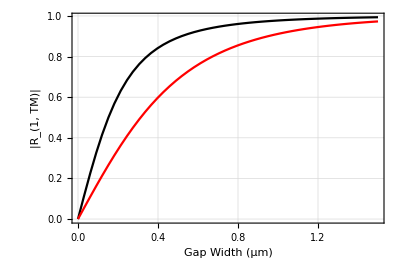

```mathematica
params$here = {n->1/1.5168,β->42Degree};

p$TM=ParametricPlot[{ (L*10^6)/(2π/(632.8*10^-9)) /. params$here,Abs[ErB1$TM /.params$here]},{L,0.000 99.29180321080256,0.1 1.5 99.29180321080256},PlotRange->All,Frame->True,GridLines->Automatic,FrameLabel->{"Gap Width (μm)", "|R_(1, TM)|"},PlotStyle->Red ];

p$TE=ParametricPlot[{ (L*10^6)/(2π/(632.8*10^-9)) /. params$here,Abs[ErB1$TE /.params$here]},{L,0.000 99.29180321080256,0.1 1.5 99.29180321080256},PlotRange->All,Frame->True,GridLines->Automatic,FrameLabel->{"Gap Width (μm)", "|R_(1, TM)|"},PlotStyle->Black ];

Show[p$TE,p$TM]
```

```mathematica
Manipulate[Plot[1/(Abs[μ+1 ⅇ^(ⅈ α)]/(1+μ^2)),{μ,0,3}],{α,0,π}]
```

```mathematica
ErB1$TM /. {n->1/1.5168,β->46. Degree,L->x*99.29180321080256}
```

-(0.125137 (-1+ⅇ^((-57.1411+0. ⅈ) x))+(0.+1.38854×10^-17 ⅈ) (1+ⅇ^((-57.1411+0. ⅈ) x)))/(0.00602028 (-1+ⅇ^((-57.1411+0. ⅈ) x))-(0.+0.124992 ⅈ) (1+ⅇ^((-57.1411+0. ⅈ) x)))

```mathematica
Abs[ErB1$TM /. {n->1/1.5168,β->44.Degree,L->0.04*99.29180321080256}]
```

0.722848

```mathematica
Abs[ErB1$TM /. {n->1/1.5168,β->41.537Degree,L->0.06*99.29180321080256}]
```

0.722828

The plot data below was take from the Data Record associated with the Blue Figure 11 analysis below.

```mathematica
R1y$plotdata={{0.00503566239942757,-3.304876353580189},{0.01007132479885514,-3.304163879245292},{0.01510698719828271,-3.30297692750685},{0.02014264959771028,-3.30131625557827},{0.025178311997137846,-3.299182921956503},{0.030213974396565414,-3.2965782844469547},{0.03524963679599299,-3.293503998194125},{0.04028529919542056,-3.2899620127561926},{0.04532096159484812,-3.285954568984952},{0.05035662399427569,-3.2814841954878347},{0.05539228639370326,-3.2765537044544666},{0.06042794879313084,-3.271166187145461},{0.06546361119255842,-3.265325009146485},{0.07049927359198598,-3.2590338046662777},{0.07553493599141355,-3.2522964712182274},{0.08057059839084112,-3.245117163345901},{0.08560626079026869,-3.2375002861424718},{0.09064192318969626,-3.2294504887987747},{0.09567758558912383,-3.220972657166679},{0.10071324798855139,-3.2120719067346557},{0.10071324798855139,-3.2120719067346557},{0.15106987198282706,-3.1010775611978767},{0.20142649597710277,-2.9548077731804225},{0.2517831199713785,-2.7808479808706674},{0.30213974396565413,-2.5872248118449095},{0.35249636795992983,-2.3817050032694613},{0.40285299195420554,-2.1712984852079003},{0.45320961594848125,-1.9619676007621203},{0.503566239942757,-1.7585079331722633},{0.5539228639370326,-1.5645545868918462},{0.6042794879313083,-1.3826703910564933},{0.654636111925584,-1.2144806895219953},{0.7049927359198597,-1.0608284266284804},{0.7553493599141354,-0.9219312482902449},{0.8057059839084111,-0.7975288284965025},{0.8560626079026867,-0.6870136232423054},{0.9064192318969625,-0.5895419272185916},{0.9567758558912381,-0.5041246618548291},{1.007132479885514,-0.42969897242392235},{1.0574891038797896,-0.3651826618950697},{1.1078457278740652,-0.30951392817584283},{1.1582023518683409,-0.26167896109371713},{1.2085589758626165,-0.22072982401245744},{1.2589155998568924,-0.18579479232240576},{1.309272223851168,-0.15608301086370108},{1.3596288478454437,-0.1308850156408053},{1.4099854718397193,-0.10957036492792309},{1.460342095833995,-0.09158335624755862},{1.5106987198282709,-0.07643757798568744}};
```

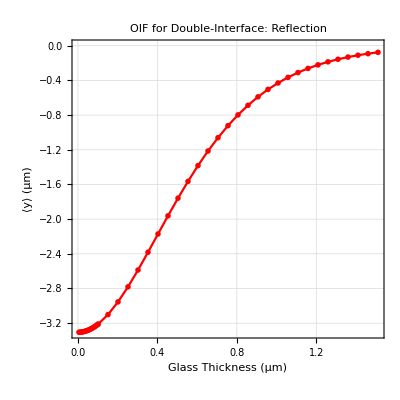

```mathematica
y1$singleboundary$44R=0;

p$y1$singleboundary$44R=Graphics[{Red,Thick,Dashing->Tiny,Line[{{-100,y1$singleboundary$44R},{100,y1$singleboundary$44R}}]}];

p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["⟨y⟩ (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

p$R1$final$y = Show[p$R1$y,AspectRatio->1]
```

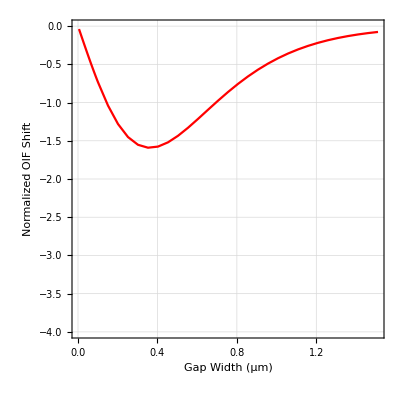

```mathematica
gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

ListLinePlot[Table[{R1y$plotdata[[i,1]],R1y$plotdata[[i,2]] Abs[ErB1$TM /.{n->1/1.5168,β->44.Degree, L->R1y$plotdata[[i,1]]2π/(632.8*10^-9)10^-6}]^1},{i,1,Length[R1y$plotdata]}],PlotRange->{-4,0},AspectRatio->1,Frame->True,GridLines->Automatic,FrameLabel->{"Gap Width (μm)", "Normalized OIF Shift"},PlotStyle->Red ]
```

#### s/TE/2 Polarization: Derivation of E-field Terms

⟦E_y⟧=0

⟦√ϵ E_y(k̂)_z⟧=0

E_i(r⃗, t) =  E_i  ⅇ^(ⅈ (k⃗·r⃗-ω t))ŷ

E_r(r⃗, t) =  E_r  ⅇ^(ⅈ (k⃗·r⃗-ω t))ŷ

E_t(r⃗, t) =  E_t  ⅇ^(ⅈ (k⃗·r⃗-ω t))ŷ

```mathematica
Clear[θ2,θ3];

θ2[θ_,n_]=ArcSin[1/n Sin[θ]];

θ3[θ_,n_]=ArcSin[n Sin[θ2[θ,n]]];
```

```mathematica
Clear[ki1,kr1,kr2,kt2,rvec,x,y,z];

ki1[θ_,n_]={Sin[θ],0,Cos[θ]};
kr1[θ_,n_]={Sin[θ],0,-Cos[θ]};
kt1[θ_,n_]={Sin[θ2[θ,n]],0,Cos[θ2[θ,n]]};
kr2[θ_,n_]={Sin[θ2[θ,n]],0,-Cos[θ2[θ,n]]};
kt2[θ_,n_]={Sin[θ3[θ,n]],0,Cos[θ3[θ,n]]};


rvec[x_,y_,z_]={x,y,z};
```

We therefore know the angles and can solve the 4 equations for the 4 unknowns that we have after setting EiB1 = 1 i.e. ErB1, EtB1, ErB2, EtB2.

In the analysis below, the characteristic length is taken to be 1/k_1. It is relevant that k_2/k_1=√(ϵ_2/ϵ_1)  as shown below ...

c = ω/k = 1/(√(μ μ_0 ϵ ϵ_0))

Therefore

k = ω √(μ μ_0 ϵ ϵ_0)

k_2/k_1 = √(ϵ_2/ϵ_1)

This term appears in the exponents of the third and fourth jump conditions below:

```mathematica
sol=Simplify[Solve[{
1 + ErB1 ==EtB1 + ErB2,
(1 -ErB1) Cos[θ1] == n(EtB1 - ErB2)Cos[θ2] ,

EtB1 Exp[ⅈ n kt1[θ,n].rvec[0,0,L]] + ErB2 Exp[ⅈ n kr2[θ,n].rvec[0,0,L]] == EtB2 Exp[ⅈ kt2[θ,n].rvec[0,0,L]],

n(EtB1 Exp[ⅈ n kt1[θ,n].rvec[0,0,L]] - ErB2 Exp[ⅈ n kr2[θ,n].rvec[0,0,L]]) Cos[θ2] == (EtB2 Exp[ⅈ kt2[θ,n].rvec[0,0,L]])Cos[θ3] 


},{ErB1, EtB1, ErB2, EtB2}]];
```

```mathematica
Clear[ErB1$TE,EtB1$TE,ErB2$TE,EtB2$TE];

ErB1$TE = Simplify[ErB1 /. sol[[1]] /. {θ1->θ, θ2->θ2[θ,n], θ3->θ3[θ,n]}]/. θ->β;

EtB1$TE = Simplify[EtB1 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,n], θ3->θ3[θ,n]}]/. θ->β;

ErB2$TE = Simplify[ErB2 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,n], θ3->θ3[θ,n]}]/. θ->β;

EtB2$TE = Simplify[EtB2 /. sol[[1]]  /. {θ1->θ, θ2->θ2[θ,n], θ3->θ3[θ,n]}]/. θ->β;
```

#### Effective Formula for R1 and R2

```mathematica
β =ArcCos[κvec.nvec];


βlin = Simplify[Expand[Simplify[Normal[Series[β,{κx,0,1},{κy,0,1}]],{n>0,θ>0,θ<π/2}]],{κx^2->0,κy^2->0,κx κy->0}]

βquad = Simplify[Expand[Normal[Series[β,{κx,0,1},{κy,0,2}]],{n>0,θ>0,θ<π/2}],{n>0,θ>0,θ<π/2}]


R1func = ErB1$TE /. θ->β;
R2func = ErB1$TM/. θ->β;
```

θ+κx

-1/4 Csc[θ]^2 (-2 κx+κx κy^2+κx (2+κy^2) Cos[2 θ]-4 θ Sin[θ]^2-κy^2 Sin[2 θ])

```mathematica
(*
ErB1$TE$lin =Simplify[Expand[Simplify[Normal[Series[ErB1$TE,{κx,0,1},{κy,0,1}]],{n>0,θ>0,θ<π/2}]],{κx^2->0,κy^2->0,κx κy->0}];

ErB1$TM$lin =Simplify[Expand[Simplify[Normal[Series[ErB1$TM,{κx,0,1},{κy,0,1}]],{n>0,θ>0,θ<π/2}]],{κx^2->0,κy^2->0,κx κy->0}];
*)
```

```mathematica
(*
R1$temp = ErB1$TE$lin /. θ->βlin;
R1lin = Expand[Normal[Series[R1$temp,{κx,0,1},{κy,0,1}]]]/.{κx^2->0,κy^2->0,κx κy->0};
*)
```

#### Decay Length

```mathematica
kt1[θ,n]
```

{Sin[θ]/n,0,√(1-Sin[θ]^2/n^2)}

```mathematica
Clear[char$decay$length];

char$decay$length[θ_,n_] = FullSimplify[1/√(Sin[θ]^2/n^2-1),{θ>0,θ<π/2,n>0}]
```

1/(√(-1+Sin[θ]^2/n^2))

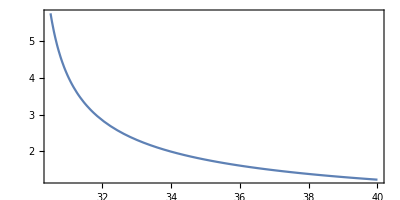

```mathematica
ParametricPlot[{θ,char$decay$length[θ Degree,0.5]},{θ,30.5,40},Frame->True,AspectRatio->.5,PlotRange->All]
```

### Centroid Shifts versus Sheet Width: n = 1.5168, θ = 60°, OAM = 5 (Glass Sheet) FIG 6

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

#### Ramsauer-Townsend Windows

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE /. {κx->0,κy->0}
```

(n √(1-(1-Cos[θ]^2)/n^2) (-(1+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2))) √(Cos[θ]^2)+(-1+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2))) n √(1-(1-Cos[θ]^2)/n^2))+Cos[θ] (√(Cos[θ]^2)+n √(1-(1-Cos[θ]^2)/n^2)+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2)) (-√(Cos[θ]^2)+n √(1-(1-Cos[θ]^2)/n^2))))/(-n √(1-(1-Cos[θ]^2)/n^2) (-(1+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2))) √(Cos[θ]^2)+(-1+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2))) n √(1-(1-Cos[θ]^2)/n^2))+Cos[θ] (√(Cos[θ]^2)+n √(1-(1-Cos[θ]^2)/n^2)+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2)) (-√(Cos[θ]^2)+n √(1-(1-Cos[θ]^2)/n^2))))

```mathematica
1/1.5168
```

0.659283

```mathematica
Manipulate[ParametricPlot[{θ,Abs[ErB1$TE$func[n,θ Degree,L]]},{θ,10 ,80 },AspectRatio->1],{n,0.5,2},{L,0.1,200.0}]
```

```mathematica
params$here = {wk->20000.,n->1.5168,θ->60 Degree,k0->1,p->0,ℓ->0};

L$ram = {};

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,2.5}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,5.0}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,7.5}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,10}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,12.2}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,15.08}];
AppendTo[L$ram,L /. sol[[1]]];

L$ram

L$ram$units = Table[L$ram[[j]]/(2π/(632.8*10^-9))*10^6,{j,1,Length[L$ram]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.52283,5.04567,7.5685,10.0913,12.6142,15.137}

{0.254083,0.508165,0.762248,1.01633,1.27041,1.5245}

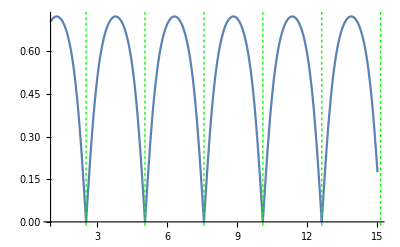

```mathematica
Clear[p$ram] ;

Array[p$ram,Length[L$ram]];

Do[p$ram[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram[[j]],-10000},{L$ram[[j]],10000}}]}],{j,1,Length[L$ram]}]

p$ram$all = Show[Table[p$ram[j],{j,1,Length[L$ram]}]];

Array[p$ram$all,Length[L$ram]];

Do[p$ram$units[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram$units[[j]],-10000},{L$ram$units[[j]],10000}}]}],{j,1,Length[L$ram]}]
p$ram$units$all = Show[Table[p$ram$units[j],{j,1,Length[L$ram]}]];

p$ram$final = Show[Plot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]],{L,1,15}],p$ram$all]
```

#### Analysis

```mathematica
Clear[plots,k0,β];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1.5168,θ->60.0 Degree,k0->1,p->0,ℓ->5,L->Lloop};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

Print["k_0L: ",Lloop, ", Actual Gap: ",gap," μm"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)


βtab = Table[ArcCos[κvec.nvec] /. params$here/.{κx->κtab[[i,j,1]],κy->κtab[[i,j,2]]},{i,1,dimset},{j,1,dimset}];

R1tab = Table[-ErB1$TM /.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];
R2tab = Table[ ErB1$TE/.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];


Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eRtab = Table[{(f[[1]]R1tab[[i,j]]-f[[2]]κtab[[i,j,2]] Cot[θ](R1tab[[i,j]]+R2tab[[i,j]])),f[[2]]R2tab[[i,j]] + f[[1]]κtab[[i,j,2]] Cot[θ](R1tab[[i,j]]+R2tab[[i,j]] ),-(f[[1]]R1tab[[i,j]] κtab[[i,j,1]] + f[[2]]R2tab[[i,j]]  κtab[[i,j,2]])}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,gap,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,gap,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,gap,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,gap,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{Lloop,1.0,15.0,0.2}]
```

k_0L: 1., Actual Gap: 0.100713 μm

TM (Reflected) = {-0.0315912,-9.18102} μm

TE (Reflected) = {-0.00219906,-0.484228} μm

spin+ (Reflected) = {-0.00252937,-0.511262} μm

spin- (Reflected) = {-0.00252937,-0.652666} μm

k_0L: 1.2, Actual Gap: 0.120856 μm

TM (Reflected) = {-0.0412205,-9.21842} μm

TE (Reflected) = {-0.0236839,-0.48052} μm

spin+ (Reflected) = {-0.0238912,-0.512748} μm

spin- (Reflected) = {-0.0238912,-0.65488} μm

k_0L: 1.4, Actual Gap: 0.140999 μm

TM (Reflected) = {-0.0510913,-9.27855} μm

TE (Reflected) = {-0.0472284,-0.51526} μm

spin+ (Reflected) = {-0.0472735,-0.546626} μm

spin- (Reflected) = {-0.0472735,-0.688579} μm

k_0L: 1.6, Actual Gap: 0.161141 μm

TM (Reflected) = {-0.0605313,-9.36949} μm

TE (Reflected) = {-0.0727272,-0.599587} μm

spin+ (Reflected) = {-0.072595,-0.624224} μm

spin- (Reflected) = {-0.072595,-0.765134} μm

k_0L: 1.8, Actual Gap: 0.181284 μm

TM (Reflected) = {-0.0689681,-9.50689} μm

TE (Reflected) = {-0.0996633,-0.760196} μm

spin+ (Reflected) = {-0.0993713,-0.773775} μm

spin- (Reflected) = {-0.0993713,-0.913022} μm

k_0L: 2., Actual Gap: 0.201426 μm

TM (Reflected) = {-0.0760636,-9.73177} μm

TE (Reflected) = {-0.12553,-1.0565} μm

spin+ (Reflected) = {-0.125134,-1.05727} μm

spin- (Reflected) = {-0.125134,-1.19463} μm

k_0L: 2.2, Actual Gap: 0.221569 μm

TM (Reflected) = {-0.0817983,-10.1931} μm

TE (Reflected) = {-0.143333,-1.65248} μm

spin+ (Reflected) = {-0.142921,-1.64173} μm

spin- (Reflected) = {-0.142921,-1.77745} μm

k_0L: 2.4, Actual Gap: 0.241712 μm

TM (Reflected) = {-0.0864807,-12.0301} μm

TE (Reflected) = {-0.141686,-3.66469} μm

spin+ (Reflected) = {-0.141361,-3.64657} μm

spin- (Reflected) = {-0.141361,-3.78128} μm

k_0L: 2.6, Actual Gap: 0.261854 μm

TM (Reflected) = {-0.0906772,-4.54532} μm

TE (Reflected) = {-0.116486,3.69184} μm

spin+ (Reflected) = {-0.116337,3.71138} μm

spin- (Reflected) = {-0.116337,3.57678} μm

k_0L: 2.8, Actual Gap: 0.281997 μm

TM (Reflected) = {-0.0950738,-7.91616} μm

TE (Reflected) = {-0.0832106,0.31346} μm

spin+ (Reflected) = {-0.0832871,0.328096} μm

spin- (Reflected) = {-0.0832871,0.192675} μm

k_0L: 3., Actual Gap: 0.30214 μm

TM (Reflected) = {-0.100307,-8.49421} μm

TE (Reflected) = {-0.0606826,-0.176244} μm

spin+ (Reflected) = {-0.0609867,-0.171604} μm

spin- (Reflected) = {-0.0609867,-0.308555} μm

k_0L: 3.2, Actual Gap: 0.322282 μm

TM (Reflected) = {-0.106809,-8.7601} μm

TE (Reflected) = {-0.0538264,-0.321056} μm

spin+ (Reflected) = {-0.0543123,-0.329038} μm

spin- (Reflected) = {-0.0543123,-0.467859} μm

k_0L: 3.4, Actual Gap: 0.342425 μm

TM (Reflected) = {-0.114702,-8.93763} μm

TE (Reflected) = {-0.0592905,-0.380456} μm

spin+ (Reflected) = {-0.0598764,-0.400644} μm

spin- (Reflected) = {-0.0598764,-0.541216} μm

k_0L: 3.6, Actual Gap: 0.362568 μm

TM (Reflected) = {-0.123779,-9.09008} μm

TE (Reflected) = {-0.0733341,-0.427573} μm

spin+ (Reflected) = {-0.0739165,-0.456681} μm

spin- (Reflected) = {-0.0739165,-0.598466} μm

k_0L: 3.8, Actual Gap: 0.38271 μm

TM (Reflected) = {-0.133553,-9.24722} μm

TE (Reflected) = {-0.0939503,-0.493168} μm

spin+ (Reflected) = {-0.0944197,-0.525854} μm

spin- (Reflected) = {-0.0944197,-0.668028} μm

k_0L: 4., Actual Gap: 0.402853 μm

TM (Reflected) = {-0.143374,-9.43091} μm

TE (Reflected) = {-0.120591,-0.601598} μm

spin+ (Reflected) = {-0.120852,-0.631702} μm

spin- (Reflected) = {-0.120852,-0.773346} μm

k_0L: 4.2, Actual Gap: 0.422996 μm

TM (Reflected) = {-0.152581,-9.6673} μm

TE (Reflected) = {-0.153422,-0.788932} μm

spin+ (Reflected) = {-0.153413,-0.810865} μm

spin- (Reflected) = {-0.153413,-0.951188} μm

k_0L: 4.4, Actual Gap: 0.443138 μm

TM (Reflected) = {-0.160656,-10.0056} μm

TE (Reflected) = {-0.192027,-1.12649} μm

spin+ (Reflected) = {-0.191747,-1.13654} μm

spin- (Reflected) = {-0.191747,-1.27506} μm

k_0L: 4.6, Actual Gap: 0.463281 μm

TM (Reflected) = {-0.167345,-10.5795} μm

TE (Reflected) = {-0.232478,-1.7834} μm

spin+ (Reflected) = {-0.231993,-1.78064} μm

spin- (Reflected) = {-0.231993,-1.91731} μm

k_0L: 4.8, Actual Gap: 0.483424 μm

TM (Reflected) = {-0.172725,-11.96} μm

TE (Reflected) = {-0.262432,-3.35992} μm

spin+ (Reflected) = {-0.261867,-3.3465} μm

spin- (Reflected) = {-0.261867,-3.48173} μm

k_0L: 5., Actual Gap: 0.503566 μm

TM (Reflected) = {-0.177191,-24.7474} μm

TE (Reflected) = {-0.262262,-16.4163} μm

spin+ (Reflected) = {-0.261772,-16.397} μm

spin- (Reflected) = {-0.261772,-16.5316} μm

k_0L: 5.2, Actual Gap: 0.523709 μm

TM (Reflected) = {-0.181364,-4.58863} μm

TE (Reflected) = {-0.226824,3.54377} μm

spin+ (Reflected) = {-0.226553,3.56265} μm

spin- (Reflected) = {-0.226553,3.42783} μm

k_0L: 5.4, Actual Gap: 0.543852 μm

TM (Reflected) = {-0.185935,-7.27195} μm

TE (Reflected) = {-0.179751,0.829191} μm

spin+ (Reflected) = {-0.179793,0.841523} μm

spin- (Reflected) = {-0.179793,0.70558} μm

k_0L: 5.6, Actual Gap: 0.563994 μm

TM (Reflected) = {-0.191497,-8.07839} μm

TE (Reflected) = {-0.145314,0.121639} μm

spin+ (Reflected) = {-0.145695,0.122905} μm

spin- (Reflected) = {-0.145695,-0.0147522} μm

k_0L: 5.8, Actual Gap: 0.584137 μm

TM (Reflected) = {-0.198402,-8.51096} μm

TE (Reflected) = {-0.129764,-0.158649} μm

spin+ (Reflected) = {-0.130433,-0.170257} μm

spin- (Reflected) = {-0.130433,-0.309793} μm

k_0L: 6., Actual Gap: 0.604279 μm

TM (Reflected) = {-0.206678,-8.81985} μm

TE (Reflected) = {-0.130057,-0.305925} μm

spin+ (Reflected) = {-0.130901,-0.329138} μm

spin- (Reflected) = {-0.130901,-0.470261} μm

k_0L: 6.2, Actual Gap: 0.624422 μm

TM (Reflected) = {-0.216026,-9.08973} μm

TE (Reflected) = {-0.142542,-0.42068} μm

spin+ (Reflected) = {-0.143405,-0.451519} μm

spin- (Reflected) = {-0.143405,-0.593562} μm

k_0L: 6.4, Actual Gap: 0.644565 μm

TM (Reflected) = {-0.225896,-9.36503} μm

TE (Reflected) = {-0.165348,-0.553246} μm

spin+ (Reflected) = {-0.166061,-0.585977} μm

spin- (Reflected) = {-0.166061,-0.728052} μm

k_0L: 6.6, Actual Gap: 0.664707 μm

TM (Reflected) = {-0.235617,-9.6826} μm

TE (Reflected) = {-0.198287,-0.7486} μm

spin+ (Reflected) = {-0.198701,-0.777043} μm

spin- (Reflected) = {-0.198701,-0.918258} μm

k_0L: 6.8, Actual Gap: 0.68485 μm

TM (Reflected) = {-0.244551,-10.093} μm

TE (Reflected) = {-0.241983,-1.07636} μm

spin+ (Reflected) = {-0.242009,-1.09529} μm

spin- (Reflected) = {-0.242009,-1.23495} μm

k_0L: 7., Actual Gap: 0.704993 μm

TM (Reflected) = {-0.25224,-10.703} μm

TE (Reflected) = {-0.295717,-1.68141} μm

spin+ (Reflected) = {-0.295354,-1.68781} μm

spin- (Reflected) = {-0.295354,-1.8256} μm

k_0L: 7.2, Actual Gap: 0.725135 μm

TM (Reflected) = {-0.258523,-11.8423} μm

TE (Reflected) = {-0.352072,-2.95086} μm

spin+ (Reflected) = {-0.351421,-2.94466} μm

spin- (Reflected) = {-0.351421,-3.08071} μm

k_0L: 7.4, Actual Gap: 0.745278 μm

TM (Reflected) = {-0.263574,-15.4029} μm

TE (Reflected) = {-0.389472,-6.81051} μm

spin+ (Reflected) = {-0.388715,-6.79472} μm

spin- (Reflected) = {-0.388715,-6.92959} μm

k_0L: 7.6, Actual Gap: 0.765421 μm

TM (Reflected) = {-0.26787,24.7834} μm

TE (Reflected) = {-0.380137,33.0014} μm

spin+ (Reflected) = {-0.379492,33.0214} μm

spin- (Reflected) = {-0.379492,32.8869} μm

k_0L: 7.8, Actual Gap: 0.785563 μm

TM (Reflected) = {-0.272071,-4.66118} μm

TE (Reflected) = {-0.326332,3.31833} μm

spin+ (Reflected) = {-0.325993,3.3361} μm

spin- (Reflected) = {-0.325993,3.20094} μm

k_0L: 8., Actual Gap: 0.805706 μm

TM (Reflected) = {-0.276863,-6.91806} μm

TE (Reflected) = {-0.264123,1.04603} μm

spin+ (Reflected) = {-0.264217,1.0557} μm

spin- (Reflected) = {-0.264217,0.919148} μm

k_0L: 8.2, Actual Gap: 0.825849 μm

TM (Reflected) = {-0.282785,-7.82747} μm

TE (Reflected) = {-0.220187,0.273056} μm

spin+ (Reflected) = {-0.22074,0.27077} μm

spin- (Reflected) = {-0.22074,0.132382} μm

k_0L: 8.4, Actual Gap: 0.845991 μm

TM (Reflected) = {-0.290102,-8.37653} μm

TE (Reflected) = {-0.199285,-0.0780785} μm

spin+ (Reflected) = {-0.200218,-0.0932814} μm

spin- (Reflected) = {-0.200218,-0.233488} μm

k_0L: 8.6, Actual Gap: 0.866134 μm

TM (Reflected) = {-0.298742,-8.79581} μm

TE (Reflected) = {-0.197647,-0.285603} μm

spin+ (Reflected) = {-0.198797,-0.311615} μm

spin- (Reflected) = {-0.198797,-0.453189} μm

k_0L: 8.8, Actual Gap: 0.886277 μm

TM (Reflected) = {-0.308324,-9.17689} μm

TE (Reflected) = {-0.211609,-0.459526} μm

spin+ (Reflected) = {-0.212755,-0.491729} μm

spin- (Reflected) = {-0.212755,-0.633894} μm

k_0L: 9., Actual Gap: 0.906419 μm

TM (Reflected) = {-0.318241,-9.57524} μm

TE (Reflected) = {-0.239681,-0.665} μm

spin+ (Reflected) = {-0.240591,-0.697345} μm

spin- (Reflected) = {-0.240591,-0.839187} μm

k_0L: 9.2, Actual Gap: 0.926562 μm

TM (Reflected) = {-0.327813,-10.0454} μm

TE (Reflected) = {-0.282316,-0.97148} μm

spin+ (Reflected) = {-0.2828,-0.997862} μm

spin- (Reflected) = {-0.2828,-1.13854} μm

k_0L: 9.4, Actual Gap: 0.946705 μm

TM (Reflected) = {-0.336432,-10.6752} μm

TE (Reflected) = {-0.340592,-1.49886} μm

spin+ (Reflected) = {-0.340553,-1.51451} μm

spin- (Reflected) = {-0.340553,-1.65347} μm

k_0L: 9.6, Actual Gap: 0.966847 μm

TM (Reflected) = {-0.343716,-11.6758} μm

TE (Reflected) = {-0.412377,-2.51898} μm

spin+ (Reflected) = {-0.411843,-2.52164} μm

spin- (Reflected) = {-0.411843,-2.65872} μm

k_0L: 9.8, Actual Gap: 0.98699 μm

TM (Reflected) = {-0.349599,-13.8246} μm

TE (Reflected) = {-0.483315,-4.88946} μm

spin+ (Reflected) = {-0.482443,-4.87996} μm

spin- (Reflected) = {-0.482443,-5.01547} μm

k_0L: 10., Actual Gap: 1.00713 μm

TM (Reflected) = {-0.354353,-24.6959} μm

TE (Reflected) = {-0.518967,-16.1965} μm

spin+ (Reflected) = {-0.518009,-16.1787} μm

spin- (Reflected) = {-0.518009,-16.3133} μm

k_0L: 10.2, Actual Gap: 1.02728 μm

TM (Reflected) = {-0.358526,3.89075} μm

TE (Reflected) = {-0.48888,11.9287} μm

spin+ (Reflected) = {-0.488117,11.949} μm

spin- (Reflected) = {-0.488117,11.8143} μm

k_0L: 10.4, Actual Gap: 1.04742 μm

TM (Reflected) = {-0.36281,-4.76353} μm

TE (Reflected) = {-0.412611,3.04035} μm

spin+ (Reflected) = {-0.412282,3.05658} μm

spin- (Reflected) = {-0.412282,2.92095} μm

k_0L: 10.6, Actual Gap: 1.06756 μm

TM (Reflected) = {-0.367869,-6.73741} μm

TE (Reflected) = {-0.33728,1.10126} μm

spin+ (Reflected) = {-0.337522,1.10795} μm

spin- (Reflected) = {-0.337522,0.970711} μm

k_0L: 10.8, Actual Gap: 1.0877 μm

TM (Reflected) = {-0.374179,-7.70018} μm

TE (Reflected) = {-0.287327,0.330373} μm

spin+ (Reflected) = {-0.288144,0.324386} μm

spin- (Reflected) = {-0.288144,0.18527} μm

k_0L: 11., Actual Gap: 1.10785 μm

TM (Reflected) = {-0.381909,-8.33973} μm

TE (Reflected) = {-0.264416,-0.0571894} μm

spin+ (Reflected) = {-0.26568,-0.075921} μm

spin- (Reflected) = {-0.26568,-0.21673} μm

k_0L: 11.2, Actual Gap: 1.12799 μm

TM (Reflected) = {-0.390892,-8.85904} μm

TE (Reflected) = {-0.26389,-0.31111} μm

spin+ (Reflected) = {-0.265368,-0.339661} μm

spin- (Reflected) = {-0.265368,-0.481567} μm

k_0L: 11.4, Actual Gap: 1.14813 μm

TM (Reflected) = {-0.400664,-9.35181} μm

TE (Reflected) = {-0.282295,-0.544297} μm

spin+ (Reflected) = {-0.283696,-0.577466} μm

spin- (Reflected) = {-0.283696,-0.719616} μm

k_0L: 11.6, Actual Gap: 1.16827 μm

TM (Reflected) = {-0.410578,-9.88494} μm

TE (Reflected) = {-0.318833,-0.837382} μm

spin+ (Reflected) = {-0.31987,-0.86889} μm

spin- (Reflected) = {-0.31987,-1.01037} μm

k_0L: 11.8, Actual Gap: 1.18842 μm

TM (Reflected) = {-0.419948,-10.5376} μm

TE (Reflected) = {-0.374812,-1.29383} μm

spin+ (Reflected) = {-0.37527,-1.31774} μm

spin- (Reflected) = {-0.37527,-1.4578} μm

k_0L: 12., Actual Gap: 1.20856 μm

TM (Reflected) = {-0.428216,-11.4583} μm

TE (Reflected) = {-0.451379,-2.11322} μm

spin+ (Reflected) = {-0.451177,-2.12534} μm

spin- (Reflected) = {-0.451177,-2.26356} μm

k_0L: 12.2, Actual Gap: 1.2287 μm

TM (Reflected) = {-0.435081,-13.0592} μm

TE (Reflected) = {-0.542774,-3.79726} μm

spin+ (Reflected) = {-0.541994,-3.79614} μm

spin- (Reflected) = {-0.541994,-3.93255} μm

k_0L: 12.4, Actual Gap: 1.24884 μm

TM (Reflected) = {-0.440576,-17.2719} μm

TE (Reflected) = {-0.622932,-8.37095} μm

spin+ (Reflected) = {-0.621807,-8.35834} μm

spin- (Reflected) = {-0.621807,-8.49341} μm

k_0L: 12.6, Actual Gap: 1.26899 μm

TM (Reflected) = {-0.445066,-134.844} μm

TE (Reflected) = {-0.643761,-126.556} μm

spin+ (Reflected) = {-0.642619,-126.537} μm

spin- (Reflected) = {-0.642619,-126.671} μm

k_0L: 12.8, Actual Gap: 1.28913 μm

TM (Reflected) = {-0.44917,0.266901} μm

TE (Reflected) = {-0.583659,8.07788} μm

spin+ (Reflected) = {-0.582843,8.09796} μm

spin- (Reflected) = {-0.582843,7.96302} μm

k_0L: 13., Actual Gap: 1.30927 μm

TM (Reflected) = {-0.453591,-4.89649} μm

TE (Reflected) = {-0.485516,2.7342} μm

spin+ (Reflected) = {-0.485291,2.74841} μm

spin- (Reflected) = {-0.485291,2.61223} μm

k_0L: 13.2, Actual Gap: 1.32941 μm

TM (Reflected) = {-0.458963,-6.6755} μm

TE (Reflected) = {-0.401092,1.06443} μm

spin+ (Reflected) = {-0.401583,1.0678} μm

spin- (Reflected) = {-0.401583,0.929843} μm

k_0L: 13.4, Actual Gap: 1.34956 μm

TM (Reflected) = {-0.465683,-7.67259} μm

TE (Reflected) = {-0.348847,0.324731} μm

spin+ (Reflected) = {-0.350012,0.314926} μm

spin- (Reflected) = {-0.350012,0.17511} μm

k_0L: 13.6, Actual Gap: 1.3697 μm

TM (Reflected) = {-0.473824,-8.39033} μm

TE (Reflected) = {-0.327066,-0.0827104} μm

spin+ (Reflected) = {-0.328706,-0.104862} μm

spin- (Reflected) = {-0.328706,-0.246183} μm

k_0L: 13.8, Actual Gap: 1.38984 μm

TM (Reflected) = {-0.483122,-9.00686} μm

TE (Reflected) = {-0.330539,-0.378907} μm

spin+ (Reflected) = {-0.33234,-0.409691} μm

spin- (Reflected) = {-0.33234,-0.551801} μm

k_0L: 14., Actual Gap: 1.40999 μm

TM (Reflected) = {-0.493039,-9.61798} μm

TE (Reflected) = {-0.356384,-0.679263} μm

spin+ (Reflected) = {-0.357985,-0.712962} μm

spin- (Reflected) = {-0.357985,-0.854959} μm

k_0L: 14.2, Actual Gap: 1.43013 μm

TM (Reflected) = {-0.502893,-10.3057} μm

TE (Reflected) = {-0.404811,-1.08519} μm

spin+ (Reflected) = {-0.405882,-1.11539} μm

spin- (Reflected) = {-0.405882,-1.25639} μm

k_0L: 14.4, Actual Gap: 1.45027 μm

TM (Reflected) = {-0.512012,-11.1865} μm

TE (Reflected) = {-0.478018,-1.75126} μm

spin+ (Reflected) = {-0.478345,-1.77231} μm

spin- (Reflected) = {-0.478345,-1.91169} μm

k_0L: 14.6, Actual Gap: 1.47041 μm

TM (Reflected) = {-0.519894,-12.5136} μm

TE (Reflected) = {-0.576163,-3.00815} μm

spin+ (Reflected) = {-0.575707,-3.01649} μm

spin- (Reflected) = {-0.575707,-3.15398} μm

k_0L: 14.8, Actual Gap: 1.49056 μm

TM (Reflected) = {-0.52633,-15.114} μm

TE (Reflected) = {-0.686117,-5.80431} μm

spin+ (Reflected) = {-0.685036,-5.79941} μm

spin- (Reflected) = {-0.685036,-5.93522} μm

k_0L: 15., Actual Gap: 1.5107 μm

TM (Reflected) = {-0.531455,-24.6098} μm

TE (Reflected) = {-0.765051,-15.8423} μm

spin+ (Reflected) = {-0.763668,-15.8269} μm

spin- (Reflected) = {-0.763668,-15.9616} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->60.0 Degree,k0->1,p->0,ℓ->5,L->Lloop}
```

{wk→20000.,n→1.5168,θ→1.0472,k0→1,p→0,ℓ→5,L→Lloop}

```mathematica
shift$tab$R4
```

{{5,10.,{-0.146307,-0.175866}},{5,12.,{-0.173771,-0.15973}},{5,14.,{-0.200508,-0.119476}},{5,16.,{-0.226596,-0.0528385}},{5,18.,{-0.252196,0.0429163}},{5,20.,{-0.277539,0.171751}},{5,22.,{-0.302925,0.339925}},{5,24.,{-0.328706,0.557628}},{5,26.,{-0.355274,0.841819}},{5,28.,{-0.383051,1.22175}},{5,30.,{-0.412466,1.75099}},{5,32.,{-0.443882,2.5371}},{5,34.,{-0.477361,3.82909}},{5,36.,{-0.512176,6.36319}},{5,38.,{-0.546087,13.7774}},{5,40.,{-0.574862,-0.880385}},{5,42.,{-0.592883,-14.7207}},{5,44.,{-0.595257,-7.16416}},{5,46.,{-0.580335,-4.44421}},{5,48.,{-0.550592,-2.972}},{5,50.,{-0.511219,-2.04586}},{5,52.,{-0.467864,-1.43169}},{5,54.,{-0.425191,-1.02111}},{5,56.,{-0.386521,-0.749041}},{5,58.,{-0.353903,-0.567248}},{5,60.,{-0.328158,-0.435337}},{5,62.,{-0.308973,-0.319747}},{5,64.,{-0.29532,-0.195458}},{5,66.,{-0.286124,-0.0458278}},{5,68.,{-0.280819,0.14107}},{5,70.,{-0.279587,0.378531}},{5,72.,{-0.283336,0.68889}},{5,74.,{-0.293635,1.11513}},{5,76.,{-0.31279,1.74597}},{5,78.,{-0.344263,2.78847}},{5,80.,{-0.393939,4.84968}}}

```mathematica
shift$tab$R1={{5,0.10071324798855139,{-0.03159115210226968,-9.18101831365448}},{5,0.12085589758626165,{-0.04122051406148857,-9.218423342298504}},{5,0.14099854718397192,{-0.051091260166341974,-9.278554386809605}},{5,0.16114119678168223,{-0.0605312868283761,-9.36948729457457}},{5,0.1812838463793925,{-0.0689680796542593,-9.506885571010022}},{5,0.20142649597710277,{-0.0760636461250841,-9.731770403798917}},{5,0.22156914557481305,{-0.08179830185234545,-10.193083589193739}},{5,0.24171179517252336,{-0.08648072968237391,-12.030141431699171}},{5,0.2618544447702336,{-0.09067717618648499,-4.545318096052276}},{5,0.28199709436794385,{-0.09507377004630864,-7.916162094575748}},{5,0.30213974396565413,{-0.10030726514316836,-8.494206531990455}},{5,0.32228239356336447,{-0.10680884971929419,-8.760095278319232}},{5,0.34242504316107475,{-0.1147022860176381,-8.937626342925828}},{5,0.362567692758785,{-0.12377915994805619,-9.090078349092428}},{5,0.3827103423564953,{-0.13355270056837076,-9.24722477364958}},{5,0.40285299195420554,{-0.1433736623146205,-9.430914979117718}},{5,0.4229956415519158,{-0.15258104923270957,-9.667299336832812}},{5,0.4431382911496261,{-0.1606557637276583,-10.005623410883244}},{5,0.46328094074733633,{-0.16734452699086216,-10.579531677960885}},{5,0.4834235903450467,{-0.17272482017582988,-11.959958036980339}},{5,0.503566239942757,{-0.17719149343910678,-24.747441364132776}},{5,0.5237088895404672,{-0.18136422135396102,-4.588630022724488}},{5,0.5438515391381775,{-0.18593470876056653,-7.271950360436743}},{5,0.5639941887358878,{-0.19149697211475505,-8.078393853555966}},{5,0.5841368383335981,{-0.19840224107829152,-8.51095514968117}},{5,0.6042794879313083,{-0.20667785304350428,-8.819851186579802}},{5,0.6244221375290187,{-0.21602572117686764,-9.089733532080828}},{5,0.6445647871267289,{-0.22589622431186226,-9.365028608018683}},{5,0.6647074367244392,{-0.235617412767852,-9.682597271721269}},{5,0.6848500863221495,{-0.24455062662591298,-10.09301190414715}},{5,0.7049927359198597,{-0.252239937712114,-10.702988183577261}},{5,0.72513538551757,{-0.25852281972613167,-11.842253756346418}},{5,0.7452780351152802,{-0.2635743609067201,-15.402933867720641}},{5,0.7654206847129906,{-0.26787039128180995,24.783440344604134}},{5,0.7855633343107009,{-0.27207139962073024,-4.6611814305971295}},{5,0.8057059839084111,{-0.2768633445302171,-6.918062621819321}},{5,0.8258486335061213,{-0.28278542022557407,-7.827474298234879}},{5,0.8459912831038316,{-0.29010185458761417,-8.376527008096499}},{5,0.866133932701542,{-0.2987423519954147,-8.795814326856581}},{5,0.8862765822992522,{-0.3083235064240988,-9.17689299601118}},{5,0.9064192318969625,{-0.3182414401768885,-9.575238432599381}},{5,0.9265618814946729,{-0.32781254053331355,-10.045414364879798}},{5,0.9467045310923831,{-0.3364319296648521,-10.67519484530494}},{5,0.9668471806900932,{-0.3437163976411248,-11.675750018803043}},{5,0.9869898302878036,{-0.34959944035834617,-13.824621284594102}},{5,1.007132479885514,{-0.3543528775307528,-24.69585680370665}},{5,1.0272751294832243,{-0.3585259672297361,3.8907537367807636}},{5,1.0474177790809345,{-0.3628097210691042,-4.763531185083871}},{5,1.0675604286786449,{-0.36786926697902145,-6.73741346295222}},{5,1.087703078276355,{-0.3741785703579139,-7.700184086768762}},{5,1.1078457278740652,{-0.3819087846277935,-8.339733422974524}},{5,1.1279883774717756,{-0.39089186062275033,-8.859043019142945}},{5,1.1481310270694858,{-0.40066440935515574,-9.351809256112606}},{5,1.1682736766671962,{-0.4105777034433201,-9.884941116227397}},{5,1.1884163262649063,{-0.4199481152992458,-10.53755910085457}},{5,1.2085589758626165,{-0.42821626085754805,-11.458291260792574}},{5,1.228701625460327,{-0.43508090904599983,-13.059243806630194}},{5,1.2488442750580373,{-0.4405758754742068,-17.271876586638943}},{5,1.2689869246557477,{-0.4450657223577304,-134.84400193757415}},{5,1.2891295742534579,{-0.4491698978964226,0.2669009340630706}},{5,1.309272223851168,{-0.453591208782681,-4.896485289225164}},{5,1.3294148734488784,{-0.4589627132610717,-6.6754953503528895}},{5,1.3495575230465886,{-0.4656825478070454,-7.6725891640743376}},{5,1.369700172644299,{-0.47382375792722436,-8.390327855596029}},{5,1.3898428222420092,{-0.48312157919881654,-9.006859714636938}},{5,1.4099854718397193,{-0.4930390691355952,-9.617983127138366}},{5,1.4301281214374297,{-0.5028930106868154,-10.305713527980206}},{5,1.45027077103514,{-0.5120121164781009,-11.186464260368417}},{5,1.4704134206328503,{-0.519894454015659,-12.513637678520857}},{5,1.4905560702305605,{-0.526329570010913,-15.114023966074054}},{5,1.5106987198282709,{-0.5314546308789265,-24.60977349621151}}};
```

```mathematica
shift$tab$R2={{5,0.10071324798855139,{-0.00219906126507848,-0.4842284941033363}},{5,0.12085589758626165,{-0.023683925700118204,-0.48051969452328347}},{5,0.14099854718397192,{-0.04722840700749635,-0.5152601785855196}},{5,0.16114119678168223,{-0.0727272089683928,-0.599586781061087}},{5,0.1812838463793925,{-0.09966328033664301,-0.7601957178314849}},{5,0.20142649597710277,{-0.12553040398805498,-1.0565042697027929}},{5,0.22156914557481305,{-0.14333263859920603,-1.652476254493825}},{5,0.24171179517252336,{-0.141686200739292,-3.6646932081394135}},{5,0.2618544447702336,{-0.11648618251938841,3.691842357885165}},{5,0.28199709436794385,{-0.08321056347778771,0.31345963015786693}},{5,0.30213974396565413,{-0.06068256671739621,-0.17624358124240716}},{5,0.32228239356336447,{-0.05382637997245106,-0.32105564333154213}},{5,0.34242504316107475,{-0.05929050903670315,-0.380456305831683}},{5,0.362567692758785,{-0.07333412214822503,-0.4275730920074805}},{5,0.3827103423564953,{-0.09395028084876886,-0.49316765017483477}},{5,0.40285299195420554,{-0.12059121794730848,-0.6015980237285788}},{5,0.4229956415519158,{-0.15342172109105148,-0.7889319092994793}},{5,0.4431382911496261,{-0.19202675318733772,-1.1264917402508545}},{5,0.46328094074733633,{-0.23247846897300325,-1.7834040192789622}},{5,0.4834235903450467,{-0.2624323744214496,-3.3599152748644667}},{5,0.503566239942757,{-0.26226197481226515,-16.416327015215}},{5,0.5237088895404672,{-0.2268240157521216,3.5437653714911073}},{5,0.5438515391381775,{-0.1797509948992538,0.8291909449321019}},{5,0.5639941887358878,{-0.14531442761325458,0.12163868453182741}},{5,0.5841368383335981,{-0.12976378891795198,-0.15864939855370358}},{5,0.6042794879313083,{-0.1300573127602417,-0.3059249586439972}},{5,0.6244221375290187,{-0.14254190272305597,-0.4206802109687599}},{5,0.6445647871267289,{-0.16534790180478198,-0.5532456945447395}},{5,0.6647074367244392,{-0.19828690323311315,-0.7486002633889175}},{5,0.6848500863221495,{-0.2419834662824854,-1.0763560429779067}},{5,0.7049927359198597,{-0.2957167242624122,-1.6814118749302949}},{5,0.72513538551757,{-0.3520716692676395,-2.950863526303955}},{5,0.7452780351152802,{-0.38947213086148214,-6.810512877407692}},{5,0.7654206847129906,{-0.38013741724943106,33.00139246166904}},{5,0.7855633343107009,{-0.32633180273565804,3.3183265099121195}},{5,0.8057059839084111,{-0.26412279094214564,1.0460276782752447}},{5,0.8258486335061213,{-0.22018729738147172,0.27305578388260615}},{5,0.8459912831038316,{-0.1992845032668496,-0.07807849286551741}},{5,0.866133932701542,{-0.1976466077258974,-0.28560314936000825}},{5,0.8862765822992522,{-0.21160918478773405,-0.45952568765394836}},{5,0.9064192318969625,{-0.2396810008445673,-0.6649997927751592}},{5,0.9265618814946729,{-0.282315520921236,-0.971479996604261}},{5,0.9467045310923831,{-0.3405918836716711,-1.4988568507704967}},{5,0.9668471806900932,{-0.4123765644690313,-2.5189820291580802}},{5,0.9869898302878036,{-0.48331486361923204,-4.8894550371868775}},{5,1.007132479885514,{-0.5189673634902866,-16.19652068747315}},{5,1.0272751294832243,{-0.4888802450150465,11.928737360087254}},{5,1.0474177790809345,{-0.4126111756230424,3.040352838577392}},{5,1.0675604286786449,{-0.3372804578119709,1.1012640629515904}},{5,1.087703078276355,{-0.28732680678624517,0.3303733543375516}},{5,1.1078457278740652,{-0.2644158027277909,-0.05718944493338255}},{5,1.1279883774717756,{-0.26388966054690244,-0.31111019257387135}},{5,1.1481310270694858,{-0.28229482014231255,-0.5442974375543169}},{5,1.1682736766671962,{-0.31883304465837803,-0.8373817438373515}},{5,1.1884163262649063,{-0.3748116675202503,-1.2938257451772557}},{5,1.2085589758626165,{-0.4513787276707543,-2.1132246750436052}},{5,1.228701625460327,{-0.542774051639381,-3.7972590050727173}},{5,1.2488442750580373,{-0.6229320245367364,-8.370947389334484}},{5,1.2689869246557477,{-0.6437609114922437,-126.55621683451506}},{5,1.2891295742534579,{-0.583659391943757,8.077875396512683}},{5,1.309272223851168,{-0.48551649615931225,2.734195510638758}},{5,1.3294148734488784,{-0.4010921733659923,1.0644293066869535}},{5,1.3495575230465886,{-0.3488469600781513,0.3247307911310331}},{5,1.369700172644299,{-0.3270661862811748,-0.08271038715554707}},{5,1.3898428222420092,{-0.33053919193445547,-0.3789073911015709}},{5,1.4099854718397193,{-0.35638407330714267,-0.6792629486329618}},{5,1.4301281214374297,{-0.40481065037809755,-1.085185831097485}},{5,1.45027077103514,{-0.4780181040625023,-1.7512640576844167}},{5,1.4704134206328503,{-0.5761634845960317,-3.0081478137811772}},{5,1.4905560702305605,{-0.686117452960053,-5.804312585045557}},{5,1.5106987198282709,{-0.7650512373522301,-15.842327497655647}}};
```

```mathematica
shift$tab$R3={{5,0.10071324798855139,{-0.002529374760558778,-0.5112624957151597}},{5,0.12085589758626165,{-0.0238912330153539,-0.5127478151156535}},{5,0.14099854718397192,{-0.047273519006654434,-0.5466255035917484}},{5,0.16114119678168223,{-0.07259496701955,-0.6242242588057982}},{5,0.1812838463793925,{-0.09937129200592458,-0.773774533656484}},{5,0.20142649597710277,{-0.1251344148025975,-1.0572687791177895}},{5,0.22156914557481305,{-0.1429211243777137,-1.641732859708396}},{5,0.24171179517252336,{-0.14136130818926435,-3.646567283118283}},{5,0.2618544447702336,{-0.11633653294604084,3.711383962362709}},{5,0.28199709436794385,{-0.0832870718072555,0.32809558478979167}},{5,0.30213974396565413,{-0.06098666761739539,-0.17160423003732686}},{5,0.32228239356336447,{-0.05431227252829636,-0.32903802141418276}},{5,0.34242504316107475,{-0.059876371212026346,-0.40064388366612547}},{5,0.362567692758785,{-0.07391646353623862,-0.4566806877591263}},{5,0.3827103423564953,{-0.09441974153529166,-0.5258544883342691}},{5,0.40285299195420554,{-0.12085163749127123,-0.631701514024819}},{5,0.4229956415519158,{-0.15341299973202555,-0.8108652547199797}},{5,0.4431382911496261,{-0.19174654827361742,-1.1365384155457694}},{5,0.46328094074733633,{-0.23199291993317792,-1.7806374416172006}},{5,0.4834235903450467,{-0.26186699806705516,-3.346497964020246}},{5,0.503566239942757,{-0.26177183352703964,-16.397046825306564}},{5,0.5237088895404672,{-0.22655275034418312,3.5626471186599007}},{5,0.5438515391381775,{-0.17979346581415834,0.8415234158293033}},{5,0.5639941887358878,{-0.14569494040130312,0.12290458824414573}},{5,0.5841368383335981,{-0.1304325274531521,-0.17025733682436606}},{5,0.6042794879313083,{-0.13090123234031228,-0.3291376180573807}},{5,0.6244221375290187,{-0.14340532949498055,-0.45151907783767825}},{5,0.6445647871267289,{-0.1660609281445724,-0.5859767145296867}},{5,0.6647074367244392,{-0.19870078233031604,-0.7770433306631428}},{5,0.6848500863221495,{-0.2420087379415369,-1.0952910919321057}},{5,0.7049927359198597,{-0.29535387328377755,-1.687809365164304}},{5,0.72513538551757,{-0.3514211946394943,-2.9446629758697256}},{5,0.7452780351152802,{-0.38871548827477626,-6.794717295193718}},{5,0.7654206847129906,{-0.37949181920456615,33.02140830336257}},{5,0.7855633343107009,{-0.32599314582663214,3.3361040377787297}},{5,0.8057059839084111,{-0.2642165398668635,1.0557038624228945}},{5,0.8258486335061213,{-0.22073966964164116,0.2707697419671278}},{5,0.8459912831038316,{-0.2002180845527231,-0.09328141642906501}},{5,0.866133932701542,{-0.1987965211793791,-0.3116154812702448}},{5,0.8862765822992522,{-0.21275508399168935,-0.49172857733127584}},{5,0.9064192318969625,{-0.24059148612246473,-0.6973446951604627}},{5,0.9265618814946729,{-0.2828004865379963,-0.997861627523089}},{5,0.9467045310923831,{-0.3405532879717276,-1.5145137678917473}},{5,0.9668471806900932,{-0.41184267780065187,-2.52164402093907}},{5,0.9869898302878036,{-0.482443032114515,-4.879958292196565}},{5,1.007132479885514,{-0.5180090883122399,-16.17868014330328}},{5,1.0272751294832243,{-0.4881171594992566,11.949021790667425}},{5,1.0474177790809345,{-0.41228196545036444,3.056576470720151}},{5,1.0675604286786449,{-0.337522148593914,1.1079458812876894}},{5,1.087703078276355,{-0.2881438454019209,0.3243858207726549}},{5,1.1078457278740652,{-0.26568025023537456,-0.07592097499804507}},{5,1.1279883774717756,{-0.2653680516625331,-0.33966057085443907}},{5,1.1481310270694858,{-0.2836958165444781,-0.5774660454647943}},{5,1.1682736766671962,{-0.31986988406381633,-0.8688902238551031}},{5,1.1884163262649063,{-0.3752704008650986,-1.3177421055788257}},{5,1.2085589758626165,{-0.4511773946626634,-2.1253419517544563}},{5,1.228701625460327,{-0.5419940357598775,-3.796136945962985}},{5,1.2488442750580373,{-0.6218066688834535,-8.358340227675873}},{5,1.2689869246557477,{-0.6426194566770748,-126.53655776096636}},{5,1.2891295742534579,{-0.5828434702474863,8.097958983757106}},{5,1.309272223851168,{-0.4852910863673385,2.7484107642512616}},{5,1.3294148734488784,{-0.4015827316175166,1.067796238475889}},{5,1.3495575230465886,{-0.3500115130996523,0.31492596283873253}},{5,1.369700172644299,{-0.3287057500422654,-0.10486192896669343}},{5,1.3898428222420092,{-0.3323401697594208,-0.40969091623669046}},{5,1.4099854718397193,{-0.35798468675744194,-0.7129621183129107}},{5,1.4301281214374297,{-0.4058818728838506,-1.1153853070254207}},{5,1.45027077103514,{-0.47834501474911006,-1.7723111805666283}},{5,1.4704134206328503,{-0.5757071421579476,-3.016489484568594}},{5,1.4905560702305605,{-0.6850361243142088,-5.799405022475671}},{5,1.5106987198282709,{-0.7636683444172077,-15.826851191180749}}};
```

```mathematica
shift$tab$R4={{5,0.10071324798855139,{-0.0025293730430931754,-0.6526660845928385}},{5,0.12085589758626165,{-0.023891232528738645,-0.6548801329837253}},{5,0.14099854718397192,{-0.04727351979668862,-0.6885792882026138}},{5,0.16114119678168223,{-0.07259496894883634,-0.7651342046232862}},{5,0.1812838463793925,{-0.0993712947366949,-0.9130220273922957}},{5,0.20142649597710277,{-0.12513441775663833,-1.1946329875964141}},{5,0.22156914557481305,{-0.14292112693101258,-1.7774508504489481}},{5,0.24171179517252336,{-0.1413613096949092,-3.781282757877507}},{5,0.2618544447702336,{-0.11633653304336389,3.576776955219863}},{5,0.28199709436794385,{-0.08328707048480699,0.19267542903360949}},{5,0.30213974396565413,{-0.060986665344615915,-0.30855534965902154}},{5,0.32228239356336447,{-0.054312269889124215,-0.46785863088801294}},{5,0.34242504316107475,{-0.05987636889344778,-0.5412162565243779}},{5,0.362567692758785,{-0.07391646206494308,-0.5984664930763074}},{5,0.3827103423564953,{-0.09441974130629625,-0.6680279585387542}},{5,0.40285299195420554,{-0.12085163861907362,-0.7733457259532508}},{5,0.4229956415519158,{-0.15341300198190547,-0.9511878188459028}},{5,0.4431382911496261,{-0.1917465513307062,-1.2750605780736113}},{5,0.46328094074733633,{-0.2319929231448386,-1.917313812450048}},{5,0.4834235903450467,{-0.26186700084934944,-3.4817347971144956}},{5,0.503566239942757,{-0.26177183519870617,-16.531607978224592}},{5,0.5237088895404672,{-0.22655275050447993,3.4278292038901266}},{5,0.5438515391381775,{-0.17979346452605915,0.7055798470481222}},{5,0.5639941887358878,{-0.1456949380998992,-0.01475219587545958}},{5,0.5841368383335981,{-0.13043252490557813,-0.30979274130123835}},{5,0.6042794879313083,{-0.13090123017058075,-0.470261482201822}},{5,0.6244221375290187,{-0.14340532824695554,-0.5935620365028884}},{5,0.6445647871267289,{-0.16606092820754612,-0.7280524961551834}},{5,0.6647074367244392,{-0.19870078376726225,-0.9182579529434274}},{5,0.6848500863221495,{-0.24200874053490995,-1.2349536948483335}},{5,0.7049927359198597,{-0.29535387665573504,-1.8255992325161026}},{5,0.72513538551757,{-0.35142119819464807,-3.0807130139617067}},{5,0.7452780351152802,{-0.38871549129179084,-6.929588739616509}},{5,0.7654206847129906,{-0.3794918210021801,32.886861130362654}},{5,0.7855633343107009,{-0.32599314594685475,3.2009435577035332}},{5,0.8057059839084111,{-0.26421653846426657,0.9191478626456437}},{5,0.8258486335061213,{-0.22073966727153863,0.13238231238306325}},{5,0.8459912831038316,{-0.2002180820165989,-0.23348758083517732}},{5,0.866133932701542,{-0.19879651915276966,-0.4531894217596694}},{5,0.8862765822992522,{-0.21275508303563354,-0.6338944808803832}},{5,0.9064192318969625,{-0.24059148656900578,-0.8391874144996773}},{5,0.9265618814946729,{-0.2828004883871343,-1.1385419950763906}},{5,0.9467045310923831,{-0.34055329104026616,-1.6534677494182364}},{5,0.9668471806900932,{-0.41184268157907616,-2.6587216484759004}},{5,0.9869898302878036,{-0.48244303603033667,-5.015467017407676}},{5,1.007132479885514,{-0.5180090916154988,-16.31331593158011}},{5,1.0272751294832243,{-0.4881171613197701,11.814345367286117}},{5,1.0474177790809345,{-0.4122819654560893,2.920954794282687}},{5,1.0675604286786449,{-0.3375221470424701,0.9707114464850427}},{5,1.087703078276355,{-0.28814384293449535,0.185269756738954}},{5,1.1078457278740652,{-0.2656802477278748,-0.2167295252301648}},{5,1.1279883774717756,{-0.26536804980767026,-0.48156707654552106}},{5,1.1481310270694858,{-0.2836958158574919,-0.7196163212905986}},{5,1.1682736766671962,{-0.31986988488819984,-1.01037279254105}},{5,1.1884163262649063,{-0.3752704031550527,-1.4578027361690586}},{5,1.2085589758626165,{-0.4511773982521665,-2.263564506770379}},{5,1.228701625460327,{-0.5419940400878909,-3.9325488528951715}},{5,1.2488442750580373,{-0.621806673251541,-8.493413105618567}},{5,1.2689869246557477,{-0.642619460157805,-126.67109832401938}},{5,1.2891295742534579,{-0.5828434719993012,7.9630165769875205}},{5,1.309272223851168,{-0.4852910861097187,2.6122267315711403}},{5,1.3294148734488784,{-0.40158272980845283,0.9298427008542786}},{5,1.3495575230465886,{-0.3500115104948295,0.17511000376069363}},{5,1.369700172644299,{-0.3287057475290407,-0.24618276862274893}},{5,1.3898428222420092,{-0.3323401680877543,-0.5518006283129928}},{5,1.4099854718397193,{-0.3579846864482982,-0.8549587486354742}},{5,1.4301281214374297,{-0.4058818742062991,-1.256393477557409}},{5,1.45027077103514,{-0.47834501766307674,-1.9116889708894451}},{5,1.4704134206328503,{-0.5757071463600135,-3.1539846827861657}},{5,1.4905560702305605,{-0.68503612923761,-5.935222629988118}},{5,1.5106987198282709,{-0.7636683492146616,-15.961610259871284}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

```mathematica
p$RT=Show[Graphics[Table[{Magenta,Thick,Dashing->Tiny,Line[{{L$ram$units[[j]],-100},{L$ram$units[[j]],100}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5]
```

-Graphics-

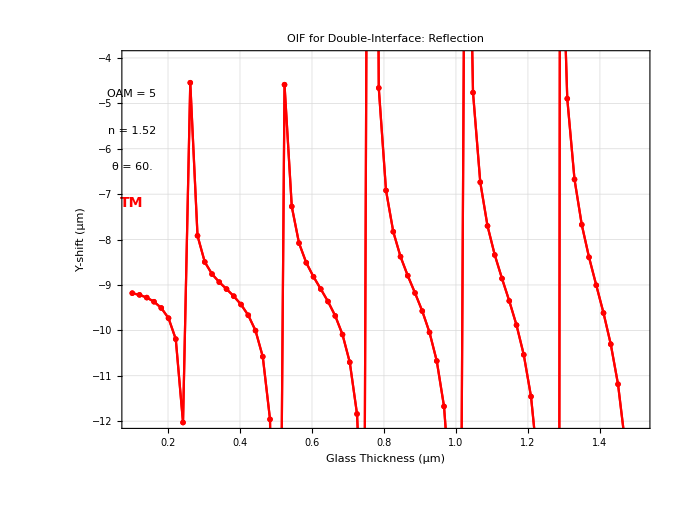

```mathematica
p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmax =-4;
vmin = -12;

p$R1$final$y=Show[p$R1$y,p$RT,p$R1$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{.1,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{.1,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{.1,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Red,Text[font["TM",14],{.1,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

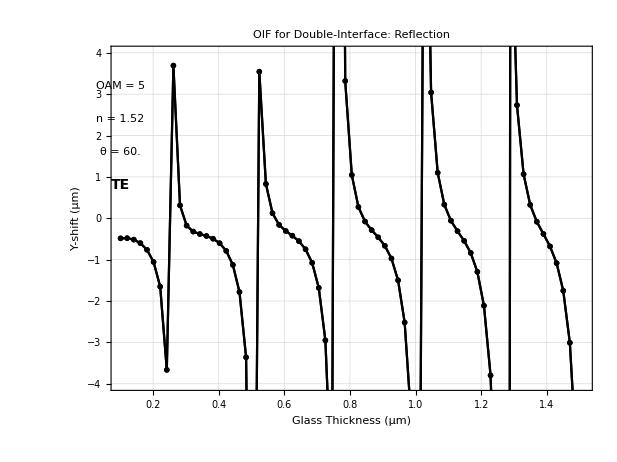

```mathematica
p$R2$y=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmin =-4;
vmax = 4;

p$R2$final$y=Show[p$R2$y,p$RT,p$R2$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{.1,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{.1,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{.1,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{.1,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

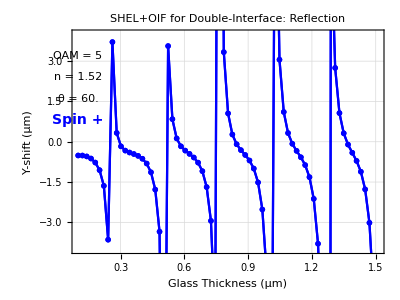

```mathematica
p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =4;
vmin = -4;

p$R3$final$y=Show[p$R3$y,p$RT,p$R3$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{.1,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{.1,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{.1,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin + ",14],{.1,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

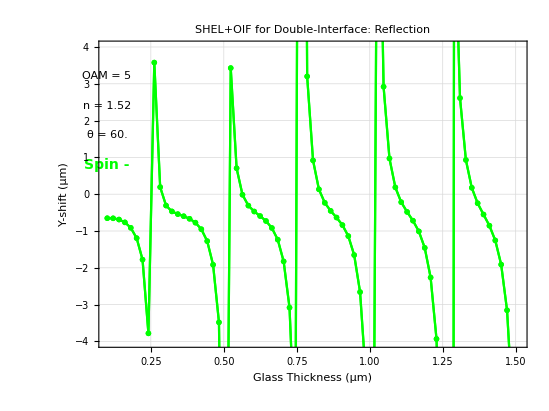

```mathematica
p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =4;
vmin = -4;

p$R4$final$y=Show[p$R4$y,p$RT,p$R4$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{.1,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{.1,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{.1,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin - ",14],{.1,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

#### Plot Graphics For Manuscript

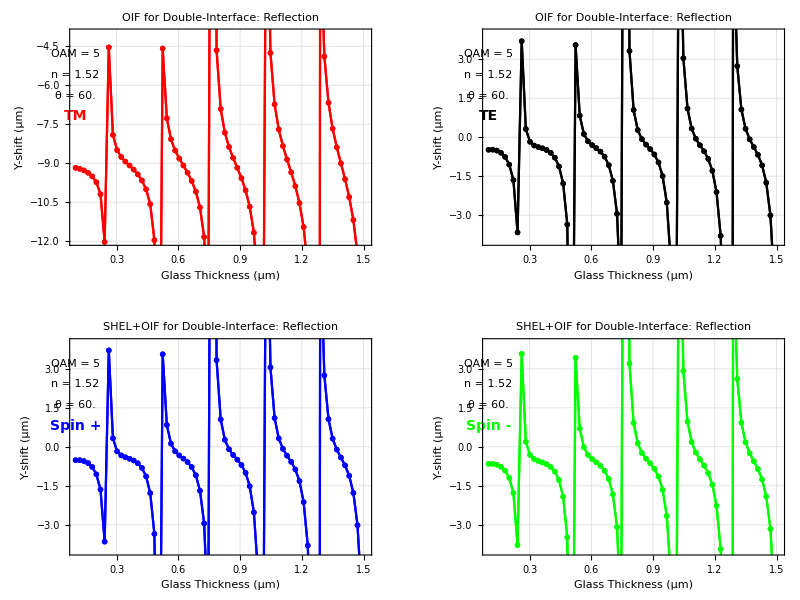

```mathematica
GraphicsGrid[{{p$R1$final$y,p$R2$final$y},{p$R3$final$y,p$R4$final$y}},ImageSize->800]
```

### Centroid Shifts versus Sheet Width: n = 1.5168, L = 10 μm, OAM = 5 (Glass Sheet) FIG 6

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

#### Ramsauer-Townsend Windows

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE /. {κx->0,κy->0};
ErB1$TM$func[n_,θ_,L_]=ErB1$TM /. {κx->0,κy->0};
```

```mathematica
1/1.5168
```

0.659283

```mathematica
10.0*2π/(632.8*10^-9)*10^-6
```

99.2918

```mathematica
Manipulate[ParametricPlot[{{θ,Abs[ErB1$TM$func[n,θ Degree,L]]},{θ,Abs[ErB1$TE$func[n,θ Degree,L]]}},{θ,10 ,80 },AspectRatio->1,PlotStyle->{Red,Blue}],{n,0.5,2},{L,0.1,200.0}]
```

#### Analysis

```mathematica
Clear[plots,k0,β];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1.5168,k0->1,p->0,ℓ->5,θ->θloop Degree, L->99.29180321080256};

Print["θ: ",θloop];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)


βtab = Table[ArcCos[κvec.nvec] /. params$here/.{κx->κtab[[i,j,1]],κy->κtab[[i,j,2]]},{i,1,dimset},{j,1,dimset}];

R1tab = Table[-ErB1$TM /.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];
R2tab = Table[ ErB1$TE/.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];


Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eRtab = Table[{(f[[1]]R1tab[[i,j]]-f[[2]]κtab[[i,j,2]] Cot[θ](R1tab[[i,j]]+R2tab[[i,j]])),f[[2]]R2tab[[i,j]] + f[[1]]κtab[[i,j,2]] Cot[θ](R1tab[[i,j]]+R2tab[[i,j]] ),-(f[[1]]R1tab[[i,j]] κtab[[i,j,1]] + f[[2]]R2tab[[i,j]]  κtab[[i,j,2]])}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,θloop,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,θloop,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,θloop,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,θloop,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{θloop,10.0,80.0,0.5}]
```

θ: 10.

TM (Reflected) = {-1.07377,-1.92251} μm

TE (Reflected) = {-1.07091,-2.12246} μm

spin+ (Reflected) = {-1.07229,-2.02672} μm

spin- (Reflected) = {-1.07229,-2.02588} μm

θ: 10.5

TM (Reflected) = {-1.11573,-1.41278} μm

TE (Reflected) = {-1.11062,-1.62507} μm

spin+ (Reflected) = {-1.11307,-1.52383} μm

spin- (Reflected) = {-1.11307,-1.52288} μm

θ: 11.

TM (Reflected) = {-1.15951,-0.869331} μm

TE (Reflected) = {-1.15191,-1.09706} μm

spin+ (Reflected) = {-1.15553,-0.988921} μm

spin- (Reflected) = {-1.15553,-0.98784} μm

θ: 11.5

TM (Reflected) = {-1.20619,-0.278711} μm

TE (Reflected) = {-1.19597,-0.525716} μm

spin+ (Reflected) = {-1.20082,-0.408952} μm

spin- (Reflected) = {-1.20082,-0.407727} μm

θ: 12.

TM (Reflected) = {-1.25689,0.37842} μm

TE (Reflected) = {-1.24412,0.107627} μm

spin+ (Reflected) = {-1.25016,0.23501} μm

spin- (Reflected) = {-1.25016,0.236402} μm

θ: 12.5

TM (Reflected) = {-1.3127,1.12969} μm

TE (Reflected) = {-1.29773,0.830064} μm

spin+ (Reflected) = {-1.30477,0.970253} μm

spin- (Reflected) = {-1.30477,0.971841} μm

θ: 13.

TM (Reflected) = {-1.37461,2.01492} μm

TE (Reflected) = {-1.35812,1.68117} μm

spin+ (Reflected) = {-1.36584,1.83639} μm

spin- (Reflected) = {-1.36584,1.83821} μm

θ: 13.5

TM (Reflected) = {-1.44337,3.09277} μm

TE (Reflected) = {-1.42648,2.71987} μm

spin+ (Reflected) = {-1.43433,2.89214} μm

spin- (Reflected) = {-1.43433,2.89424} μm

θ: 14.

TM (Reflected) = {-1.51929,4.45306} μm

TE (Reflected) = {-1.50364,4.03708} μm

spin+ (Reflected) = {-1.51086,4.2278} μm

spin- (Reflected) = {-1.51086,4.23023} μm

θ: 14.5

TM (Reflected) = {-1.60203,6.24128} μm

TE (Reflected) = {-1.5898,5.78066} μm

spin+ (Reflected) = {-1.59539,5.99005} μm

spin- (Reflected) = {-1.59539,5.99288} μm

θ: 15.

TM (Reflected) = {-1.69028,8.71395} μm

TE (Reflected) = {-1.68411,8.21113} μm

spin+ (Reflected) = {-1.68691,8.43752} μm

spin- (Reflected) = {-1.68691,8.44082} μm

θ: 15.5

TM (Reflected) = {-1.78155,12.3822} μm

TE (Reflected) = {-1.78425,11.8455} μm

spin+ (Reflected) = {-1.78304,12.0846} μm

spin- (Reflected) = {-1.78304,12.0884} μm

θ: 16.

TM (Reflected) = {-1.87197,18.4693} μm

TE (Reflected) = {-1.88597,17.9144} μm

spin+ (Reflected) = {-1.87975,18.1588} μm

spin- (Reflected) = {-1.87975,18.1632} μm

θ: 16.5

TM (Reflected) = {-1.95652,30.9273} μm

TE (Reflected) = {-1.98302,30.3772} μm

spin+ (Reflected) = {-1.97137,30.6165} μm

spin- (Reflected) = {-1.97137,30.6215} μm

θ: 17.

TM (Reflected) = {-2.02968,74.1887} μm

TE (Reflected) = {-2.06773,73.6714} μm

spin+ (Reflected) = {-2.05118,73.8937} μm

spin- (Reflected) = {-2.05118,73.8993} μm

θ: 17.5

TM (Reflected) = {-2.08673,-251.354} μm

TE (Reflected) = {-2.13264,-251.807} μm

spin+ (Reflected) = {-2.11285,-251.615} μm

spin- (Reflected) = {-2.11285,-251.609} μm

θ: 18.

TM (Reflected) = {-2.12447,-46.6154} μm

TE (Reflected) = {-2.17196,-46.999} μm

spin+ (Reflected) = {-2.15166,-46.8383} μm

spin- (Reflected) = {-2.15166,-46.8317} μm

θ: 18.5

TM (Reflected) = {-2.1434,-24.6198} μm

TE (Reflected) = {-2.18476,-24.9261} μm

spin+ (Reflected) = {-2.1672,-24.7995} μm

spin- (Reflected) = {-2.1672,-24.7926} μm

θ: 19.

TM (Reflected) = {-2.14698,-15.7152} μm

TE (Reflected) = {-2.17476,-15.9596} μm

spin+ (Reflected) = {-2.16303,-15.86} μm

spin- (Reflected) = {-2.16303,-15.8528} μm

θ: 19.5

TM (Reflected) = {-2.14139,-10.6346} μm

TE (Reflected) = {-2.14996,-10.8472} μm

spin+ (Reflected) = {-2.14636,-10.7615} μm

spin- (Reflected) = {-2.14636,-10.7541} μm

θ: 20.

TM (Reflected) = {-2.1342,-7.18744} μm

TE (Reflected) = {-2.12065,-7.40697} μm

spin+ (Reflected) = {-2.12632,-7.31883} μm

spin- (Reflected) = {-2.12632,-7.31135} μm

θ: 20.5

TM (Reflected) = {-2.13306,-4.56267} μm

TE (Reflected) = {-2.09738,-4.83059} μm

spin+ (Reflected) = {-2.11224,-4.72281} μm

spin- (Reflected) = {-2.11224,-4.71518} μm

θ: 21.

TM (Reflected) = {-2.14474,-2.35741} μm

TE (Reflected) = {-2.0896,-2.7138} μm

spin+ (Reflected) = {-2.11243,-2.57022} μm

spin- (Reflected) = {-2.11243,-2.56234} μm

θ: 21.5

TM (Reflected) = {-2.17459,-0.309641} μm

TE (Reflected) = {-2.10516,-0.790669} μm

spin+ (Reflected) = {-2.13366,-0.597385} μm

spin- (Reflected) = {-2.13366,-0.589075} μm

θ: 22.

TM (Reflected) = {-2.22612,1.80585} μm

TE (Reflected) = {-2.15017,1.17027} μm

spin+ (Reflected) = {-2.18099,1.42371} μm

spin- (Reflected) = {-2.18099,1.43269} μm

θ: 22.5

TM (Reflected) = {-2.3006,4.24337} μm

TE (Reflected) = {-2.22875,3.43388} μm

spin+ (Reflected) = {-2.25747,3.75257} μm

spin- (Reflected) = {-2.25747,3.76251} μm

θ: 23.

TM (Reflected) = {-2.39625,7.36962} μm

TE (Reflected) = {-2.34211,6.38585} μm

spin+ (Reflected) = {-2.36336,6.7663} μm

spin- (Reflected) = {-2.36336,6.77753} μm

θ: 23.5

TM (Reflected) = {-2.50731,11.8493} μm

TE (Reflected) = {-2.48641,10.7229} μm

spin+ (Reflected) = {-2.49443,11.1487} μm

spin- (Reflected) = {-2.49443,11.1616} μm

θ: 24.

TM (Reflected) = {-2.62322,19.2457} μm

TE (Reflected) = {-2.64957,18.0542} μm

spin+ (Reflected) = {-2.6397,18.4928} μm

spin- (Reflected) = {-2.6397,18.5075} μm

θ: 24.5

TM (Reflected) = {-2.7292,34.9414} μm

TE (Reflected) = {-2.80866,33.8099} μm

spin+ (Reflected) = {-2.77967,34.2144} μm

spin- (Reflected) = {-2.77967,34.231} μm

θ: 25.

TM (Reflected) = {-2.80933,102.34} μm

TE (Reflected) = {-2.93208,101.416} μm

spin+ (Reflected) = {-2.88831,101.736} μm

spin- (Reflected) = {-2.88831,101.755} μm

θ: 25.5

TM (Reflected) = {-2.85217,-131.576} μm

TE (Reflected) = {-2.99046,-132.189} μm

spin+ (Reflected) = {-2.942,-131.984} μm

spin- (Reflected) = {-2.942,-131.965} μm

θ: 26.

TM (Reflected) = {-2.85566,-38.2517} μm

TE (Reflected) = {-2.97196,-38.5471} μm

spin+ (Reflected) = {-2.93161,-38.4546} μm

spin- (Reflected) = {-2.93161,-38.4346} μm

θ: 26.5

TM (Reflected) = {-2.82925,-20.3069} μm

TE (Reflected) = {-2.89129,-20.3825} μm

spin+ (Reflected) = {-2.86985,-20.3664} μm

spin- (Reflected) = {-2.86985,-20.3464} μm

θ: 27.

TM (Reflected) = {-2.78994,-12.0451} μm

TE (Reflected) = {-2.78164,-12.0639} μm

spin+ (Reflected) = {-2.78451,-12.0672} μm

spin- (Reflected) = {-2.78451,-12.0476} μm

θ: 27.5

TM (Reflected) = {-2.7566,-6.92006} μm

TE (Reflected) = {-2.67944,-7.05188} μm

spin+ (Reflected) = {-2.70604,-7.01608} μm

spin- (Reflected) = {-2.70604,-6.99678} μm

θ: 28.

TM (Reflected) = {-2.74509,-3.10075} μm

TE (Reflected) = {-2.61368,-3.48697} μm

spin+ (Reflected) = {-2.65874,-3.3642} μm

spin- (Reflected) = {-2.65874,-3.34488} μm

θ: 28.5

TM (Reflected) = {-2.76597,0.247211} μm

TE (Reflected) = {-2.60371,-0.496397} μm

spin+ (Reflected) = {-2.65864,-0.254623} μm

spin- (Reflected) = {-2.65864,-0.234654} μm

θ: 29.

TM (Reflected) = {-2.82355,3.71149} μm

TE (Reflected) = {-2.66113,2.54996} μm

spin+ (Reflected) = {-2.71493,2.92402} μm

spin- (Reflected) = {-2.71493,2.94547} μm

θ: 29.5

TM (Reflected) = {-2.91525,7.93993} μm

TE (Reflected) = {-2.79056,6.35865} μm

spin+ (Reflected) = {-2.83056,6.85407} μm

spin- (Reflected) = {-2.83056,6.87794} μm

θ: 30.

TM (Reflected) = {-3.03044,14.0251} μm

TE (Reflected) = {-2.98585,12.118} μm

spin+ (Reflected) = {-2.99958,12.6914} μm

spin- (Reflected) = {-2.99958,12.7185} μm

θ: 30.5

TM (Reflected) = {-3.15009,24.7701} μm

TE (Reflected) = {-3.22065,22.7699} μm

spin+ (Reflected) = {-3.19995,23.3414} μm

spin- (Reflected) = {-3.19995,23.3723} μm

θ: 31.

TM (Reflected) = {-3.24963,53.0251} μm

TE (Reflected) = {-3.43919,51.2942} μm

spin+ (Reflected) = {-3.38611,51.7617} μm

spin- (Reflected) = {-3.38611,51.7961} μm

θ: 31.5

TM (Reflected) = {-3.30688,908.478} μm

TE (Reflected) = {-3.5659,907.554} μm

spin+ (Reflected) = {-3.49592,907.785} μm

spin- (Reflected) = {-3.49592,907.822} μm

θ: 32.

TM (Reflected) = {-3.31344,-59.6023} μm

TE (Reflected) = {-3.54997,-59.9712} μm

spin+ (Reflected) = {-3.48725,-59.8924} μm

spin- (Reflected) = {-3.48725,-59.8544} μm

θ: 32.5

TM (Reflected) = {-3.27835,-25.9394} μm

TE (Reflected) = {-3.40574,-25.7812} μm

spin+ (Reflected) = {-3.37203,-25.8419} μm

spin- (Reflected) = {-3.37203,-25.8043} μm

θ: 33.

TM (Reflected) = {-3.22534,-14.0053} μm

TE (Reflected) = {-3.20482,-13.7274} μm

spin+ (Reflected) = {-3.21028,-13.8196} μm

spin- (Reflected) = {-3.21028,-13.7833} μm

θ: 33.5

TM (Reflected) = {-3.1812,-7.23958} μm

TE (Reflected) = {-3.02455,-7.24104} μm

spin+ (Reflected) = {-3.06645,-7.25827} μm

spin- (Reflected) = {-3.06645,-7.22303} μm

θ: 34.

TM (Reflected) = {-3.1671,-2.31833} μm

TE (Reflected) = {-2.91753,-2.88894} μm

spin+ (Reflected) = {-2.98384,-2.75486} μm

spin- (Reflected) = {-2.98384,-2.71983} μm

θ: 34.5

TM (Reflected) = {-3.19432,2.09651} μm

TE (Reflected) = {-2.91179,0.786001} μm

spin+ (Reflected) = {-2.9851,1.10786} μm

spin- (Reflected) = {-2.9851,1.14419} μm

θ: 35.

TM (Reflected) = {-3.26311,6.96455} μm

TE (Reflected) = {-3.02026,4.86535} μm

spin+ (Reflected) = {-3.08056,5.3669} μm

spin- (Reflected) = {-3.08056,5.40632} μm

θ: 35.5

TM (Reflected) = {-3.36231,13.5431} μm

TE (Reflected) = {-3.2419,10.7802} μm

spin+ (Reflected) = {-3.26994,11.4016} μm

spin- (Reflected) = {-3.26994,11.4457} μm

θ: 36.

TM (Reflected) = {-3.47007,24.7642} μm

TE (Reflected) = {-3.54684,21.732} μm

spin+ (Reflected) = {-3.53031,22.3597} μm

spin- (Reflected) = {-3.53031,22.4096} μm

θ: 36.5

TM (Reflected) = {-3.55844,53.8799} μm

TE (Reflected) = {-3.85051,51.2612} μm

spin+ (Reflected) = {-3.79242,51.7543} μm

spin- (Reflected) = {-3.79242,51.8096} μm

θ: 37.

TM (Reflected) = {-3.60365,1139.34} μm

TE (Reflected) = {-4.01797,1138.22} μm

spin+ (Reflected) = {-3.94025,1138.4} μm

spin- (Reflected) = {-3.94025,1138.46} μm

θ: 37.5

TM (Reflected) = {-3.59885,-58.0103} μm

TE (Reflected) = {-3.9551,-58.244} μm

spin+ (Reflected) = {-3.88989,-58.2312} μm

spin- (Reflected) = {-3.88989,-58.1713} μm

θ: 38.

TM (Reflected) = {-3.55711,-24.7685} μm

TE (Reflected) = {-3.70359,-24.2297} μm

spin+ (Reflected) = {-3.67661,-24.3582} μm

spin- (Reflected) = {-3.67661,-24.2996} μm

θ: 38.5

TM (Reflected) = {-3.50522,-12.6496} μm

TE (Reflected) = {-3.40111,-12.1329} μm

spin+ (Reflected) = {-3.4206,-12.2578} μm

spin- (Reflected) = {-3.4206,-12.2015} μm

θ: 39.

TM (Reflected) = {-3.47013,-5.51434} μm

TE (Reflected) = {-3.16624,-5.67593} μm

spin+ (Reflected) = {-3.2235,-5.6728} μm

spin- (Reflected) = {-3.2235,-5.61817} μm

θ: 39.5

TM (Reflected) = {-3.46966,0.00239237} μm

TE (Reflected) = {-3.06039,-1.23533} μm

spin+ (Reflected) = {-3.13605,-1.03397} μm

spin- (Reflected) = {-3.13605,-0.97905} μm

θ: 40.

TM (Reflected) = {-3.50873,5.39406} μm

TE (Reflected) = {-3.10884,2.91313} μm

spin+ (Reflected) = {-3.17899,3.31944} μm

spin- (Reflected) = {-3.17899,3.37726} μm

θ: 40.5

TM (Reflected) = {-3.57915,12.0023} μm

TE (Reflected) = {-3.31987,8.36515} μm

spin+ (Reflected) = {-3.3615,8.91759} μm

spin- (Reflected) = {-3.3615,8.98086} μm

θ: 41.

TM (Reflected) = {-3.66163,22.3315} μm

TE (Reflected) = {-3.675,18.0174} μm

spin+ (Reflected) = {-3.67309,18.5979} μm

spin- (Reflected) = {-3.67309,18.6682} μm

θ: 41.5

TM (Reflected) = {-3.73122,45.9299} μm

TE (Reflected) = {-4.08408,41.9346} μm

spin+ (Reflected) = {-4.03974,42.398} μm

spin- (Reflected) = {-4.03974,42.4753} μm

θ: 42.

TM (Reflected) = {-3.76711,260.346} μm

TE (Reflected) = {-4.35247,257.899} μm

spin+ (Reflected) = {-4.28597,258.136} μm

spin- (Reflected) = {-4.28597,258.218} μm

θ: 42.5

TM (Reflected) = {-3.76287,-71.4555} μm

TE (Reflected) = {-4.29723,-71.9535} μm

spin+ (Reflected) = {-4.23922,-71.9412} μm

spin- (Reflected) = {-4.23922,-71.8576} μm

θ: 43.

TM (Reflected) = {-3.7295,-27.2338} μm

TE (Reflected) = {-3.95665,-26.5085} μm

spin+ (Reflected) = {-3.93182,-26.6287} μm

spin- (Reflected) = {-3.93182,-26.5468} μm

θ: 43.5

TM (Reflected) = {-3.68877,-13.1984} μm

TE (Reflected) = {-3.54398,-12.5212} μm

spin+ (Reflected) = {-3.5602,-12.6367} μm

spin- (Reflected) = {-3.5602,-12.5575} μm

θ: 44.

TM (Reflected) = {-3.66208,-5.20347} μm

TE (Reflected) = {-3.23231,-5.5705} μm

spin+ (Reflected) = {-3.28077,-5.56771} μm

spin- (Reflected) = {-3.28077,-5.49052} μm

θ: 44.5

TM (Reflected) = {-3.66217,0.962467} μm

TE (Reflected) = {-3.0951,-0.999799} μm

spin+ (Reflected) = {-3.15686,-0.824926} μm

spin- (Reflected) = {-3.15686,-0.74727} μm

θ: 45.

TM (Reflected) = {-3.69004,7.03177} μm

TE (Reflected) = {-3.15608,3.28208} μm

spin+ (Reflected) = {-3.20933,3.61536} μm

spin- (Reflected) = {-3.20933,3.6966} μm

θ: 45.5

TM (Reflected) = {-3.73598,14.5704} μm

TE (Reflected) = {-3.42448,9.22046} μm

spin+ (Reflected) = {-3.45139,9.63888} μm

spin- (Reflected) = {-3.45139,9.72639} μm

θ: 46.

TM (Reflected) = {-3.78354,26.8195} μm

TE (Reflected) = {-3.87786,20.6505} μm

spin+ (Reflected) = {-3.8711,21.0454} μm

spin- (Reflected) = {-3.8711,21.1404} μm

θ: 46.5

TM (Reflected) = {-3.81615,58.8148} μm

TE (Reflected) = {-4.38258,53.3705} μm

spin+ (Reflected) = {-4.34906,53.6419} μm

spin- (Reflected) = {-4.34906,53.7435} μm

θ: 47.

TM (Reflected) = {-3.82438,-2053.52} μm

TE (Reflected) = {-4.64373,-2054.32} μm

spin+ (Reflected) = {-4.60172,-2054.33} μm

spin- (Reflected) = {-4.60172,-2054.23} μm

θ: 47.5

TM (Reflected) = {-3.81016,-52.4177} μm

TE (Reflected) = {-4.43957,-52.9154} μm

spin+ (Reflected) = {-4.40902,-52.9442} μm

spin- (Reflected) = {-4.40902,-52.8382} μm

θ: 48.

TM (Reflected) = {-3.78428,-21.6146} μm

TE (Reflected) = {-3.93095,-21.0518} μm

spin+ (Reflected) = {-3.92378,-21.1313} μm

spin- (Reflected) = {-3.92378,-21.0272} μm

θ: 48.5

TM (Reflected) = {-3.76042,-9.52612} μm

TE (Reflected) = {-3.43011,-9.6596} μm

spin+ (Reflected) = {-3.44642,-9.70392} μm

spin- (Reflected) = {-3.44642,-9.6021} μm

θ: 49.

TM (Reflected) = {-3.74843,-1.85782} μm

TE (Reflected) = {-3.10744,-3.80788} μm

spin+ (Reflected) = {-3.1381,-3.76509} μm

spin- (Reflected) = {-3.1381,-3.66413} μm

θ: 49.5

TM (Reflected) = {-3.75103,4.58181} μm

TE (Reflected) = {-3.00814,0.286152} μm

spin+ (Reflected) = {-3.04023,0.420397} μm

spin- (Reflected) = {-3.04023,0.523} μm

θ: 50.

TM (Reflected) = {-3.76399,11.3713} μm

TE (Reflected) = {-3.14442,4.62782} μm

spin+ (Reflected) = {-3.1667,4.81696} μm

spin- (Reflected) = {-3.1667,4.92374} μm

θ: 50.5

TM (Reflected) = {-3.77906,20.3627} μm

TE (Reflected) = {-3.52737,11.5773} μm

spin+ (Reflected) = {-3.53434,11.7644} μm

spin- (Reflected) = {-3.53434,11.8768} μm

θ: 51.

TM (Reflected) = {-3.78807,36.5912} μm

TE (Reflected) = {-4.11927,27.0234} μm

spin+ (Reflected) = {-4.11257,27.1579} μm

spin- (Reflected) = {-4.11257,27.276} μm

θ: 51.5

TM (Reflected) = {-3.78661,95.3318} μm

TE (Reflected) = {-4.69289,87.2023} μm

spin+ (Reflected) = {-4.6794,87.2623} μm

spin- (Reflected) = {-4.6794,87.3843} μm

θ: 52.

TM (Reflected) = {-3.77539,-151.323} μm

TE (Reflected) = {-4.81749,-156.302} μm

spin+ (Reflected) = {-4.80511,-156.305} μm

spin- (Reflected) = {-4.80511,-156.181} μm

θ: 52.5

TM (Reflected) = {-3.75895,-33.0902} μm

TE (Reflected) = {-4.35636,-35.8559} μm

spin+ (Reflected) = {-4.3501,-35.8889} μm

spin- (Reflected) = {-4.3501,-35.765} μm

θ: 53.

TM (Reflected) = {-3.74246,-12.0251} μm

TE (Reflected) = {-3.68591,-15.1513} μm

spin+ (Reflected) = {-3.68645,-15.1831} μm

spin- (Reflected) = {-3.68645,-15.0599} μm

θ: 53.5

TM (Reflected) = {-3.72911,-1.07619} μm

TE (Reflected) = {-3.15224,-6.76146} μm

spin+ (Reflected) = {-3.15699,-6.776} μm

spin- (Reflected) = {-3.15699,-6.65316} μm

θ: 54.

TM (Reflected) = {-3.71902,7.44712} μm

TE (Reflected) = {-2.86043,-2.23304} μm

spin+ (Reflected) = {-2.8659,-2.23332} μm

spin- (Reflected) = {-2.8659,-2.10961} μm

θ: 54.5

TM (Reflected) = {-3.70998,16.0912} μm

TE (Reflected) = {-2.81621,1.23056} μm

spin+ (Reflected) = {-2.81996,1.22996} μm

spin- (Reflected) = {-2.81996,1.35571} μm

θ: 55.

TM (Reflected) = {-3.69929,27.0092} μm

TE (Reflected) = {-3.02669,5.40458} μm

spin+ (Reflected) = {-3.02821,5.38904} μm

spin- (Reflected) = {-3.02821,5.51743} μm

θ: 55.5

TM (Reflected) = {-3.68548,44.4712} μm

TE (Reflected) = {-3.51507,12.9061} μm

spin+ (Reflected) = {-3.51522,12.8695} μm

spin- (Reflected) = {-3.51522,13.0004} μm

θ: 56.

TM (Reflected) = {-3.66886,84.7188} μm

TE (Reflected) = {-4.24101,31.4311} μm

spin+ (Reflected) = {-4.24088,31.3769} μm

spin- (Reflected) = {-4.24088,31.5094} μm

θ: 56.5

TM (Reflected) = {-3.65224,403.252} μm

TE (Reflected) = {-4.88669,126.284} μm

spin+ (Reflected) = {-4.88668,126.219} μm

spin- (Reflected) = {-4.88668,126.352} μm

θ: 57.

TM (Reflected) = {-3.6326,-176.908} μm

TE (Reflected) = {-4.88646,-101.542} μm

spin+ (Reflected) = {-4.88636,-101.615} μm

spin- (Reflected) = {-4.88636,-101.481} μm

θ: 57.5

TM (Reflected) = {-3.61387,-67.2145} μm

TE (Reflected) = {-4.2116,-29.2304} μm

spin+ (Reflected) = {-4.21129,-29.3169} μm

spin- (Reflected) = {-4.21129,-29.1822} μm

θ: 58.

TM (Reflected) = {-3.5934,-39.0168} μm

TE (Reflected) = {-3.41837,-12.4466} μm

spin+ (Reflected) = {-3.41863,-12.5545} μm

spin- (Reflected) = {-3.41863,-12.4183} μm

θ: 58.5

TM (Reflected) = {-3.56948,-24.9421} μm

TE (Reflected) = {-2.84521,-5.55943} μm

spin+ (Reflected) = {-2.84759,-5.69218} μm

spin- (Reflected) = {-2.84759,-5.55404} μm

θ: 59.

TM (Reflected) = {-3.54172,-15.6271} μm

TE (Reflected) = {-2.53866,-1.91761} μm

spin+ (Reflected) = {-2.54445,-2.06688} μm

spin- (Reflected) = {-2.54445,-1.92683} μm

θ: 59.5

TM (Reflected) = {-3.51185,-8.13289} μm

TE (Reflected) = {-2.47335,0.781232} μm

spin+ (Reflected) = {-2.48217,0.634933} μm

spin- (Reflected) = {-2.48217,0.776045} μm

θ: 60.

TM (Reflected) = {-3.48327,-0.881484} μm

TE (Reflected) = {-2.64771,3.91773} μm

spin+ (Reflected) = {-2.65666,3.79591} μm

spin- (Reflected) = {-2.65666,3.93667} μm

θ: 60.5

TM (Reflected) = {-3.45932,7.8609} μm

TE (Reflected) = {-3.09989,9.3783} μm

spin+ (Reflected) = {-3.10417,9.29076} μm

spin- (Reflected) = {-3.10417,9.42973} μm

θ: 61.

TM (Reflected) = {-3.44115,22.2825} μm

TE (Reflected) = {-3.86039,22.1528} μm

spin+ (Reflected) = {-3.85531,22.0862} μm

spin- (Reflected) = {-3.85531,22.2226} μm

θ: 61.5

TM (Reflected) = {-3.4263,66.2415} μm

TE (Reflected) = {-4.73722,67.6743} μm

spin+ (Reflected) = {-4.72118,67.5897} μm

spin- (Reflected) = {-4.72118,67.7237} μm

θ: 62.

TM (Reflected) = {-3.40864,-271.639} μm

TE (Reflected) = {-5.06528,-265.327} μm

spin+ (Reflected) = {-5.04224,-265.481} μm

spin- (Reflected) = {-5.04224,-265.348} μm

θ: 62.5

TM (Reflected) = {-3.38078,-50.9768} μm

TE (Reflected) = {-4.44955,-40.1969} μm

spin+ (Reflected) = {-4.42948,-40.4661} μm

spin- (Reflected) = {-4.42948,-40.3324} μm

θ: 63.

TM (Reflected) = {-3.33709,-27.3355} μm

TE (Reflected) = {-3.49003,-15.7264} μm

spin+ (Reflected) = {-3.48581,-16.1154} μm

spin- (Reflected) = {-3.48581,-15.9792} μm

θ: 63.5

TM (Reflected) = {-3.27745,-17.0686} μm

TE (Reflected) = {-2.73093,-7.10763} μm

spin+ (Reflected) = {-2.75266,-7.57361} μm

spin- (Reflected) = {-2.75266,-7.43392} μm

θ: 64.

TM (Reflected) = {-3.20809,-10.63} μm

TE (Reflected) = {-2.26234,-3.22704} μm

spin+ (Reflected) = {-2.31244,-3.69053} μm

spin- (Reflected) = {-2.31244,-3.54789} μm

θ: 64.5

TM (Reflected) = {-3.13994,-5.70076} μm

TE (Reflected) = {-2.02921,-1.03202} μm

spin+ (Reflected) = {-2.10079,-1.40487} μm

spin- (Reflected) = {-2.10079,-1.26092} μm

θ: 65.

TM (Reflected) = {-3.08492,-1.28191} μm

TE (Reflected) = {-1.98773,0.696255} μm

spin+ (Reflected) = {-2.0664,0.482931} μm

spin- (Reflected) = {-2.0664,0.625928} μm

θ: 65.5

TM (Reflected) = {-3.05221,3.38309} μm

TE (Reflected) = {-2.13589,2.756} μm

spin+ (Reflected) = {-2.20301,2.73205} μm

spin- (Reflected) = {-2.20301,2.87181} μm

θ: 66.

TM (Reflected) = {-3.04524,9.32202} μm

TE (Reflected) = {-2.51832,6.28071} μm

spin+ (Reflected) = {-2.55468,6.42319} μm

spin- (Reflected) = {-2.55468,6.55793} μm

θ: 66.5

TM (Reflected) = {-3.05961,18.8498} μm

TE (Reflected) = {-3.2154,14.1115} μm

spin+ (Reflected) = {-3.20595,14.3345} μm

spin- (Reflected) = {-3.20595,14.4634} μm

θ: 67.

TM (Reflected) = {-3.08223,41.0126} μm

TE (Reflected) = {-4.22261,36.8188} μm

spin+ (Reflected) = {-4.16334,36.9751} μm

spin- (Reflected) = {-4.16334,37.0985} μm

θ: 67.5

TM (Reflected) = {-3.09302,225.285} μm

TE (Reflected) = {-5.05019,225.796} μm

spin+ (Reflected) = {-4.95554,225.711} μm

spin- (Reflected) = {-4.95554,225.831} μm

θ: 68.

TM (Reflected) = {-3.07069,-79.4115} μm

TE (Reflected) = {-4.81866,-72.2676} μm

spin+ (Reflected) = {-4.7225,-72.72} μm

spin- (Reflected) = {-4.7225,-72.6012} μm

θ: 68.5

TM (Reflected) = {-3.00189,-33.2911} μm

TE (Reflected) = {-3.76447,-22.9762} μm

spin+ (Reflected) = {-3.70816,-23.798} μm

spin- (Reflected) = {-3.70816,-23.6777} μm

θ: 69.

TM (Reflected) = {-2.8879,-19.5814} μm

TE (Reflected) = {-2.76283,-9.79889} μm

spin+ (Reflected) = {-2.77559,-10.8581} μm

spin- (Reflected) = {-2.77559,-10.735} μm

θ: 69.5

TM (Reflected) = {-2.74427,-12.4985} μm

TE (Reflected) = {-2.08688,-4.70519} μm

spin+ (Reflected) = {-2.17462,-5.80837} μm

spin- (Reflected) = {-2.17462,-5.68249} μm

θ: 70.

TM (Reflected) = {-2.59354,-7.97586} μm

TE (Reflected) = {-1.6754,-2.36995} μm

spin+ (Reflected) = {-1.82459,-3.34457} μm

spin- (Reflected) = {-1.82459,-3.21718} μm

θ: 70.5

TM (Reflected) = {-2.45718,-4.71288} μm

TE (Reflected) = {-1.44045,-1.1041} μm

spin+ (Reflected) = {-1.62873,-1.83602} μm

spin- (Reflected) = {-1.62873,-1.70878} μm

θ: 71.

TM (Reflected) = {-2.35134,-2.08686} μm

TE (Reflected) = {-1.32829,-0.254991} μm

spin+ (Reflected) = {-1.53257,-0.683487} μm

spin- (Reflected) = {-1.53257,-0.558064} μm

θ: 71.5

TM (Reflected) = {-2.28633,0.317721} μm

TE (Reflected) = {-1.31618,0.501284} μm

spin+ (Reflected) = {-1.51531,0.402532} μm

spin- (Reflected) = {-1.51531,0.524681} μm

θ: 72.

TM (Reflected) = {-2.26771,2.88323} μm

TE (Reflected) = {-1.40652,1.42315} μm

spin+ (Reflected) = {-1.58024,1.65884} μm

spin- (Reflected) = {-1.58024,1.77651} μm

θ: 72.5

TM (Reflected) = {-2.29689,6.09761} μm

TE (Reflected) = {-1.62862,2.89104} μm

spin+ (Reflected) = {-1.75501,3.44137} μm

spin- (Reflected) = {-1.75501,3.55362} μm

θ: 73.

TM (Reflected) = {-2.36991,10.8094} μm

TE (Reflected) = {-2.04881,5.75575} μm

spin+ (Reflected) = {-2.10283,6.55294} μm

spin- (Reflected) = {-2.10283,6.65914} μm

θ: 73.5

TM (Reflected) = {-2.47418,19.0389} μm

TE (Reflected) = {-2.77724,12.4398} μm

spin+ (Reflected) = {-2.73429,13.325} μm

spin- (Reflected) = {-2.73429,13.4249} μm

θ: 74.

TM (Reflected) = {-2.5844,38.3062} μm

TE (Reflected) = {-3.88224,31.9643} μm

spin+ (Reflected) = {-3.732,32.6513} μm

spin- (Reflected) = {-3.732,32.7455} μm

θ: 74.5

TM (Reflected) = {-2.6624,158.278} μm

TE (Reflected) = {-4.94568,156.624} μm

spin+ (Reflected) = {-4.71512,156.746} μm

spin- (Reflected) = {-4.71512,156.836} μm

θ: 75.

TM (Reflected) = {-2.66748,-91.5962} μm

TE (Reflected) = {-4.86213,-85.5846} μm

spin+ (Reflected) = {-4.62477,-86.2786} μm

spin- (Reflected) = {-4.62477,-86.191} μm

θ: 75.5

TM (Reflected) = {-2.57628,-34.707} μm

TE (Reflected) = {-3.70105,-24.6743} μm

spin+ (Reflected) = {-3.54383,-26.1203} μm

spin- (Reflected) = {-3.54383,-26.033} μm

θ: 76.

TM (Reflected) = {-2.39722,-19.7927} μm

TE (Reflected) = {-2.55794,-10.1224} μm

spin+ (Reflected) = {-2.52788,-11.9753} μm

spin- (Reflected) = {-2.52788,-11.8876} μm

θ: 76.5

TM (Reflected) = {-2.16372,-12.6044} μm

TE (Reflected) = {-1.78781,-4.8485} μm

spin+ (Reflected) = {-1.87704,-6.73337} μm

spin- (Reflected) = {-1.87704,-6.64546} μm

θ: 77.

TM (Reflected) = {-1.91404,-8.41243} μm

TE (Reflected) = {-1.30604,-2.60166} μm

spin+ (Reflected) = {-1.47755,-4.28441} μm

spin- (Reflected) = {-1.47755,-4.19716} μm

θ: 77.5

TM (Reflected) = {-1.67609,-5.76978} μm

TE (Reflected) = {-0.999418,-1.52002} μm

spin+ (Reflected) = {-1.21476,-2.9153} μm

spin- (Reflected) = {-1.21476,-2.82959} μm

θ: 78.

TM (Reflected) = {-1.46417,-4.03391} μm

TE (Reflected) = {-0.796311,-0.944793} μm

spin+ (Reflected) = {-1.02743,-2.05555} μm

spin- (Reflected) = {-1.02743,-1.97209} μm

θ: 78.5

TM (Reflected) = {-1.28248,-2.85881} μm

TE (Reflected) = {-0.656078,-0.612631} μm

spin+ (Reflected) = {-0.885958,-1.47728} μm

spin- (Reflected) = {-0.885958,-1.3966} μm

θ: 79.

TM (Reflected) = {-1.12974,-2.04075} μm

TE (Reflected) = {-0.555621,-0.406926} μm

spin+ (Reflected) = {-0.77524,-1.07069} μm

spin- (Reflected) = {-0.77524,-0.993137} μm

θ: 79.5

TM (Reflected) = {-1.00242,-1.45467} μm

TE (Reflected) = {-0.481403,-0.271395} μm

spin+ (Reflected) = {-0.686671,-0.774669} μm

spin- (Reflected) = {-0.686671,-0.700485} μm

θ: 80.

TM (Reflected) = {-0.896461,-1.02189} μm

TE (Reflected) = {-0.425177,-0.176831} μm

spin+ (Reflected) = {-0.614771,-0.55213} μm

spin- (Reflected) = {-0.614771,-0.481458} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->60.0 Degree,k0->1,p->0,ℓ->5,L->Lloop}
```

{wk→20000.,n→1.5168,θ→1.0472,k0→1,p→0,ℓ→5,L→Lloop}

```mathematica
{shift$tab$R1,shift$tab$R2,shift$tab$R3,shift$tab$R4}
```

{shift$tab$R1,shift$tab$R2,shift$tab$R3,shift$tab$R4}

```mathematica
shift$all={{{5,10.,{-1.073774933791051,-1.9225064312873652}},{5,10.5,{-1.1157291516938694,-1.412780561229097}},{5,11.,{-1.1595080752566003,-0.8693314105866802}},{5,11.5,{-1.206187498414713,-0.27871078212974687}},{5,12.,{-1.2568853569235485,0.37842012835739314}},{5,12.5,{-1.3126985905214625,1.129690745403601}},{5,13.,{-1.3746125519320094,2.0149164550871483}},{5,13.5,{-1.4433706072633499,3.0927732236758634}},{5,14.,{-1.5192912983357068,4.45305629361007}},{5,14.5,{-1.602027539983707,6.241282123357463}},{5,15.,{-1.6902837201070917,8.71395117850665}},{5,15.5,{-1.7815491039143494,12.382196025139486}},{5,16.,{-1.871967925923756,18.469255339551633}},{5,16.5,{-1.9565218472688113,30.927251358847403}},{5,17.,{-2.029683785584362,74.18868079508916}},{5,17.5,{-2.08672653112666,-251.35362603248845}},{5,18.,{-2.124474417909714,-46.615353914579956}},{5,18.5,{-2.143399445560898,-24.619816582215133}},{5,19.,{-2.146979234214346,-15.715189648900537}},{5,19.5,{-2.141391329127343,-10.634581534148282}},{5,20.,{-2.1341999757699424,-7.187440175773015}},{5,20.5,{-2.1330567137687684,-4.562665145327719}},{5,21.,{-2.1447401718243224,-2.3574061037910257}},{5,21.5,{-2.174587392557433,-0.3096414354326885}},{5,22.,{-2.2261217541833287,1.8058511183086232}},{5,22.5,{-2.300597610074586,4.243370844579343}},{5,23.,{-2.396253860509124,7.369621168625227}},{5,23.5,{-2.5073117494508117,11.849267214158765}},{5,24.,{-2.6232156307136325,19.245727550935925}},{5,24.5,{-2.7291953026616027,34.941360524243315}},{5,25.,{-2.809331062711869,102.34046878444028}},{5,25.5,{-2.8521655598060116,-131.5764678497811}},{5,26.,{-2.85565796512635,-38.25165980268389}},{5,26.5,{-2.829247577278349,-20.306948752827857}},{5,27.,{-2.7899448713646127,-12.045087465139193}},{5,27.5,{-2.7565981175598457,-6.920058723619208}},{5,28.,{-2.745093363523378,-3.1007529538387373}},{5,28.5,{-2.7659684343826747,0.24721094299630814}},{5,29.,{-2.8235523971945327,3.7114932374856138}},{5,29.5,{-2.915247887395263,7.939925290456045}},{5,30.,{-3.0304377631110055,14.025062126347526}},{5,30.5,{-3.1500897370364553,24.77009061303724}},{5,31.,{-3.249632750916882,53.02505090022565}},{5,31.5,{-3.306882345085152,908.4775996443115}},{5,32.,{-3.3134379303177863,-59.60230723904148}},{5,32.5,{-3.2783508875563587,-25.93940883417451}},{5,33.,{-3.2253356643035382,-14.005332522285869}},{5,33.5,{-3.1812031955919178,-7.239577947109212}},{5,34.,{-3.167104130702851,-2.318332544645418}},{5,34.5,{-3.1943243292297154,2.0965136160929037}},{5,35.,{-3.263111399751256,6.964549811199426}},{5,35.5,{-3.362309405202817,13.543083479476635}},{5,36.,{-3.4700694053887537,24.7641797756124}},{5,36.5,{-3.558436719041597,53.87990263360808}},{5,37.,{-3.6036485260110007,1139.336313178444}},{5,37.5,{-3.59884645909204,-58.010286397071894}},{5,38.,{-3.557106456838095,-24.768508179343907}},{5,38.5,{-3.505220288756787,-12.649593048099787}},{5,39.,{-3.4701339919650938,-5.514341337568454}},{5,39.5,{-3.469658716232012,0.0023923744244184067}},{5,40.,{-3.5087253757515326,5.394060426932317}},{5,40.5,{-3.5791500032958306,12.002297088156299}},{5,41.,{-3.661629869745117,22.331523243878433}},{5,41.5,{-3.731218048209547,45.929902304279096}},{5,42.,{-3.7671050774145516,260.34648448433404}},{5,42.5,{-3.7628667139697907,-71.455483683369}},{5,43.,{-3.729497119292288,-27.2338392783406}},{5,43.5,{-3.688773560411954,-13.198403158479863}},{5,44.,{-3.662082254169223,-5.203470412375313}},{5,44.5,{-3.662165917872581,0.9624671092192258}},{5,45.,{-3.6900417175250153,7.031774048031328}},{5,45.5,{-3.7359821606901455,14.570394995517901}},{5,46.,{-3.7835378474218087,26.819476317899163}},{5,46.5,{-3.816149704553861,58.81484048514599}},{5,47.,{-3.824375133399306,-2053.518782039901}},{5,47.5,{-3.8101587237378065,-52.41769172944684}},{5,48.,{-3.7842819658428772,-21.614563916618344}},{5,48.5,{-3.7604217347361324,-9.526118514166805}},{5,49.,{-3.7484325859341214,-1.8578177847755601}},{5,49.5,{-3.751025513305204,4.581814039897101}},{5,50.,{-3.763987151328279,11.37132014444494}},{5,50.5,{-3.7790559865644133,20.3626542363379}},{5,51.,{-3.788069300871323,36.59119504982142}},{5,51.5,{-3.786611697467,95.33182377551933}},{5,52.,{-3.775388311434858,-151.323341147453}},{5,52.5,{-3.758948547758822,-33.090220107272266}},{5,53.,{-3.7424590253201453,-12.02505805949773}},{5,53.5,{-3.7291141609019207,-1.0761925303199131}},{5,54.,{-3.7190211502628245,7.4471241291725825}},{5,54.5,{-3.7099777599902604,16.091219052424876}},{5,55.,{-3.6992924067315833,27.00922438058216}},{5,55.5,{-3.685475705782245,44.47118370393598}},{5,56.,{-3.668859515858703,84.71883214410165}},{5,56.5,{-3.6522396085438396,403.252164976171}},{5,57.,{-3.632595007001502,-176.90774386586034}},{5,57.5,{-3.613872709980392,-67.21448736083467}},{5,58.,{-3.5934039392830415,-39.0168280240549}},{5,58.5,{-3.5694801538254075,-24.942090334412548}},{5,59.,{-3.541717760361689,-15.62711099436867}},{5,59.5,{-3.5118536899170496,-8.13289489656426}},{5,60.,{-3.483273911287446,-0.8814836131398762}},{5,60.5,{-3.4593177795005796,7.860896576055229}},{5,61.,{-3.441153378698679,22.28253225340742}},{5,61.5,{-3.4262976785278605,66.24148254097423}},{5,62.,{-3.4086437299883903,-271.6387035596362}},{5,62.5,{-3.380777171789365,-50.976796780356345}},{5,63.,{-3.3370940517726266,-27.335463392383964}},{5,63.5,{-3.2774452680417085,-17.068556055179652}},{5,64.,{-3.2080933666671982,-10.629980181257086}},{5,64.5,{-3.139943641665256,-5.700755265574946}},{5,65.,{-3.084923920026267,-1.281905118867505}},{5,65.5,{-3.05221154365712,3.3830941126742893}},{5,66.,{-3.0452402458468795,9.32201506392185}},{5,66.5,{-3.059610983406503,18.84984614838707}},{5,67.,{-3.0822297667668677,41.0126311571095}},{5,67.5,{-3.093021829901752,225.28458713787427}},{5,68.,{-3.070692683438426,-79.41152529125745}},{5,68.5,{-3.0018896231346583,-33.29111535567967}},{5,69.,{-2.887900863657218,-19.58140925071576}},{5,69.5,{-2.7442726277023257,-12.498523746393536}},{5,70.,{-2.5935360773767284,-7.9758611612455335}},{5,70.5,{-2.457178672990298,-4.712882293757781}},{5,71.,{-2.3513419941311935,-2.0868612254102863}},{5,71.5,{-2.286332561008651,0.3177214469579467}},{5,72.,{-2.267713745652429,2.883228221522548}},{5,72.5,{-2.296886526677474,6.097611424725777}},{5,73.,{-2.3699067850039346,10.80938333587859}},{5,73.5,{-2.474180205186537,19.038923923071753}},{5,74.,{-2.584403538061843,38.306221798128476}},{5,74.5,{-2.6623961927293545,158.2783725634052}},{5,75.,{-2.667477877234598,-91.59624313334362}},{5,75.5,{-2.576278439898669,-34.70700136457696}},{5,76.,{-2.397221885579097,-19.792726349901248}},{5,76.5,{-2.1637240229185473,-12.60439594220657}},{5,77.,{-1.914040740906226,-8.412432445281024}},{5,77.5,{-1.6760942616257053,-5.7697822559996474}},{5,78.,{-1.4641705830841734,-4.033912115978665}},{5,78.5,{-1.2824792942847942,-2.858805085877978}},{5,79.,{-1.1297410135436403,-2.0407451002384693}},{5,79.5,{-1.0024182626536322,-1.4546698638727333}},{5,80.,{-0.8964609179645848,-1.021893601795184}}},{{5,10.,{-1.070914071836194,-2.1224647443817704}},{5,10.5,{-1.110624249286391,-1.6250735916828858}},{5,11.,{-1.1519063372433838,-1.0970622864189308}},{5,11.5,{-1.1959687137392576,-0.525716152674348}},{5,12.,{-1.2441219501599625,0.10762672498116334}},{5,12.5,{-1.2977276875268862,0.8300637640196142}},{5,13.,{-1.3581196669246791,1.6811657930124488}},{5,13.5,{-1.4264789515090721,2.7198745290652067}},{5,14.,{-1.5036391480860334,4.037084969723505}},{5,14.5,{-1.5897964684445731,5.780662496852732}},{5,15.,{-1.6841138462591367,8.211126525841864}},{5,15.5,{-1.784254381330126,11.845499918049523}},{5,16.,{-1.8859728239943743,17.914368261253227}},{5,16.5,{-1.9830242506550215,30.37718299200532}},{5,17.,{-2.0677322525201807,73.67135248068705}},{5,17.5,{-2.132638681908438,-251.80701619585835}},{5,18.,{-2.1719596595837727,-46.99896096093956}},{5,18.5,{-2.184756111564869,-24.92607053586772}},{5,19.,{-2.174755610819281,-15.95957438820892}},{5,19.5,{-2.1499601023606822,-10.847176819043352}},{5,20.,{-2.1206531794633716,-7.406968620923782}},{5,20.5,{-2.0973797529911993,-4.830593170988159}},{5,21.,{-2.08960354007482,-2.7138002166177686}},{5,21.5,{-2.105163935045296,-0.7906691400052164}},{5,22.,{-2.1501665938797574,1.170265197664438}},{5,22.5,{-2.228745122676152,3.4338782253913744}},{5,23.,{-2.3421090284311292,6.385854200399966}},{5,23.5,{-2.4864148460714577,10.722907820433234}},{5,24.,{-2.649567919076142,18.054205753084876}},{5,24.5,{-2.808657215884379,33.8098549272303}},{5,25.,{-2.932084650973813,101.41583483776074}},{5,25.5,{-2.99046386905233,-132.18939248655806}},{5,26.,{-2.9719603231976053,-38.54710030307777}},{5,26.5,{-2.891287014464454,-20.38247386727862}},{5,27.,{-2.7816397859321285,-12.063943061713013}},{5,27.5,{-2.679437095276947,-7.051880277975855}},{5,28.,{-2.6136759073946534,-3.486967243921876}},{5,28.5,{-2.603708355196162,-0.4963965129518337}},{5,29.,{-2.6611269882256203,2.549963353232247}},{5,29.5,{-2.7905572899548554,6.358645965263321}},{5,30.,{-2.985854957812564,12.117965015825297}},{5,30.5,{-3.220650707751581,22.769917284095804}},{5,31.,{-3.439191888885747,51.29420802590778}},{5,31.5,{-3.5659012421385206,907.5544940614263}},{5,32.,{-3.549969722596566,-59.97120568709225}},{5,32.5,{-3.4057444611002343,-25.781184399155133}},{5,33.,{-3.2048194669042136,-13.727449045391875}},{5,33.5,{-3.0245505220090454,-7.241040140257161}},{5,34.,{-2.9175304272953313,-2.8889432798509374}},{5,34.5,{-2.9117931638312733,0.7860011921849279}},{5,35.,{-3.020259809062032,4.865353815491741}},{5,35.5,{-3.2419025562490096,10.780247054999283}},{5,36.,{-3.5468363159050935,21.731999970659263}},{5,36.5,{-3.8505067608309305,51.26117385865133}},{5,37.,{-4.017971410096773,1138.2193860566224}},{5,37.5,{-3.9551011508206018,-58.24404947216759}},{5,38.,{-3.7035890674394487,-24.229657978337343}},{5,38.5,{-3.4011082515862814,-12.132913452595083}},{5,39.,{-3.166237736659881,-5.67593081320097}},{5,39.5,{-3.0603930561628854,-1.2353253156070745}},{5,40.,{-3.1088409551112997,2.9131344103093038}},{5,40.5,{-3.3198655384407854,8.365145399704208}},{5,41.,{-3.6749972316173802,18.017433494059603}},{5,41.5,{-4.084080869804397,41.93460987017221}},{5,42.,{-4.352465216543374,257.8991192740398}},{5,42.5,{-4.2972337059428085,-71.95346497629545}},{5,43.,{-3.9566457959655765,-26.508483216565452}},{5,43.5,{-3.5439815837452673,-12.521238221166564}},{5,44.,{-3.232308423585408,-5.570503700831417}},{5,44.5,{-3.0950992928103145,-0.9997985206982002}},{5,45.,{-3.156081736114966,3.282080297742666}},{5,45.5,{-3.424476922632366,9.220455113317097}},{5,46.,{-3.8778633093641357,20.650472250743686}},{5,46.5,{-4.382579123749381,53.37047804946645}},{5,47.,{-4.643727344233934,-2054.320339919202}},{5,47.5,{-4.439571112017436,-52.91536874756845}},{5,48.,{-3.9309473979955,-21.051778533241336}},{5,48.5,{-3.4301110560597188,-9.659600162404633}},{5,49.,{-3.1074422003566875,-3.807882606586602}},{5,49.5,{-3.008143375460769,0.2861517300286168}},{5,50.,{-3.144418043838612,4.627815462090625}},{5,50.5,{-3.527365821774079,11.577328815274631}},{5,51.,{-4.1192697340368625,27.0233730665561}},{5,51.5,{-4.692891228274554,87.20229248408756}},{5,52.,{-4.817487590106291,-156.30218906448292}},{5,52.5,{-4.356358888981262,-35.85592207694693}},{5,53.,{-3.685907764115449,-15.151304219931829}},{5,53.5,{-3.1522371747834406,-6.761464046943068}},{5,54.,{-2.860434683323577,-2.2330443047036694}},{5,54.5,{-2.816209954117353,1.23056090810596}},{5,55.,{-3.026692269460448,5.404582619733671}},{5,55.5,{-3.515065610920639,12.90608835354582}},{5,56.,{-4.241014597622078,31.431059198397126}},{5,56.5,{-4.886685020454819,126.2840683699686}},{5,57.,{-4.886462749394208,-101.54175079943177}},{5,57.5,{-4.211595162545596,-29.230449295358113}},{5,58.,{-3.4183704043157572,-12.446569207850022}},{5,58.5,{-2.8452094644345167,-5.559430758837861}},{5,59.,{-2.53865706903414,-1.9176100490120815}},{5,59.5,{-2.473349829185261,0.7812323614656529}},{5,60.,{-2.647705015521394,3.9177288115638413}},{5,60.5,{-3.0998898119943563,9.378300857796606}},{5,61.,{-3.860388575646647,22.152810697787285}},{5,61.5,{-4.737223864321736,67.67425089363034}},{5,62.,{-5.065279104287367,-265.3266475642683}},{5,62.5,{-4.449547758929076,-40.19687543424712}},{5,63.,{-3.490032472627513,-15.726422804100295}},{5,63.5,{-2.7309265300751004,-7.10762664918376}},{5,64.,{-2.262343865621703,-3.2270400464530264}},{5,64.5,{-2.029208865721602,-1.0320181699201123}},{5,65.,{-1.9877317970034187,0.6962548020231757}},{5,65.5,{-2.1358946498191673,2.756002152908358}},{5,66.,{-2.5183244213628755,6.280706942850222}},{5,66.5,{-3.2154015601827384,14.111542259061755}},{5,67.,{-4.222608345890291,36.81884612690629}},{5,67.5,{-5.050193294451329,225.7956218536491}},{5,68.,{-4.818660582627813,-72.26762248379615}},{5,68.5,{-3.7644710254040508,-22.976151365862446}},{5,69.,{-2.762833192235713,-9.79888539846608}},{5,69.5,{-2.0868766166385764,-4.705191991121439}},{5,70.,{-1.6753979728755644,-2.3699454660619184}},{5,70.5,{-1.4404492830483249,-1.104096645438437}},{5,71.,{-1.3282946660344679,-0.2549912355804789}},{5,71.5,{-1.3161799004701473,0.5012839822905281}},{5,72.,{-1.4065184107938857,1.423149867040169}},{5,72.5,{-1.6286232952394875,2.891036586104885}},{5,73.,{-2.0488072651836395,5.755747457322338}},{5,73.5,{-2.7772409966532003,12.439776479392389}},{5,74.,{-3.8822355295475233,31.964253778077193}},{5,74.5,{-4.945684622877889,156.62358521848716}},{5,75.,{-4.862127288920227,-85.58463844904621}},{5,75.5,{-3.7010512566538742,-24.674268744835672}},{5,76.,{-2.55794342795307,-10.12242123043292}},{5,76.5,{-1.7878091306632693,-4.848497982331572}},{5,77.,{-1.3060393604761584,-2.601658496551183}},{5,77.5,{-0.999418188587533,-1.5200205450618303}},{5,78.,{-0.7963112786485133,-0.9447933356079186}},{5,78.5,{-0.6560777259901912,-0.6126314066613863}},{5,79.,{-0.555621390569098,-0.40692565145715914}},{5,79.5,{-0.48140290699700905,-0.2713950335746212}},{5,80.,{-0.42517721816674947,-0.1768314927492107}}},{{5,10.,{-1.0722898656443247,-2.026724798201691}},{5,10.5,{-1.113070158556297,-1.5238347182096288}},{5,11.,{-1.1555341808591724,-0.9889206145735806}},{5,11.5,{-1.2008246783297636,-0.4089516818870521}},{5,12.,{-1.2501587494260258,0.2350098107411912}},{5,12.5,{-1.3047719422912225,0.9702528724007797}},{5,13.,{-1.3658352609537523,1.836387652849196}},{5,13.5,{-1.434329929847927,2.8921410141535615}},{5,14.,{-1.510861119521381,4.227797921750678}},{5,14.5,{-1.5953940222018046,5.990049213208443}},{5,15.,{-1.6869120464128033,8.437523915799128}},{5,15.5,{-1.7830394984314224,12.084609701484982}},{5,16.,{-1.879748866324502,18.158769831718782}},{5,16.5,{-1.9713712772131624,30.616545738687986}},{5,17.,{-2.0511756865675714,73.89366692407964}},{5,17.5,{-2.1128514104412877,-251.61468756053048}},{5,18.,{-2.1516636449900846,-46.83830433435146}},{5,18.5,{-2.1671996618988616,-24.799540874531697}},{5,19.,{-2.163028095780789,-15.85999204940983}},{5,19.5,{-2.146358513653002,-10.761498509029671}},{5,20.,{-2.126322920108922,-7.3188300429923}},{5,20.5,{-2.112239729966236,-4.722814197558974}},{5,21.,{-2.112426108594863,-2.570221942155158}},{5,21.5,{-2.13365894832613,-0.5973851549099789}},{5,22.,{-2.1809906483062935,1.4237111926946922}},{5,22.5,{-2.2574741337124333,3.7525720999534435}},{5,23.,{-2.3633569628759754,6.766295826589433}},{5,23.5,{-2.494434067123146,11.148726390022226}},{5,24.,{-2.6397049102225245,18.492815996556885}},{5,24.5,{-2.7796658335933992,34.21438822774652}},{5,25.,{-2.8883140218138847,101.73640856076531}},{5,25.5,{-2.9419979046213878,-131.98431419305354}},{5,26.,{-2.931613323184635,-38.45460052148571}},{5,26.5,{-2.869848690564936,-20.366359595078663}},{5,27.,{-2.784507582097105,-12.06724598307807}},{5,27.5,{-2.706043900838083,-7.016075142683154}},{5,28.,{-2.658737105574721,-3.3641992848981785}},{5,28.5,{-2.658643667259382,-0.2546225216265448}},{5,29.,{-2.7149335254191636,2.9240158354465184}},{5,29.5,{-2.8305647056788987,6.854071381698398}},{5,30.,{-2.9995772724628,12.691395839001206}},{5,30.5,{-3.199945015811661,23.341425088499346}},{5,31.,{-3.3861053532723666,51.7617272615483}},{5,31.5,{-3.495922963695356,907.785404753397}},{5,32.,{-3.487253596097252,-59.892403711767436}},{5,32.5,{-3.372031273677862,-25.841855215911764}},{5,33.,{-3.2102839119363376,-13.819646619543965}},{5,33.5,{-3.066451620097664,-7.258268141080091}},{5,34.,{-2.983836489126097,-2.7548606490881706}},{5,34.5,{-2.985098728339309,1.1078612045830454}},{5,35.,{-3.0805627537663636,5.366900590113734}},{5,35.5,{-3.2699419219497186,11.401552188026177}},{5,36.,{-3.5303137579468618,22.35967481250573}},{5,36.5,{-3.792422328078913,51.75431497068508}},{5,37.,{-3.9402537231835226,1138.3994494518051}},{5,37.5,{-3.889890695728714,-58.2312055479774}},{5,38.,{-3.6766131445146075,-24.358165128989384}},{5,38.5,{-3.4206028837689013,-12.257788039537793}},{5,39.,{-3.2234950872405785,-5.672797904087907}},{5,39.5,{-3.136053507515653,-1.033969624363986}},{5,40.,{-3.1789901971679018,3.319440229209259}},{5,40.5,{-3.361503035603684,8.917588082197742}},{5,41.,{-3.673089782374857,18.597851273002174}},{5,41.5,{-4.039740235176412,42.39798675383035}},{5,42.,{-4.285965287401541,258.1360798252057}},{5,42.5,{-4.2392186569519765,-71.94118525545927}},{5,43.,{-3.931821628805388,-26.628748143630865}},{5,43.5,{-3.560199731923036,-12.636667932028539}},{5,44.,{-3.2807703276070734,-5.567710310669165}},{5,44.5,{-3.1568555813065826,-0.8249263211119668}},{5,45.,{-3.209325542125936,3.6153635790045864}},{5,45.5,{-3.451387752935352,9.638878108467615}},{5,46.,{-3.871097981209597,21.04542556584136}},{5,46.5,{-4.349055501398191,53.641891220754474}},{5,47.,{-4.601720016724385,-2054.3320009516688}},{5,47.5,{-4.409021688326886,-52.94418714551031}},{5,48.,{-3.923783686966445,-21.131315993373512}},{5,48.5,{-3.4464245390871167,-9.70391504089942}},{5,49.,{-3.138101201678808,-3.7650869935434272}},{5,49.5,{-3.0402313574436284,0.420396509833213}},{5,50.,{-3.166701301264092,4.816964978382043}},{5,50.5,{-3.534335886850484,11.764394989200241}},{5,51.,{-4.112569543587651,27.15790653372825}},{5,51.5,{-4.679401926951382,87.26225199847347}},{5,52.,{-4.805111388401494,-156.30501503819647}},{5,52.5,{-4.350103971371914,-35.888911964041505}},{5,53.,{-3.6864472241944273,-15.183053337850687}},{5,53.5,{-3.156994467557351,-6.775999786546856}},{5,54.,{-2.8658962954648888,-2.233320985572621}},{5,54.5,{-2.8199552837098714,1.2299576373271766}},{5,55.,{-3.0282068964038613,5.3890404833403815}},{5,55.5,{-3.5152214464902163,12.869548974681049}},{5,56.,{-4.240884992246279,31.376895713921353}},{5,56.5,{-4.886677740616197,126.21903195878187}},{5,57.,{-4.886356143808237,-101.61509880859465}},{5,57.5,{-4.211293994962347,-29.316933051317925}},{5,58.,{-3.4186328176025635,-12.554480344894444}},{5,58.5,{-2.8475888115903745,-5.692176835410369}},{5,59.,{-2.5444549492787463,-2.066881582830853}},{5,59.5,{-2.482173978601923,0.6349334415275867}},{5,60.,{-2.6566611931196804,3.795910413217577}},{5,60.5,{-3.10416736330975,9.29075655321946}},{5,61.,{-3.855313573445118,22.086200938042648}},{5,61.5,{-4.721180309157241,67.58974003310384}},{5,62.,{-5.0422350899260335,-265.4808665820113}},{5,62.5,{-4.429483922287182,-40.466067826751505}},{5,63.,{-3.485805197386849,-16.11542350453113}},{5,63.5,{-2.752661005155712,-7.573606129034809}},{5,64.,{-2.3124448143691803,-3.690529812570199}},{5,64.5,{-2.1007901309521566,-1.4048701328012516}},{5,65.,{-2.066395657654611,0.48293100172746045}},{5,65.5,{-2.2030072627393817,2.732052281810301}},{5,66.,{-2.554682463041823,6.423192621354128}},{5,66.5,{-3.2059508274126296,14.334542761882037}},{5,67.,{-4.163336311945939,36.97509693355247}},{5,67.5,{-4.95554482349205,225.71101178723717}},{5,68.,{-4.722499527650454,-72.72002700446563}},{5,68.5,{-3.708158792113855,-23.7980017620075}},{5,69.,{-2.7755882000142917,-10.858134576687355}},{5,69.5,{-2.1746241527102894,-5.808366653531034}},{5,70.,{-1.8245896929763694,-3.3445683617957593}},{5,70.5,{-1.6287346913121878,-1.836018156933173}},{5,71.,{-1.5325746365867958,-0.6834868820176072}},{5,71.5,{-1.5153112602203271,0.4025319718616677}},{5,72.,{-1.5802360177832027,1.6588355595937676}},{5,72.5,{-1.755011902991925,3.441367602013174}},{5,73.,{-2.102833608267818,6.552943529841103}},{5,73.5,{-2.7342947623461646,13.324957477956149}},{5,74.,{-3.7319969952186085,32.65130723053759}},{5,74.5,{-4.715116459395753,156.7457473002204}},{5,75.,{-4.624768249702202,-86.27863870352287}},{5,75.5,{-3.543830848292843,-26.120284579125777}},{5,76.,{-2.527876761338739,-11.975340765092032}},{5,76.5,{-1.8770350987606437,-6.733366194285179}},{5,77.,{-1.4775473111207484,-4.284414901816713}},{5,77.5,{-1.2147607181435964,-2.9153043329842783}},{5,78.,{-1.0274325618719227,-2.055552247347574}},{5,78.5,{-0.8859578171291503,-1.477284736718494}},{5,79.,{-0.7752397354492244,-1.0706862004923707}},{5,79.5,{-0.6866705437505815,-0.7746692801368528}},{5,80.,{-0.6147713544321078,-0.5521304669693083}}},{{5,10.,{-1.072289865690124,-2.0258840409108854}},{5,10.5,{-1.1130701586822447,-1.522880757694467}},{5,11.,{-1.1555341811167923,-0.9878399736753871}},{5,11.5,{-1.2008246787247807,-0.407726799405548}},{5,12.,{-1.250158749901191,0.23640181302789373}},{5,12.5,{-1.3047719428293618,0.9718414639868816}},{5,13.,{-1.3658352614861666,1.83821006540056}},{5,13.5,{-1.4343299303230925,2.894243058666396}},{5,14.,{-1.5108611197561013,4.230234047094216}},{5,14.5,{-1.595394022047233,5.992881209472756}},{5,15.,{-1.6869120456628435,8.440817497488917}},{5,15.5,{-1.7830394968570789,12.08842821361498}},{5,16.,{-1.8797488637769282,18.163164766753006}},{5,16.5,{-1.9713712736694582,30.621544905634813}},{5,17.,{-2.0511756820620866,73.89926282730663}},{5,17.5,{-2.1128514053289646,-251.60853955451364}},{5,18.,{-2.15166363971174,-46.831696955783464}},{5,18.5,{-2.167199657061334,-24.792582483790326}},{5,19.,{-2.1630280919222162,-15.85279243337694}},{5,19.5,{-2.146358511174127,-10.754140855430206}},{5,20.,{-2.1263229191814905,-7.311348733775873}},{5,20.5,{-2.112239730533,-4.7151802422726155}},{5,21.,{-2.112426110398202,-2.5623358262390745}},{5,21.5,{-2.133658950902329,-0.5890753148056477}},{5,22.,{-2.1809906510084396,1.4326850315299038}},{5,22.5,{-2.257474135756217,3.7625084467580012}},{5,23.,{-2.363356963190844,6.777527489214259}},{5,23.5,{-2.494434064592747,11.161573657751545}},{5,24.,{-2.639704903862177,18.50750999099237}},{5,24.5,{-2.7796658230710602,34.230972959327794}},{5,25.,{-2.8883140080512604,101.75466042868402}},{5,25.5,{-2.9419978896737122,-131.9648778458828}},{5,26.,{-2.931613309880002,-38.434614733768555}},{5,26.5,{-2.8698486811990236,-20.346391269481195}},{5,27.,{-2.7845075777690917,-12.047618247442962}},{5,27.5,{-2.7060439012960744,-6.99677551098968}},{5,28.,{-2.6587371096393895,-3.3448802901482884}},{5,28.5,{-2.658643673064416,-0.234654050857434}},{5,29.,{-2.7149335305944597,2.945469086171627}},{5,29.5,{-2.8305647074707876,6.877938611712191}},{5,30.,{-2.999577267871442,12.718519636395648}},{5,30.5,{-3.199945002673049,23.372287488969302}},{5,31.,{-3.386105331746798,51.79614319417208}},{5,31.5,{-3.49592293830549,907.8223682223905}},{5,32.,{-3.487253571640542,-59.85438164515754}},{5,32.5,{-3.3720312566692274,-25.804258016640944}},{5,33.,{-3.2102839049004532,-13.783278708695105}},{5,33.5,{-3.066451622067025,-7.223029931307209}},{5,34.,{-2.983836496934841,-2.719829280584782}},{5,34.5,{-2.9850987375678244,1.1441925922664022}},{5,35.,{-3.080562759290878,5.406317864236238}},{5,35.5,{-3.2699419185033376,11.445715503301642}},{5,36.,{-3.5303137412645462,22.409559154090733}},{5,36.5,{-3.792422298120588,51.80961451055613}},{5,37.,{-3.940253688210199,1138.458343744842}},{5,37.5,{-3.8898906628564216,-58.17131529332876}},{5,38.,{-3.676613124322937,-24.29961789301428}},{5,38.5,{-3.4206028784619322,-12.201531905824544}},{5,39.,{-3.2234950936696243,-5.618173299259173}},{5,39.5,{-3.1360535194692134,-0.9790502030882754}},{5,40.,{-3.1789902073009486,3.3772555606687695}},{5,40.5,{-3.3615030362563205,8.980855189140279}},{5,41.,{-3.673089767232535,18.66821450300606}},{5,41.5,{-4.039740202779285,42.47532781279405}},{5,42.,{-4.285965244894268,258.2182255068604}},{5,42.5,{-4.239218617919708,-71.85761519337548}},{5,43.,{-3.9318216048925416,-26.546760871162256}},{5,43.5,{-3.5601997259863296,-12.557506961389567}},{5,44.,{-3.2807703352497954,-5.490522700724922}},{5,44.5,{-3.156855594702814,-0.747270305090954}},{5,45.,{-3.2093255522532584,3.6965983221307335}},{5,45.5,{-3.451387751469781,9.726391022748482}},{5,46.,{-3.87109796259227,21.14044212638713}},{5,46.5,{-4.349055466636688,53.743504727781804}},{5,47.,{-4.601719988723971,-2054.226488797736}},{5,47.5,{-4.409021655294298,-52.83823940249591}},{5,48.,{-3.9237836705417495,-21.027218397020178}},{5,48.5,{-3.4464245387092745,-9.602100420585097}},{5,49.,{-3.1381012111363185,-3.664132366523946}},{5,49.5,{-3.0402313687044775,0.5229998919171991}},{5,50.,{-3.1667013067084584,4.923736190100288}},{5,50.5,{-3.5343358810912497,11.876847127927018}},{5,51.,{-4.112569525210769,27.275954537067665}},{5,51.5,{-4.679401900273415,87.38433734513744}},{5,52.,{-4.805111362925754,-156.18110316907453}},{5,52.5,{-4.350103955399485,-35.76501802653135}},{5,53.,{-3.6864472194084232,-15.059910899982215}},{5,53.5,{-3.1569944703797193,-6.653159584656911}},{5,54.,{-2.8658963008749057,-2.109613221413878}},{5,54.5,{-2.819955287390973,1.3557112690843325}},{5,55.,{-3.028206896266464,5.517427654152587}},{5,55.5,{-3.5152214430152107,13.000357992921229}},{5,56.,{-4.2408849881300865,31.509364711699583}},{5,56.5,{-4.886677739425421,126.35237174920424}},{5,57.,{-4.886356147180194,-101.48121803277778}},{5,57.5,{-4.211294000727307,-29.18224233707709}},{5,58.,{-3.4186328220221753,-12.418327915447714}},{5,58.5,{-2.847588811710597,-5.554035072506767}},{5,59.,{-2.544454944458393,-1.9268254590936302}},{5,59.5,{-2.482173970936302,0.7760449755800037}},{5,60.,{-2.6566611872688477,3.936665005855776}},{5,60.5,{-3.1041673654909316,9.429727904128221}},{5,61.,{-3.8553135899614124,22.222561110348167}},{5,61.5,{-4.721180343077187,67.7236923900761}},{5,62.,{-5.04223513431107,-265.3480314235208}},{5,62.5,{-4.429483961937738,-40.33242166373741}},{5,63.,{-3.4858052211622983,-15.979176761903533}},{5,63.5,{-2.752661010548554,-7.433918627355661}},{5,64.,{-2.3124448041159105,-3.547889655615134}},{5,64.5,{-2.10079011108108,-1.2609193331854134}},{5,65.,{-2.0663956361175924,0.6259278691090701}},{5,65.5,{-2.2030072485817405,2.87181058471507}},{5,66.,{-2.5546824661103615,6.557931611766873}},{5,66.5,{-3.2059508580293166,14.46342083163942}},{5,67.,{-4.1633363780969885,37.098545336189034}},{5,67.5,{-4.955544919006038,225.8308048454545}},{5,68.,{-4.722499622895372,-72.60123341654484}},{5,68.5,{-3.7081588587400707,-23.67770112922724}},{5,69.,{-2.775588231867554,-10.734977174226225}},{5,69.5,{-2.174624155893326,-5.682485296931316}},{5,70.,{-1.8245896765402236,-3.2171751983540458}},{5,70.5,{-1.6287346638957119,-1.7087778453939195}},{5,71.,{-1.532574605334647,-0.558063540467098}},{5,71.5,{-1.5153112312295076,0.5246807293708226}},{5,72.,{-1.5802359968644717,1.7765089409548245}},{5,72.5,{-1.7550118969922452,3.553624374608103}},{5,73.,{-2.102833626827896,6.659142609061668}},{5,73.5,{-2.734294818810709,13.424902389269727}},{5,74.,{-3.731997103934181,32.745506919227864}},{5,74.5,{-4.715116616704153,156.83562633587815}},{5,75.,{-4.624768409037211,-86.19099006434735}},{5,75.5,{-3.5438309616913717,-26.032996636809106}},{5,76.,{-2.5278768227953834,-11.887604642649798}},{5,76.5,{-1.8770351222040491,-6.645460998970214}},{5,77.,{-1.4775473113211195,-4.197164161814416}},{5,77.5,{-1.2147607058522674,-2.829589040554793}},{5,78.,{-1.0274325437068617,-1.9720927355133}},{5,78.5,{-0.8859577969432046,-1.3966029000530173}},{5,79.,{-0.7752397152346543,-0.9931370327123189}},{5,79.5,{-0.6866705244863422,-0.7004849257034401}},{5,80.,{-0.6147713365647407,-0.48145763861260243}}}};
```

```mathematica
shift$tab$R1=shift$all[[1]];
shift$tab$R2=shift$all[[2]];
shift$tab$R3=shift$all[[3]];
shift$tab$R4=shift$all[[4]];
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

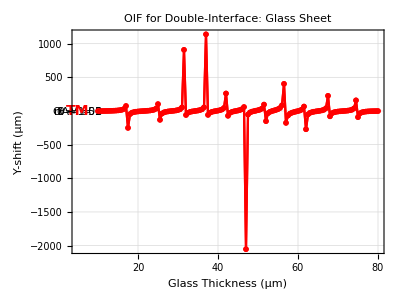

```mathematica
p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Glass Sheet",16]];

vmax =-20;
vmin = 20;

p$R1$final$y=Show[p$R1$y,p$R1$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{5,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{5,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{5,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Red,Text[font["TM",14],{5,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

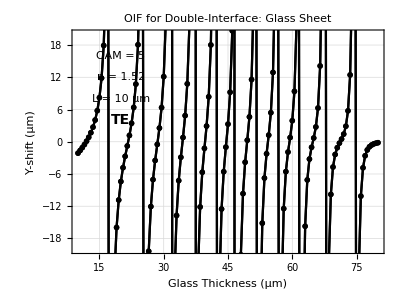

```mathematica
p$R2$y=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Glass Sheet",16]];

vmin =-20;
vmax = 20;

p$R2$final$y=Show[p$R2$y,p$R2$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 10 μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

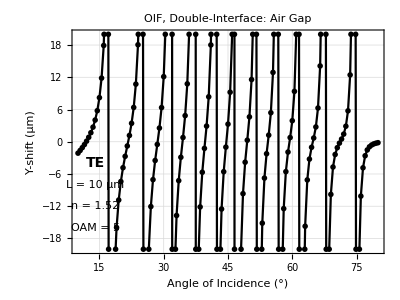

```mathematica
vmax =-20;
vmin = 20;

p$R2$y$zoom=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{25,37},{vmin,vmax}},PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF, Double-Interface: Air Gap",16]];

p$R2$final$y$zoom=Show[p$R2$y$zoom,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{14,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{14,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 10 μm",{14,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{14,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

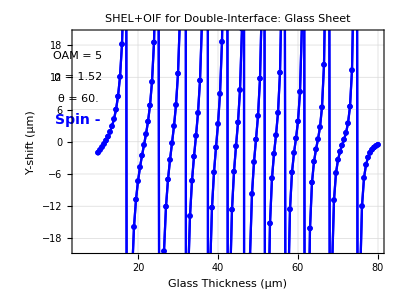

```mathematica
p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Glass Sheet",16]];

vmax =20;
vmin = -20;

p$R3$final$y=Show[p$R3$y,p$R3$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{5,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{5,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{5,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin - ",14],{5,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

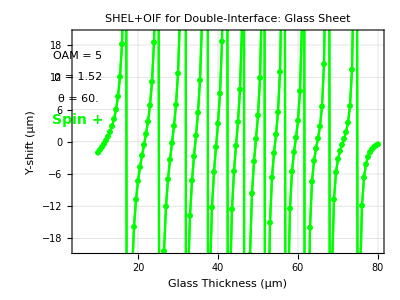

```mathematica
p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Glass Sheet",16]];

vmax =20;
vmin = -20;

p$R4$final$y=Show[p$R4$y,p$R4$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{5,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{5,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{5,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin + ",14],{5,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

#### Plot Graphics For Manuscript

#### Plot Graphics For Manuscript

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE/. {κx->0,κy->0};
ErB1$TM$func[n_,θ_,L_]=ErB1$TM/. {κx->0,κy->0};
```

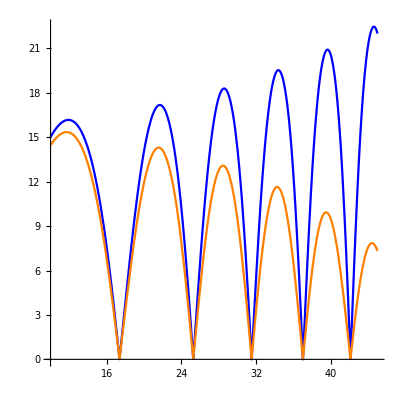

```mathematica
magfac = 40;

p$R=ParametricPlot[{{θ,magfac Abs[ErB1$TE$func[1.5168,θ Degree,99.29180321080256]]},{θ,magfac Abs[ErB1$TM$func[1.5168,θ Degree,99.29180321080256]]}},{θ,10 ,45 },AspectRatio->1,PlotStyle->{{Thickness[.004],Blue},{Thickness[.004],Orange}},BaseStyle->{"Tahoma",14}]
```

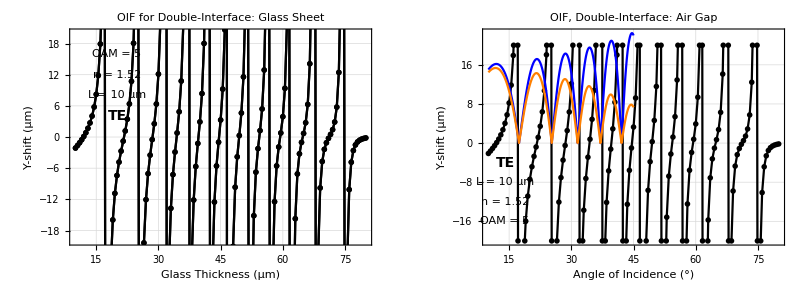

```mathematica
GraphicsRow[{p$R2$final$y,Show[p$R2$final$y$zoom,p$R]},ImageSize->800]
```

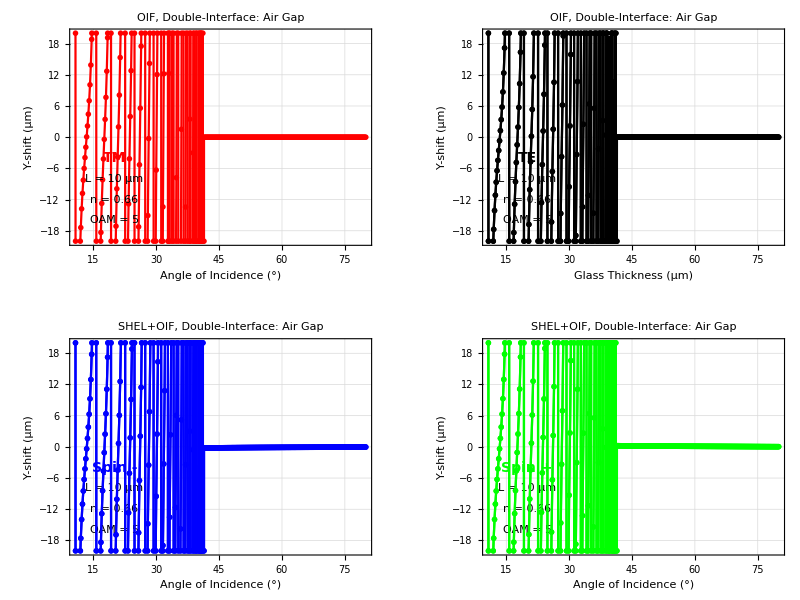

```mathematica
GraphicsGrid[{{p$R1$final$y,p$R2$final$y},{p$R3$final$y,p$R4$final$y}},ImageSize->800]
```

### Centroid Shifts versus Sheet Width: n = 1.5168, θ = 60°, OAM = 0 (Glass Sheet) FIG 7

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5
```

41.8103

#### Ramsauer-Townsend Windows

```mathematica
1/1.5168
```

0.659283

```mathematica
ErB1$TE$func[n_,β_,L_]=ErB1$TE;
```

```mathematica
0.08726646259971647/Degree
```

5.

```mathematica
Manipulate[ParametricPlot[{θ,Abs[ErB1$TE$func[n,θ Degree,L]]},{θ,10 ,80 },AspectRatio->1],{n,0.5,2},{L,0.1,20.0}]
```

```mathematica
params$here = {wk->20000.,n->1.5168,θ->60 Degree,k0->1,p->0,ℓ->0};

L$ram = {};

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,2.5}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,5.0}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,7.5}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,10}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,12.2}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,15.08}];
AppendTo[L$ram,L /. sol[[1]]];

L$ram

L$ram$units = Table[L$ram[[j]]/(2π/(632.8*10^-9))*10^6,{j,1,Length[L$ram]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.52283,5.04567,7.5685,10.0913,12.6142,15.137}

{0.254083,0.508165,0.762248,1.01633,1.27041,1.5245}

```mathematica
Clear[p$ram] ;

Array[p$ram,Length[L$ram]];

Do[p$ram[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram[[j]],-10000},{L$ram[[j]],10000}}]}],{j,1,Length[L$ram]}]

p$ram$all = Show[Table[p$ram[j],{j,1,Length[L$ram]}]];

Array[p$ram$all,Length[L$ram]];

Do[p$ram$units[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram$units[[j]],-10000},{L$ram$units[[j]],10000}}]}],{j,1,Length[L$ram]}]
p$ram$units$all = Show[Table[p$ram$units[j],{j,1,Length[L$ram]}]];

p$ram$final = Show[Plot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]],{L,1,15}],p$ram$all]
```

-Graphics-

#### Analysis

```mathematica
Clear[plots,k0];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1.5168,θ->60.0 Degree,k0->1,p->0,ℓ->0,L->Lloop};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

Print["k_0L: ",Lloop, ", Actual Gap: ",gap," μm"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

R1 =Simplify[Expand[Normal[Series[-ErB1$TM/. params$here,{κx,0,1},{κy,0,1}]]],{κx^2->0,κy^2->0,κx κy->0}];

R2 =Simplify[Expand[Normal[Series[ErB1$TE/. params$here,{κx,0,1},{κy,0,1}]]],{κx^2->0,κy^2->0,κx κy->0}];

eR = {(f[[1]]R1-f[[2]]κy Cot[θR](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θR](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,3,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,gap,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,gap,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,gap,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,gap,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{Lloop,1.0,15.0,0.2}]
```

k_0L: 1., Actual Gap: 0.100713 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0707018} μm

spin- (Reflected) = {0,-0.0707018} μm

k_0L: 1.2, Actual Gap: 0.120856 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0710661} μm

spin- (Reflected) = {0,-0.0710661} μm

k_0L: 1.4, Actual Gap: 0.140999 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0709769} μm

spin- (Reflected) = {0,-0.0709769} μm

k_0L: 1.6, Actual Gap: 0.161141 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.070455} μm

spin- (Reflected) = {0,-0.070455} μm

k_0L: 1.8, Actual Gap: 0.181284 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0696237} μm

spin- (Reflected) = {0,-0.0696237} μm

k_0L: 2., Actual Gap: 0.201426 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0686821} μm

spin- (Reflected) = {0,-0.0686821} μm

k_0L: 2.2, Actual Gap: 0.221569 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.067859} μm

spin- (Reflected) = {0,-0.067859} μm

k_0L: 2.4, Actual Gap: 0.241712 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0673577} μm

spin- (Reflected) = {0,-0.0673577} μm

k_0L: 2.6, Actual Gap: 0.261854 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0673035} μm

spin- (Reflected) = {0,-0.0673035} μm

k_0L: 2.8, Actual Gap: 0.281997 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0677101} μm

spin- (Reflected) = {0,-0.0677101} μm

k_0L: 3., Actual Gap: 0.30214 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0684756} μm

spin- (Reflected) = {0,-0.0684756} μm

k_0L: 3.2, Actual Gap: 0.322282 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0694103} μm

spin- (Reflected) = {0,-0.0694103} μm

k_0L: 3.4, Actual Gap: 0.342425 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0702862} μm

spin- (Reflected) = {0,-0.0702862} μm

k_0L: 3.6, Actual Gap: 0.362568 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0708929} μm

spin- (Reflected) = {0,-0.0708929} μm

k_0L: 3.8, Actual Gap: 0.38271 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0710867} μm

spin- (Reflected) = {0,-0.0710867} μm

k_0L: 4., Actual Gap: 0.402853 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0708221} μm

spin- (Reflected) = {0,-0.0708221} μm

k_0L: 4.2, Actual Gap: 0.422996 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0701613} μm

spin- (Reflected) = {0,-0.0701613} μm

k_0L: 4.4, Actual Gap: 0.443138 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0692611} μm

spin- (Reflected) = {0,-0.0692611} μm

k_0L: 4.6, Actual Gap: 0.463281 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0683382} μm

spin- (Reflected) = {0,-0.0683382} μm

k_0L: 4.8, Actual Gap: 0.483424 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0676184} μm

spin- (Reflected) = {0,-0.0676184} μm

k_0L: 5., Actual Gap: 0.503566 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0672804} μm

spin- (Reflected) = {0,-0.0672804} μm

k_0L: 5.2, Actual Gap: 0.523709 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.067409} μm

spin- (Reflected) = {0,-0.067409} μm

k_0L: 5.4, Actual Gap: 0.543852 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0679718} μm

spin- (Reflected) = {0,-0.0679718} μm

k_0L: 5.6, Actual Gap: 0.563994 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0688284} μm

spin- (Reflected) = {0,-0.0688284} μm

k_0L: 5.8, Actual Gap: 0.584137 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0697677} μm

spin- (Reflected) = {0,-0.0697677} μm

k_0L: 6., Actual Gap: 0.604279 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0705619} μm

spin- (Reflected) = {0,-0.0705619} μm

k_0L: 6.2, Actual Gap: 0.624422 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0710215} μm

spin- (Reflected) = {0,-0.0710215} μm

k_0L: 6.4, Actual Gap: 0.644565 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0710379} μm

spin- (Reflected) = {0,-0.0710379} μm

k_0L: 6.6, Actual Gap: 0.664707 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0706073} μm

spin- (Reflected) = {0,-0.0706073} μm

k_0L: 6.8, Actual Gap: 0.68485 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0698313} μm

spin- (Reflected) = {0,-0.0698313} μm

k_0L: 7., Actual Gap: 0.704993 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0688949} μm

spin- (Reflected) = {0,-0.0688949} μm

k_0L: 7.2, Actual Gap: 0.725135 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.068025} μm

spin- (Reflected) = {0,-0.068025} μm

k_0L: 7.4, Actual Gap: 0.745278 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0674357} μm

spin- (Reflected) = {0,-0.0674357} μm

k_0L: 7.6, Actual Gap: 0.765421 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0672739} μm

spin- (Reflected) = {0,-0.0672739} μm

k_0L: 7.8, Actual Gap: 0.785563 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0675803} μm

spin- (Reflected) = {0,-0.0675803} μm

k_0L: 8., Actual Gap: 0.805706 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.068278} μm

spin- (Reflected) = {0,-0.068278} μm

k_0L: 8.2, Actual Gap: 0.825849 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0691937} μm

spin- (Reflected) = {0,-0.0691937} μm

k_0L: 8.4, Actual Gap: 0.845991 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0701031} μm

spin- (Reflected) = {0,-0.0701031} μm

k_0L: 8.6, Actual Gap: 0.866134 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.070787} μm

spin- (Reflected) = {0,-0.070787} μm

k_0L: 8.8, Actual Gap: 0.886277 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0710829} μm

spin- (Reflected) = {0,-0.0710829} μm

k_0L: 9., Actual Gap: 0.906419 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0709213} μm

spin- (Reflected) = {0,-0.0709213} μm

k_0L: 9.2, Actual Gap: 0.926562 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0703402} μm

spin- (Reflected) = {0,-0.0703402} μm

k_0L: 9.4, Actual Gap: 0.946705 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.069477} μm

spin- (Reflected) = {0,-0.069477} μm

k_0L: 9.6, Actual Gap: 0.966847 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0685388} μm

spin- (Reflected) = {0,-0.0685388} μm

k_0L: 9.8, Actual Gap: 0.98699 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0677543} μm

spin- (Reflected) = {0,-0.0677543} μm

k_0L: 10., Actual Gap: 1.00713 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0673177} μm

spin- (Reflected) = {0,-0.0673177} μm

k_0L: 10.2, Actual Gap: 1.02728 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0673383} μm

spin- (Reflected) = {0,-0.0673383} μm

k_0L: 10.4, Actual Gap: 1.04742 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0678109} μm

spin- (Reflected) = {0,-0.0678109} μm

k_0L: 10.6, Actual Gap: 1.06756 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0686172} μm

spin- (Reflected) = {0,-0.0686172} μm

k_0L: 10.8, Actual Gap: 1.0877 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.069558} μm

spin- (Reflected) = {0,-0.069558} μm

k_0L: 11., Actual Gap: 1.10785 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0704043} μm

spin- (Reflected) = {0,-0.0704043} μm

k_0L: 11.2, Actual Gap: 1.12799 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0709532} μm

spin- (Reflected) = {0,-0.0709532} μm

k_0L: 11.4, Actual Gap: 1.14813 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0710751} μm

spin- (Reflected) = {0,-0.0710751} μm

k_0L: 11.6, Actual Gap: 1.16827 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0707413} μm

spin- (Reflected) = {0,-0.0707413} μm

k_0L: 11.8, Actual Gap: 1.18842 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0700303} μm

spin- (Reflected) = {0,-0.0700303} μm

k_0L: 12., Actual Gap: 1.20856 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0691112} μm

spin- (Reflected) = {0,-0.0691112} μm

k_0L: 12.2, Actual Gap: 1.2287 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0682059} μm

spin- (Reflected) = {0,-0.0682059} μm

k_0L: 12.4, Actual Gap: 1.24884 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0675364} μm

spin- (Reflected) = {0,-0.0675364} μm

k_0L: 12.6, Actual Gap: 1.26899 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0672691} μm

spin- (Reflected) = {0,-0.0672691} μm

k_0L: 12.8, Actual Gap: 1.28913 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0674713} μm

spin- (Reflected) = {0,-0.0674713} μm

k_0L: 13., Actual Gap: 1.30927 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.068092} μm

spin- (Reflected) = {0,-0.068092} μm

k_0L: 13.2, Actual Gap: 1.32941 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0689768} μm

spin- (Reflected) = {0,-0.0689768} μm

k_0L: 13.4, Actual Gap: 1.34956 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.069908} μm

spin- (Reflected) = {0,-0.069908} μm

k_0L: 13.6, Actual Gap: 1.3697 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0706604} μm

spin- (Reflected) = {0,-0.0706604} μm

k_0L: 13.8, Actual Gap: 1.38984 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0710549} μm

spin- (Reflected) = {0,-0.0710549} μm

k_0L: 14., Actual Gap: 1.40999 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0709983} μm

spin- (Reflected) = {0,-0.0709983} μm

k_0L: 14.2, Actual Gap: 1.43013 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0705041} μm

spin- (Reflected) = {0,-0.0705041} μm

k_0L: 14.4, Actual Gap: 1.45027 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0696889} μm

spin- (Reflected) = {0,-0.0696889} μm

k_0L: 14.6, Actual Gap: 1.47041 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0687476} μm

spin- (Reflected) = {0,-0.0687476} μm

k_0L: 14.8, Actual Gap: 1.49056 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0679087} μm

spin- (Reflected) = {0,-0.0679087} μm

k_0L: 15., Actual Gap: 1.5107 μm

TM (Reflected) = {0,0} μm

TE (Reflected) = {0,0} μm

spin+ (Reflected) = {0,0.0673794} μm

spin- (Reflected) = {0,-0.0673794} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->60.0 Degree,k0->1,p->0,ℓ->0,L->Lloop};
```

```mathematica
shift$tab$R4
```

{{5,0.100713,{-0.00252937,-0.652666}},{5,0.120856,{-0.0238912,-0.65488}},{5,0.140999,{-0.0472735,-0.688579}},{5,0.161141,{-0.072595,-0.765134}},{5,0.181284,{-0.0993713,-0.913022}},{5,0.201426,{-0.125134,-1.19463}},{5,0.221569,{-0.142921,-1.77745}},{5,0.241712,{-0.141361,-3.78128}},{5,0.261854,{-0.116337,3.57678}},{5,0.281997,{-0.0832871,0.192675}},{5,0.30214,{-0.0609867,-0.308555}},{5,0.322282,{-0.0543123,-0.467859}},{5,0.342425,{-0.0598764,-0.541216}},{5,0.362568,{-0.0739165,-0.598466}},{5,0.38271,{-0.0944197,-0.668028}},{5,0.402853,{-0.120852,-0.773346}},{5,0.422996,{-0.153413,-0.951188}},{5,0.443138,{-0.191747,-1.27506}},{5,0.463281,{-0.231993,-1.91731}},{5,0.483424,{-0.261867,-3.48173}},{5,0.503566,{-0.261772,-16.5316}},{5,0.523709,{-0.226553,3.42783}},{5,0.543852,{-0.179793,0.70558}},{5,0.563994,{-0.145695,-0.0147522}},{5,0.584137,{-0.130433,-0.309793}},{5,0.604279,{-0.130901,-0.470261}},{5,0.624422,{-0.143405,-0.593562}},{5,0.644565,{-0.166061,-0.728052}},{5,0.664707,{-0.198701,-0.918258}},{5,0.68485,{-0.242009,-1.23495}},{5,0.704993,{-0.295354,-1.8256}},{5,0.725135,{-0.351421,-3.08071}},{5,0.745278,{-0.388715,-6.92959}},{5,0.765421,{-0.379492,32.8869}},{5,0.785563,{-0.325993,3.20094}},{5,0.805706,{-0.264217,0.919148}},{5,0.825849,{-0.22074,0.132382}},{5,0.845991,{-0.200218,-0.233488}},{5,0.866134,{-0.198797,-0.453189}},{5,0.886277,{-0.212755,-0.633894}},{5,0.906419,{-0.240591,-0.839187}},{5,0.926562,{-0.2828,-1.13854}},{5,0.946705,{-0.340553,-1.65347}},{5,0.966847,{-0.411843,-2.65872}},{5,0.98699,{-0.482443,-5.01547}},{5,1.00713,{-0.518009,-16.3133}},{5,1.02728,{-0.488117,11.8143}},{5,1.04742,{-0.412282,2.92095}},{5,1.06756,{-0.337522,0.970711}},{5,1.0877,{-0.288144,0.18527}},{5,1.10785,{-0.26568,-0.21673}},{5,1.12799,{-0.265368,-0.481567}},{5,1.14813,{-0.283696,-0.719616}},{5,1.16827,{-0.31987,-1.01037}},{5,1.18842,{-0.37527,-1.4578}},{5,1.20856,{-0.451177,-2.26356}},{5,1.2287,{-0.541994,-3.93255}},{5,1.24884,{-0.621807,-8.49341}},{5,1.26899,{-0.642619,-126.671}},{5,1.28913,{-0.582843,7.96302}},{5,1.30927,{-0.485291,2.61223}},{5,1.32941,{-0.401583,0.929843}},{5,1.34956,{-0.350012,0.17511}},{5,1.3697,{-0.328706,-0.246183}},{5,1.38984,{-0.33234,-0.551801}},{5,1.40999,{-0.357985,-0.854959}},{5,1.43013,{-0.405882,-1.25639}},{5,1.45027,{-0.478345,-1.91169}},{5,1.47041,{-0.575707,-3.15398}},{5,1.49056,{-0.685036,-5.93522}},{5,1.5107,{-0.763668,-15.9616}}}

```mathematica
shift$tab$R3={{0,0.10071324798855139,{0,0.07070178585151138}},{0,0.12085589758626165,{0,0.07106614972269534}},{0,0.14099854718397192,{0,0.07097688249584166}},{0,0.16114119678168223,{0,0.07045496236636763}},{0,0.1812838463793925,{0,0.06962373541241026}},{0,0.20142649597710277,{0,0.06868209110070049}},{0,0.22156914557481305,{0,0.06785897829580548}},{0,0.24171179517252336,{0,0.06735770376881}},{0,0.2618544447702336,{0,0.06730353737687106}},{0,0.28199709436794385,{0,0.06771008147618152}},{0,0.30213974396565413,{0,0.06847555836245135}},{0,0.32228239356336447,{0,0.06941030086689261}},{0,0.34242504316107475,{0,0.07028618061550515}},{0,0.362567692758785,{0,0.07089289505021791}},{0,0.3827103423564953,{0,0.0710867256533193}},{0,0.40285299195420554,{0,0.07082209459173114}},{0,0.4229956415519158,{0,0.07016126856368192}},{0,0.4431382911496261,{0,0.06926106491078597}},{0,0.46328094074733633,{0,0.06833816415419956}},{0,0.4834235903450467,{0,0.06761838296494735}},{0,0.503566239942757,{0,0.06728042762917016}},{0,0.5237088895404672,{0,0.06740899021137944}},{0,0.5438515391381775,{0,0.0679717935733066}},{0,0.5639941887358878,{0,0.0688283944785667}},{0,0.5841368383335981,{0,0.06976770082152702}},{0,0.6042794879313083,{0,0.07056192757246077}},{0,0.6244221375290187,{0,0.07102147185304238}},{0,0.6445647871267289,{0,0.07103788023888521}},{0,0.6647074367244392,{0,0.07060729723153336}},{0,0.6848500863221495,{0,0.06983128365944549}},{0,0.7049927359198597,{0,0.06889491045576437}},{0,0.72513538551757,{0,0.06802498561266017}},{0,0.7452780351152802,{0,0.06743565654409797}},{0,0.7654206847129906,{0,0.06727388248798324}},{0,0.7855633343107009,{0,0.06758027149298056}},{0,0.8057059839084111,{0,0.06827801206831893}},{0,0.8258486335061213,{0,0.06919371960952325}},{0,0.8459912831038316,{0,0.0701030823347285}},{0,0.866133932701542,{0,0.07078696619721837}},{0,0.8862765822992522,{0,0.0710829435765179}},{0,0.9064192318969625,{0,0.07092134700329848}},{0,0.9265618814946729,{0,0.07034016614686642}},{0,0.9467045310923831,{0,0.06947696705363184}},{0,0.9668471806900932,{0,0.06853878085318696}},{0,0.9869898302878036,{0,0.06775431004538321}},{0,1.007132479885514,{0,0.06731774314742855}},{0,1.0272751294832243,{0,0.0673383182250446}},{0,1.0474177790809345,{0,0.06781086804252234}},{0,1.0675604286786449,{0,0.06861723113246078}},{0,1.087703078276355,{0,0.0695580382655628}},{0,1.1078457278740652,{0,0.07040427593185604}},{0,1.1279883774717756,{0,0.07095324847459107}},{0,1.1481310270694858,{0,0.07107512808899887}},{0,1.1682736766671962,{0,0.07074126852511531}},{0,1.1884163262649063,{0,0.07003029261598326}},{0,1.2085589758626165,{0,0.0691112457720595}},{0,1.228701625460327,{0,0.06820590662221886}},{0,1.2488442750580373,{0,0.06753635333851178}},{0,1.2689869246557477,{0,0.0672691365523113}},{0,1.2891295742534579,{0,0.06747127582462914}},{0,1.309272223851168,{0,0.06809204455515816}},{0,1.3294148734488784,{0,0.06897678335773885}},{0,1.3495575230465886,{0,0.0699079865720411}},{0,1.369700172644299,{0,0.0706604206295117}},{0,1.3898428222420092,{0,0.07105485051077441}},{0,1.4099854718397193,{0,0.0709983026982063}},{0,1.4301281214374297,{0,0.07050406503997425}},{0,1.45027077103514,{0,0.06968886562958736}},{0,1.4704134206328503,{0,0.06874755634389258}},{0,1.4905560702305605,{0,0.0679087362626877}},{0,1.5106987198282709,{0,0.06737937995369774}}};
```

```mathematica
shift$tab$R4={{0,0.10071324798855139,{0,-0.07070178590876022}},{0,0.12085589758626165,{0,-0.07106614979711885}},{0,0.14099854718397192,{0,-0.07097688253019097}},{0,0.16114119678168223,{0,-0.07045496246369068}},{0,0.1812838463793925,{0,-0.06962373542958492}},{0,0.20142649597710277,{0,-0.06868209114649958}},{0,0.22156914557481305,{0,-0.06785897833015479}},{0,0.24171179517252336,{0,-0.06735770383178374}},{0,0.2618544447702336,{0,-0.06730353739404571}},{0,0.28199709436794385,{0,-0.06771008155060503}},{0,0.30213974396565413,{0,-0.06847555843114997}},{0,0.32228239356336447,{0,-0.06941030090124192}},{0,0.34242504316107475,{0,-0.07028618067847889}},{0,0.362567692758785,{0,-0.07089289511319165}},{0,0.3827103423564953,{0,-0.07108672573919259}},{0,0.40285299195420554,{0,-0.07082209467187954}},{0,0.4229956415519158,{0,-0.07016126860375611}},{0,0.4431382911496261,{0,-0.06926106496230994}},{0,0.46328094074733633,{0,-0.06833816422289819}},{0,0.4834235903450467,{0,-0.06761838300502153}},{0,0.503566239942757,{0,-0.06728042771504343}},{0,0.5237088895404672,{0,-0.0674089902686283}},{0,0.5438515391381775,{0,-0.06797179360765591}},{0,0.5639941887358878,{0,-0.06882839447284182}},{0,0.5841368383335981,{0,-0.06976770088450075}},{0,0.6042794879313083,{0,-0.07056192762970961}},{0,0.6244221375290187,{0,-0.07102147193319076}},{0,0.6445647871267289,{0,-0.07103788033048337}},{0,0.6647074367244392,{0,-0.07060729731168176}},{0,0.6848500863221495,{0,-0.06983128372241924}},{0,0.7049927359198597,{0,-0.068894910524463}},{0,0.72513538551757,{0,-0.0680249856756339}},{0,0.7452780351152802,{0,-0.06743565662424637}},{0,0.7654206847129906,{0,-0.06727388255095698}},{0,0.7855633343107009,{0,-0.06758027152160498}},{0,0.8057059839084111,{0,-0.0682780120797687}},{0,0.8258486335061213,{0,-0.06919371966104723}},{0,0.8459912831038316,{0,-0.07010308235762805}},{0,0.866133932701542,{0,-0.07078696628881653}},{0,0.8862765822992522,{0,-0.07108294363376676}},{0,0.9064192318969625,{0,-0.07092134706627223}},{0,0.9265618814946729,{0,-0.07034016624418946}},{0,0.9467045310923831,{0,-0.06947696711088068}},{0,0.9668471806900932,{0,-0.06853878088753627}},{0,0.9869898302878036,{0,-0.06775431007400763}},{0,1.007132479885514,{0,-0.06731774321612717}},{0,1.0272751294832243,{0,-0.06733831823649437}},{0,1.0474177790809345,{0,-0.06781086808259654}},{0,1.0675604286786449,{0,-0.06861723120115941}},{0,1.087703078276355,{0,-0.06955803836861074}},{0,1.1078457278740652,{0,-0.07040427601200443}},{0,1.1279883774717756,{0,-0.07095324852611504}},{0,1.1481310270694858,{0,-0.07107512815197262}},{0,1.1682736766671962,{0,-0.07074126858808906}},{0,1.1884163262649063,{0,-0.07003029266750722}},{0,1.2085589758626165,{0,-0.06911124579495904}},{0,1.228701625460327,{0,-0.06820590666229306}},{0,1.2488442750580373,{0,-0.06753635339576064}},{0,1.2689869246557477,{0,-0.06726913658093572}},{0,1.2891295742534579,{0,-0.0674712758761531}},{0,1.309272223851168,{0,-0.06809204458950747}},{0,1.3294148734488784,{0,-0.0689767834207126}},{0,1.3495575230465886,{0,-0.06990798666936415}},{0,1.369700172644299,{0,-0.07066042073255964}},{0,1.3898428222420092,{0,-0.07105485053939883}},{0,1.4099854718397193,{0,-0.07099830276118003}},{0,1.4301281214374297,{0,-0.07050406512012265}},{0,1.45027077103514,{0,-0.06968886562958736}},{0,1.4704134206328503,{0,-0.06874755641259121}},{0,1.4905560702305605,{0,-0.06790873627986235}},{0,1.5106987198282709,{0,-0.06737938002239635}}};
```

```mathematica
R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

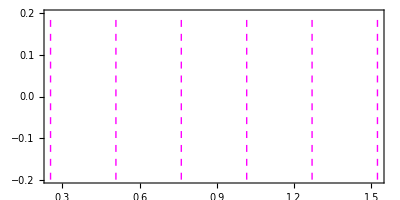

```mathematica
p$RT=Show[Graphics[Table[{Magenta,Thick,Dashing->Small,Line[{{L$ram$units[[j]],-.2},{L$ram$units[[j]],.2}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5]
```

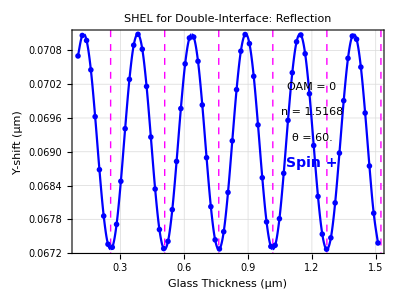

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

p$R3$y$points=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},InterpolationOrder->2,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

p$R3$y$curve=ListLinePlot[{R3y$plotdata},PlotMarkers->None,Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},InterpolationOrder->2,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

vmax = 0.0715;
vmin = 0.067;

p$R3$final$y=Show[p$R3$y$points,p$RT,p$R3$y$curve,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.2,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.2,vmin + 0.6(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.2,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin + ",14],{1.2,vmin + 0.4 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]}]
```

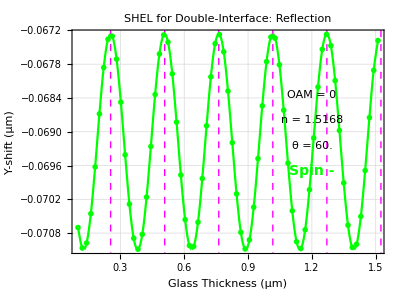

```mathematica
p$R4$y$points=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},InterpolationOrder->2,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

p$R4$y$curve=ListLinePlot[{R4y$plotdata},PlotMarkers->None,Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},InterpolationOrder->2,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

vmin = -0.0715;
vmax = -0.067;

p$R4$final$y=Show[p$R4$y$points,p$RT,p$R4$y$curve,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.2,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.2,vmin + 0.6(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.2,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin - ",14],{1.2,vmin + 0.4 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]}]
```

#### Plot Graphics For Manuscript

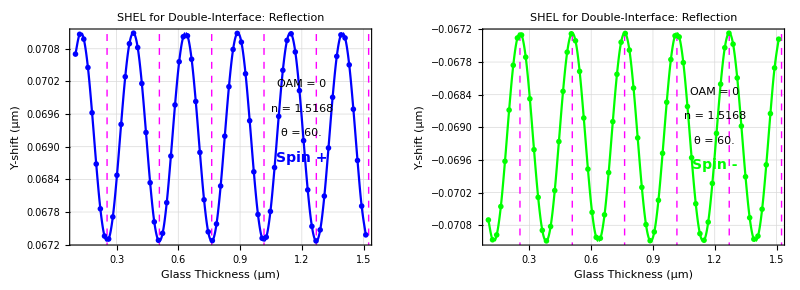

```mathematica
GraphicsRow[{p$R3$final$y,p$R4$final$y},ImageSize->800]
```

### Centroid Shifts versus Sheet Width: n = 1.5168, θ = 30°, OAM = 0 (Glass Sheet) FIG 7

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5
```

41.8103

#### Ramsauer-Townsend Windows

```mathematica
1/1.5168
```

0.659283

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE /. {κx->0,κy->0}
```

(n √(1-(1-Cos[θ]^2)/n^2) (-(1+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2))) √(Cos[θ]^2)+(-1+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2))) n √(1-(1-Cos[θ]^2)/n^2))+Cos[θ] (√(Cos[θ]^2)+n √(1-(1-Cos[θ]^2)/n^2)+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2)) (-√(Cos[θ]^2)+n √(1-(1-Cos[θ]^2)/n^2))))/(-n √(1-(1-Cos[θ]^2)/n^2) (-(1+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2))) √(Cos[θ]^2)+(-1+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2))) n √(1-(1-Cos[θ]^2)/n^2))+Cos[θ] (√(Cos[θ]^2)+n √(1-(1-Cos[θ]^2)/n^2)+ⅇ^(2 ⅈ L n √(1-(1-Cos[θ]^2)/n^2)) (-√(Cos[θ]^2)+n √(1-(1-Cos[θ]^2)/n^2))))

```mathematica
0.08726646259971647/Degree
```

5.

```mathematica
Manipulate[ParametricPlot[{θ,Abs[ErB1$TE$func[n,θ Degree,L]]},{θ,10 ,80 },AspectRatio->1],{n,0.5,2},{L,0.1,20.0}]
```

```mathematica
params$here = {wk->20000.,n->1.5168,θ->30 Degree,k0->1,p->0,ℓ->0};

L$ram = {};

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,1.7}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,4.0}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,6.3}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,8.4}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,10.5}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,13}];
AppendTo[L$ram,L /. sol[[1]]];

L$ram

L$ram$units = Table[L$ram[[j]]/(2π/(632.8*10^-9))*10^6,{j,1,Length[L$ram]}]
```

{2.19382,4.38764,6.58146,8.77527,10.9691,13.1629}

{0.220947,0.441893,0.66284,0.883786,1.10473,1.32568}

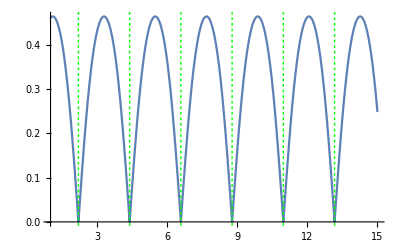

```mathematica
Clear[p$ram] ;

Array[p$ram,Length[L$ram]];

Do[p$ram[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram[[j]],-10000},{L$ram[[j]],10000}}]}],{j,1,Length[L$ram]}]

p$ram$all = Show[Table[p$ram[j],{j,1,Length[L$ram]}]];

Array[p$ram$all,Length[L$ram]];

Do[p$ram$units[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram$units[[j]],-10000},{L$ram$units[[j]],10000}}]}],{j,1,Length[L$ram]}]
p$ram$units$all = Show[Table[p$ram$units[j],{j,1,Length[L$ram]}]];

p$ram$final = Show[Plot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]],{L,1,15}],p$ram$all]
```

#### Analysis

```mathematica
Clear[plots,k0];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1.5168,θ->30.0 Degree,k0->1,p->0,ℓ->0,L->Lloop};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

Print["k_0L: ",Lloop, ", Actual Gap: ",gap," μm"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

R1 =Simplify[Expand[Normal[Series[-ErB1$TM/. params$here,{κx,0,1},{κy,0,1}]]],{κx^2->0,κy^2->0,κx κy->0}];

R2 =Simplify[Expand[Normal[Series[ErB1$TE/. params$here,{κx,0,1},{κy,0,1}]]],{κx^2->0,κy^2->0,κx κy->0}];

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,3,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,gap,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,gap,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,gap,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,gap,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{Lloop,1.0,15.0,0.2}]
```

k_0L: 1., Actual Gap: 0.100713 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0268734,-0.0117908} μm

spin- (Reflected) = {-0.0268734,0.0117908} μm

k_0L: 1.2, Actual Gap: 0.120856 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0343787,-0.0118} μm

spin- (Reflected) = {-0.0343787,0.0118} μm

k_0L: 1.4, Actual Gap: 0.140999 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.042817,-0.0123858} μm

spin- (Reflected) = {-0.042817,0.0123858} μm

k_0L: 1.6, Actual Gap: 0.161141 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0520495,-0.0134201} μm

spin- (Reflected) = {-0.0520495,0.0134201} μm

k_0L: 1.8, Actual Gap: 0.181284 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0613165,-0.0146293} μm

spin- (Reflected) = {-0.0613165,0.0146293} μm

k_0L: 2., Actual Gap: 0.201426 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.069223,-0.0156129} μm

spin- (Reflected) = {-0.069223,0.0156129} μm

k_0L: 2.2, Actual Gap: 0.221569 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0744827,-0.0159791} μm

spin- (Reflected) = {-0.0744827,0.0159791} μm

k_0L: 2.4, Actual Gap: 0.241712 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0770702,-0.0155667} μm

spin- (Reflected) = {-0.0770702,0.0155667} μm

k_0L: 2.6, Actual Gap: 0.261854 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0783368,-0.0145567} μm

spin- (Reflected) = {-0.0783368,0.0145567} μm

k_0L: 2.8, Actual Gap: 0.281997 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0799231,-0.0133476} μm

spin- (Reflected) = {-0.0799231,0.0133476} μm

k_0L: 3., Actual Gap: 0.30214 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0829533,-0.0123345} μm

spin- (Reflected) = {-0.0829533,0.0123345} μm

k_0L: 3.2, Actual Gap: 0.322282 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0880741,-0.0117821} μm

spin- (Reflected) = {-0.0880741,0.0117821} μm

k_0L: 3.4, Actual Gap: 0.342425 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.0956873,-0.0118098} μm

spin- (Reflected) = {-0.0956873,0.0118098} μm

k_0L: 3.6, Actual Gap: 0.362568 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.105935,-0.012412} μm

spin- (Reflected) = {-0.105935,0.012412} μm

k_0L: 3.8, Actual Gap: 0.38271 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.118376,-0.0134567} μm

spin- (Reflected) = {-0.118376,0.0134567} μm

k_0L: 4., Actual Gap: 0.402853 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.131498,-0.0146654} μm

spin- (Reflected) = {-0.131498,0.0146654} μm

k_0L: 4.2, Actual Gap: 0.422996 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.142601,-0.0156351} μm

spin- (Reflected) = {-0.142601,0.0156351} μm

k_0L: 4.4, Actual Gap: 0.443138 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.148957,-0.0159779} μm

spin- (Reflected) = {-0.148957,0.0159779} μm

k_0L: 4.6, Actual Gap: 0.463281 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.149974,-0.0155427} μm

spin- (Reflected) = {-0.149974,0.0155427} μm

k_0L: 4.8, Actual Gap: 0.483424 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.147806,-0.01452} μm

spin- (Reflected) = {-0.147806,0.01452} μm

k_0L: 5., Actual Gap: 0.503566 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.145574,-0.0133116} μm

spin- (Reflected) = {-0.145574,0.0133116} μm

k_0L: 5.2, Actual Gap: 0.523709 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.145614,-0.0123096} μm

spin- (Reflected) = {-0.145614,0.0123096} μm

k_0L: 5.4, Actual Gap: 0.543852 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.149228,-0.011774} μm

spin- (Reflected) = {-0.149228,0.011774} μm

k_0L: 5.6, Actual Gap: 0.563994 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.157057,-0.0118201} μm

spin- (Reflected) = {-0.157057,0.0118201} μm

k_0L: 5.8, Actual Gap: 0.584137 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.169213,-0.0124387} μm

spin- (Reflected) = {-0.169213,0.0124387} μm

k_0L: 6., Actual Gap: 0.604279 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.184932,-0.0134934} μm

spin- (Reflected) = {-0.184932,0.0134934} μm

k_0L: 6.2, Actual Gap: 0.624422 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.201914,-0.0147012} μm

spin- (Reflected) = {-0.201914,0.0147012} μm

k_0L: 6.4, Actual Gap: 0.644565 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.216124,-0.0156567} μm

spin- (Reflected) = {-0.216124,0.0156567} μm

k_0L: 6.6, Actual Gap: 0.664707 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.223416,-0.015976} μm

spin- (Reflected) = {-0.223416,0.015976} μm

k_0L: 6.8, Actual Gap: 0.68485 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.222708,-0.0155181} μm

spin- (Reflected) = {-0.222708,0.0155181} μm

k_0L: 7., Actual Gap: 0.704993 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.217034,-0.0144832} μm

spin- (Reflected) = {-0.217034,0.0144832} μm

k_0L: 7.2, Actual Gap: 0.725135 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.211004,-0.0132758} μm

spin- (Reflected) = {-0.211004,0.0132758} μm

k_0L: 7.4, Actual Gap: 0.745278 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.208132,-0.0122851} μm

spin- (Reflected) = {-0.208132,0.0122851} μm

k_0L: 7.6, Actual Gap: 0.765421 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.210341,-0.0117664} μm

spin- (Reflected) = {-0.210341,0.0117664} μm

k_0L: 7.8, Actual Gap: 0.785563 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.218494,-0.011831} μm

spin- (Reflected) = {-0.218494,0.011831} μm

k_0L: 8., Actual Gap: 0.805706 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.232657,-0.0124659} μm

spin- (Reflected) = {-0.232657,0.0124659} μm

k_0L: 8.2, Actual Gap: 0.825849 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.25172,-0.0135303} μm

spin- (Reflected) = {-0.25172,0.0135303} μm

k_0L: 8.4, Actual Gap: 0.845991 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.272563,-0.0147367} μm

spin- (Reflected) = {-0.272563,0.0147367} μm

k_0L: 8.6, Actual Gap: 0.866134 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.289787,-0.0156777} μm

spin- (Reflected) = {-0.289787,0.0156777} μm

k_0L: 8.8, Actual Gap: 0.886277 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.29785,-0.0159733} μm

spin- (Reflected) = {-0.29785,0.0159733} μm

k_0L: 9., Actual Gap: 0.906419 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.295267,-0.015493} μm

spin- (Reflected) = {-0.295267,0.015493} μm

k_0L: 9.2, Actual Gap: 0.926562 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.286022,-0.0144462} μm

spin- (Reflected) = {-0.286022,0.0144462} μm

k_0L: 9.4, Actual Gap: 0.946705 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.276216,-0.0132402} μm

spin- (Reflected) = {-0.276216,0.0132402} μm

k_0L: 9.6, Actual Gap: 0.966847 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.270509,-0.0122611} μm

spin- (Reflected) = {-0.270509,0.0122611} μm

k_0L: 9.8, Actual Gap: 0.98699 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.271417,-0.0117595} μm

spin- (Reflected) = {-0.271417,0.0117595} μm

k_0L: 10., Actual Gap: 1.00713 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.280001,-0.0118425} μm

spin- (Reflected) = {-0.280001,0.0118425} μm

k_0L: 10.2, Actual Gap: 1.02728 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.296269,-0.0124934} μm

spin- (Reflected) = {-0.296269,0.0124934} μm

k_0L: 10.4, Actual Gap: 1.04742 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.318741,-0.0135674} μm

spin- (Reflected) = {-0.318741,0.0135674} μm

k_0L: 10.6, Actual Gap: 1.06756 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.343442,-0.014772} μm

spin- (Reflected) = {-0.343442,0.014772} μm

k_0L: 10.8, Actual Gap: 1.0877 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.363583,-0.015698} μm

spin- (Reflected) = {-0.363583,0.015698} μm

k_0L: 11., Actual Gap: 1.10785 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.372252,-0.0159698} μm

spin- (Reflected) = {-0.372252,0.0159698} μm

k_0L: 11.2, Actual Gap: 1.12799 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.367646,-0.0154673} μm

spin- (Reflected) = {-0.367646,0.0154673} μm

k_0L: 11.4, Actual Gap: 1.14813 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.354768,-0.0144091} μm

spin- (Reflected) = {-0.354768,0.0144091} μm

k_0L: 11.6, Actual Gap: 1.16827 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.341213,-0.0132049} μm

spin- (Reflected) = {-0.341213,0.0132049} μm

k_0L: 11.8, Actual Gap: 1.18842 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.332752,-0.0122376} μm

spin- (Reflected) = {-0.332752,0.0122376} μm

k_0L: 12., Actual Gap: 1.20856 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.332461,-0.0117531} μm

spin- (Reflected) = {-0.332461,0.0117531} μm

k_0L: 12.2, Actual Gap: 1.2287 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.341585,-0.0118545} μm

spin- (Reflected) = {-0.341585,0.0118545} μm

k_0L: 12.4, Actual Gap: 1.24884 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.360053,-0.0125214} μm

spin- (Reflected) = {-0.360053,0.0125214} μm

k_0L: 12.6, Actual Gap: 1.26899 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.385997,-0.0136045} μm

spin- (Reflected) = {-0.385997,0.0136045} μm

k_0L: 12.8, Actual Gap: 1.28913 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.41455,-0.0148071} μm

spin- (Reflected) = {-0.41455,0.0148071} μm

k_0L: 13., Actual Gap: 1.30927 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.437506,-0.0157177} μm

spin- (Reflected) = {-0.437506,0.0157177} μm

k_0L: 13.2, Actual Gap: 1.32941 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.446613,-0.0159656} μm

spin- (Reflected) = {-0.446613,0.0159656} μm

k_0L: 13.4, Actual Gap: 1.34956 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.43984,-0.015441} μm

spin- (Reflected) = {-0.43984,0.015441} μm

k_0L: 13.6, Actual Gap: 1.3697 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.423271,-0.0143719} μm

spin- (Reflected) = {-0.423271,0.0143719} μm

k_0L: 13.8, Actual Gap: 1.38984 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.405997,-0.0131698} μm

spin- (Reflected) = {-0.405997,0.0131698} μm

k_0L: 14., Actual Gap: 1.40999 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.394865,-0.0122145} μm

spin- (Reflected) = {-0.394865,0.0122145} μm

k_0L: 14.2, Actual Gap: 1.43013 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.393479,-0.0117472} μm

spin- (Reflected) = {-0.393479,0.0117472} μm

k_0L: 14.4, Actual Gap: 1.45027 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.403249,-0.0118671} μm

spin- (Reflected) = {-0.403249,0.0118671} μm

k_0L: 14.6, Actual Gap: 1.47041 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.424015,-0.0125498} μm

spin- (Reflected) = {-0.424015,0.0125498} μm

k_0L: 14.8, Actual Gap: 1.49056 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.45349,-0.0136418} μm

spin- (Reflected) = {-0.45349,0.0136418} μm

k_0L: 15., Actual Gap: 1.5107 μm

TM (Reflected) = shift$R1 μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = {-0.485883,-0.0148418} μm

spin- (Reflected) = {-0.485883,0.0148418} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->60.0 Degree,k0->1,p->0,ℓ->0,L->Lloop};
```

```mathematica
shift$tab$R4
```

{{0,0.100713,{-0.0268734,0.0117908}},{0,0.120856,{-0.0343787,0.0118}},{0,0.140999,{-0.042817,0.0123858}},{0,0.161141,{-0.0520495,0.0134201}},{0,0.181284,{-0.0613165,0.0146293}},{0,0.201426,{-0.069223,0.0156129}},{0,0.221569,{-0.0744827,0.0159791}},{0,0.241712,{-0.0770702,0.0155667}},{0,0.261854,{-0.0783368,0.0145567}},{0,0.281997,{-0.0799231,0.0133476}},{0,0.30214,{-0.0829533,0.0123345}},{0,0.322282,{-0.0880741,0.0117821}},{0,0.342425,{-0.0956873,0.0118098}},{0,0.362568,{-0.105935,0.012412}},{0,0.38271,{-0.118376,0.0134567}},{0,0.402853,{-0.131498,0.0146654}},{0,0.422996,{-0.142601,0.0156351}},{0,0.443138,{-0.148957,0.0159779}},{0,0.463281,{-0.149974,0.0155427}},{0,0.483424,{-0.147806,0.01452}},{0,0.503566,{-0.145574,0.0133116}},{0,0.523709,{-0.145614,0.0123096}},{0,0.543852,{-0.149228,0.011774}},{0,0.563994,{-0.157057,0.0118201}},{0,0.584137,{-0.169213,0.0124387}},{0,0.604279,{-0.184932,0.0134934}},{0,0.624422,{-0.201914,0.0147012}},{0,0.644565,{-0.216124,0.0156567}},{0,0.664707,{-0.223416,0.015976}},{0,0.68485,{-0.222708,0.0155181}},{0,0.704993,{-0.217034,0.0144832}},{0,0.725135,{-0.211004,0.0132758}},{0,0.745278,{-0.208132,0.0122851}},{0,0.765421,{-0.210341,0.0117664}},{0,0.785563,{-0.218494,0.011831}},{0,0.805706,{-0.232657,0.0124659}},{0,0.825849,{-0.25172,0.0135303}},{0,0.845991,{-0.272563,0.0147367}},{0,0.866134,{-0.289787,0.0156777}},{0,0.886277,{-0.29785,0.0159733}},{0,0.906419,{-0.295267,0.015493}},{0,0.926562,{-0.286022,0.0144462}},{0,0.946705,{-0.276216,0.0132402}},{0,0.966847,{-0.270509,0.0122611}},{0,0.98699,{-0.271417,0.0117595}},{0,1.00713,{-0.280001,0.0118425}},{0,1.02728,{-0.296269,0.0124934}},{0,1.04742,{-0.318741,0.0135674}},{0,1.06756,{-0.343442,0.014772}},{0,1.0877,{-0.363583,0.015698}},{0,1.10785,{-0.372252,0.0159698}},{0,1.12799,{-0.367646,0.0154673}},{0,1.14813,{-0.354768,0.0144091}},{0,1.16827,{-0.341213,0.0132049}},{0,1.18842,{-0.332752,0.0122376}},{0,1.20856,{-0.332461,0.0117531}},{0,1.2287,{-0.341585,0.0118545}},{0,1.24884,{-0.360053,0.0125214}},{0,1.26899,{-0.385997,0.0136045}},{0,1.28913,{-0.41455,0.0148071}},{0,1.30927,{-0.437506,0.0157177}},{0,1.32941,{-0.446613,0.0159656}},{0,1.34956,{-0.43984,0.015441}},{0,1.3697,{-0.423271,0.0143719}},{0,1.38984,{-0.405997,0.0131698}},{0,1.40999,{-0.394865,0.0122145}},{0,1.43013,{-0.393479,0.0117472}},{0,1.45027,{-0.403249,0.0118671}},{0,1.47041,{-0.424015,0.0125498}},{0,1.49056,{-0.45349,0.0136418}},{0,1.5107,{-0.485883,0.0148418}}}

```mathematica
shift$tab$R3={{0,0.10071324798855139,{-0.02687343001062548,-0.011790760222673483}},{0,0.12085589758626165,{-0.03437871443429382,-0.011799991840729813}},{0,0.14099854718397192,{-0.04281700592066139,-0.012385763688812102}},{0,0.16114119678168223,{-0.052049497960887384,-0.013420146774946325}},{0,0.1812838463793925,{-0.06131646957719588,-0.01462934299046973}},{0,0.20142649597710277,{-0.06922301918340243,-0.015612927772107932}},{0,0.22156914557481305,{-0.07448268536459968,-0.015979110284792583}},{0,0.24171179517252336,{-0.07707020314267732,-0.01556669872759737}},{0,0.2618544447702336,{-0.0783367579805547,-0.014556650989792351}},{0,0.28199709436794385,{-0.07992309623461202,-0.013347567789230448}},{0,0.30213974396565413,{-0.08295330534718223,-0.012334545595648736}},{0,0.32228239356336447,{-0.08807406279598605,-0.011782090765458024}},{0,0.34242504316107475,{-0.09568732000556743,-0.011809783993759577}},{0,0.362567692758785,{-0.10593481515847568,-0.012412036309716016}},{0,0.3827103423564953,{-0.11837597348475204,-0.013456709161638663}},{0,0.40285299195420554,{-0.13149807449650006,-0.014665373317768318}},{0,0.4229956415519158,{-0.142600670697683,-0.015635133371492395}},{0,0.4431382911496261,{-0.14895727490549499,-0.0159779487628059}},{0,0.46328094074733633,{-0.1499739554725557,-0.015542695325294856}},{0,0.4834235903450467,{-0.14780555935543124,-0.014520015782558486}},{0,0.503566239942757,{-0.14557376502221567,-0.013311571731095507}},{0,0.5237088895404672,{-0.14561427083015296,-0.0123096114414876}},{0,0.5438515391381775,{-0.14922814645277183,-0.01177398516937438}},{0,0.5639941887358878,{-0.15705732248751492,-0.011820134741026646}},{0,0.5841368383335981,{-0.16921328310734315,-0.01243874361543893}},{0,0.6042794879313083,{-0.18493207322645763,-0.013493439550816196}},{0,0.6244221375290187,{-0.20191415159249876,-0.014701175588534489}},{0,0.6445647871267289,{-0.21612419912022127,-0.015656719996273872}},{0,0.6647074367244392,{-0.22341568049322746,-0.015976013493941055}},{0,0.6848500863221495,{-0.22270820097766855,-0.015518113177158635}},{0,0.7049927359198597,{-0.21703424268886537,-0.014483205285060386}},{0,0.72513538551757,{-0.21100390396163354,-0.013275784734323422}},{0,0.7452780351152802,{-0.20813150094134966,-0.012285134516743934}},{0,0.7654206847129906,{-0.2103406549445627,-0.01176644488854343}},{0,0.7855633343107009,{-0.21849364265953142,-0.011831042170419314}},{0,0.8057059839084111,{-0.23265650922025874,-0.012465879537602382}},{0,0.8258486335061213,{-0.25171977555180586,-0.013530327328541503}},{0,0.8459912831038316,{-0.2725628262972864,-0.014736736480960062}},{0,0.866133932701542,{-0.2897872938641075,-0.0156776781431427}},{0,0.8862765822992522,{-0.297849829558577,-0.015973305394179706}},{0,0.9064192318969625,{-0.29526745222374495,-0.015492962782628426}},{0,0.9265618814946729,{-0.2860218510719973,-0.014446232750407616}},{0,0.9467045310923831,{-0.2762160673822068,-0.013240216834638194}},{0,0.9668471806900932,{-0.27050934800767756,-0.012261120099762022}},{0,0.9869898302878036,{-0.2714165729175747,-0.011759471359911395}},{0,1.007132479885514,{-0.2800011850881368,-0.011842504203804205}},{0,1.0272751294832243,{-0.29626853664597,-0.012493438013552799}},{0,1.0474177790809345,{-0.31874093467101006,-0.013567361754929686}},{0,1.0675604286786449,{-0.3434420359003256,-0.014772042799184322}},{0,1.087703078276355,{-0.3635834905319378,-0.015697998663732098}},{0,1.1078457278740652,{-0.3722516725635372,-0.01596982570582197}},{0,1.1279883774717756,{-0.3676463960878228,-0.015467254933113097}},{0,1.1481310270694858,{-0.35476760546242997,-0.014409111225613867}},{0,1.1682736766671962,{-0.3412129158156244,-0.013204877781519558}},{0,1.1884163262649063,{-0.332752209296392,-0.012237573371563096}},{0,1.2085589758626165,{-0.33246089463583106,-0.011753065905926787}},{0,1.228701625460327,{-0.34158483714802024,-0.011854518717248854}},{0,1.2488442750580373,{-0.36005334966995356,-0.012521412717291878}},{0,1.2689869246557477,{-0.385997277844951,-0.013604531895449743}},{0,1.2891295742534579,{-0.414549528163025,-0.014807081324447023}},{0,1.309272223851168,{-0.43750617447669216,-0.01571767254134766}},{0,1.3294148734488784,{-0.4466131908844825,-0.015965576014661084}},{0,1.3495575230465886,{-0.43983989651764344,-0.015441000620392503}},{0,1.369700172644299,{-0.423270902978213,-0.01437185379204214}},{0,1.3898428222420092,{-0.40599721331667715,-0.013169777181325112}},{0,1.4099854718397193,{-0.3948645251373355,-0.012214499392945796}},{0,1.4301281214374297,{-0.3934786227732119,-0.011747229683016443}},{0,1.45027077103514,{-0.403249467630893,-0.011867083323476078}},{0,1.4704134206328503,{-0.42401487199694904,-0.01254979728274712}},{0,1.4905560702305605,{-0.4534904022593899,-0.01364182678694625}},{0,1.5106987198282709,{-0.48588286036840783,-0.0148418388036386}}};
```

```mathematica
shift$tab$R4={{0,0.10071324798855139,{-0.02687342999917571,0.011790760171149514}},{0,0.12085589758626165,{-0.03437871443429382,0.011799991846454699}},{0,0.14099854718397192,{-0.04281700592066139,0.012385763620113479}},{0,0.16114119678168223,{-0.05204949794943761,0.013420146711972586}},{0,0.1812838463793925,{-0.061316469582920766,0.014629342961845305}},{0,0.20142649597710277,{-0.06922301917195267,0.01561292768623465}},{0,0.22156914557481305,{-0.07448268537032457,0.015979110198919306}},{0,0.24171179517252336,{-0.07707020314267732,0.015566698635999207}},{0,0.2618544447702336,{-0.0783367579805547,0.014556650955443038}},{0,0.28199709436794385,{-0.07992309623461202,0.013347567726256707}},{0,0.30213974396565413,{-0.08295330534145735,0.012334545532674997}},{0,0.32228239356336447,{-0.08807406280171094,0.01178209073110871}},{0,0.34242504316107475,{-0.09568731999411764,0.01180978395368538}},{0,0.362567692758785,{-0.10593481517565033,0.012412036258192049}},{0,0.3827103423564953,{-0.11837597347902716,0.01345670911583958}},{0,0.40285299195420554,{-0.13149807450222492,0.01466537328914389}},{0,0.4229956415519158,{-0.14260067069195811,0.015635133285619118}},{0,0.4431382911496261,{-0.14895727491694477,0.015977948699832163}},{0,0.46328094074733633,{-0.1499739554668308,0.015542695285220658}},{0,0.4834235903450467,{-0.14780555936688103,0.014520015708134977}},{0,0.503566239942757,{-0.14557376500504102,0.013311571662396883}},{0,0.5237088895404672,{-0.14561427080725342,0.012309611378513862}},{0,0.5438515391381775,{-0.14922814644704693,0.011773985117850412}},{0,0.5639941887358878,{-0.15705732248179005,0.01182013471240222}},{0,0.5841368383335981,{-0.1692132830958934,0.012438743535290534}},{0,0.6042794879313083,{-0.18493207322645763,0.013493439516466883}},{0,0.6244221375290187,{-0.20191415158677387,0.014701175519835866}},{0,0.6445647871267289,{-0.21612419911449637,0.015656719916125477}},{0,0.6647074367244392,{-0.22341568048750257,0.015976013425242432}},{0,0.6848500863221495,{-0.2227082009662188,0.015518113125634666}},{0,0.7049927359198597,{-0.21703424270604002,0.014483205233536417}},{0,0.72513538551757,{-0.2110039039673584,0.013275784734323422}},{0,0.7452780351152802,{-0.20813150094707453,0.01228513444804531}},{0,0.7654206847129906,{-0.2103406549331129,0.011766444848469233}},{0,0.7855633343107009,{-0.21849364265953142,0.011831042136070002}},{0,0.8057059839084111,{-0.23265650922025874,0.012465879486078415}},{0,0.8258486335061213,{-0.2517197755403561,0.013530327288467306}},{0,0.8459912831038316,{-0.2725628263087362,0.014736736423711209}},{0,0.866133932701542,{-0.28978729384693286,0.015677678120243156}},{0,0.8862765822992522,{-0.297849829558577,0.015973305325481083}},{0,0.9064192318969625,{-0.2952674522294699,0.015492962719654689}},{0,0.9265618814946729,{-0.28602185106627237,0.014446232687433879}},{0,0.9467045310923831,{-0.2762160673764819,0.013240216823188423}},{0,0.9668471806900932,{-0.2705093480134025,0.012261120036788283}},{0,0.9869898302878036,{-0.2714165729175747,0.011759471348461625}},{0,1.007132479885514,{-0.2800011850938617,0.011842504198079319}},{0,1.0272751294832243,{-0.2962685366287954,0.012493437927679518}},{0,1.0474177790809345,{-0.31874093465956027,0.013567361691955946}},{0,1.0675604286786449,{-0.3434420359003256,0.014772042759110125}},{0,1.087703078276355,{-0.36358349054338757,0.01569799861220813}},{0,1.1078457278740652,{-0.3722516725635372,0.015969825637123347}},{0,1.1279883774717756,{-0.3676463960878228,0.0154672548930389}},{0,1.1481310270694858,{-0.35476760546242997,0.014409111156915243}},{0,1.1682736766671962,{-0.3412129158098995,0.013204877747170244}},{0,1.1884163262649063,{-0.33275220928494226,0.012237573325764013}},{0,1.2085589758626165,{-0.3324608946243813,0.011753065883027243}},{0,1.228701625460327,{-0.3415848371422953,0.01185451864855023}},{0,1.2488442750580373,{-0.3600533496756784,0.012521412642868367}},{0,1.2689869246557477,{-0.385997277844951,0.013604531838200892}},{0,1.2891295742534579,{-0.4145495281859245,0.014807081250023514}},{0,1.309272223851168,{-0.4375061744595175,0.015717672501273462}},{0,1.3294148734488784,{-0.4466131908730327,0.015965575974586886}},{0,1.3495575230465886,{-0.43983989650619365,0.015441000614667619}},{0,1.369700172644299,{-0.4232709029667633,0.014371853734793287}},{0,1.3898428222420092,{-0.40599721331667715,0.013169777106901603}},{0,1.4099854718397193,{-0.3948645251430604,0.012214499324247171}},{0,1.4301281214374297,{-0.39347862277893675,0.011747229631492474}},{0,1.45027077103514,{-0.403249467630893,0.011867083254777455}},{0,1.4704134206328503,{-0.42401487199694904,0.012549797231223151}},{0,1.4905560702305605,{-0.4534904022651148,0.013641826741147169}},{0,1.5106987198282709,{-0.48588286036268297,0.014841838757839518}}};
```

```mathematica
R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

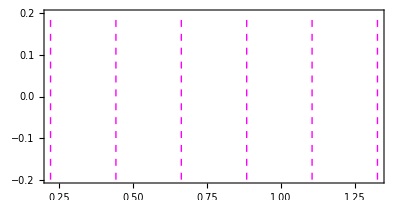

```mathematica
p$RT=Show[Graphics[Table[{Magenta,Thick,Dashing->Small,Line[{{L$ram$units[[j]],-.2},{L$ram$units[[j]],.2}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5]
```

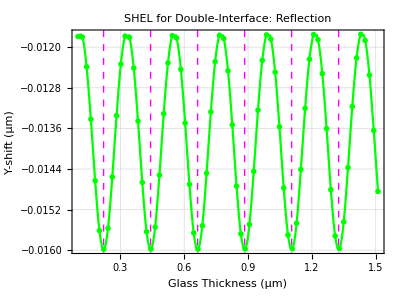

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

p$R3$y$points=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},InterpolationOrder->2,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

p$R3$y$curve=ListLinePlot[{R3y$plotdata},PlotMarkers->None,Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},InterpolationOrder->2,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

vmax = 0.0715;
vmin = 0.067;

p$R3$final$y=Show[p$R3$y$points,p$RT,p$R3$y$curve,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.2,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.2,vmin + 0.6(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.2,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin + ",14],{1.2,vmin + 0.4 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]}]
```

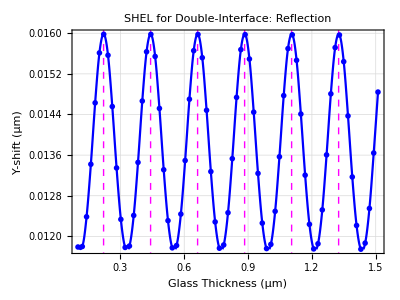

```mathematica
p$R4$y$points=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->False,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},InterpolationOrder->2,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

p$R4$y$curve=ListLinePlot[{R4y$plotdata},PlotMarkers->None,Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},InterpolationOrder->2,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

vmin = -0.0715;
vmax = -0.067;

p$R4$final$y=Show[p$R4$y$points,p$RT,p$R4$y$curve,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.2,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.2,vmin + 0.6(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.2,vmin + 0.5 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin - ",14],{1.2,vmin + 0.4 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]}]
```

#### Plot Graphics For Manuscript

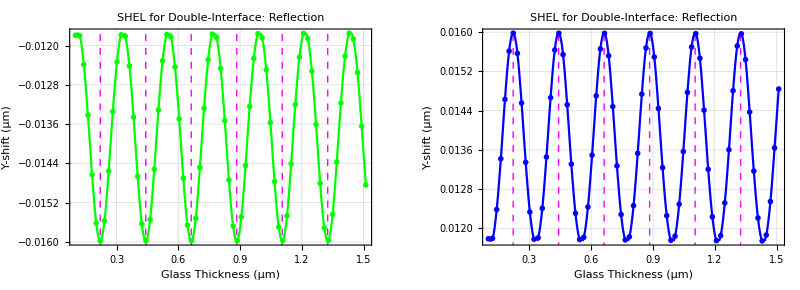

```mathematica
GraphicsRow[{p$R3$final$y,p$R4$final$y},ImageSize->800]
```

### Centroid Shifts versus Angle: n = 1.5168, L ~ 1.4 μm, Singular at 40 °, OAM = 5 (Glass Sheet) FIG 9

#### Ramsauer-Townsend Windows

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE/. {κx->0,κy->0};
```

```mathematica
Manipulate[ParametricPlot[{θ,Abs[ErB1$TE$func[n,θ Degree,L]]},{θ,10 ,80 },AspectRatio->1],{n,0.5,2},{L,0.1,20.0}]
```

```mathematica
params$here = {wk->20000.,n->1.5168,θ->40 Degree,k0->1,p->0,ℓ->0};

L$ram = {};

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,13.7}];
AppendTo[L$ram,L /. sol[[1]]];

L$ram

L$ram$units = Table[L$ram[[j]]/(2π/(632.8*10^-9))*10^6,{j,1,Length[L$ram]}]
```

FindRoot::nlnum: The function value {Abs[ErB1$TE]} is not a list of numbers with dimensions {1} at {L} = {13.7}.

ReplaceAll::reps: {Abs[ErB1$TE]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{L/.Abs[ErB1$TE]==0}

{0.100713 (L/.Abs[ErB1$TE]==0)}

```mathematica
Clear[p$ram] ;

Array[p$ram,Length[L$ram]];

Do[p$ram[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram[[j]],-10000},{L$ram[[j]],10000}}]}],{j,1,Length[L$ram]}]

p$ram$all = Show[Table[p$ram[j],{j,1,Length[L$ram]}]];

Array[p$ram$all,Length[L$ram]];

Do[p$ram$units[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram$units[[j]],-10000},{L$ram$units[[j]],10000}}]}],{j,1,Length[L$ram]}]
p$ram$units$all = Show[Table[p$ram$units[j],{j,1,Length[L$ram]}]];

p$ram$final = Show[Plot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]],{L,5,15}],p$ram$all]
```

ReplaceAll::reps: {Abs[ErB1$TE]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-

#### Analysis

```mathematica
Clear[plots,k0,β];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;


params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5,L->13.720088565627512};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here

Print["θ = ",θloop, "°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)


βtab = Table[ArcCos[κvec.nvec] /. params$here/.{κx->κtab[[i,j,1]],κy->κtab[[i,j,2]]},{i,1,dimset},{j,1,dimset}];

R1tab = Table[-ErB1$TM /.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];
R2tab = Table[ ErB1$TE/.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];


Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eRtab = Table[{(f[[1]]R1tab[[i,j]]-f[[2]]κtab[[i,j,2]] Cot[θR](R1tab[[i,j]]+R2tab[[i,j]])),f[[2]]R2tab[[i,j]] + f[[1]]κtab[[i,j,2]] Cot[θR](R1tab[[i,j]]+R2tab[[i,j]] ),-(f[[1]]R1tab[[i,j]] κtab[[i,j,1]] + f[[2]]R2tab[[i,j]]  κtab[[i,j,2]])}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,θloop,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,θloop,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,θloop,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,θloop,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{θloop,10.0,80.0,2.0}]
```

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5,L->13.720088565627512};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;
```

```mathematica
shift$tab$R4
```

shift$tab$R4

```mathematica
shift$tab$R1={{5,10.,{-0.14583076326020136,-0.06174180833768111}},{5,12.,{-0.17372464056627135,-0.019578320062168475}},{5,14.,{-0.20123613171861313,0.04925556123810649}},{5,16.,{-0.2285216929101743,0.14823167392375336}},{5,18.,{-0.25578971827414837,0.2817334221653129}},{5,20.,{-0.28326594315956377,0.4559094881400731}},{5,22.,{-0.31113922649589604,0.679792266631019}},{5,24.,{-0.33948725376926164,0.9668996763006168}},{5,26.,{-0.3681870400387404,1.337852678106504}},{5,28.,{-0.39682559031834735,1.8253443327348384}},{5,30.,{-0.4246420529654518,2.4850844480965755}},{5,32.,{-0.4505485089721533,3.4237793830176777}},{5,34.,{-0.47327636782867066,4.884706273541793}},{5,36.,{-0.4916581658959226,7.5927687055706405}},{5,38.,{-0.5049769455725301,15.171820450587013}},{5,40.,{-0.513239262751015,1.4150275067747842}},{5,42.,{-0.5172217235977962,-13.036127837015126}},{5,44.,{-0.5182456217453509,-5.300252779632439}},{5,46.,{-0.5177604367796089,-2.284835532689092}},{5,48.,{-0.5168933492927272,-0.27814823448699816}},{5,50.,{-0.516099623360488,1.634973524793198}},{5,52.,{-0.5149902991952215,4.205476355121417}},{5,54.,{-0.5123802451884565,9.586168393331686}},{5,56.,{-0.5065800854261798,46.9413176527297}},{5,58.,{-0.4959146756185191,-21.403822044677604}},{5,60.,{-0.4792973382733833,-8.765731431405985}},{5,62.,{-0.45666234838663283,-5.218657008949437}},{5,64.,{-0.4290198999554435,-3.406524421980764}},{5,66.,{-0.3981437369355538,-2.2314918950112053}},{5,68.,{-0.366091335939468,-1.35692579106909}},{5,70.,{-0.33479797332017946,-0.6327773622150276}},{5,72.,{-0.30588184111474326,0.033876405283120116}},{5,74.,{-0.2806724341515803,0.7261597652035778}},{5,76.,{-0.2604301085516428,1.5549965684709122}},{5,78.,{-0.24678930775002283,2.7358836629100534}},{5,80.,{-0.24269133262282186,4.869676681255413}}};
```

```mathematica
shift$tab$R2={{5,10.,{-0.14674923213115093,-0.28090722197555296}},{5,12.,{-0.17381329681618685,-0.28409734633694167}},{5,14.,{-0.19987988248583755,-0.2628380319192172}},{5,16.,{-0.22501246915335588,-0.21522525957925728}},{5,18.,{-0.24939430558957945,-0.13897451273430864}},{5,20.,{-0.2733448591111441,-0.03055510591976946}},{5,22.,{-0.29732865926885993,0.11604068977522833}},{5,24.,{-0.3219518338856136,0.31117368750617536}},{5,26.,{-0.34793828261027154,0.5726958611021056}},{5,28.,{-0.37607021801809104,0.9317756430226717}},{5,30.,{-0.40706537446289404,1.4450588316052266}},{5,32.,{-0.4413476376090438,2.2240284173470437}},{5,34.,{-0.4786625926932869,3.5214657893203585}},{5,36.,{-0.5175332469089621,6.075585903979792}},{5,38.,{-0.5547113238833669,13.522895086836437}},{5,40.,{-0.5850814167772088,-1.2186741307876212}},{5,42.,{-0.6026647213479327,-14.892339778863725}},{5,44.,{-0.6028954111501317,-7.299728807893002}},{5,46.,{-0.5849682826636685,-4.552127574499659}},{5,48.,{-0.5523606048295869,-3.058965820733443}},{5,50.,{-0.511054677522606,-2.1130449322955975}},{5,52.,{-0.4670211698201643,-1.4730116878021493}},{5,54.,{-0.4246511623285817,-1.0243490913916375}},{5,56.,{-0.38647841483014234,-0.7002238479407853}},{5,58.,{-0.35362319353788696,-0.45722159306823434}},{5,60.,{-0.3263786624106381,-0.2655059234521697}},{5,62.,{-0.304673198060541,-0.10349333827227139}},{5,64.,{-0.2883670090236817,0.04569778506648567}},{5,66.,{-0.27742607856378276,0.1970187440648178}},{5,68.,{-0.2720266801826848,0.3661211492702825}},{5,70.,{-0.27263236136719177,0.5726037458707425}},{5,72.,{-0.28007623082962274,0.8452411519038483}},{5,74.,{-0.2956859197592992,1.2324190720338595}},{5,76.,{-0.32152412555501186,1.8271154897007649}},{5,78.,{-0.3609378110503155,2.839924515997505}},{5,80.,{-0.4199943148892213,4.8816913738947}}};
```

```mathematica
shift$tab$R3={{5,10.,{-0.14630731445193837,-0.17504771014977913}},{5,12.,{-0.17377137765428163,-0.15832092568900857}},{5,14.,{-0.20050773767981173,-0.11724154464961467}},{5,16.,{-0.2265964826230747,-0.04949347914886381}},{5,18.,{-0.2521958180302315,0.04771715518767333}},{5,20.,{-0.2775388985414148,0.17843487531509936}},{5,22.,{-0.302924776085596,0.34902704602730983}},{5,24.,{-0.3287055916461378,0.5698244158494141}},{5,26.,{-0.3552737390087575,0.8579551508688888}},{5,28.,{-0.38305070923850315,1.2428567657966618}},{5,30.,{-0.41246619088664105,1.7782684094681511}},{5,32.,{-0.4438817635893436,2.571832395435332}},{5,34.,{-0.47736144306028466,3.872481531842347}},{5,36.,{-0.5121764776843243,6.416166567425785}},{5,38.,{-0.5460868271694245,13.840313651545003}},{5,40.,{-0.5748618712816662,-0.8076750620149098}},{5,42.,{-0.5928828417565835,-14.638977063597395}},{5,44.,{-0.5952571531143745,-7.074458534380556}},{5,46.,{-0.5803348365518691,-4.347425491171185}},{5,48.,{-0.550592407291613,-2.8686582074252462}},{5,50.,{-0.5112190685497572,-1.9359687620516874}},{5,52.,{-0.4678635823585184,-1.3148834906586395}},{5,54.,{-0.4251911038933169,-0.8969774559919533}},{5,56.,{-0.3865209841386512,-0.6176339533458014}},{5,58.,{-0.35390290970669597,-0.42954833566279654}},{5,60.,{-0.328157555265278,-0.2934400091812831}},{5,62.,{-0.30897274103635436,-0.17664015406275044}},{5,64.,{-0.2953203797562212,-0.05447750494184605}},{5,66.,{-0.2861238508159652,0.08991440294029085}},{5,68.,{-0.28081907193717387,0.2690597399095219}},{5,70.,{-0.27958742908169365,0.4969607776021937}},{5,72.,{-0.2833363840380023,0.7965844949313539}},{5,74.,{-0.29363498124637294,1.2113941421333854}},{5,76.,{-0.31278952884233596,1.8304466912437167}},{5,78.,{-0.34426287401362893,2.860980746273486}},{5,80.,{-0.3939385145199843,4.91016930782168}}};
```

```mathematica
shift$tab$R4={{5,10.,{-0.14630731441186415,-0.17586557485495968}},{5,12.,{-0.17377137765428163,-0.15972969882694435}},{5,14.,{-0.20050773774851033,-0.11947642184503575}},{5,16.,{-0.22659648274902217,-0.05283849113614078}},{5,18.,{-0.25219581828212645,0.042916310256938775}},{5,20.,{-0.27753889890208255,0.17175105061850937}},{5,22.,{-0.3029247765206873,0.3399247494840636}},{5,24.,{-0.3287055921957268,0.5576280196259176}},{5,26.,{-0.3552737394781981,0.8418187003543546}},{5,28.,{-0.38305070946177366,1.2217484003295105}},{5,30.,{-0.4124661905660475,1.750990178242308}},{5,32.,{-0.4438817624157422,2.5371008363662937}},{5,34.,{-0.47736144074170606,3.829086287667768}},{5,36.,{-0.5121764740203977,6.363192713717252}},{5,38.,{-0.5460868222689227,13.77736083544343}},{5,40.,{-0.5748618690833103,-0.8803850712809085}},{5,42.,{-0.5928828359858991,-14.72068821400311}},{5,44.,{-0.5952571481795234,-7.164158992584998}},{5,46.,{-0.5803348330711389,-4.4442060541276485}},{5,48.,{-0.5505924055684225,-2.9720015036031318}},{5,50.,{-0.5112190684925084,-2.045860618140537}},{5,52.,{-0.46786358337754796,-1.4316935955832608}},{5,54.,{-0.4251911051527917,-1.0211125875586509}},{5,56.,{-0.3865209848027379,-0.7490409538416344}},{5,58.,{-0.35390290912848255,-0.5672482897802299}},{5,60.,{-0.32815755319286954,-0.43533684670890205}},{5,62.,{-0.3089727376357725,-0.31974688176504396}},{5,64.,{-0.2953203756915526,-0.195457611112666}},{5,66.,{-0.2861238468600695,-0.04582783188819316}},{5,68.,{-0.2808190688514607,0.14107005141301912}},{5,70.,{-0.27958742755887417,0.3785314793809708}},{5,72.,{-0.2833363846276655,0.6888901705899663}},{5,74.,{-0.2936349845496318,1.1151275701455536}},{5,76.,{-0.31278953528855685,1.7459747653876057}},{5,78.,{-0.34426288422682433,2.7884714940005146}},{5,80.,{-0.3939385293588871,4.849682170020949}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

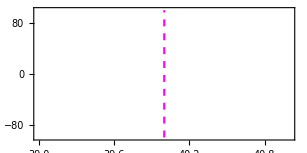

56.6038

```mathematica
p$RT=Show[Graphics[Table[{Magenta,Thickness[.005],Dashing->Small,Line[{{40,-100},{40,100}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5]

θbrewster = ArcTan[n]/Degree /. n->1.5168

p$brewster=Show[Graphics[Table[{Magenta,Thickness[.005],Dashing->Small,Line[{{θbrewster,-100},{θbrewster,100}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5];
```

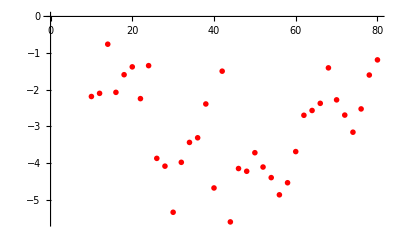

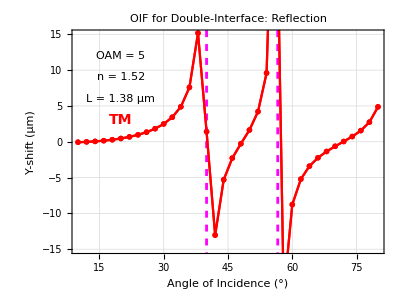

```mathematica
SetDirectory[NotebookDirectory[]];
cpp$data=Import["GH_shifts.tsv"];
cpp$plot=ListPlot[cpp$data,PlotMarkers->{Graphics[{Red,Disk[]}],.03},PlotStyle ->Red]

p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R1$final$y=Show[p$R1$y,p$RT,p$brewster,p$R1$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Red,Text[font["TM",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

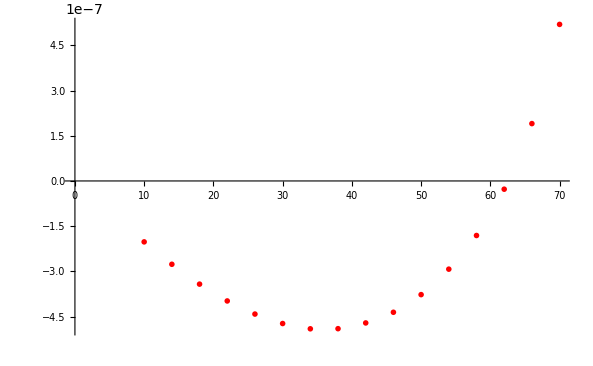

-Graphics-

```mathematica
gap
```

1.38179

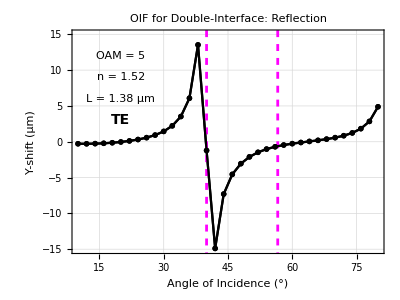

```mathematica
p$R2$y=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmin =-15;
vmax = 15;

p$R2$final$y=Show[p$R2$y,p$RT,p$brewster,p$R2$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

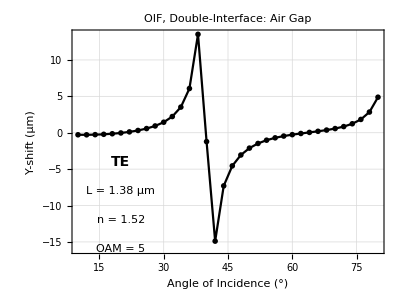

```mathematica
vmax =-20;
vmin = 20;

p$R2$y$zoom=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{20,80},{vmin,vmax}},PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF, Double-Interface: Air Gap",16]];

p$R2$final$y$zoom=Show[p$R2$y$zoom,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 1.38 μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14},PlotRange->{{10,80},{vmin,vmax}}]
```

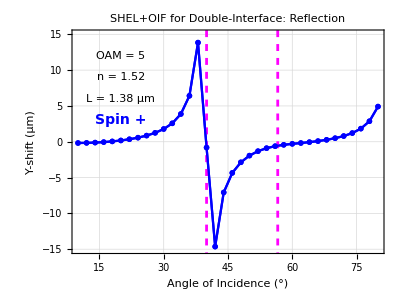

```mathematica
p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R3$final$y=Show[p$R3$y,p$RT,p$brewster,p$R3$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin + ",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

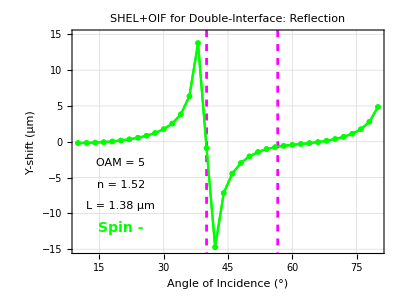

```mathematica
p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R4$final$y=Show[p$R4$y,p$RT,p$brewster,p$R4$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.4 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.3(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.2 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin - ",14],{20,vmin + 0.1 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

#### Plot Graphics For Manuscript

```mathematica
15./20
```

0.75

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE/. {κx->0,κy->0};
ErB1$TM$func[n_,θ_,L_]=ErB1$TM/. {κx->0,κy->0};
```

```mathematica
magfac = 20;

p$R=ParametricPlot[{{θ,magfac Abs[ErB1$TE$func[1.5168,θ Degree,13.720088565627512]]},{θ,magfac Abs[ErB1$TM$func[1.5168,θ Degree,13.720088565627512]]}},{θ,10 ,80 },AspectRatio->1,PlotStyle->{{Thickness[.004],Blue},{Thickness[.004],Orange}},BaseStyle->{"Tahoma",14}]
```

-Graphics-

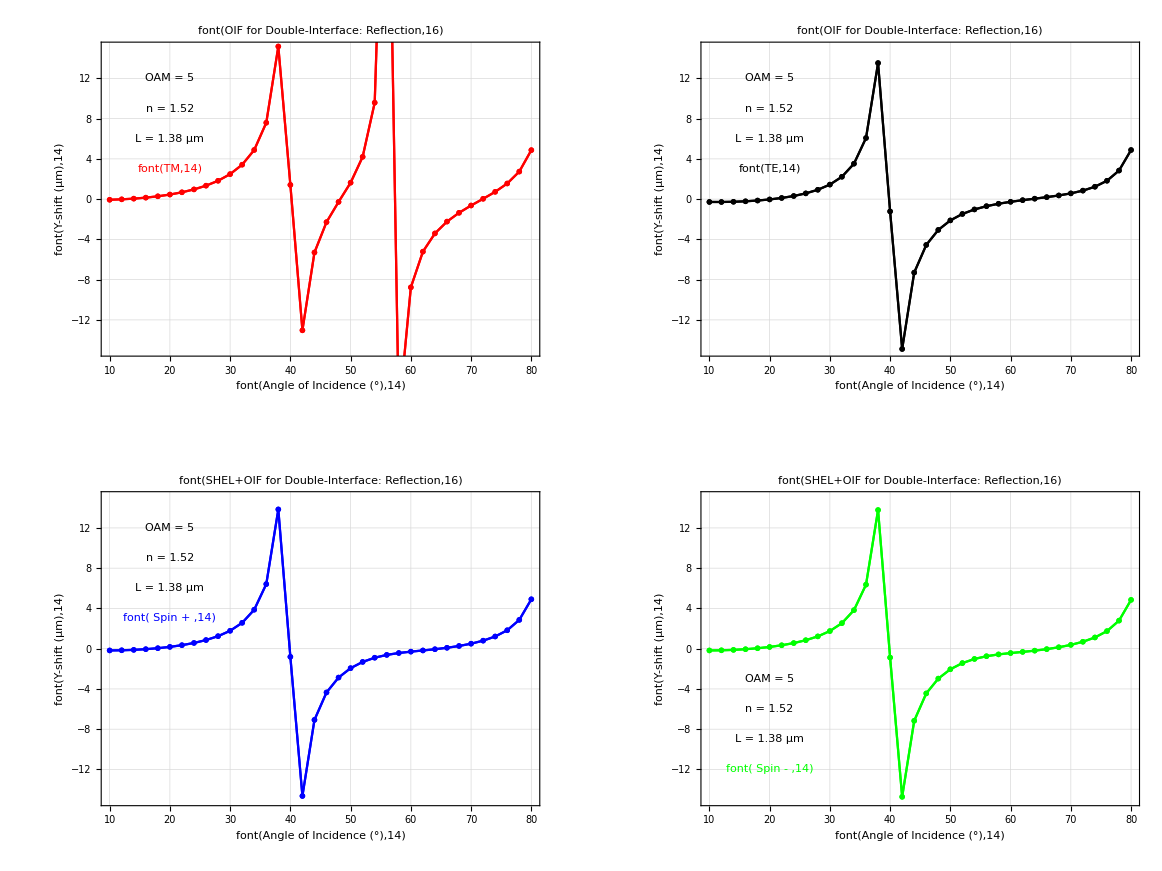

```mathematica
GraphicsGrid[{{Show[p$R1$final$y,p$R],Show[p$R2$final$y,p$R]},
{Show[p$R3$final$y,p$R],Show[p$R4$final$y,p$R]}},ImageSize->800]
```

### Centroid Shifts versus Angle: n = 1.5168, L ~ 2.0 μm, Singular at 40 °, OAM = 5 (Glass Sheet) FIG 9 comparison for M. S.

```mathematica
params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5,L->19.858360642160513};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here
```

2.

#### Ramsauer-Townsend Windows

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE/. {κx->0,κy->0};
```

```mathematica
Manipulate[ParametricPlot[{θ,Abs[ErB1$TE$func[n,θ Degree,L]]},{θ,10 ,80 },AspectRatio->1],{n,0.5,2},{L,0.1,20.0}]
```

```mathematica
params$here = {wk->20000.,n->1.5168,θ->40 Degree,k0->1,p->0,ℓ->0};

L$ram = {};

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,13.7}];
AppendTo[L$ram,L /. sol[[1]]];

L$ram

L$ram$units = Table[L$ram[[j]]/(2π/(632.8*10^-9))*10^6,{j,1,Length[L$ram]}]
```

{13.7201}

{1.38179}

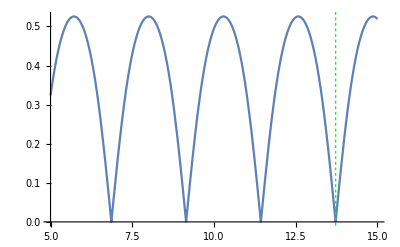

```mathematica
Clear[p$ram] ;

Array[p$ram,Length[L$ram]];

Do[p$ram[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram[[j]],-10000},{L$ram[[j]],10000}}]}],{j,1,Length[L$ram]}]

p$ram$all = Show[Table[p$ram[j],{j,1,Length[L$ram]}]];

Array[p$ram$all,Length[L$ram]];

Do[p$ram$units[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram$units[[j]],-10000},{L$ram$units[[j]],10000}}]}],{j,1,Length[L$ram]}]
p$ram$units$all = Show[Table[p$ram$units[j],{j,1,Length[L$ram]}]];

p$ram$final = Show[Plot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]],{L,5,15}],p$ram$all]
```

#### Analysis

```mathematica
Clear[plots,k0,β];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;


params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5,L->19.858360642160513};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

Print["θ = ",θloop, "°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)


βtab = Table[ArcCos[κvec.nvec] /. params$here/.{κx->κtab[[i,j,1]],κy->κtab[[i,j,2]]},{i,1,dimset},{j,1,dimset}];

R1tab = Table[-ErB1$TM /.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];
R2tab = Table[ ErB1$TE/.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];


Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eRtab = Table[{(f[[1]]R1tab[[i,j]]-f[[2]]κtab[[i,j,2]] Cot[θR](R1tab[[i,j]]+R2tab[[i,j]])),f[[2]]R2tab[[i,j]] + f[[1]]κtab[[i,j,2]] Cot[θR](R1tab[[i,j]]+R2tab[[i,j]] ),-(f[[1]]R1tab[[i,j]] κtab[[i,j,1]] + f[[2]]R2tab[[i,j]]  κtab[[i,j,2]])}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,θloop,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,θloop,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,θloop,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,θloop,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{θloop,10.0,80.0,2.0}]
```

θ = 10.°

TM (Reflected) = {-0.210279,0.0366605} μm

TE (Reflected) = {-0.209428,-0.181784} μm

spin+ (Reflected) = {-0.209838,-0.076243} μm

spin- (Reflected) = {-0.209838,-0.0770453} μm

θ = 12.°

TM (Reflected) = {-0.251316,0.147527} μm

TE (Reflected) = {-0.248757,-0.118662} μm

spin+ (Reflected) = {-0.249968,0.00793701} μm

spin- (Reflected) = {-0.249968,0.00654578} μm

θ = 14.°

TM (Reflected) = {-0.292602,0.31407} μm

TE (Reflected) = {-0.287579,-0.00489536} μm

spin+ (Reflected) = {-0.289904,0.143887} μm

spin- (Reflected) = {-0.289904,0.141655} μm

θ = 16.°

TM (Reflected) = {-0.334679,0.550536} μm

TE (Reflected) = {-0.326566,0.170767} μm

spin+ (Reflected) = {-0.330225,0.343752} μm

spin- (Reflected) = {-0.330225,0.340352} μm

θ = 18.°

TM (Reflected) = {-0.378103,0.879478} μm

TE (Reflected) = {-0.366703,0.42738} μm

spin+ (Reflected) = {-0.371684,0.627399} μm

spin- (Reflected) = {-0.371684,0.622402} μm

θ = 20.°

TM (Reflected) = {-0.423252,1.33875} μm

TE (Reflected) = {-0.409248,0.799496} μm

spin+ (Reflected) = {-0.415132,1.02967} μm

spin- (Reflected) = {-0.415132,1.02251} μm

θ = 22.°

TM (Reflected) = {-0.470039,1.99583} μm

TE (Reflected) = {-0.455565,1.35293} μm

spin+ (Reflected) = {-0.461362,1.61546} μm

spin- (Reflected) = {-0.461362,1.60538} μm

θ = 24.°

TM (Reflected) = {-0.517584,2.98358} μm

TE (Reflected) = {-0.506752,2.22305} μm

spin+ (Reflected) = {-0.510842,2.51716} μm

spin- (Reflected) = {-0.510842,2.50322} μm

θ = 26.°

TM (Reflected) = {-0.563959,4.61389} μm

TE (Reflected) = {-0.562898,3.7317} μm

spin+ (Reflected) = {-0.563271,4.05106} μm

spin- (Reflected) = {-0.563271,4.03217} μm

θ = 28.°

TM (Reflected) = {-0.606265,7.88356} μm

TE (Reflected) = {-0.621911,6.89515} μm

spin+ (Reflected) = {-0.616866,7.22629} μm

spin- (Reflected) = {-0.616866,7.20139} μm

θ = 30.°

TM (Reflected) = {-0.641316,18.9746} μm

TE (Reflected) = {-0.678236,17.9207} μm

spin+ (Reflected) = {-0.667443,18.2446} μm

spin- (Reflected) = {-0.667443,18.2129} μm

θ = 32.°

TM (Reflected) = {-0.666898,-61.2899} μm

TE (Reflected) = {-0.722769,-62.351} μm

spin+ (Reflected) = {-0.708078,-62.0526} μm

spin- (Reflected) = {-0.708078,-62.0914} μm

θ = 34.°

TM (Reflected) = {-0.682969,-10.8813} μm

TE (Reflected) = {-0.745772,-11.9061} μm

spin+ (Reflected) = {-0.730953,-11.6416} μm

spin- (Reflected) = {-0.730953,-11.6869} μm

θ = 36.°

TM (Reflected) = {-0.691992,-5.1761} μm

TE (Reflected) = {-0.742592,-6.16758} μm

spin+ (Reflected) = {-0.731871,-5.93193} μm

spin- (Reflected) = {-0.731871,-5.98308} μm

θ = 38.°

TM (Reflected) = {-0.697971,-2.69327} μm

TE (Reflected) = {-0.717426,-3.7214} μm

spin+ (Reflected) = {-0.713735,-3.4982} μm

spin- (Reflected) = {-0.713735,-3.55447} μm

θ = 40.°

TM (Reflected) = {-0.704849,-1.10745} μm

TE (Reflected) = {-0.681216,-2.29781} μm

spin+ (Reflected) = {-0.685176,-2.06769} μm

spin- (Reflected) = {-0.685176,-2.12905} μm

θ = 42.°

TM (Reflected) = {-0.715054,0.169073} μm

TE (Reflected) = {-0.646154,-1.34407} μm

spin+ (Reflected) = {-0.656032,-1.09344} μm

spin- (Reflected) = {-0.656032,-1.16083} μm

θ = 44.°

TM (Reflected) = {-0.72867,1.39835} μm

TE (Reflected) = {-0.622072,-0.622298} μm

spin+ (Reflected) = {-0.634457,-0.349887} μm

spin- (Reflected) = {-0.634457,-0.425174} μm

θ = 46.°

TM (Reflected) = {-0.743376,2.76758} μm

TE (Reflected) = {-0.616243,0.0260477} μm

spin+ (Reflected) = {-0.627263,0.306448} μm

spin- (Reflected) = {-0.627263,0.220917} μm

θ = 48.°

TM (Reflected) = {-0.755272,4.48915} μm

TE (Reflected) = {-0.634855,0.762262} μm

spin+ (Reflected) = {-0.641774,1.02524} μm

spin- (Reflected) = {-0.641774,0.927569} μm

θ = 50.°

TM (Reflected) = {-0.760585,6.9372} μm

TE (Reflected) = {-0.684008,1.83896} μm

spin+ (Reflected) = {-0.68648,2.05861} μm

spin- (Reflected) = {-0.68648,1.94844} μm

θ = 52.°

TM (Reflected) = {-0.757612,11.079} μm

TE (Reflected) = {-0.76769,3.83032} μm

spin+ (Reflected) = {-0.767547,3.99392} μm

spin- (Reflected) = {-0.767547,3.87294} μm

θ = 54.°

TM (Reflected) = {-0.747604,20.7948} μm

TE (Reflected) = {-0.87821,8.73538} μm

spin+ (Reflected) = {-0.877685,8.84817} μm

spin- (Reflected) = {-0.877685,8.71962} μm

θ = 56.°

TM (Reflected) = {-0.733817,87.4307} μm

TE (Reflected) = {-0.977835,38.9734} μm

spin+ (Reflected) = {-0.977788,39.0492} μm

spin- (Reflected) = {-0.977788,38.9165} μm

θ = 58.°

TM (Reflected) = {-0.719253,-43.8263} μm

TE (Reflected) = {-1.00001,-22.7541} μm

spin+ (Reflected) = {-0.99972,-22.7086} μm

spin- (Reflected) = {-0.99972,-22.8432} μm

θ = 60.°

TM (Reflected) = {-0.704662,-17.453} μm

TE (Reflected) = {-0.912457,-7.86999} μm

spin+ (Reflected) = {-0.911065,-7.86629} μm

spin- (Reflected) = {-0.911065,-8.00202} μm

θ = 62.°

TM (Reflected) = {-0.68754,-10.6316} μm

TE (Reflected) = {-0.760505,-3.87107} μm

spin+ (Reflected) = {-0.759058,-3.93661} μm

spin- (Reflected) = {-0.759058,-4.07367} μm

θ = 64.°

TM (Reflected) = {-0.662926,-7.34857} μm

TE (Reflected) = {-0.606237,-2.10127} μm

spin+ (Reflected) = {-0.60873,-2.26284} μm

spin- (Reflected) = {-0.60873,-2.40126} μm

θ = 66.°

TM (Reflected) = {-0.62572,-5.33381} μm

TE (Reflected) = {-0.477877,-1.21791} μm

spin+ (Reflected) = {-0.489774,-1.47984} μm

spin- (Reflected) = {-0.489774,-1.61835} μm

θ = 68.°

TM (Reflected) = {-0.5734,-3.94543} μm

TE (Reflected) = {-0.377571,-0.749268} μm

spin+ (Reflected) = {-0.402309,-1.0851} μm

spin- (Reflected) = {-0.402309,-1.22094} μm

θ = 70.°

TM (Reflected) = {-0.507219,-2.94708} μm

TE (Reflected) = {-0.29883,-0.489533} μm

spin+ (Reflected) = {-0.335439,-0.8564} μm

spin- (Reflected) = {-0.335439,-0.986128} μm

θ = 72.°

TM (Reflected) = {-0.430977,-2.23225} μm

TE (Reflected) = {-0.234452,-0.342797} μm

spin+ (Reflected) = {-0.278287,-0.703991} μm

spin- (Reflected) = {-0.278287,-0.824488} μm

θ = 74.°

TM (Reflected) = {-0.348511,-1.73946} μm

TE (Reflected) = {-0.178447,-0.262736} μm

spin+ (Reflected) = {-0.223602,-0.600309} μm

spin- (Reflected) = {-0.223602,-0.709359} μm

θ = 76.°

TM (Reflected) = {-0.261689,-1.42557} μm

TE (Reflected) = {-0.126036,-0.226177} μm

spin+ (Reflected) = {-0.167102,-0.541121} μm

spin- (Reflected) = {-0.167102,-0.637417} μm

θ = 78.°

TM (Reflected) = {-0.169544,-1.25724} μm

TE (Reflected) = {-0.0733496,-0.220265} μm

spin+ (Reflected) = {-0.105668,-0.527208} μm

spin- (Reflected) = {-0.105668,-0.610116} μm

θ = 80.°

TM (Reflected) = {-0.0682571,-1.20386} μm

TE (Reflected) = {-0.0174195,-0.234749} μm

spin+ (Reflected) = {-0.0360914,-0.556053} μm

spin- (Reflected) = {-0.0360914,-0.625329} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5,L->19.858360642160513};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;
```

```mathematica
shift$tab$R3
```

{{5,10.,{-0.209838,-0.076243}},{5,12.,{-0.249968,0.00793701}},{5,14.,{-0.289904,0.143887}},{5,16.,{-0.330225,0.343752}},{5,18.,{-0.371684,0.627399}},{5,20.,{-0.415132,1.02967}},{5,22.,{-0.461362,1.61546}},{5,24.,{-0.510842,2.51716}},{5,26.,{-0.563271,4.05106}},{5,28.,{-0.616866,7.22629}},{5,30.,{-0.667443,18.2446}},{5,32.,{-0.708078,-62.0526}},{5,34.,{-0.730953,-11.6416}},{5,36.,{-0.731871,-5.93193}},{5,38.,{-0.713735,-3.4982}},{5,40.,{-0.685176,-2.06769}},{5,42.,{-0.656032,-1.09344}},{5,44.,{-0.634457,-0.349887}},{5,46.,{-0.627263,0.306448}},{5,48.,{-0.641774,1.02524}},{5,50.,{-0.68648,2.05861}},{5,52.,{-0.767547,3.99392}},{5,54.,{-0.877685,8.84817}},{5,56.,{-0.977788,39.0492}},{5,58.,{-0.99972,-22.7086}},{5,60.,{-0.911065,-7.86629}},{5,62.,{-0.759058,-3.93661}},{5,64.,{-0.60873,-2.26284}},{5,66.,{-0.489774,-1.47984}},{5,68.,{-0.402309,-1.0851}},{5,70.,{-0.335439,-0.8564}},{5,72.,{-0.278287,-0.703991}},{5,74.,{-0.223602,-0.600309}},{5,76.,{-0.167102,-0.541121}},{5,78.,{-0.105668,-0.527208}},{5,80.,{-0.0360914,-0.556053}}}

```mathematica
shift$tab$R1={{5,10.,{-0.21027868956994916,0.036660523260778836}},{5,12.,{-0.25131624241586586,0.14752721151436693}},{5,14.,{-0.292601669429408,0.3140699287944442}},{5,16.,{-0.33467854601193114,0.5505363941604361}},{5,18.,{-0.3781032169444418,0.8794776553544872}},{5,20.,{-0.4232518144014249,1.338748682395706}},{5,22.,{-0.47003887643578834,1.9958252374265688}},{5,24.,{-0.5175842024531588,2.983578713620429}},{5,26.,{-0.5639588949166362,4.613893722112941}},{5,28.,{-0.6062645498766409,7.883564341368544}},{5,30.,{-0.6413155535631451,18.974564834714055}},{5,32.,{-0.666897666190895,-61.289903308219664}},{5,34.,{-0.6829691861951525,-10.881263587282083}},{5,36.,{-0.6919920900170503,-5.1760974953873395}},{5,38.,{-0.6979710377481317,-2.693269235778332}},{5,40.,{-0.704849390665176,-1.1074454073515594}},{5,42.,{-0.7150543346975362,0.16907254339632113}},{5,44.,{-0.7286701677341932,1.3983542422461752}},{5,46.,{-0.743376026130089,2.767577202760395}},{5,48.,{-0.7552716111845237,4.4891502708823054}},{5,50.,{-0.7605852234182728,6.937201698422166}},{5,52.,{-0.7576121444707823,11.078969148589115}},{5,54.,{-0.7476038237092911,20.794791337580506}},{5,56.,{-0.7338172399505068,87.43066458955657}},{5,58.,{-0.7192530745277408,-43.82625318659835}},{5,60.,{-0.7046623839135795,-17.452980035996376}},{5,62.,{-0.6875395620466422,-10.631591652307375}},{5,64.,{-0.6629261290264559,-7.348570699324265}},{5,66.,{-0.6257203065498215,-5.333807226415067}},{5,68.,{-0.5733995895640167,-3.9454262533008584}},{5,70.,{-0.5072191426406966,-2.947081794770381}},{5,72.,{-0.4309771751249628,-2.232253539647779}},{5,74.,{-0.34851133222313363,-1.7394625644810568}},{5,76.,{-0.261688718639815,-1.42557224961325}},{5,78.,{-0.16954358051589563,-1.2572418835869985}},{5,80.,{-0.06825711962595915,-1.2038649149053258}}};
```

```mathematica
shift$tab$R2={{5,10.,{-0.2094282999420127,-0.18178441799380923}},{5,12.,{-0.24875721027036932,-0.11866172261788101}},{5,14.,{-0.28757923014813286,-0.004895360154254761}},{5,16.,{-0.32656567097129846,0.1707671770851044}},{5,18.,{-0.36670309963717757,0.4273804988898694}},{5,20.,{-0.40924795894119964,0.7994955661343546}},{5,22.,{-0.4555653845751345,1.3529311302397535}},{5,24.,{-0.5067517930056429,2.2230548623126265}},{5,26.,{-0.5628977843502831,3.7316971178699436}},{5,28.,{-0.6219107016086293,6.89515439238952}},{5,30.,{-0.6782356159778443,17.92073671042628}},{5,32.,{-0.7227687589722376,-62.350994507302815}},{5,34.,{-0.745771887587893,-11.906087037257272}},{5,36.,{-0.7425921847677035,-6.167577250140729}},{5,38.,{-0.7174257303654985,-3.7213977435427372}},{5,40.,{-0.6812161938953933,-2.2978113125643795}},{5,42.,{-0.6461539163124113,-1.344069637001}},{5,44.,{-0.6220715368694215,-0.6222976808607654}},{5,46.,{-0.6162429350294916,0.0260476681925107}},{5,48.,{-0.6348552260602099,0.7622620644324882}},{5,50.,{-0.6840078903674927,1.838960360274475}},{5,52.,{-0.767690375350867,3.83032266625145}},{5,54.,{-0.8782102780566822,8.735375578196921}},{5,56.,{-0.9778354000345476,38.973378875693854}},{5,58.,{-1.0000096943090255,-22.75412242499782}},{5,60.,{-0.9124567881889792,-7.869988595364461}},{5,62.,{-0.7605051100598077,-3.871074266049546}},{5,64.,{-0.6062367784349559,-2.101265891153661}},{5,66.,{-0.47787740626336583,-1.2179109461225421}},{5,68.,{-0.3775711324527928,-0.7492684344963823}},{5,70.,{-0.2988304775770836,-0.48953252554682253}},{5,72.,{-0.23445191814583474,-0.3427972996281759}},{5,74.,{-0.17844692279815866,-0.2627355028294512}},{5,76.,{-0.1260359058161848,-0.22617684150892525}},{5,78.,{-0.07334963931254251,-0.22026547808734465}},{5,80.,{-0.017419492008886924,-0.2347485201845484}}};
```

```mathematica
shift$tab$R3={{5,10.,{-0.20983760296089166,-0.0762430258352124}},{5,12.,{-0.24996759156005766,0.007937005000086612}},{5,14.,{-0.2899043884876756,0.14388709103081315}},{5,16.,{-0.33022476327260386,0.3437516183436888}},{5,18.,{-0.3716837833680457,0.6273989938052098}},{5,20.,{-0.41513237248221574,1.0296719998659487}},{5,22.,{-0.46136228882411345,1.6154638976245022}},{5,24.,{-0.5108415178689076,2.5171585488583514}},{5,26.,{-0.563270552925635,4.05105566886337}},{5,28.,{-0.6168660782878879,7.226286257017547}},{5,30.,{-0.667443148173715,18.24464114041813}},{5,32.,{-0.7080783087502922,-62.05263147321455}},{5,34.,{-0.7309534115375381,-11.641604966834835}},{5,36.,{-0.7318712101274623,-5.931932366762466}},{5,38.,{-0.7137346430826235,-3.49820163077919}},{5,40.,{-0.6851758503827572,-2.067693734008866}},{5,42.,{-0.6560319952626001,-1.0934432666834148}},{5,44.,{-0.6344565899110416,-0.3498869779284808}},{5,46.,{-0.6272627937679658,0.3064480426426609}},{5,48.,{-0.6417741426237081,1.02523617254823}},{5,50.,{-0.6864797297956616,2.058613747715908}},{5,52.,{-0.7675470189035289,3.9939203524575353}},{5,54.,{-0.8776848329893567,8.84816510735069}},{5,56.,{-0.9777875105671923,39.04924899728538}},{5,58.,{-0.9997195620777326,-22.70859435411145}},{5,60.,{-0.9110654380754898,-7.866290114369269}},{5,62.,{-0.759058146068645,-3.936608069804384}},{5,64.,{-0.6087300952570941,-2.262843041560305}},{5,66.,{-0.48977364159035164,-1.4798424492321205}},{5,68.,{-0.40230895133914096,-1.0850970685364485}},{5,70.,{-0.33543929618096907,-0.8564002175038448}},{5,72.,{-0.2782867982149014,-0.7039910406242482}},{5,74.,{-0.22360217499353358,-0.6003091294492225}},{5,76.,{-0.16710200698217706,-0.5411208644888688}},{5,78.,{-0.1056682504481652,-0.5272084576543575}},{5,80.,{-0.03609141934194116,-0.5560527801269209}}};
```

```mathematica
shift$tab$R4={{5,10.,{-0.20983760299524096,-0.07704531400901451}},{5,12.,{-0.24996759165738075,0.006545777318995066}},{5,14.,{-0.28990438869377144,0.14165471243297442}},{5,16.,{-0.33022476354167346,0.34035196422650116}},{5,18.,{-0.3716837837287134,0.6224023304824108}},{5,20.,{-0.4151323728257088,1.0225069625584322}},{5,22.,{-0.46136228894433606,1.6053806024478714}},{5,24.,{-0.5108415174910653,2.5032155013383215}},{5,26.,{-0.5632705516031865,4.0321695014247325}},{5,28.,{-0.6168660755399429,7.201387846258181}},{5,30.,{-0.6674431438972257,18.21294220167459}},{5,32.,{-0.7080783032715768,-62.09136199854729}},{5,34.,{-0.7309534058183776,-11.686948997193003}},{5,36.,{-0.7318712053529078,-5.983079375656155}},{5,38.,{-0.7137346403175038,-3.554465514796415}},{5,40.,{-0.685175849941941,-2.129045926716013}},{5,42.,{-0.6560319968083193,-1.160825228651999}},{5,44.,{-0.6344565925502138,-0.4251735743516539}},{5,46.,{-0.6272627961151688,0.22091728350516138}},{5,48.,{-0.6417741433622184,0.9275690384823838}},{5,50.,{-0.6864797282728422,1.9484390965633893}},{5,52.,{-0.7675470155659208,3.872942207526293}},{5,54.,{-0.8776848296116744,8.719619247634528}},{5,56.,{-0.9777875094737393,38.91652880569607}},{5,58.,{-0.9997195647569789,-22.843201928372885}},{5,60.,{-0.911065443954947,-8.002018426940692}},{5,62.,{-0.7590581528411844,-4.073672547857801}},{5,64.,{-0.6087301002377444,-2.401264198665164}},{5,66.,{-0.4897736429643242,-1.618353806473974}},{5,68.,{-0.40230894885454066,-1.2209421464303103}},{5,70.,{-0.3354392907824022,-0.9861280044441304}},{5,72.,{-0.278286791396563,-0.8244884122894387}},{5,74.,{-0.22360216798054905,-0.709358615999332}},{5,76.,{-0.16710200057030547,-0.6374173817546721}},{5,78.,{-0.10566824503814858,-0.6101155397277136}},{5,80.,{-0.036091415248648145,-0.6253291280599389}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

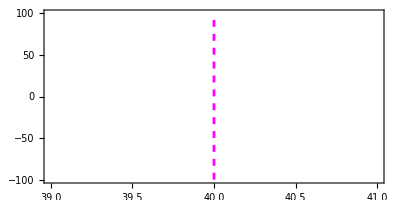

56.6038

```mathematica
p$RT=Show[Graphics[Table[{Magenta,Thickness[.005],Dashing->Small,Line[{{40,-100},{40,100}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5]

θbrewster = ArcTan[n]/Degree /. n->1.5168

p$brewster=Show[Graphics[Table[{Magenta,Thickness[.005],Dashing->Small,Line[{{θbrewster,-100},{θbrewster,100}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5];
```

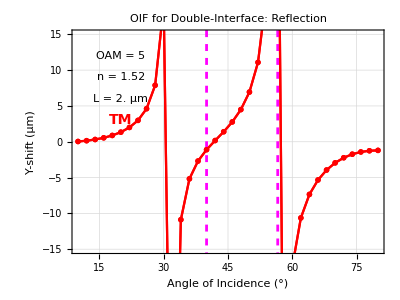

```mathematica
p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R1$final$y=Show[p$R1$y,p$RT,p$brewster,p$R1$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Red,Text[font["TM",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

```mathematica
gap
```

2.

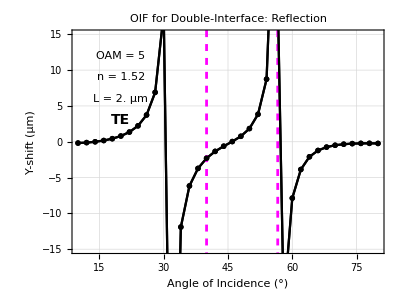

```mathematica
p$R2$y=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmin =-15;
vmax = 15;

p$R2$final$y=Show[p$R2$y,p$RT,p$brewster,p$R2$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

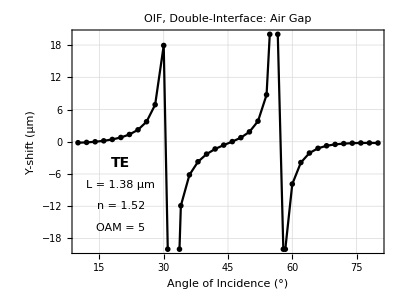

```mathematica
vmax =-20;
vmin = 20;

p$R2$y$zoom=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{20,80},{vmin,vmax}},PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF, Double-Interface: Air Gap",16]];

p$R2$final$y$zoom=Show[p$R2$y$zoom,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 1.38 μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14},PlotRange->{{10,80},{vmin,vmax}}]
```

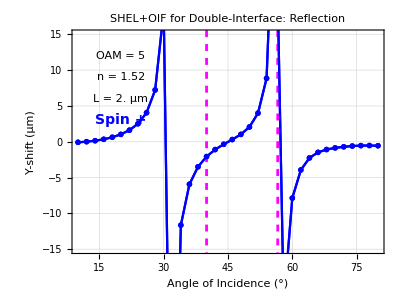

```mathematica
p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R3$final$y=Show[p$R3$y,p$RT,p$brewster,p$R3$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin + ",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

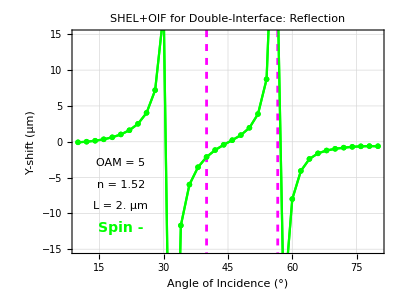

```mathematica
p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R4$final$y=Show[p$R4$y,p$RT,p$brewster,p$R4$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.4 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.3(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.2 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin - ",14],{20,vmin + 0.1 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

#### Plot Graphics For Mark Siemens

```mathematica
15./20
```

0.75

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE/. {κx->0,κy->0};
ErB1$TM$func[n_,θ_,L_]=ErB1$TM/. {κx->0,κy->0};
```

```mathematica
magfac = 20;

p$R=ParametricPlot[{{θ,magfac Abs[ErB1$TE$func[1.5168,θ Degree,13.720088565627512]]},{θ,magfac Abs[ErB1$TM$func[1.5168,θ Degree,13.720088565627512]]}},{θ,10 ,80 },AspectRatio->1,PlotStyle->{{Thickness[.004],Blue},{Thickness[.004],Orange}},BaseStyle->{"Tahoma",14}]
```

-Graphics-

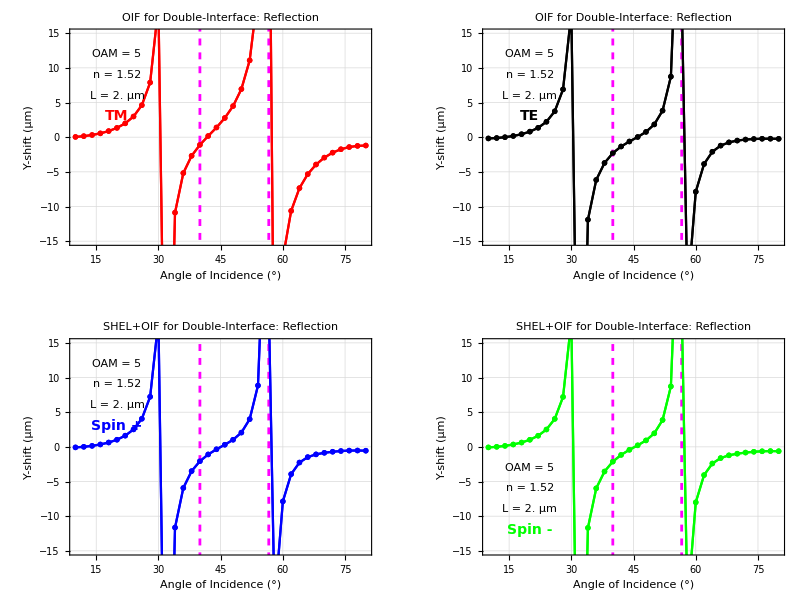

```mathematica
GraphicsGrid[{{Show[p$R1$final$y,p$R],Show[p$R2$final$y,p$R]},
{Show[p$R3$final$y,p$R],Show[p$R4$final$y,p$R]}},ImageSize->800]
```

### Centroid Shifts versus Angle: n = 1.5168, L ~ 1.4 μm, Singular at 40 °, OAM = 5 (Glass Sheet) FIG 9 ZOOM IN DETAIL

#### Ramsauer-Townsend Windows

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE/. {κx->0,κy->0};
```

```mathematica
Manipulate[ParametricPlot[{θ,Abs[ErB1$TE$func[n,θ Degree,L]]},{θ,10 ,80 },AspectRatio->1],{n,0.5,2},{L,0.1,20.0}]
```

```mathematica
params$here = {wk->20000.,n->1.5168,θ->40 Degree,k0->1,p->0,ℓ->0};

L$ram = {};

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,13.7}];
AppendTo[L$ram,L /. sol[[1]]];

L$ram

L$ram$units = Table[L$ram[[j]]/(2π/(632.8*10^-9))*10^6,{j,1,Length[L$ram]}]
```

{13.7201}

{1.38179}

```mathematica
Clear[p$ram] ;

Array[p$ram,Length[L$ram]];

Do[p$ram[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram[[j]],-10000},{L$ram[[j]],10000}}]}],{j,1,Length[L$ram]}]

p$ram$all = Show[Table[p$ram[j],{j,1,Length[L$ram]}]];

Array[p$ram$all,Length[L$ram]];

Do[p$ram$units[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram$units[[j]],-10000},{L$ram$units[[j]],10000}}]}],{j,1,Length[L$ram]}]
p$ram$units$all = Show[Table[p$ram$units[j],{j,1,Length[L$ram]}]];

p$ram$final = Show[Plot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]],{L,5,15}],p$ram$all]
```

-Graphics-

#### Analysis

```mathematica
Clear[plots,k0,β];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;


params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5,L->13.720088565627512};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

Print["θ = ",θloop, "°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)


βtab = Table[ArcCos[κvec.nvec] /. params$here/.{κx->κtab[[i,j,1]],κy->κtab[[i,j,2]]},{i,1,dimset},{j,1,dimset}];

R1tab = Table[-ErB1$TM /.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];
R2tab = Table[ ErB1$TE/.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];


Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eRtab = Table[{(f[[1]]R1tab[[i,j]]-f[[2]]κtab[[i,j,2]] Cot[θR](R1tab[[i,j]]+R2tab[[i,j]])),f[[2]]R2tab[[i,j]] + f[[1]]κtab[[i,j,2]] Cot[θR](R1tab[[i,j]]+R2tab[[i,j]] ),-(f[[1]]R1tab[[i,j]] κtab[[i,j,1]] + f[[2]]R2tab[[i,j]]  κtab[[i,j,2]])}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,θloop,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,θloop,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,θloop,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,θloop,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{θloop,36.0,44.0,0.2}]
```

θ = 36.°

TM (Reflected) = {-0.491658,7.59277} μm

TE (Reflected) = {-0.517533,6.07559} μm

spin+ (Reflected) = {-0.512176,6.41617} μm

spin- (Reflected) = {-0.512176,6.36319} μm

θ = 36.2°

TM (Reflected) = {-0.493224,8.00558} μm

TE (Reflected) = {-0.521398,6.47406} μm

spin+ (Reflected) = {-0.515662,6.81285} μm

spin- (Reflected) = {-0.515662,6.75889} μm

θ = 36.4°

TM (Reflected) = {-0.494738,8.46117} μm

TE (Reflected) = {-0.525243,6.91556} μm

spin+ (Reflected) = {-0.519137,7.25243} μm

spin- (Reflected) = {-0.519137,7.19747} μm

θ = 36.6°

TM (Reflected) = {-0.496201,8.96701} μm

TE (Reflected) = {-0.529064,7.40755} μm

spin+ (Reflected) = {-0.522598,7.74238} μm

spin- (Reflected) = {-0.522598,7.68642} μm

θ = 36.8°

TM (Reflected) = {-0.497611,9.53246} μm

TE (Reflected) = {-0.532857,7.95941} μm

spin+ (Reflected) = {-0.526041,8.29207} μm

spin- (Reflected) = {-0.526041,8.23512} μm

θ = 37.°

TM (Reflected) = {-0.498969,10.1694} μm

TE (Reflected) = {-0.536615,8.58298} μm

spin+ (Reflected) = {-0.529462,8.91336} μm

spin- (Reflected) = {-0.529462,8.85541} μm

θ = 37.2°

TM (Reflected) = {-0.500275,10.8929} μm

TE (Reflected) = {-0.540334,9.2935} μm

spin+ (Reflected) = {-0.532857,9.62149} μm

spin- (Reflected) = {-0.532857,9.56254} μm

θ = 37.4°

TM (Reflected) = {-0.501528,11.7231} μm

TE (Reflected) = {-0.544009,10.1109} μm

spin+ (Reflected) = {-0.536222,10.4364} μm

spin- (Reflected) = {-0.536222,10.3764} μm

θ = 37.6°

TM (Reflected) = {-0.50273,12.6864} μm

TE (Reflected) = {-0.547634,11.0617} μm

spin+ (Reflected) = {-0.539552,11.3846} μm

spin- (Reflected) = {-0.539552,11.3236} μm

θ = 37.8°

TM (Reflected) = {-0.503879,13.8191} μm

TE (Reflected) = {-0.551203,12.1821} μm

spin+ (Reflected) = {-0.542842,12.5023} μm

spin- (Reflected) = {-0.542842,12.4404} μm

θ = 38.°

TM (Reflected) = {-0.504977,15.1718} μm

TE (Reflected) = {-0.554711,13.5229} μm

spin+ (Reflected) = {-0.546087,13.8403} μm

spin- (Reflected) = {-0.546087,13.7774} μm

θ = 38.2°

TM (Reflected) = {-0.506024,16.8178} μm

TE (Reflected) = {-0.558152,15.1572} μm

spin+ (Reflected) = {-0.549282,15.4717} μm

spin- (Reflected) = {-0.549282,15.4078} μm

θ = 38.4°

TM (Reflected) = {-0.507019,18.8669} μm

TE (Reflected) = {-0.56152,17.1948} μm

spin+ (Reflected) = {-0.552421,17.5065} μm

spin- (Reflected) = {-0.552421,17.4415} μm

θ = 38.6°

TM (Reflected) = {-0.507965,21.4916} μm

TE (Reflected) = {-0.564808,19.8084} μm

spin+ (Reflected) = {-0.5555,20.117} μm

spin- (Reflected) = {-0.5555,20.0511} μm

θ = 38.8°

TM (Reflected) = {-0.508861,24.9796} μm

TE (Reflected) = {-0.568011,23.2855} μm

spin+ (Reflected) = {-0.558512,23.591} μm

spin- (Reflected) = {-0.558512,23.5241} μm

θ = 39.°

TM (Reflected) = {-0.509708,29.8484} μm

TE (Reflected) = {-0.571122,28.1438} μm

spin+ (Reflected) = {-0.561452,28.4461} μm

spin- (Reflected) = {-0.561452,28.3782} μm

θ = 39.2°

TM (Reflected) = {-0.510507,37.1333} μm

TE (Reflected) = {-0.574134,35.4183} μm

spin+ (Reflected) = {-0.564314,35.7174} μm

spin- (Reflected) = {-0.564314,35.6485} μm

θ = 39.4°

TM (Reflected) = {-0.511258,49.2487} μm

TE (Reflected) = {-0.577042,47.5238} μm

spin+ (Reflected) = {-0.567091,47.8196} μm

spin- (Reflected) = {-0.567091,47.7498} μm

θ = 39.6°

TM (Reflected) = {-0.511963,73.4342} μm

TE (Reflected) = {-0.579839,71.7001} μm

spin+ (Reflected) = {-0.569778,71.9925} μm

spin- (Reflected) = {-0.569778,71.9217} μm

θ = 39.8°

TM (Reflected) = {-0.512622,145.803} μm

TE (Reflected) = {-0.582517,144.065} μm

spin+ (Reflected) = {-0.572366,144.353} μm

spin- (Reflected) = {-0.572366,144.282} μm

θ = 40.°

TM (Reflected) = {-0.513239,1.41503} μm

TE (Reflected) = {-0.585081,-1.21867} μm

spin+ (Reflected) = {-0.574862,-0.807675} μm

spin- (Reflected) = {-0.574862,-0.880385} μm

θ = 40.2°

TM (Reflected) = {-0.513813,-143.723} μm

TE (Reflected) = {-0.587516,-145.481} μm

spin+ (Reflected) = {-0.577249,-145.199} μm

spin- (Reflected) = {-0.577249,-145.273} μm

θ = 40.4°

TM (Reflected) = {-0.514342,-71.3465} μm

TE (Reflected) = {-0.589807,-73.1199} μm

spin+ (Reflected) = {-0.579514,-72.8407} μm

spin- (Reflected) = {-0.579514,-72.9153} μm

θ = 40.6°

TM (Reflected) = {-0.514831,-47.1576} μm

TE (Reflected) = {-0.59196,-48.9418} μm

spin+ (Reflected) = {-0.58166,-48.6658} μm

spin- (Reflected) = {-0.58166,-48.7413} μm

θ = 40.8°

TM (Reflected) = {-0.51528,-35.0385} μm

TE (Reflected) = {-0.593967,-36.8328} μm

spin+ (Reflected) = {-0.583682,-36.56} μm

spin- (Reflected) = {-0.583682,-36.6365} μm

θ = 41.°

TM (Reflected) = {-0.515691,-27.7492} μm

TE (Reflected) = {-0.595823,-29.5534} μm

spin+ (Reflected) = {-0.585573,-29.284} μm

spin- (Reflected) = {-0.585573,-29.3613} μm

θ = 41.2°

TM (Reflected) = {-0.516066,-22.875} μm

TE (Reflected) = {-0.597522,-24.6892} μm

spin+ (Reflected) = {-0.587327,-24.4231} μm

spin- (Reflected) = {-0.587327,-24.5013} μm

θ = 41.4°

TM (Reflected) = {-0.516404,-19.3807} μm

TE (Reflected) = {-0.59906,-21.2051} μm

spin+ (Reflected) = {-0.58894,-20.9422} μm

spin- (Reflected) = {-0.58894,-21.0213} μm

θ = 41.6°

TM (Reflected) = {-0.516709,-16.7488} μm

TE (Reflected) = {-0.600433,-18.5835} μm

spin+ (Reflected) = {-0.590407,-18.3238} μm

spin- (Reflected) = {-0.590407,-18.4037} μm

θ = 41.8°

TM (Reflected) = {-0.516981,-14.6914} μm

TE (Reflected) = {-0.601635,-16.5367} μm

spin+ (Reflected) = {-0.591723,-16.2802} μm

spin- (Reflected) = {-0.591723,-16.3611} μm

θ = 42.°

TM (Reflected) = {-0.517222,-13.0361} μm

TE (Reflected) = {-0.602665,-14.8923} μm

spin+ (Reflected) = {-0.592883,-14.639} μm

spin- (Reflected) = {-0.592883,-14.7207} μm

θ = 42.2°

TM (Reflected) = {-0.517433,-11.673} μm

TE (Reflected) = {-0.603517,-13.5406} μm

spin+ (Reflected) = {-0.593884,-13.2903} μm

spin- (Reflected) = {-0.593884,-13.3729} μm

θ = 42.4°

TM (Reflected) = {-0.517616,-10.5289} μm

TE (Reflected) = {-0.60419,-12.4082} μm

spin+ (Reflected) = {-0.594722,-12.161} μm

spin- (Reflected) = {-0.594722,-12.2444} μm

θ = 42.6°

TM (Reflected) = {-0.517772,-9.55303} μm

TE (Reflected) = {-0.60468,-11.4447} μm

spin+ (Reflected) = {-0.595394,-11.2004} μm

spin- (Reflected) = {-0.595394,-11.2846} μm

θ = 42.8°

TM (Reflected) = {-0.517903,-8.70914} μm

TE (Reflected) = {-0.604986,-10.6137} μm

spin+ (Reflected) = {-0.595896,-10.3724} μm

spin- (Reflected) = {-0.595896,-10.4574} μm

θ = 43.°

TM (Reflected) = {-0.51801,-7.97066} μm

TE (Reflected) = {-0.605106,-9.88883} μm

spin+ (Reflected) = {-0.596228,-9.65037} μm

spin- (Reflected) = {-0.596228,-9.7362} μm

θ = 43.2°

TM (Reflected) = {-0.518096,-7.31763} μm

TE (Reflected) = {-0.605039,-9.25018} μm

spin+ (Reflected) = {-0.596385,-9.01451} μm

spin- (Reflected) = {-0.596385,-9.10114} μm

θ = 43.4°

TM (Reflected) = {-0.51816,-6.73478} μm

TE (Reflected) = {-0.604785,-8.68257} μm

spin+ (Reflected) = {-0.596368,-8.44961} μm

spin- (Reflected) = {-0.596368,-8.53702} μm

θ = 43.6°

TM (Reflected) = {-0.518206,-6.21022} μm

TE (Reflected) = {-0.604342,-8.17418} μm

spin+ (Reflected) = {-0.596175,-7.94386} μm

spin- (Reflected) = {-0.596175,-8.03205} μm

θ = 43.8°

TM (Reflected) = {-0.518234,-5.73456} μm

TE (Reflected) = {-0.603712,-7.71572} μm

spin+ (Reflected) = {-0.595804,-7.48796} μm

spin- (Reflected) = {-0.595804,-7.57691} μm

θ = 44.°

TM (Reflected) = {-0.518246,-5.30025} μm

TE (Reflected) = {-0.602895,-7.29973} μm

spin+ (Reflected) = {-0.595257,-7.07446} μm

spin- (Reflected) = {-0.595257,-7.16416} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->θloop Degree,k0->1,p->0,ℓ->5,L->13.720088565627512};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;
```

```mathematica
shift$tab$R4
```

shift$tab$R4

```mathematica
shift$tab$R1={{5,10.,{-0.14583076326020136,-0.06174180833768111}},{5,12.,{-0.17372464056627135,-0.019578320062168475}},{5,14.,{-0.20123613171861313,0.04925556123810649}},{5,16.,{-0.2285216929101743,0.14823167392375336}},{5,18.,{-0.25578971827414837,0.2817334221653129}},{5,20.,{-0.28326594315956377,0.4559094881400731}},{5,22.,{-0.31113922649589604,0.679792266631019}},{5,24.,{-0.33948725376926164,0.9668996763006168}},{5,26.,{-0.3681870400387404,1.337852678106504}},{5,28.,{-0.39682559031834735,1.8253443327348384}},{5,30.,{-0.4246420529654518,2.4850844480965755}},{5,32.,{-0.4505485089721533,3.4237793830176777}},{5,34.,{-0.47327636782867066,4.884706273541793}},{5,36.,{-0.4916581658959226,7.5927687055706405}},{5,38.,{-0.5049769455725301,15.171820450587013}},{5,40.,{-0.513239262751015,1.4150275067747842}},{5,42.,{-0.5172217235977962,-13.036127837015126}},{5,44.,{-0.5182456217453509,-5.300252779632439}},{5,46.,{-0.5177604367796089,-2.284835532689092}},{5,48.,{-0.5168933492927272,-0.27814823448699816}},{5,50.,{-0.516099623360488,1.634973524793198}},{5,52.,{-0.5149902991952215,4.205476355121417}},{5,54.,{-0.5123802451884565,9.586168393331686}},{5,56.,{-0.5065800854261798,46.9413176527297}},{5,58.,{-0.4959146756185191,-21.403822044677604}},{5,60.,{-0.4792973382733833,-8.765731431405985}},{5,62.,{-0.45666234838663283,-5.218657008949437}},{5,64.,{-0.4290198999554435,-3.406524421980764}},{5,66.,{-0.3981437369355538,-2.2314918950112053}},{5,68.,{-0.366091335939468,-1.35692579106909}},{5,70.,{-0.33479797332017946,-0.6327773622150276}},{5,72.,{-0.30588184111474326,0.033876405283120116}},{5,74.,{-0.2806724341515803,0.7261597652035778}},{5,76.,{-0.2604301085516428,1.5549965684709122}},{5,78.,{-0.24678930775002283,2.7358836629100534}},{5,80.,{-0.24269133262282186,4.869676681255413}}};
```

```mathematica
shift$tab$R2={{5,10.,{-0.14674923213115093,-0.28090722197555296}},{5,12.,{-0.17381329681618685,-0.28409734633694167}},{5,14.,{-0.19987988248583755,-0.2628380319192172}},{5,16.,{-0.22501246915335588,-0.21522525957925728}},{5,18.,{-0.24939430558957945,-0.13897451273430864}},{5,20.,{-0.2733448591111441,-0.03055510591976946}},{5,22.,{-0.29732865926885993,0.11604068977522833}},{5,24.,{-0.3219518338856136,0.31117368750617536}},{5,26.,{-0.34793828261027154,0.5726958611021056}},{5,28.,{-0.37607021801809104,0.9317756430226717}},{5,30.,{-0.40706537446289404,1.4450588316052266}},{5,32.,{-0.4413476376090438,2.2240284173470437}},{5,34.,{-0.4786625926932869,3.5214657893203585}},{5,36.,{-0.5175332469089621,6.075585903979792}},{5,38.,{-0.5547113238833669,13.522895086836437}},{5,40.,{-0.5850814167772088,-1.2186741307876212}},{5,42.,{-0.6026647213479327,-14.892339778863725}},{5,44.,{-0.6028954111501317,-7.299728807893002}},{5,46.,{-0.5849682826636685,-4.552127574499659}},{5,48.,{-0.5523606048295869,-3.058965820733443}},{5,50.,{-0.511054677522606,-2.1130449322955975}},{5,52.,{-0.4670211698201643,-1.4730116878021493}},{5,54.,{-0.4246511623285817,-1.0243490913916375}},{5,56.,{-0.38647841483014234,-0.7002238479407853}},{5,58.,{-0.35362319353788696,-0.45722159306823434}},{5,60.,{-0.3263786624106381,-0.2655059234521697}},{5,62.,{-0.304673198060541,-0.10349333827227139}},{5,64.,{-0.2883670090236817,0.04569778506648567}},{5,66.,{-0.27742607856378276,0.1970187440648178}},{5,68.,{-0.2720266801826848,0.3661211492702825}},{5,70.,{-0.27263236136719177,0.5726037458707425}},{5,72.,{-0.28007623082962274,0.8452411519038483}},{5,74.,{-0.2956859197592992,1.2324190720338595}},{5,76.,{-0.32152412555501186,1.8271154897007649}},{5,78.,{-0.3609378110503155,2.839924515997505}},{5,80.,{-0.4199943148892213,4.8816913738947}}};
```

```mathematica
shift$tab$R3={{5,10.,{-0.14630731445193837,-0.17504771014977913}},{5,12.,{-0.17377137765428163,-0.15832092568900857}},{5,14.,{-0.20050773767981173,-0.11724154464961467}},{5,16.,{-0.2265964826230747,-0.04949347914886381}},{5,18.,{-0.2521958180302315,0.04771715518767333}},{5,20.,{-0.2775388985414148,0.17843487531509936}},{5,22.,{-0.302924776085596,0.34902704602730983}},{5,24.,{-0.3287055916461378,0.5698244158494141}},{5,26.,{-0.3552737390087575,0.8579551508688888}},{5,28.,{-0.38305070923850315,1.2428567657966618}},{5,30.,{-0.41246619088664105,1.7782684094681511}},{5,32.,{-0.4438817635893436,2.571832395435332}},{5,34.,{-0.47736144306028466,3.872481531842347}},{5,36.,{-0.5121764776843243,6.416166567425785}},{5,38.,{-0.5460868271694245,13.840313651545003}},{5,40.,{-0.5748618712816662,-0.8076750620149098}},{5,42.,{-0.5928828417565835,-14.638977063597395}},{5,44.,{-0.5952571531143745,-7.074458534380556}},{5,46.,{-0.5803348365518691,-4.347425491171185}},{5,48.,{-0.550592407291613,-2.8686582074252462}},{5,50.,{-0.5112190685497572,-1.9359687620516874}},{5,52.,{-0.4678635823585184,-1.3148834906586395}},{5,54.,{-0.4251911038933169,-0.8969774559919533}},{5,56.,{-0.3865209841386512,-0.6176339533458014}},{5,58.,{-0.35390290970669597,-0.42954833566279654}},{5,60.,{-0.328157555265278,-0.2934400091812831}},{5,62.,{-0.30897274103635436,-0.17664015406275044}},{5,64.,{-0.2953203797562212,-0.05447750494184605}},{5,66.,{-0.2861238508159652,0.08991440294029085}},{5,68.,{-0.28081907193717387,0.2690597399095219}},{5,70.,{-0.27958742908169365,0.4969607776021937}},{5,72.,{-0.2833363840380023,0.7965844949313539}},{5,74.,{-0.29363498124637294,1.2113941421333854}},{5,76.,{-0.31278952884233596,1.8304466912437167}},{5,78.,{-0.34426287401362893,2.860980746273486}},{5,80.,{-0.3939385145199843,4.91016930782168}}};
```

```mathematica
shift$tab$R4={{5,10.,{-0.14630731441186415,-0.17586557485495968}},{5,12.,{-0.17377137765428163,-0.15972969882694435}},{5,14.,{-0.20050773774851033,-0.11947642184503575}},{5,16.,{-0.22659648274902217,-0.05283849113614078}},{5,18.,{-0.25219581828212645,0.042916310256938775}},{5,20.,{-0.27753889890208255,0.17175105061850937}},{5,22.,{-0.3029247765206873,0.3399247494840636}},{5,24.,{-0.3287055921957268,0.5576280196259176}},{5,26.,{-0.3552737394781981,0.8418187003543546}},{5,28.,{-0.38305070946177366,1.2217484003295105}},{5,30.,{-0.4124661905660475,1.750990178242308}},{5,32.,{-0.4438817624157422,2.5371008363662937}},{5,34.,{-0.47736144074170606,3.829086287667768}},{5,36.,{-0.5121764740203977,6.363192713717252}},{5,38.,{-0.5460868222689227,13.77736083544343}},{5,40.,{-0.5748618690833103,-0.8803850712809085}},{5,42.,{-0.5928828359858991,-14.72068821400311}},{5,44.,{-0.5952571481795234,-7.164158992584998}},{5,46.,{-0.5803348330711389,-4.4442060541276485}},{5,48.,{-0.5505924055684225,-2.9720015036031318}},{5,50.,{-0.5112190684925084,-2.045860618140537}},{5,52.,{-0.46786358337754796,-1.4316935955832608}},{5,54.,{-0.4251911051527917,-1.0211125875586509}},{5,56.,{-0.3865209848027379,-0.7490409538416344}},{5,58.,{-0.35390290912848255,-0.5672482897802299}},{5,60.,{-0.32815755319286954,-0.43533684670890205}},{5,62.,{-0.3089727376357725,-0.31974688176504396}},{5,64.,{-0.2953203756915526,-0.195457611112666}},{5,66.,{-0.2861238468600695,-0.04582783188819316}},{5,68.,{-0.2808190688514607,0.14107005141301912}},{5,70.,{-0.27958742755887417,0.3785314793809708}},{5,72.,{-0.2833363846276655,0.6888901705899663}},{5,74.,{-0.2936349845496318,1.1151275701455536}},{5,76.,{-0.31278953528855685,1.7459747653876057}},{5,78.,{-0.34426288422682433,2.7884714940005146}},{5,80.,{-0.3939385293588871,4.849682170020949}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

```mathematica
p$RT=Show[Graphics[Table[{Magenta,Thickness[.005],Dashing->Small,Line[{{40,-100},{40,100}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5]

θbrewster = ArcTan[n]/Degree /. n->1.5168

p$brewster=Show[Graphics[Table[{Magenta,Thickness[.005],Dashing->Small,Line[{{θbrewster,-100},{θbrewster,100}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5];
```

-Graphics-

56.6038

```mathematica
p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R1$final$y=Show[p$R1$y,p$RT,p$brewster,p$R1$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Red,Text[font["TM",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

-Graphics-

```mathematica
gap
```

1.38179

```mathematica
p$R2$y=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmin =-15;
vmax = 15;

p$R2$final$y=Show[p$R2$y,p$RT,p$brewster,p$R2$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

-Graphics-

```mathematica
vmax =-20;
vmin = 20;

p$R2$y$zoom=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{20,80},{vmin,vmax}},PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF, Double-Interface: Air Gap",16]];

p$R2$final$y$zoom=Show[p$R2$y$zoom,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 1.38 μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14},PlotRange->{{10,80},{vmin,vmax}}]
```

-Graphics-

```mathematica
p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R3$final$y=Show[p$R3$y,p$RT,p$brewster,p$R3$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin + ",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

-Graphics-

```mathematica
p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =15;
vmin = -15;

p$R4$final$y=Show[p$R4$y,p$RT,p$brewster,p$R4$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.4 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.3(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = "<>ToString[0.01 Round[100 gap]]<>" μm",{20,vmin + 0.2 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin - ",14],{20,vmin + 0.1 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},PlotRange->{{10,80},{vmin,vmax}},BaseStyle->{"Tahoma",14}]
```

-Graphics-

#### Plot Graphics For Manuscript

```mathematica
15./20
```

0.75

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE/. {κx->0,κy->0};
ErB1$TM$func[n_,θ_,L_]=ErB1$TM/. {κx->0,κy->0};
```

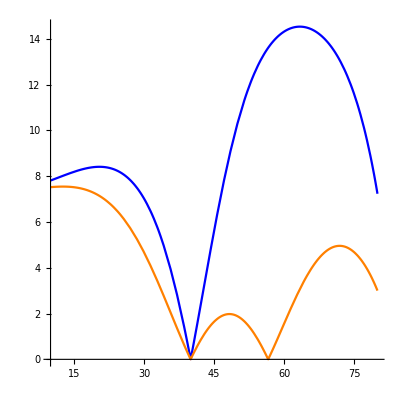

```mathematica
magfac = 20;

p$R=ParametricPlot[{{θ,magfac Abs[ErB1$TE$func[1.5168,θ Degree,13.720088565627512]]},{θ,magfac Abs[ErB1$TM$func[1.5168,θ Degree,13.720088565627512]]}},{θ,10 ,80 },AspectRatio->1,PlotStyle->{{Thickness[.004],Blue},{Thickness[.004],Orange}},BaseStyle->{"Tahoma",14}]
```

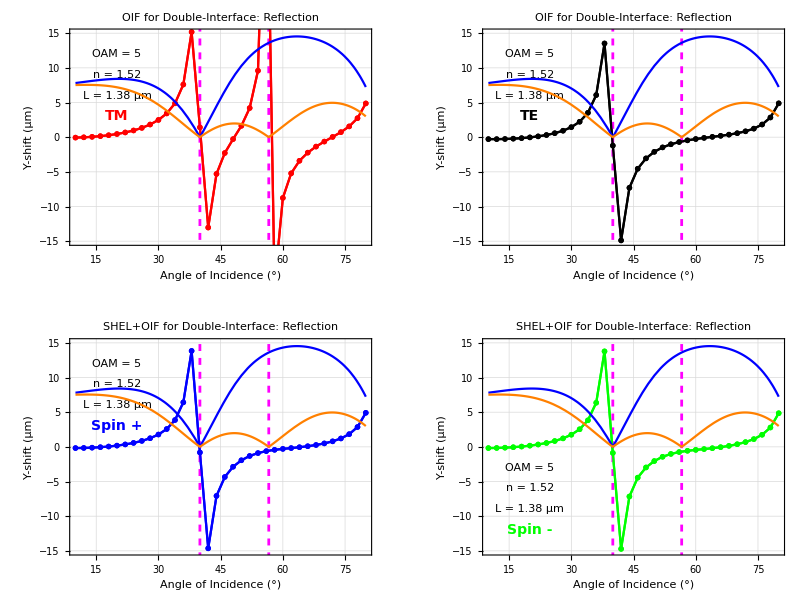

```mathematica
GraphicsGrid[{{Show[p$R1$final$y,p$R],Show[p$R2$final$y,p$R]},
{Show[p$R3$final$y,p$R],Show[p$R4$final$y,p$R]}},ImageSize->800]
```

### Centroid Shifts versus Gap Width: n = 1/1.5168, θ = 30°, OAM = 5 (Air Gap)

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

#### Analysis

```mathematica
Clear[plots,k0,β];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1/1.5168,θ->30.0 Degree,k0->1,p->0,ℓ->5,L->Lloop};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

Print["k_0L: ",Lloop, ", Actual Gap: ",gap," μm"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)


βtab = Table[ArcCos[κvec.nvec] /. params$here/.{κx->κtab[[i,j,1]],κy->κtab[[i,j,2]]},{i,1,dimset},{j,1,dimset}];

R1tab = Table[-ErB1$TM /.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];
R2tab = Table[ ErB1$TE/.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];


Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eRtab = Table[{(f[[1]]R1tab[[i,j]]-f[[2]]κtab[[i,j,2]] Cot[θR](R1tab[[i,j]]+R2tab[[i,j]])),f[[2]]R2tab[[i,j]] + f[[1]]κtab[[i,j,2]] Cot[θR](R1tab[[i,j]]+R2tab[[i,j]] ),-(f[[1]]R1tab[[i,j]] κtab[[i,j,1]] + f[[2]]R2tab[[i,j]]  κtab[[i,j,2]])}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,gap,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,gap,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,gap,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,gap,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{Lloop,1.0,15.0,0.2}]
```

k_0L: 1., Actual Gap: 0.100713 μm

TM (Reflected) = {-0.111546,7.8842} μm

TE (Reflected) = {-0.0696372,-0.332821} μm

spin+ (Reflected) = {-0.0709966,0.0471527} μm

spin- (Reflected) = {-0.0709966,-0.179736} μm

k_0L: 1.2, Actual Gap: 0.120856 μm

TM (Reflected) = {-0.133089,7.84157} μm

TE (Reflected) = {-0.0836607,-0.350164} μm

spin+ (Reflected) = {-0.0853186,0.0370876} μm

spin- (Reflected) = {-0.0853186,-0.187903} μm

k_0L: 1.4, Actual Gap: 0.140999 μm

TM (Reflected) = {-0.15426,7.79153} μm

TE (Reflected) = {-0.0978239,-0.370471} μm

spin+ (Reflected) = {-0.0997855,0.0246805} μm

spin- (Reflected) = {-0.0997855,-0.198216} μm

k_0L: 1.6, Actual Gap: 0.161141 μm

TM (Reflected) = {-0.175032,7.73419} μm

TE (Reflected) = {-0.112203,-0.393838} μm

spin+ (Reflected) = {-0.114468,0.00954555} μm

spin- (Reflected) = {-0.114468,-0.211125} μm

k_0L: 1.8, Actual Gap: 0.181284 μm

TM (Reflected) = {-0.195395,7.6696} μm

TE (Reflected) = {-0.126883,-0.420465} μm

spin+ (Reflected) = {-0.129445,-0.00881503} μm

spin- (Reflected) = {-0.129445,-0.227195} μm

k_0L: 2., Actual Gap: 0.201426 μm

TM (Reflected) = {-0.215349,7.59775} μm

TE (Reflected) = {-0.141961,-0.450668} μm

spin+ (Reflected) = {-0.144802,-0.0310112} μm

spin- (Reflected) = {-0.144802,-0.247105} μm

k_0L: 2.2, Actual Gap: 0.221569 μm

TM (Reflected) = {-0.23491,7.51857} μm

TE (Reflected) = {-0.157536,-0.484891} μm

spin+ (Reflected) = {-0.160632,-0.0577656} μm

spin- (Reflected) = {-0.160632,-0.271643} μm

k_0L: 2.4, Actual Gap: 0.241712 μm

TM (Reflected) = {-0.254107,7.43186} μm

TE (Reflected) = {-0.173718,-0.523722} μm

spin+ (Reflected) = {-0.177031,-0.0899181} μm

spin- (Reflected) = {-0.177031,-0.301714} μm

k_0L: 2.6, Actual Gap: 0.261854 μm

TM (Reflected) = {-0.27298,7.33727} μm

TE (Reflected) = {-0.190619,-0.567903} μm

spin+ (Reflected) = {-0.194104,-0.128436} μm

spin- (Reflected) = {-0.194104,-0.338344} μm

k_0L: 2.8, Actual Gap: 0.281997 μm

TM (Reflected) = {-0.29158,7.23433} μm

TE (Reflected) = {-0.20836,-0.618363} μm

spin+ (Reflected) = {-0.211961,-0.174435} μm

spin- (Reflected) = {-0.211961,-0.3827} μm

k_0L: 3., Actual Gap: 0.30214 μm

TM (Reflected) = {-0.309967,7.12231} μm

TE (Reflected) = {-0.227069,-0.676249} μm

spin+ (Reflected) = {-0.230721,-0.229205} μm

spin- (Reflected) = {-0.230721,-0.436119} μm

k_0L: 3.2, Actual Gap: 0.322282 μm

TM (Reflected) = {-0.328208,7.00028} μm

TE (Reflected) = {-0.246881,-0.742971} μm

spin+ (Reflected) = {-0.250513,-0.294263} μm

spin- (Reflected) = {-0.250513,-0.500153} μm

k_0L: 3.4, Actual Gap: 0.342425 μm

TM (Reflected) = {-0.346375,6.86699} μm

TE (Reflected) = {-0.267941,-0.820269} μm

spin+ (Reflected) = {-0.271473,-0.371404} μm

spin- (Reflected) = {-0.271473,-0.576625} μm

k_0L: 3.6, Actual Gap: 0.362568 μm

TM (Reflected) = {-0.364542,6.72084} μm

TE (Reflected) = {-0.2904,-0.910292} μm

spin+ (Reflected) = {-0.293752,-0.46279} μm

spin- (Reflected) = {-0.293752,-0.667715} μm

k_0L: 3.8, Actual Gap: 0.38271 μm

TM (Reflected) = {-0.382782,6.55978} μm

TE (Reflected) = {-0.314419,-1.01571} μm

spin+ (Reflected) = {-0.317506,-0.571056} μm

spin- (Reflected) = {-0.317506,-0.776066} μm

k_0L: 4., Actual Gap: 0.402853 μm

TM (Reflected) = {-0.401169,6.38121} μm

TE (Reflected) = {-0.340162,-1.13985} μm

spin+ (Reflected) = {-0.342901,-0.699456} μm

spin- (Reflected) = {-0.342901,-0.904929} μm

k_0L: 4.2, Actual Gap: 0.422996 μm

TM (Reflected) = {-0.419771,6.18184} μm

TE (Reflected) = {-0.367797,-1.28692} μm

spin+ (Reflected) = {-0.370105,-0.852059} μm

spin- (Reflected) = {-0.370105,-1.05836} μm

k_0L: 4.4, Actual Gap: 0.443138 μm

TM (Reflected) = {-0.438649,5.95743} μm

TE (Reflected) = {-0.397482,-1.46221} μm

spin+ (Reflected) = {-0.399283,-1.03401} μm

spin- (Reflected) = {-0.399283,-1.24149} μm

k_0L: 4.6, Actual Gap: 0.463281 μm

TM (Reflected) = {-0.457856,5.70253} μm

TE (Reflected) = {-0.429363,-1.67253} μm

spin+ (Reflected) = {-0.430585,-1.25191} μm

spin- (Reflected) = {-0.430585,-1.46088} μm

k_0L: 4.8, Actual Gap: 0.483424 μm

TM (Reflected) = {-0.477436,5.41001} μm

TE (Reflected) = {-0.463552,-1.92665} μm

spin+ (Reflected) = {-0.464133,-1.51431} μm

spin- (Reflected) = {-0.464133,-1.72503} μm

k_0L: 5., Actual Gap: 0.503566 μm

TM (Reflected) = {-0.497421,5.07034} μm

TE (Reflected) = {-0.500107,-2.2361} μm

spin+ (Reflected) = {-0.499998,-1.83246} μm

spin- (Reflected) = {-0.499998,-2.04516} μm

k_0L: 5.2, Actual Gap: 0.523709 μm

TM (Reflected) = {-0.517828,4.67052} μm

TE (Reflected) = {-0.539007,-2.61626} μm

spin+ (Reflected) = {-0.538171,-2.22145} μm

spin- (Reflected) = {-0.538171,-2.43631} μm

k_0L: 5.4, Actual Gap: 0.543852 μm

TM (Reflected) = {-0.538664,4.19226} μm

TE (Reflected) = {-0.580111,-3.08814} μm

spin+ (Reflected) = {-0.578531,-2.70201} μm

spin- (Reflected) = {-0.578531,-2.91912} μm

k_0L: 5.6, Actual Gap: 0.563994 μm

TM (Reflected) = {-0.559918,3.60895} μm

TE (Reflected) = {-0.623121,-3.68137} μm

spin+ (Reflected) = {-0.620796,-3.30345} μm

spin- (Reflected) = {-0.620796,-3.52286} μm

k_0L: 5.8, Actual Gap: 0.584137 μm

TM (Reflected) = {-0.581567,2.88014} μm

TE (Reflected) = {-0.667535,-4.43951} μm

spin+ (Reflected) = {-0.664486,-4.06904} μm

spin- (Reflected) = {-0.664486,-4.29072} μm

k_0L: 6., Actual Gap: 0.604279 μm

TM (Reflected) = {-0.603574,1.94104} μm

TE (Reflected) = {-0.712608,-5.43031} μm

spin+ (Reflected) = {-0.708878,-5.06626} μm

spin- (Reflected) = {-0.708878,-5.29011} μm

k_0L: 6.2, Actual Gap: 0.624422 μm

TM (Reflected) = {-0.625888,0.680551} μm

TE (Reflected) = {-0.757327,-6.76722} μm

spin+ (Reflected) = {-0.752986,-6.40828} μm

spin- (Reflected) = {-0.752986,-6.63414} μm

k_0L: 6.4, Actual Gap: 0.644565 μm

TM (Reflected) = {-0.648449,-1.10956} μm

TE (Reflected) = {-0.80043,-8.65968} μm

spin+ (Reflected) = {-0.795568,-8.30432} μm

spin- (Reflected) = {-0.795568,-8.53198} μm

k_0L: 6.6, Actual Gap: 0.664707 μm

TM (Reflected) = {-0.671185,-3.87131} μm

TE (Reflected) = {-0.840456,-11.5492} μm

spin+ (Reflected) = {-0.83519,-11.1957} μm

spin- (Reflected) = {-0.83519,-11.4249} μm

k_0L: 6.8, Actual Gap: 0.68485 μm

TM (Reflected) = {-0.694018,-8.73815} μm

TE (Reflected) = {-0.875874,-16.5664} μm

spin+ (Reflected) = {-0.870342,-16.2131} μm

spin- (Reflected) = {-0.870342,-16.4434} μm

k_0L: 7., Actual Gap: 0.704993 μm

TM (Reflected) = {-0.716867,-19.759} μm

TE (Reflected) = {-0.905249,-27.7546} μm

spin+ (Reflected) = {-0.899609,-27.3996} μm

spin- (Reflected) = {-0.899609,-27.6308} μm

k_0L: 7.2, Actual Gap: 0.725135 μm

TM (Reflected) = {-0.739653,-70.1718} μm

TE (Reflected) = {-0.92746,-78.3372} μm

spin+ (Reflected) = {-0.921884,-77.979} μm

spin- (Reflected) = {-0.921884,-78.2106} μm

k_0L: 7.4, Actual Gap: 0.745278 μm

TM (Reflected) = {-0.762256,105.239} μm

TE (Reflected) = {-0.941774,96.9032} μm

spin+ (Reflected) = {-0.936445,97.2665} μm

spin- (Reflected) = {-0.936445,97.0349} μm

k_0L: 7.6, Actual Gap: 0.765421 μm

TM (Reflected) = {-0.784663,37.8196} μm

TE (Reflected) = {-0.948296,29.2978} μm

spin+ (Reflected) = {-0.943402,29.6683} μm

spin- (Reflected) = {-0.943402,29.4371} μm

k_0L: 7.8, Actual Gap: 0.785563 μm

TM (Reflected) = {-0.806762,25.4217} μm

TE (Reflected) = {-0.947503,16.7469} μm

spin+ (Reflected) = {-0.943231,17.1255} μm

spin- (Reflected) = {-0.943231,16.8951} μm

k_0L: 8., Actual Gap: 0.805706 μm

TM (Reflected) = {-0.828499,20.1373} μm

TE (Reflected) = {-0.940508,11.3366} μm

spin+ (Reflected) = {-0.937033,11.7243} μm

spin- (Reflected) = {-0.937033,11.495} μm

k_0L: 8.2, Actual Gap: 0.825849 μm

TM (Reflected) = {-0.849826,17.1607} μm

TE (Reflected) = {-0.928761,8.26565} μm

spin+ (Reflected) = {-0.926244,8.66319} μm

spin- (Reflected) = {-0.926244,8.43536} μm

k_0L: 8.4, Actual Gap: 0.845991 μm

TM (Reflected) = {-0.870709,15.2158} μm

TE (Reflected) = {-0.91387,6.26101} μm

spin+ (Reflected) = {-0.91245,6.66876} μm

spin- (Reflected) = {-0.91245,6.44269} μm

k_0L: 8.6, Actual Gap: 0.866134 μm

TM (Reflected) = {-0.891127,13.8184} μm

TE (Reflected) = {-0.897416,4.8389} μm

spin+ (Reflected) = {-0.897202,5.25688} μm

spin- (Reflected) = {-0.897202,5.03281} μm

k_0L: 8.8, Actual Gap: 0.886277 μm

TM (Reflected) = {-0.911076,12.7442} μm

TE (Reflected) = {-0.880828,3.7737} μm

spin+ (Reflected) = {-0.881896,4.20158} μm

spin- (Reflected) = {-0.881896,3.97967} μm

k_0L: 9., Actual Gap: 0.906419 μm

TM (Reflected) = {-0.930567,11.8751} μm

TE (Reflected) = {-0.865306,2.94449} μm

spin+ (Reflected) = {-0.867697,3.38159} μm

spin- (Reflected) = {-0.867697,3.16193} μm

k_0L: 9.2, Actual Gap: 0.926562 μm

TM (Reflected) = {-0.949628,11.1426} μm

TE (Reflected) = {-0.851805,2.27938} μm

spin+ (Reflected) = {-0.85552,2.7247} μm

spin- (Reflected) = {-0.85552,2.50734} μm

k_0L: 9.4, Actual Gap: 0.946705 μm

TM (Reflected) = {-0.968299,10.5042} μm

TE (Reflected) = {-0.841048,1.73204} μm

spin+ (Reflected) = {-0.846049,2.18432} μm

spin- (Reflected) = {-0.846049,1.96923} μm

k_0L: 9.6, Actual Gap: 0.966847 μm

TM (Reflected) = {-0.986634,9.9318} μm

TE (Reflected) = {-0.833563,1.27063} μm

spin+ (Reflected) = {-0.839771,1.72837} μm

spin- (Reflected) = {-0.839771,1.51544} μm

k_0L: 9.8, Actual Gap: 0.98699 μm

TM (Reflected) = {-1.0047,9.40595} μm

TE (Reflected) = {-0.829724,0.872079} μm

spin+ (Reflected) = {-0.837025,1.3336} μm

spin- (Reflected) = {-0.837025,1.12267} μm

k_0L: 10., Actual Gap: 1.00713 μm

TM (Reflected) = {-1.02256,8.91233} μm

TE (Reflected) = {-0.8298,0.518836} μm

spin+ (Reflected) = {-0.838043,0.98232} μm

spin- (Reflected) = {-0.838043,0.773177} μm

k_0L: 10.2, Actual Gap: 1.02728 μm

TM (Reflected) = {-1.04031,8.43995} μm

TE (Reflected) = {-0.833984,0.196988} μm

spin+ (Reflected) = {-0.842989,0.660556} μm

spin- (Reflected) = {-0.842989,0.452931} μm

k_0L: 10.4, Actual Gap: 1.04742 μm

TM (Reflected) = {-1.05803,7.97982} μm

TE (Reflected) = {-0.842432,-0.105023} μm

spin+ (Reflected) = {-0.851993,0.35673} μm

spin- (Reflected) = {-0.851993,0.150314} μm

k_0L: 10.6, Actual Gap: 1.06756 μm

TM (Reflected) = {-1.0758,7.5242} μm

TE (Reflected) = {-0.855281,-0.397276} μm

spin+ (Reflected) = {-0.865171,0.0607998} μm

spin- (Reflected) = {-0.865172,-0.144747} μm

k_0L: 10.8, Actual Gap: 1.0877 μm

TM (Reflected) = {-1.09371,7.06594} μm

TE (Reflected) = {-0.872666,-0.689046} μm

spin+ (Reflected) = {-0.882646,-0.236414} μm

spin- (Reflected) = {-0.882646,-0.441457} μm

k_0L: 11., Actual Gap: 1.10785 μm

TM (Reflected) = {-1.11183,6.59809} μm

TE (Reflected) = {-0.894735,-0.989362} μm

spin+ (Reflected) = {-0.904553,-0.543799} μm

spin- (Reflected) = {-0.904553,-0.748715} μm

k_0L: 11.2, Actual Gap: 1.12799 μm

TM (Reflected) = {-1.13026,6.11342} μm

TE (Reflected) = {-0.921647,-1.30753} μm

spin+ (Reflected) = {-0.93105,-0.870468} μm

spin- (Reflected) = {-0.93105,-1.07564} μm

k_0L: 11.4, Actual Gap: 1.14813 μm

TM (Reflected) = {-1.14904,5.60405} μm

TE (Reflected) = {-0.953574,-1.65366} μm

spin+ (Reflected) = {-0.962313,-1.2263} μm

spin- (Reflected) = {-0.962313,-1.43209} μm

k_0L: 11.6, Actual Gap: 1.16827 μm

TM (Reflected) = {-1.16825,5.06098} μm

TE (Reflected) = {-0.990691,-2.03925} μm

spin+ (Reflected) = {-0.998527,-1.62251} μm

spin- (Reflected) = {-0.998527,-1.8293} μm

k_0L: 11.8, Actual Gap: 1.18842 μm

TM (Reflected) = {-1.18792,4.47346} μm

TE (Reflected) = {-1.03316,-2.47793} μm

spin+ (Reflected) = {-1.03987,-2.07243} μm

spin- (Reflected) = {-1.03987,-2.28053} μm

k_0L: 12., Actual Gap: 1.20856 μm

TM (Reflected) = {-1.20808,3.82825} μm

TE (Reflected) = {-1.08112,-2.98635} μm

spin+ (Reflected) = {-1.0865,-2.59237} μm

spin- (Reflected) = {-1.0865,-2.80209} μm

k_0L: 12.2, Actual Gap: 1.2287 μm

TM (Reflected) = {-1.22876,3.10843} μm

TE (Reflected) = {-1.13461,-3.58547} μm

spin+ (Reflected) = {-1.1385,-3.20294} μm

spin- (Reflected) = {-1.1385,-3.41452} μm

k_0L: 12.4, Actual Gap: 1.24884 μm

TM (Reflected) = {-1.24994,2.29168} μm

TE (Reflected) = {-1.19357,-4.30238} μm

spin+ (Reflected) = {-1.19583,-3.93086} μm

spin- (Reflected) = {-1.19583,-4.14451} μm

k_0L: 12.6, Actual Gap: 1.26899 μm

TM (Reflected) = {-1.27162,1.34747} μm

TE (Reflected) = {-1.25775,-5.17308} μm

spin+ (Reflected) = {-1.25829,-4.81176} μm

spin- (Reflected) = {-1.25829,-5.02761} μm

k_0L: 12.8, Actual Gap: 1.28913 μm

TM (Reflected) = {-1.29375,0.232596} μm

TE (Reflected) = {-1.32663,-6.24691} μm

spin+ (Reflected) = {-1.32539,-5.89466} μm

spin- (Reflected) = {-1.32539,-6.11279} μm

k_0L: 13., Actual Gap: 1.30927 μm

TM (Reflected) = {-1.3163,-1.11681} μm

TE (Reflected) = {-1.39933,-7.59429} μm

spin+ (Reflected) = {-1.39632,-7.2496} μm

spin- (Reflected) = {-1.39632,-7.47003} μm

k_0L: 13.2, Actual Gap: 1.32941 μm

TM (Reflected) = {-1.3392,-2.79982} μm

TE (Reflected) = {-1.47455,-9.32077} μm

spin+ (Reflected) = {-1.46983,-8.98188} μm

spin- (Reflected) = {-1.46983,-9.20454} μm

k_0L: 13.4, Actual Gap: 1.34956 μm

TM (Reflected) = {-1.36238,-4.97962} μm

TE (Reflected) = {-1.55048,-11.5953} μm

spin+ (Reflected) = {-1.54415,-11.2602} μm

spin- (Reflected) = {-1.54415,-11.4849} μm

k_0L: 13.6, Actual Gap: 1.3697 μm

TM (Reflected) = {-1.38574,-7.94636} μm

TE (Reflected) = {-1.62478,-14.712} μm

spin+ (Reflected) = {-1.617,-14.3784} μm

spin- (Reflected) = {-1.617,-14.6051} μm

k_0L: 13.8, Actual Gap: 1.38984 μm

TM (Reflected) = {-1.40919,-12.2717} μm

TE (Reflected) = {-1.69467,-19.2437} μm

spin+ (Reflected) = {-1.68566,-18.9094} μm

spin- (Reflected) = {-1.68566,-19.1377} μm

k_0L: 14., Actual Gap: 1.40999 μm

TM (Reflected) = {-1.43264,-19.2618} μm

TE (Reflected) = {-1.75708,-26.4935} μm

spin+ (Reflected) = {-1.74709,-26.1561} μm

spin- (Reflected) = {-1.74709,-26.3858} μm

k_0L: 14.2, Actual Gap: 1.43013 μm

TM (Reflected) = {-1.45599,-32.6979} μm

TE (Reflected) = {-1.80894,-40.2347} μm

spin+ (Reflected) = {-1.79829,-39.8918} μm

spin- (Reflected) = {-1.79829,-40.1226} μm

k_0L: 14.4, Actual Gap: 1.45027 μm

TM (Reflected) = {-1.47914,-69.9885} μm

TE (Reflected) = {-1.84762,-77.8583} μm

spin+ (Reflected) = {-1.83664,-77.508} μm

spin- (Reflected) = {-1.83664,-77.7394} μm

k_0L: 14.6, Actual Gap: 1.47041 μm

TM (Reflected) = {-1.50217,-760.086} μm

TE (Reflected) = {-1.87163,-767.332} μm

spin+ (Reflected) = {-1.86069,-767.002} μm

spin- (Reflected) = {-1.86069,-767.233} μm

k_0L: 14.8, Actual Gap: 1.49056 μm

TM (Reflected) = {-1.52439,105.087} μm

TE (Reflected) = {-1.87882,96.5152} μm

spin+ (Reflected) = {-1.86827,96.886} μm

spin- (Reflected) = {-1.86827,96.6546} μm

k_0L: 15., Actual Gap: 1.5107 μm

TM (Reflected) = {-1.5464,53.4155} μm

TE (Reflected) = {-1.87121,44.498} μm

spin+ (Reflected) = {-1.86144,44.8817} μm

spin- (Reflected) = {-1.86144,44.6508} μm

#### Ramsauer-Townsend Windows

```mathematica
ErB1$TE$func[n_,β_,L_]=ErB1$TE;
```

```mathematica
1/1.5168
```

0.659283

```mathematica
Manipulate[ParametricPlot[{θ,Abs[ErB1$TE$func[n,θ Degree,L]]},{θ,10 ,80 },AspectRatio->1],{n,0.5,2},{L,0.1,20.0}]
```

```mathematica
params$here = {wk->20000.,n->1/1.5168,θ->30 Degree,k0->1,p->0,ℓ->5};

L$ram = {};

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,6}];
AppendTo[L$ram,L /. sol[[1]]];

sol=FindRoot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]]==0,{L,14}];
AppendTo[L$ram,L /. sol[[1]]];

L$ram

L$ram$units = Table[L$ram[[j]]/(2π/(632.8*10^-9))*10^6,{j,1,Length[L$ram]}]
```

{7.3109,14.6218}

{0.736305,1.47261}

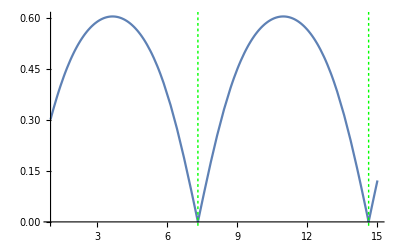

```mathematica
Clear[p$ram] ;

Array[p$ram,Length[L$ram]];

Do[p$ram[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram[[j]],-10000},{L$ram[[j]],10000}}]}],{j,1,Length[L$ram]}]

p$ram$all = Show[Table[p$ram[j],{j,1,Length[L$ram]}]];

Array[p$ram$all,Length[L$ram]];

Do[p$ram$units[j]=Graphics[{Thick,Green,Dashing->Tiny,Line[{{L$ram$units[[j]],-10000},{L$ram$units[[j]],10000}}]}],{j,1,Length[L$ram]}]
p$ram$units$all = Show[Table[p$ram$units[j],{j,1,Length[L$ram]}]];

p$ram$final = Show[Plot[Abs[ErB1$TE$func[n /. params$here,θ /. params$here,L]],{L,1,15}],p$ram$all]
```

#### Data Record

```mathematica
params$here = {wk->20000.,n->1/1.5168,θ->30.0 Degree,k0->1,p->0,ℓ->5,L->Lloop}
```

{wk→20000.,n→0.659283,θ→0.523599,k0→1,p→0,ℓ→5,L→Lloop}

```mathematica
shift$tab$R4
```

{{5,10.,{-0.146307,-0.175866}},{5,12.,{-0.173771,-0.15973}},{5,14.,{-0.200508,-0.119476}},{5,16.,{-0.226596,-0.0528385}},{5,18.,{-0.252196,0.0429163}},{5,20.,{-0.277539,0.171751}},{5,22.,{-0.302925,0.339925}},{5,24.,{-0.328706,0.557628}},{5,26.,{-0.355274,0.841819}},{5,28.,{-0.383051,1.22175}},{5,30.,{-0.412466,1.75099}},{5,32.,{-0.443882,2.5371}},{5,34.,{-0.477361,3.82909}},{5,36.,{-0.512176,6.36319}},{5,38.,{-0.546087,13.7774}},{5,40.,{-0.574862,-0.880385}},{5,42.,{-0.592883,-14.7207}},{5,44.,{-0.595257,-7.16416}},{5,46.,{-0.580335,-4.44421}},{5,48.,{-0.550592,-2.972}},{5,50.,{-0.511219,-2.04586}},{5,52.,{-0.467864,-1.43169}},{5,54.,{-0.425191,-1.02111}},{5,56.,{-0.386521,-0.749041}},{5,58.,{-0.353903,-0.567248}},{5,60.,{-0.328158,-0.435337}},{5,62.,{-0.308973,-0.319747}},{5,64.,{-0.29532,-0.195458}},{5,66.,{-0.286124,-0.0458278}},{5,68.,{-0.280819,0.14107}},{5,70.,{-0.279587,0.378531}},{5,72.,{-0.283336,0.68889}},{5,74.,{-0.293635,1.11513}},{5,76.,{-0.31279,1.74597}},{5,78.,{-0.344263,2.78847}},{5,80.,{-0.393939,4.84968}}}

```mathematica
shift$tab$R1={{5,0.10071324798855139,{-0.11154633231751893,7.884197605084969}},{5,0.12085589758626165,{-0.13308888042245245,7.84156718991711}},{5,0.14099854718397192,{-0.15425961593346235,7.791531415708873}},{5,0.16114119678168223,{-0.17503244830389802,7.73418827981666}},{5,0.1812838463793925,{-0.195395067478834,7.669596126304514}},{5,0.20142649597710277,{-0.21534918599474615,7.597752462975274}},{5,0.22156914557481305,{-0.23491029618139928,7.518570860410574}},{5,0.24171179517252336,{-0.2541069767236607,7.431855788099936}},{5,0.2618544447702336,{-0.2729797971989657,7.337274973927207}},{5,0.28199709436794385,{-0.2915798761447214,7.234328518351176}},{5,0.30213974396565413,{-0.3099671541466445,7.122313526000974}},{5,0.32228239356336447,{-0.3282084426260904,7.0002823838738575}},{5,0.34242504316107475,{-0.34637530917045656,6.866991931400726}},{5,0.362567692758785,{-0.36454185597997646,6.720839493886316}},{5,0.3827103423564953,{-0.38278244576006615,6.559779858218278}},{5,0.40285299195420554,{-0.40116942590765475,6.381214375328952}},{5,0.4229956415519158,{-0.4197709011128708,6.181838822615469}},{5,0.4431382911496261,{-0.4386486027341896,5.957429311221341}},{5,0.46328094074733633,{-0.45785590568097734,5.702533296570997}},{5,0.4834235903450467,{-0.47743604383505756,5.410011778352997}},{5,0.503566239942757,{-0.4974205768462688,5.070341467819827}},{5,0.5237088895404672,{-0.5178281635242569,4.670516608514556}},{5,0.5438515391381775,{-0.5386636940088305,4.19225599012818}},{5,0.5639941887358878,{-0.5599178309146768,3.6089454714833815}},{5,0.5841368383335981,{-0.5815670019233592,2.8801432940703937}},{5,0.6042794879313083,{-0.6035738745423345,1.9410445071887616}},{5,0.6244221375290187,{-0.6258883290148662,0.6805514153378065}},{5,0.6445647871267289,{-0.6484489254592912,-1.1095612893588025}},{5,0.6647074367244392,{-0.6711848450974898,-3.871308086991909}},{5,0.6848500863221495,{-0.6940182833542806,-8.738154231262007}},{5,0.7049927359198597,{-0.7168674140370287,-19.758988909614693}},{5,0.72513538551757,{-0.7396528702149943,-70.17179235259849}},{5,0.7452780351152802,{-0.7622559716087671,105.23917307719074}},{5,0.7654206847129906,{-0.7846627861946324,37.81962304271459}},{5,0.7855633343107009,{-0.8067619345936551,25.42165956545543}},{5,0.8057059839084111,{-0.8284991624624827,20.137307851682802}},{5,0.8258486335061213,{-0.8498263946871785,17.160668411173166}},{5,0.8459912831038316,{-0.8707088727580716,15.21576963310422}},{5,0.866133932701542,{-0.8911267308421408,13.81836356386907}},{5,0.8862765822992522,{-0.9110757088632833,12.744211160364223}},{5,0.9064192318969625,{-0.930567246785451,11.875086948188287}},{5,0.9265618814946729,{-0.9496280190306255,11.14258304318618}},{5,0.9467045310923831,{-0.9682989593304734,10.504172186303606}},{5,0.9668471806900932,{-0.9866338378003702,9.931798448006202}},{5,0.9869898302878036,{-1.0046974607034067,9.405946621005105}},{5,1.007132479885514,{-1.0225635684785865,8.912334217008512}},{5,1.0272751294832243,{-1.0403125091016256,8.439950083609148}},{5,1.0474177790809345,{-1.0580287595874431,7.979822360738344}},{5,1.0675604286786449,{-1.0757983660676054,7.524195772942581}},{5,1.087703078276355,{-1.0937063654966164,7.065940833089782}},{5,1.1078457278740652,{-1.1118342470144864,6.598088596331931}},{5,1.1279883774717756,{-1.130257506676458,6.113419855110998}},{5,1.1481310270694858,{-1.1490433466559347,5.604052901495142}},{5,1.1682736766671962,{-1.1682485669867588,5.060975696069343}},{5,1.1884163262649063,{-1.1879177006589097,4.473457668901962}},{5,1.2085589758626165,{-1.2080814407520566,3.8282501996392444}},{5,1.228701625460327,{-1.2287554117721178,3.108433894650231}},{5,1.2488442750580373,{-1.2499393349515258,2.2916751030516602}},{5,1.2689869246557477,{-1.2716166366212738,1.347470896135592}},{5,1.2891295742534579,{-1.2937545418757623,0.23259585627560947}},{5,1.309272223851168,{-1.3163046872843789,-1.116809082460111}},{5,1.3294148734488784,{-1.339204271112561,-2.7998181492427587}},{5,1.3495575230465886,{-1.362377743021704,-4.979620207279726}},{5,1.369700172644299,{-1.3857390137432295,-7.946355733198769}},{5,1.3898428222420092,{-1.4091941508984698,-12.271702606669237}},{5,1.4099854718397193,{-1.4326445394903156,-19.26175212040555}},{5,1.4301281214374297,{-1.4559906749202756,-32.697917271823734}},{5,1.45027077103514,{-1.4791386829287172,-69.98846853598506}},{5,1.4704134206328503,{-1.5021672296574409,-760.0857171337157}},{5,1.4905560702305605,{-1.5243883024394747,105.08678217872506}},{5,1.5106987198282709,{-1.5464048932574108,53.41553560377417}}};
```

```mathematica
shift$tab$R2={{5,0.10071324798855139,{-0.06963722524025685,-0.3328211774595265}},{5,0.12085589758626165,{-0.0836607229824555,-0.35016368564714395}},{5,0.14099854718397192,{-0.09782388198750065,-0.3704713200806812}},{5,0.16114119678168223,{-0.11220259240601618,-0.3938383992536985}},{5,0.1812838463793925,{-0.12688328720579617,-0.42046480595205743}},{5,0.20142649597710277,{-0.14196068080202137,-0.4506675131713008}},{5,0.22156914557481305,{-0.15753629339363912,-0.484891312689178}},{5,0.24171179517252336,{-0.17371777964613394,-0.5237217816103465}},{5,0.2618544447702336,{-0.1906189237910254,-0.5679031344767}},{5,0.28199709436794385,{-0.20836009534964092,-0.6183633112491982}},{5,0.30213974396565413,{-0.22706894002945327,-0.6762486245429414}},{5,0.32228239356336447,{-0.24688107599036044,-0.7429706188155356}},{5,0.34242504316107475,{-0.26794055322666005,-0.8202685173190606}},{5,0.362567692758785,{-0.2903997959460785,-0.9102918271290064}},{5,0.3827103423564953,{-0.31441868083460667,-1.0157094818391297}},{5,0.40285299195420554,{-0.3401622965195739,-1.1398546173395407}},{5,0.4229956415519158,{-0.3677967841885539,-1.2869182260246368}},{5,0.4431382911496261,{-0.39748247994386104,-1.4622115072893676}},{5,0.46328094074733633,{-0.4293633816718866,-1.672527576095549}},{5,0.4834235903450467,{-0.46355179223281956,-1.9266519287335744}},{5,0.503566239942757,{-0.5001069321191239,-2.2361049894418645}},{5,0.5237088895404672,{-0.539006513298791,-2.6162644544384164}},{5,0.5438515391381775,{-0.5801109587048632,-3.0881434419715723}},{5,0.5639941887358878,{-0.6231214357573506,-3.6813695786358656}},{5,0.5841368383335981,{-0.6675354552975097,-4.439509073558937}},{5,0.6042794879313083,{-0.7126075701068606,-5.430312697604803}},{5,0.6244221375290187,{-0.7573272351439834,-6.76722356846936}},{5,0.6445647871267289,{-0.8004297068731983,-8.65967529286296}},{5,0.6647074367244392,{-0.8404562695220609,-11.549165213568083}},{5,0.6848500863221495,{-0.8758738235565825,-16.566377909831818}},{5,0.7049927359198597,{-0.9052493161879076,-27.754632330236063}},{5,0.72513538551757,{-0.9274599205419313,-78.33724631059498}},{5,0.7452780351152802,{-0.9417743047747913,96.90321122991197}},{5,0.7654206847129906,{-0.9482960656158458,29.297840765742958}},{5,0.7855633343107009,{-0.9475034135289743,16.74692850214007}},{5,0.8057059839084111,{-0.9405078991102512,11.336560670840708}},{5,0.8258486335061213,{-0.9287614076969986,8.265647102439457}},{5,0.8459912831038316,{-0.9138702470425181,6.26100639914811}},{5,0.866133932701542,{-0.8974164935157004,4.838897731694828}},{5,0.8862765822992522,{-0.8808278570015856,3.7737027267975374}},{5,0.9064192318969625,{-0.8653057836807919,2.944491255329122}},{5,0.9265618814946729,{-0.8518047655153126,2.2793776190469806}},{5,0.9467045310923831,{-0.8410478549225076,1.732039138979193}},{5,0.9668471806900932,{-0.833562553726359,1.270634668289636}},{5,0.9869898302878036,{-0.8297244021539324,0.8720785654413976}},{5,1.007132479885514,{-0.82979990816475,0.5188357810768595}},{5,1.0272751294832243,{-0.8339842738039953,0.19698809762006417}},{5,1.0474177790809345,{-0.8424320712163003,-0.10502252590050892}},{5,1.0675604286786449,{-0.8552806012484866,-0.397275796864398}},{5,1.087703078276355,{-0.8726663832089286,-0.6890455320875137}},{5,1.1078457278740652,{-0.8947353680057522,-0.9893617467126513}},{5,1.1279883774717756,{-0.9216472546416815,-1.307529469756544}},{5,1.1481310270694858,{-0.9535738797408205,-1.6536579629071073}},{5,1.1682736766671962,{-0.9906911282856655,-2.039252669631576}},{5,1.1884163262649063,{-1.0331632487308238,-2.4779316355431926}},{5,1.2085589758626165,{-1.0811179204861676,-2.9863512977689157}},{5,1.228701625460327,{-1.1346100409370707,-3.585472232063224}},{5,1.2488442750580373,{-1.1935721930093826,-4.30238328820075}},{5,1.2689869246557477,{-1.2577504853718415,-5.173075295034418}},{5,1.2891295742534579,{-1.3266264519587443,-6.246909240411142}},{5,1.309272223851168,{-1.3993295777027583,-7.594285998856503}},{5,1.3294148734488784,{-1.4745512556264642,-9.320773607410668}},{5,1.3495575230465886,{-1.5504793636026477,-11.595296346572619}},{5,1.369700172644299,{-1.6247814343363773,-14.71200281734434}},{5,1.3898428222420092,{-1.6946695377919687,-19.243695518061074}},{5,1.4099854718397193,{-1.7570753427995713,-26.49351491395692}},{5,1.4301281214374297,{-1.8089437845863572,-40.234676129868596}},{5,1.45027077103514,{-1.8476214442325618,-77.85825851573269}},{5,1.4704134206328503,{-1.8716326081113537,-767.3322152796711}},{5,1.4905560702305605,{-1.8788151762429075,96.51521888926511}},{5,1.5106987198282709,{-1.8712115584177906,44.49797174985222}}};
```

```mathematica
shift$tab$R3={{5,0.10071324798855139,{-0.07099660164012561,0.047152664289844666}},{5,0.12085589758626165,{-0.08531857669882927,0.03708755914634853}},{5,0.14099854718397192,{-0.09978553712939657,0.024680489174665175}},{5,0.16114119678168223,{-0.11446786805560773,0.009545545418597196}},{5,0.1812838463793925,{-0.1294447095882454,-0.008815027859526271}},{5,0.20142649597710277,{-0.14480205415372693,-0.0310111707238141}},{5,0.22156914557481305,{-0.16063172155643227,-0.05776561918866337}},{5,0.24171179517252336,{-0.177031186659655,-0.08991814288766103}},{5,0.2618544447702336,{-0.1941040802214716,-0.12843621865858512}},{5,0.28199709436794385,{-0.21196112274948795,-0.17443451113744146}},{5,0.30213974396565413,{-0.23072124058441082,-0.22920539845966045}},{5,0.32228239356336447,{-0.25051262040675326,-0.2942630410820985}},{5,0.34242504316107475,{-0.2714734549145996,-0.3714041840613211}},{5,0.362567692758785,{-0.29375210550767245,-0.46279008333440835}},{5,0.3827103423564953,{-0.3175063448621023,-0.5710557884845815}},{5,0.40285299195420554,{-0.3429012400395755,-0.6994557852841041}},{5,0.4229956415519158,{-0.3701050911792506,-0.852059214971371}},{5,0.4431382911496261,{-0.39928265895267534,-1.0340145255270667}},{5,0.46328094074733633,{-0.4305847106197369,-1.2519143116210891}},{5,0.4834235903450467,{-0.4641327373613729,-1.5143098771422838}},{5,0.503566239942757,{-0.4999976257555202,-1.8324589901811783}},{5,0.5237088895404672,{-0.5381712592658392,-2.2214546801179402}},{5,0.5438515391381775,{-0.5785307064790879,-2.702011158621053}},{5,0.5639941887358878,{-0.6207961339750807,-3.3034519822593578}},{5,0.5841368383335981,{-0.6644861611003314,-4.06904437039233}},{5,0.6042794879313083,{-0.7088781595713354,-5.066256316057946}},{5,0.6244221375290187,{-0.7529855391904977,-6.408275965735719}},{5,0.6445647871267289,{-0.7955678882095892,-8.304321280593966}},{5,0.6647074367244392,{-0.8351902686808111,-11.195724199781743}},{5,0.6848500863221495,{-0.8703417368229823,-16.21306452404016}},{5,0.7049927359198597,{-0.899608631831509,-27.39963284862062}},{5,0.72513538551757,{-0.9218837268585937,-77.9790011377704}},{5,0.7452780351152802,{-0.9364447603053628,97.26649522404057}},{5,0.7654206847129906,{-0.9434021764823289,29.668324762208254}},{5,0.7855633343107009,{-0.9432305668671038,17.125518513533066}},{5,0.8057059839084111,{-0.9370326775885757,11.724271866141196}},{5,0.8258486335061213,{-0.9262444537335472,8.663194539995203}},{5,0.8459912831038316,{-0.9124497060306479,6.668764189189968}},{5,0.866133932701542,{-0.8972021916500538,5.2568842883909195}},{5,0.8862765822992522,{-0.8818964917160428,4.201581755858942}},{5,0.9064192318969625,{-0.8676973410839238,3.381586367088854}},{5,0.9265618814946729,{-0.8555202976292241,2.724698864368369}},{5,0.9467045310923831,{-0.8460486622264595,2.1843195368352712}},{5,0.9668471806900932,{-0.8397707398924329,1.728374619297664}},{5,0.9869898302878036,{-0.8370247019742951,1.3335960230405184}},{5,1.007132479885514,{-0.8380426425084707,0.9823201667349686}},{5,1.0272751294832243,{-0.8429892578359712,0.6605561638813926}},{5,1.0474177790809345,{-0.851993293471992,0.3567295896478357}},{5,1.0675604286786449,{-0.865171497930708,0.06079981367443831}},{5,1.087703078276355,{-0.8826455517436395,-0.2364142655351411}},{5,1.1078457278740652,{-0.9045525886997288,-0.5437989408275619}},{5,1.1279883774717756,{-0.9310497170391893,-0.8704678411566013}},{5,1.1481310270694858,{-0.9623125336854618,-1.22629514689423}},{5,1.1682736766671962,{-0.9985270967766423,-1.622512250874328}},{5,1.1884163262649063,{-1.0398742457083239,-2.0724297148494433}},{5,1.2085589758626165,{-1.0865046096504347,-2.5923695619160565}},{5,1.228701625460327,{-1.1385022540902354,-3.2029386420825237}},{5,1.2488442750580373,{-1.1958348930273346,-3.930861610874921}},{5,1.2689869246557477,{-1.2582893207112575,-4.811764739556317}},{5,1.2891295742534579,{-1.3253927040285753,-5.89465538214054}},{5,1.309272223851168,{-1.3963242604660713,-7.249603948692462}},{5,1.3294148734488784,{-1.4698280947048254,-8.981884001466433}},{5,1.3495575230465886,{-1.5441463667610202,-11.260174197143188}},{5,1.369700172644299,{-1.617000777397604,-14.378438642831386}},{5,1.3898428222420092,{-1.6856555319131852,-18.909367652929124}},{5,1.4099854718397193,{-1.7470903267066773,-26.156072304801715}},{5,1.4301281214374297,{-1.7982919018469221,-39.891837708847014}},{5,1.45027077103514,{-1.8366404784587025,-77.50802494271193}},{5,1.4704134206328503,{-1.8606900267376447,-767.0017222113746}},{5,1.4905560702305605,{-1.8682678510575117,96.88604343086693}},{5,1.5106987198282709,{-1.8614404743515005,44.88170362111373}}};
```

```mathematica
shift$tab$R4={{5,0.10071324798855139,{-0.07099660038065084,-0.17973588851263414}},{5,0.12085589758626165,{-0.08531857532485679,-0.18790279759158157}},{5,0.14099854718397192,{-0.09978553572679966,-0.19821564578565412}},{5,0.16114119678168223,{-0.11446786668163524,-0.2111246918346821}},{5,0.1812838463793925,{-0.1294447083287706,-0.22719501664890218}},{5,0.20142649597710277,{-0.14480205305454896,-0.24710468605012978}},{5,0.22156914557481305,{-0.16063172061755107,-0.2716432965936335}},{5,0.24171179517252336,{-0.17703118596694387,-0.30171431994875664}},{5,0.2618544447702336,{-0.1941040798321794,-0.33834409789028713}},{5,0.28199709436794385,{-0.21196112270941372,-0.38269988333572663}},{5,0.30213974396565413,{-0.230721240824856,-0.43611917142893836}},{5,0.32228239356336447,{-0.2505126209391676,-0.5001528138863649}},{5,0.34242504316107475,{-0.2714734557332582,-0.5766250932130181}},{5,0.362567692758785,{-0.2937521065839509,-0.6677151315681484}},{5,0.3827103423564953,{-0.3175063461444766,-0.7760658512713491}},{5,0.40285299195420554,{-0.34290124148224665,-0.90492947848264}},{5,0.4229956415519158,{-0.3701050926791706,-1.0583628022560594}},{5,0.4431382911496261,{-0.39928266040107135,-1.241492045267852}},{5,0.46328094074733633,{-0.43058471195936016,-1.4608781114382023}},{5,0.4834235903450467,{-0.46413273845482605,-1.725031757359775}},{5,0.503566239942757,{-0.49999762652265484,-2.045162174972921}},{5,0.5237088895404672,{-0.5381712595692582,-2.436306848450133}},{5,0.5438515391381775,{-0.5785307062214682,-2.919118779501077}},{5,0.5639941887358878,{-0.6207961330819987,-3.5228561977474584}},{5,0.5841368383335981,{-0.6644861594343897,-4.290718657695837}},{5,0.6042794879313083,{-0.7088781570752853,-5.290106127287145}},{5,0.6244221375290187,{-0.7529855358528895,-6.634140493647406}},{5,0.6445647871267289,{-0.795567884030423,-8.531977426812897}},{5,0.6647074367244392,{-0.8351902636543618,-11.424892737988928}},{5,0.6848500863221495,{-0.8703417310580228,-16.443418371327258}},{5,0.7049927359198597,{-0.8996086253852881,-27.630807403138697}},{5,0.72513538551757,{-0.9218837199715566,-78.21060893075527}},{5,0.7452780351152802,{-0.9364447530920074,97.03488403215118}},{5,0.7654206847129906,{-0.9434021691086766,29.437090354202866}},{5,0.7855633343107009,{-0.9432305595907746,16.895060645165206}},{5,0.8057059839084111,{-0.937032670587041,11.494960031420497}},{5,0.8258486335061213,{-0.9262444471098549,8.435360952581016}},{5,0.8459912831038316,{-0.9124496999737192,6.4426939562439545}},{5,0.866133932701542,{-0.8972021863201854,5.032807086473545}},{5,0.8862765822992522,{-0.8818964871819336,3.9796654883232883}},{5,0.9064192318969625,{-0.8676973374257222,3.161932977254419}},{5,0.9265618814946729,{-0.8555202948870041,2.507342342837328}},{5,0.9467045310923831,{-0.8460486604002211,1.9692260614888242}},{5,0.9668471806900932,{-0.8397707389650015,1.5154446899225813}},{5,0.9869898302878036,{-0.8370247019399458,1.1226683970332416}},{5,1.007132479885514,{-0.8380426433214045,0.7731773680786237}},{5,1.0272751294832243,{-0.8429892593931401,0.4529313227350056}},{5,1.0474177790809345,{-0.851993295716147,0.1503143678833218}},{5,1.0675604286786449,{-0.8651715007187272,-0.14474681762614602}},{5,1.087703078276355,{-0.8826455549495753,-0.44145661670957703}},{5,1.1078457278740652,{-0.9045525921747342,-0.7487147655382335}},{5,1.1279883774717756,{-0.9310497206115177,-1.0756382587431588}},{5,1.1481310270694858,{-0.9623125371432925,-1.4320945058458077}},{5,1.1682736766671962,{-0.998527099988303,-1.829298111568297}},{5,1.1884163262649063,{-1.039874248450544,-2.280533134071772}},{5,1.2085589758626165,{-1.086504611791542,-2.8020858731853653}},{5,1.228701625460327,{-1.1385022553497102,-3.414518940009087}},{5,1.2488442750580373,{-1.195834893262055,-4.144505165361276}},{5,1.2689869246557477,{-1.2582893197265772,-5.0276125779947}},{5,1.2891295742534579,{-1.3253927016870972,-6.112785285273432}},{5,1.309272223851168,{-1.3963242566532974,-7.470027100340997}},{5,1.3294148734488784,{-1.469828089277634,-9.20454351198514}},{5,1.3495575230465886,{-1.5441463597136864,-11.484945679354903}},{5,1.369700172644299,{-1.6170007686957781,-14.605132961369097}},{5,1.3898428222420092,{-1.6856555216656404,-19.13773589191362}},{5,1.4099854718397193,{-1.7470903150794352,-26.385812923536072}},{5,1.4301281214374297,{-1.798291889074703,-40.12260585380631}},{5,1.45027077103514,{-1.8366404648220256,-77.73944464773189}},{5,1.4704134206328503,{-1.860690012889147,-767.2334640923548}},{5,1.4905560702305605,{-1.8682678367624732,96.65455389390166}},{5,1.5106987198282709,{-1.861440460199584,44.65077030326824}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

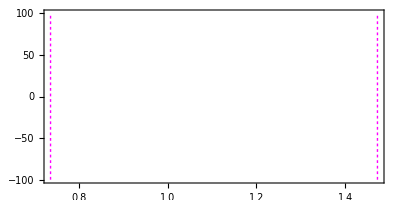

```mathematica
p$RT=Show[Graphics[Table[{Magenta,Thick,Dashing->Tiny,Line[{{L$ram$units[[j]],-100},{L$ram$units[[j]],100}}]},{j,1,Length[L$ram$units]}]],Frame->True,AspectRatio->.5]
```

-25

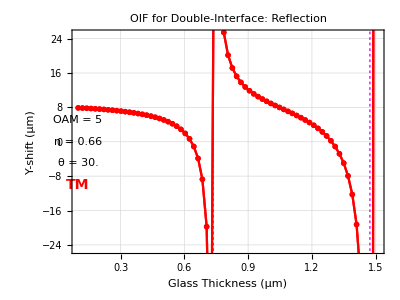

```mathematica
p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.03}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmax =25;
vmin = -25

p$R1$final$y=Show[p$R1$y,p$RT,p$R1$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{.1,vmin + 0.6 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{.1,vmin + 0.5(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{.1,vmin + 0.4 (vmax-vmin)},Background->White]}],
Graphics[{Red,Text[font["TM",14],{.1,vmin + 0.3 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

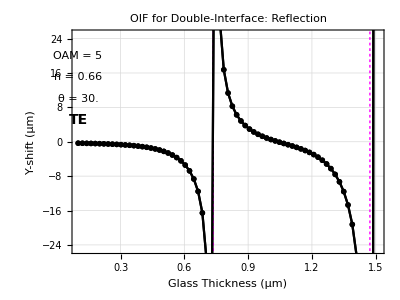

```mathematica
p$R2$y=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.03}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

vmin =-25;
vmax = 25;

p$R2$final$y=Show[p$R2$y,p$RT,p$R2$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{.1,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{.1,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{.1,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{.1,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

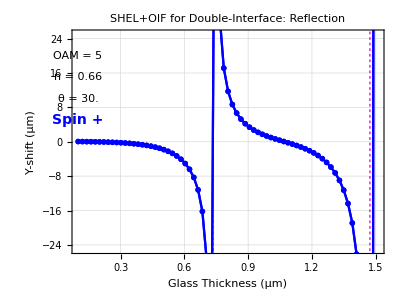

```mathematica
p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.03}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =25;
vmin = -25;

p$R3$final$y=Show[p$R3$y,p$RT,p$R3$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{.1,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{.1,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{.1,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin + ",14],{.1,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

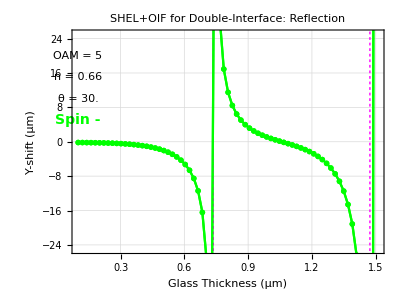

```mathematica
p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.03}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF for Double-Interface: Reflection",16]];

vmax =25;
vmin =-25;

p$R4$final$y=Show[p$R4$y,p$RT,p$R4$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{.1,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{.1,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{.1,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin - ",14],{.1,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotRange->{vmin,vmax}]
```

#### Plot Graphics For Manuscript

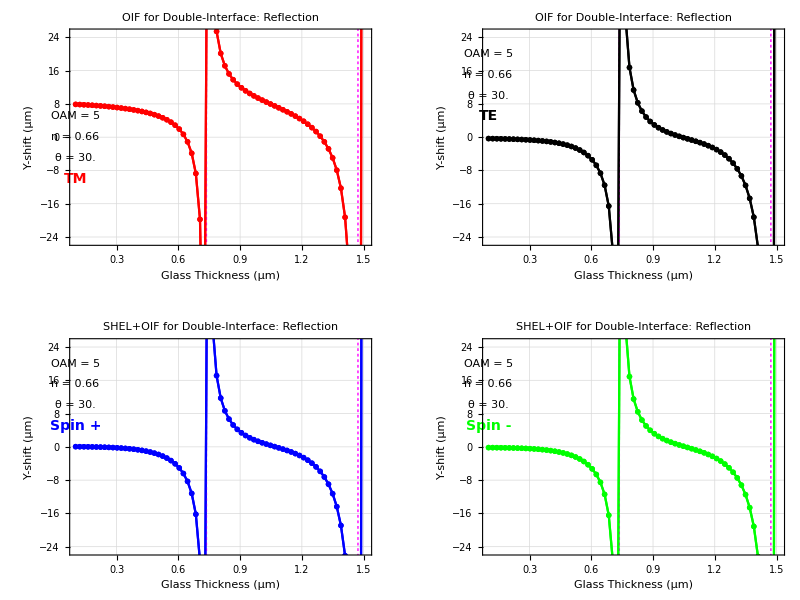

```mathematica
GraphicsGrid[{{p$R1$final$y,p$R2$final$y},{p$R3$final$y,p$R4$final$y}},ImageSize->800]
```

### Centroid Shifts versus Sheet Width: n = 1/1.5168, L = 10 μm, OAM = 5 (Air Gap) FIG 10

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

#### Ramsauer-Townsend Windows

```mathematica
ErB1$TE$func[n_,θ_,L_]=ErB1$TE /. {κx->0,κy->0};
ErB1$TM$func[n_,θ_,L_]=ErB1$TM /. {κx->0,κy->0};
```

```mathematica
1/1.5168
```

0.659283

```mathematica
10.0*2π/(632.8*10^-9)*10^-6
```

99.2918

```mathematica
Manipulate[ParametricPlot[{{θ,Abs[ErB1$TM$func[n,θ Degree,L]]},{θ,Abs[ErB1$TE$func[n,θ Degree,L]]}},{θ,10 ,80 },AspectRatio->1,PlotStyle->{Red,Blue}],{n,0.5,2},{L,0.1,200.0}]
```

#### Analysis

```mathematica
Clear[plots,k0,β];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1/1.5168,k0->1,p->0,ℓ->5,θ->θloop Degree, L->99.29180321080256};

Print["θ: ",θloop];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)


βtab = Table[ArcCos[κvec.nvec] /. params$here/.{κx->κtab[[i,j,1]],κy->κtab[[i,j,2]]},{i,1,dimset},{j,1,dimset}];

R1tab = Table[-ErB1$TM /.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];
R2tab = Table[ ErB1$TE/.β->βtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}];


Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eRtab = Table[{(f[[1]]R1tab[[i,j]]-f[[2]]κtab[[i,j,2]] Cot[θ](R1tab[[i,j]]+R2tab[[i,j]])),f[[2]]R2tab[[i,j]] + f[[1]]κtab[[i,j,2]] Cot[θ](R1tab[[i,j]]+R2tab[[i,j]] ),-(f[[1]]R1tab[[i,j]] κtab[[i,j,1]] + f[[2]]R2tab[[i,j]]  κtab[[i,j,2]])}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,θloop,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,θloop,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,θloop,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,θloop,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{θloop,10.0,80.0,0.2}]
```

θ: 40.

TM (Reflected) = {-27.3388,-53.3719} μm

TE (Reflected) = shift$R2 μm

spin+ (Reflected) = shift$R3 μm

spin- (Reflected) = shift$R4 μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1.5168,θ->60.0 Degree,k0->1,p->0,ℓ->5,L->Lloop}
```

{wk→20000.,n→1.5168,θ→1.0472,k0→1,p→0,ℓ→5,L→Lloop}

```mathematica
{shift$tab$R1,shift$tab$R2,shift$tab$R3,shift$tab$R4}
```

{shift$tab$R1,shift$tab$R2,shift$tab$R3,shift$tab$R4}

```mathematica
shift$all={{{5,10.,{-2.873433281028937,40.71037314929974}},{5,10.2,{-2.954446272078227,60.40138900201351}},{5,10.4,{-3.0287897884628707,109.47753069525481}},{5,10.6,{-3.0944888860192035,475.47323616646395}},{5,10.8,{-3.1515702511857406,-207.1187841900086}},{5,11.,{-3.1973525813703807,-85.00566361224834}},{5,11.2,{-3.232561088285562,-52.654135383686594}},{5,11.4,{-3.2576736514223676,-37.34282449013754}},{5,11.6,{-3.2739450232408567,-28.20020232893579}},{5,11.8,{-3.283269761967263,-21.98424676209534}},{5,12.,{-3.2880362654633983,-17.387671426125188}},{5,12.2,{-3.290954510062228,-13.778726432188842}},{5,12.4,{-3.2948818793011756,-10.809915598190901}},{5,12.6,{-3.3026682739146835,-8.268461626588433}},{5,12.8,{-3.3170317987198907,-6.010286037004648}},{5,13.,{-3.3404653454604754,-3.927290424445635}},{5,13.2,{-3.3751651822986566,-1.9291688416152488}},{5,13.4,{-3.422966445566738,0.06830364509358287}},{5,13.6,{-3.4852673818899578,2.1525621622234317}},{5,13.8,{-3.5629242503234977,4.423799682877167}},{5,14.,{-3.656102521659409,7.0075118766063165}},{5,14.2,{-3.7640791014539485,10.074389144024336}},{5,14.4,{-3.885007536238275,13.87657814634761}},{5,14.600000000000001,{-4.015686112021371,18.822180852848746}},{5,14.8,{-4.151406494166753,25.648670727778022}},{5,15.,{-4.285998184808237,35.89407799987181}},{5,15.2,{-4.41219757310082,53.49565222749065}},{5,15.4,{-4.522422295514571,92.70358596323587}},{5,15.600000000000001,{-4.60982558799065,276.57495258030104}},{5,15.8,{-4.670768104742713,-299.8204141857819}},{5,16.,{-4.702335261760939,-95.91165017133883}},{5,16.2,{-4.707880768885251,-54.88208677878175}},{5,16.4,{-4.693066123985415,-36.53550966605749}},{5,16.6,{-4.666142000349821,-25.719269455085197}},{5,16.8,{-4.636551153464352,-18.322131939751852}},{5,17.,{-4.613698782135833,-12.740491513517599}},{5,17.2,{-4.606032371008911,-8.186644687806952}},{5,17.4,{-4.620475070755102,-4.19193445668325}},{5,17.6,{-4.662112424452375,-0.4194702394091153}},{5,17.8,{-4.733968411753736,3.42585604508348}},{5,18.,{-4.836718297128585,7.659302881881111}},{5,18.200000000000003,{-4.96825445122089,12.686426862351716}},{5,18.4,{-5.123142558583459,19.126753398190765}},{5,18.6,{-5.292181862969176,28.105655942385813}},{5,18.8,{-5.462484665521916,42.12639249153802}},{5,19.,{-5.618599297583698,68.58540982957717}},{5,19.200000000000003,{-5.7449931880714065,144.65342518422753}},{5,19.4,{-5.831586949197226,-1401.7190293003225}},{5,19.6,{-5.8684973474100826,-140.30359967228614}},{5,19.8,{-5.8642532654059805,-67.06230961706493}},{5,20.,{-5.829701829537929,-40.85898684572106}},{5,20.200000000000003,{-5.782115539395476,-26.599153320428957}},{5,20.4,{-5.740167370830149,-17.117495941952157}},{5,20.6,{-5.7206995677616375,-9.920870548839458}},{5,20.8,{-5.736698061082696,-3.812586762675075}},{5,21.,{-5.796251227864534,1.9720204596259134}},{5,21.200000000000003,{-5.901929774914001,8.092355490082115}},{5,21.4,{-6.050133619780824,15.319541659367342}},{5,21.6,{-6.230378222515048,24.852242038160224}},{5,21.8,{-6.425097849804856,39.13934283662934}},{5,22.,{-6.611086259936374,65.05719236704154}},{5,22.200000000000003,{-6.7636303661404895,135.20203466174715}},{5,22.4,{-6.8613874884080746,1930.6865602606574}},{5,22.6,{-6.903202383966984,-148.82884268309834}},{5,22.8,{-6.89026948522326,-67.49538702975144}},{5,23.,{-6.8461257230761285,-39.15236668589368}},{5,23.200000000000003,{-6.798343505642841,-23.559271942389387}},{5,23.4,{-6.773803279622568,-12.829918669022055}},{5,23.6,{-6.793288365003569,-4.154132742158123}},{5,23.8,{-6.868517203573784,3.9756720455262817}},{5,24.,{-7.000665234229913,12.787190923910652}},{5,24.200000000000003,{-7.179531110904086,23.825387288135584}},{5,24.4,{-7.383622010837852,40.0080845888406}},{5,24.6,{-7.582711155953346,69.61430909803939}},{5,24.8,{-7.744570025236813,156.18060890053627}},{5,25.,{-7.847746038988407,-1435.2324127952113}},{5,25.200000000000003,{-7.881111472458576,-127.58776320535053}},{5,25.4,{-7.865883006116857,-59.68805471614089}},{5,25.6,{-7.831782285324972,-33.07804830725723}},{5,25.8,{-7.814056000895593,-17.242129700223405}},{5,26.,{-7.841532704186777,-5.311770927536225}},{5,26.2,{-7.929946135432061,5.576704838100744}},{5,26.400000000000002,{-8.078861849891243,17.4996522000743}},{5,26.6,{-8.271237381607786,33.193315308719875}},{5,26.8,{-8.476196683708281,58.943590205916635}},{5,27.,{-8.656848694833482,121.00993244272608}},{5,27.2,{-8.782446328440042,839.2327138220815}},{5,27.400000000000002,{-8.846628177822607,-166.89739239605538}},{5,27.6,{-8.860824674718478,-67.37398500817827}},{5,27.8,{-8.860388630559802,-34.22804580447734}},{5,28.,{-8.882661615880767,-15.073781884546245}},{5,28.2,{-8.954915883037332,-0.2640999289961067}},{5,28.400000000000002,{-9.085898363522881,14.178967888560777}},{5,28.6,{-9.263577749329057,31.751085106115895}},{5,28.8,{-9.458964051871037,59.21760787254814}},{5,29.,{-9.636463955617582,124.01046731021047}},{5,29.200000000000003,{-9.767965203309254,943.4104525480543}},{5,29.400000000000002,{-9.852901232893478,-159.76029456878152}},{5,29.6,{-9.905015636043476,-62.07425150724182}},{5,29.8,{-9.95903890389672,-27.7107244532074}},{5,30.,{-10.044478076410146,-6.328184993295432}},{5,30.200000000000003,{-10.174749477068444,12.044129027883917}},{5,30.400000000000002,{-10.342481216514646,32.677413046785524}},{5,30.6,{-10.524306987444852,63.556356387227645}},{5,30.8,{-10.69325759803113,136.87967146498886}},{5,31.,{-10.830433622292366,1703.9698583882096}},{5,31.200000000000003,{-10.949723964301992,-138.263326622346}},{5,31.400000000000002,{-11.058671897752237,-49.24485449818755}},{5,31.6,{-11.182581416190484,-13.405750295073377}},{5,31.8,{-11.33178725041788,12.17750984636687}},{5,32.,{-11.501556240433782,38.022019297996415}},{5,32.2,{-11.677862586118849,73.75609504130918}},{5,32.400000000000006,{-11.848748292598284,152.3610503644389}},{5,32.6,{-12.008894844096577,1662.4744886574247}},{5,32.8,{-12.179284971330976,-102.5293036861542}},{5,33.,{-12.353671576490493,12.248340402774225}},{5,33.2,{-12.538265827038215,123.87129907276054}},{5,33.400000000000006,{-12.41756119673649,-1558.3673598266705}},{5,33.6,{-12.925396046318669,-105.11561753510547}},{5,33.8,{-13.128761123494362,27.334183789770986}},{5,34.,{-13.34475379346549,507.0809281574884}},{5,34.2,{-13.574789269608376,-225.68243314069792}},{5,34.400000000000006,{-13.7953342743193,-95.86356940918996}},{5,34.6,{-14.003709046339942,-46.20943769540107}},{5,34.8,{-14.224174995250472,-7.792643687955369}},{5,35.,{-14.500194246564844,41.475785628685934}},{5,35.2,{-14.841368100651959,180.4869632292335}},{5,35.400000000000006,{-15.185729620582803,-475.41653310310613}},{5,35.6,{-15.424113634742065,-109.27657600104637}},{5,35.8,{-15.569957985702755,-42.959909493067336}},{5,36.,{-15.794988687064475,1.5144921436258447}},{5,36.2,{-16.286120543109067,62.03625508305745}},{5,36.400000000000006,{-16.97006053542044,316.50697069908523}},{5,36.6,{-17.441764453715738,-254.701044247462}},{5,36.8,{-17.42373203972744,-74.41363104980677}},{5,37.,{-17.383367455820746,-13.440974835800878}},{5,37.2,{-18.073398145825415,48.731585184002014}},{5,37.400000000000006,{-19.50357280218393,263.65202571296476}},{5,37.6,{-20.301457050769347,-286.6231817915894}},{5,37.8,{-19.60372023758517,-67.40657686061448}},{5,38.,{-19.329455822911065,3.4685310363439794}},{5,38.2,{-21.426202441344977,107.95549194485125}},{5,38.400000000000006,{-24.283521826791265,-1713.2769736666621}},{5,38.6,{-22.87109503896796,-103.82869352501163}},{5,38.8,{-21.203651428389524,-3.0090824075931715}},{5,39.,{-25.34401626254417,132.5882534344899}},{5,39.2,{-30.442607073031372,-569.5001298876963}},{5,39.400000000000006,{-24.431245215115595,-54.16498993906017}},{5,39.6,{-25.77978292236639,56.21045953972895}},{5,39.8,{-40.635717249806305,-2055.5657821454483}},{5,40.,{-27.33876484160048,-53.37192524241295}},{5,40.2,{-34.049076947002774,113.56810111617825}},{5,40.400000000000006,{-46.208469562285345,-241.28800819176186}},{5,40.6,{-31.502713304183402,42.48825844887989}},{5,40.8,{-51.748206958889014,-159.06807216075921}},{5,41.,{-142.11318172302234,1456.8238074419462}},{5,41.2,{-221.23493274605266,-798.9560646891293}},{5,41.400000000000006,{-5.832106953184677,-0.005224564395951534}},{5,41.6,{-3.7694846496900754,-0.0000408270198039619}},{5,41.8,{-2.9511371909540913,-9.81726237686686*^-7}},{5,42.,{-2.478529908359677,-2.1989284591883565*^-8}},{5,42.2,{-2.1599655332973766,1.7735694784081044*^-8}},{5,42.4,{-1.9260538175306037,1.8800523457366733*^-8}},{5,42.6,{-1.744687910684525,1.7644096618637114*^-8}},{5,42.800000000000004,{-1.5986622151300123,1.6384621843783066*^-8}},{5,43.,{-1.4777980208298078,1.5228195005053443*^-8}},{5,43.2,{-1.3756272819161368,1.4146191675747016*^-8}},{5,43.4,{-1.2878107423358471,1.3132886970523536*^-8}},{5,43.6,{-1.2113105452451642,1.220545554540374*^-8}},{5,43.800000000000004,{-1.143925527046541,1.13352729736864*^-8}},{5,44.,{-1.0840149441658915,1.0528064140711762*^-8}},{5,44.2,{-1.030326405080146,9.783829046479826*^-9}},{5,44.4,{-0.9818844618501741,9.079668149629612*^-9}},{5,44.6,{-0.9379160645739809,8.455655647542835*^-9}},{5,44.800000000000004,{-0.8977992521705431,7.820193374775566*^-9}},{5,45.,{-0.8610269591737977,7.23625507007051*^-9}},{5,45.2,{-0.8271809300750441,6.726740274788646*^-9}},{5,45.4,{-0.7959125578454654,6.1943259381458*^-9}},{5,45.6,{-0.7669285675264372,5.770684422967621*^-9}},{5,45.800000000000004,{-0.7399801570609182,5.335593137108952*^-9}},{5,46.,{-0.714854646420379,4.92912627795151*^-9}},{5,46.2,{-0.6913689757494734,4.545558960155051*^-9}},{5,46.4,{-0.6693645858987727,4.173441413039083*^-9}},{5,46.6,{-0.6487033454493648,3.8471229486450814*^-9}},{5,46.800000000000004,{-0.6292642795305468,3.549428910952307*^-9}},{5,47.,{-0.6109409198619978,3.22883533189855*^-9}},{5,47.2,{-0.5936391403864533,2.9712154915874956*^-9}},{5,47.4,{-0.5772753768418138,2.7078707659361956*^-9}},{5,47.6,{-0.5617751512578221,2.4502509256251407*^-9}},{5,47.800000000000004,{-0.5470718419243729,2.2441550533762972*^-9}},{5,48.,{-0.5331056516355029,2.0380591811274537*^-9}},{5,48.2,{-0.5198227370602782,1.7976139968371362*^-9}},{5,48.400000000000006,{-0.5071744707134747,1.631592321970012*^-9}},{5,48.6,{-0.49511681197387614,1.4541208764223968*^-9}},{5,48.800000000000004,{-0.48360976817219353,1.2995489722357638*^-9}},{5,49.,{-0.4726169318142318,1.1278024120283943*^-9}},{5,49.2,{-0.4621050803656073,1.0075798198832356*^-9}},{5,49.400000000000006,{-0.45204382975306145,8.644576863770942*^-10}},{5,49.6,{-0.44240533250843184,7.098857821904614*^-10}},{5,49.800000000000004,{-0.4331640145613238,5.782134193648114*^-10}},{5,50.,{-0.42429634433158503,4.866152539208807*^-10}},{5,50.2,{-0.4157806301714125,3.549428910952307*^-10}},{5,50.400000000000006,{-0.4075968413138384,2.976940376927741*^-10}},{5,50.6,{-0.3997264501406897,1.9464610156835232*^-10}},{5,50.800000000000004,{-0.3921522918942723,0}},{5,51.,{-0.38485844038438594,0}},{5,51.2,{-0.37783009681677526,0}},{5,51.400000000000006,{-0.3710534910216835,-1.3739724816589575*^-10}},{5,51.6,{-0.36451579263798106,-1.8892121622810667*^-10}},{5,51.800000000000004,{-0.3582050315258095,-2.5761984031105454*^-10}},{5,52.,{-0.35211002632001276,-3.0914380837326546*^-10}},{5,52.2,{-0.34622032005952585,-3.721175471159677*^-10}},{5,52.400000000000006,{-0.34052612193094234,-4.179166298379329*^-10}},{5,52.6,{-0.33501825481711434,-4.6371571255989817*^-10}},{5,52.800000000000004,{-0.3296881075458839,-5.266894513026004*^-10}},{5,53.,{-0.3245275917301728,-5.782134193648114*^-10}},{5,53.2,{-0.31952910252961814,-5.896631900453027*^-10}},{5,53.400000000000006,{-0.3146854829330127,-6.240125020867765*^-10}},{5,53.6,{-0.3099899909661617,-6.698115848087418*^-10}},{5,53.800000000000004,{-0.30543627003697704,-6.984360115099701*^-10}},{5,54.,{-0.3010183217308218,-7.270604382111984*^-10}},{5,54.2,{-0.29673048086146003,-7.442350942319354*^-10}},{5,54.400000000000006,{-0.2925673924627426,-7.785844062734093*^-10}},{5,54.6,{-0.28852399105879745,-7.785844062734093*^-10}},{5,54.800000000000004,{-0.2845954811078211,-8.129337183148832*^-10}},{5,55.,{-0.2807773193579823,-8.415581450161115*^-10}},{5,55.2,{-0.2770651983826514,-8.301083743356202*^-10}},{5,55.400000000000006,{-0.27345503168424906,-8.587328010368484*^-10}},{5,55.6,{-0.2699429394392816,-8.759074570575855*^-10}},{5,55.800000000000004,{-0.26652523573757153,-8.759074570575855*^-10}},{5,56.,{-0.2631984167431948,-9.045318837588137*^-10}},{5,56.2,{-0.25995914937065734,-9.217065397795506*^-10}},{5,56.400000000000006,{-0.25680426126062117,-8.930821130783223*^-10}},{5,56.6,{-0.25373073106477384,-8.930821130783223*^-10}},{5,56.800000000000004,{-0.2507356797440026,-9.045318837588137*^-10}},{5,57.,{-0.24781636212991356,-9.045318837588137*^-10}},{5,57.2,{-0.2449701594481313,-8.988069984185681*^-10}},{5,57.400000000000006,{-0.24219457207059408,-9.274314251197963*^-10}},{5,57.6,{-0.23948721277163912,-9.159816544393049*^-10}},{5,57.800000000000004,{-0.23684580066534855,-9.159816544393049*^-10}},{5,58.,{-0.23426815530319314,-9.102567690990594*^-10}},{5,58.2,{-0.23175219124684068,-9.159816544393049*^-10}},{5,58.400000000000006,{-0.22929591289858461,-9.159816544393049*^-10}},{5,58.6,{-0.22689740992143573,-9.045318837588137*^-10}},{5,58.800000000000004,{-0.2245548526420393,-8.930821130783223*^-10}},{5,59.,{-0.22226648789440828,-9.045318837588137*^-10}},{5,59.2,{-0.22003063504685288,-8.81632342397831*^-10}},{5,59.400000000000006,{-0.21784568244110183,-8.701825717173397*^-10}},{5,59.6,{-0.21571008381997414,-8.701825717173397*^-10}},{5,59.800000000000004,{-0.2136223550641941,-8.701825717173397*^-10}},{5,60.,{-0.21158107128987477,-8.358332596758658*^-10}},{5,60.2,{-0.20958486363685713,-8.358332596758658*^-10}},{5,60.400000000000006,{-0.20763241692150705,-8.587328010368484*^-10}},{5,60.6,{-0.20572246686587084,-8.358332596758658*^-10}},{5,60.800000000000004,{-0.20385379772184792,-8.243834889953746*^-10}},{5,61.,{-0.20202523996406188,-8.358332596758658*^-10}},{5,61.2,{-0.20023566818882768,-8.129337183148832*^-10}},{5,61.400000000000006,{-0.19848399907609235,-8.072088329746375*^-10}},{5,61.6,{-0.19676918944297409,-8.129337183148832*^-10}},{5,61.800000000000004,{-0.19509023449767218,-8.072088329746375*^-10}},{5,62.,{-0.1934461658758313,-7.67134635592918*^-10}},{5,62.2,{-0.19183605042686594,-7.728595209331635*^-10}},{5,62.400000000000006,{-0.19025898830757335,-7.843092916136549*^-10}},{5,62.6,{-0.1887141116482355,-7.442350942319354*^-10}},{5,62.800000000000004,{-0.18720058330459402,-7.556848649124267*^-10}},{5,63.,{-0.1857175952606071,-7.098857821904614*^-10}},{5,63.2,{-0.18426436768384344,-7.270604382111984*^-10}},{5,63.400000000000006,{-0.18284014743701207,-7.041608968502157*^-10}},{5,63.6,{-0.1814442072879283,-7.213355528709527*^-10}},{5,63.800000000000004,{-0.18007584448401698,-6.812613554892331*^-10}},{5,64.,{-0.1787343800710515,-6.812613554892331*^-10}},{5,64.2,{-0.17741915776535105,-6.640866994684961*^-10}},{5,64.4,{-0.17612954300344988,-6.526369287880048*^-10}},{5,64.6,{-0.17486492207191465,-6.583618141282505*^-10}},{5,64.80000000000001,{-0.1736247013917337,-6.068378460660396*^-10}},{5,65.,{-0.17240830670538346,-6.240125020867765*^-10}},{5,65.2,{-0.17121518213222228,-6.182876167465309*^-10}},{5,65.4,{-0.1700447896475259,-6.01112960725794*^-10}},{5,65.6,{-0.16889660830962785,-6.01112960725794*^-10}},{5,65.80000000000001,{-0.1677701336817062,-5.782134193648114*^-10}},{5,66.,{-0.16666487716769665,-5.553138780038287*^-10}},{5,66.2,{-0.16558036530240697,-5.49588992663583*^-10}},{5,66.4,{-0.1645161393793992,-5.381392219830917*^-10}},{5,66.6,{-0.16347175476400366,-5.209645659623547*^-10}},{5,66.80000000000001,{-0.162446780383804,-5.32414336642846*^-10}},{5,67.,{-0.16144079837941921,-5.266894513026004*^-10}},{5,67.2,{-0.16045340335454375,-5.095147952818634*^-10}},{5,67.4,{-0.1594842022728994,-5.037899099416178*^-10}},{5,67.6,{-0.15853281365102664,-4.866152539208807*^-10}},{5,67.80000000000001,{-0.15759886744951182,-4.6371571255989817*^-10}},{5,68.,{-0.15668200450049832,-4.5226594187940687*^-10}},{5,68.2,{-0.15578187623861744,-4.5226594187940687*^-10}},{5,68.4,{-0.15489814412277453,-4.6371571255989817*^-10}},{5,68.6,{-0.15403047958462524,-4.4654105653916116*^-10}},{5,68.80000000000001,{-0.1531785634503621,-4.3509128585866986*^-10}},{5,69.,{-0.1523420858090421,-4.293664005184242*^-10}},{5,69.2,{-0.15152074549162214,-4.0074197381719595*^-10}},{5,69.4,{-0.15071425000798533,-4.0074197381719595*^-10}},{5,69.6,{-0.14992231498017725,-3.7784243245621334*^-10}},{5,69.80000000000001,{-0.1491446642798033,-3.8929220313670464*^-10}},{5,70.,{-0.14838102924371935,-3.8929220313670464*^-10}},{5,70.2,{-0.14763114886867781,-3.4921800575498503*^-10}},{5,70.4,{-0.14689476939341112,-3.3204334973424807*^-10}},{5,70.6,{-0.14617164402956206,-3.549428910952307*^-10}},{5,70.80000000000001,{-0.14546153277848736,-3.263184643940024*^-10}},{5,71.,{-0.1447642022824108,-3.434931204147394*^-10}},{5,71.2,{-0.14407942545230557,-3.0914380837326546*^-10}},{5,71.4,{-0.14340698146216943,-2.5761984031105454*^-10}},{5,71.6,{-0.14274665547995516,-3.034189230330198*^-10}},{5,71.80000000000001,{-0.142098238387051,-3.034189230330198*^-10}},{5,72.,{-0.14146152676110615,-3.263184643940024*^-10}},{5,72.2,{-0.14083632261268603,-2.747944963317915*^-10}},{5,72.4,{-0.1402224332364252,-2.747944963317915*^-10}},{5,72.6,{-0.13961967112515405,-2.6906961099154585*^-10}},{5,72.80000000000001,{-0.13902785366075526,-2.862442670122828*^-10}},{5,73.,{-0.13844680307981397,-2.6906961099154585*^-10}},{5,73.2,{-0.13787634638202018,-2.518949549708089*^-10}},{5,73.4,{-0.1373163150668236,-2.3472029895007194*^-10}},{5,73.6,{-0.13676654507046024,-2.1182075758908928*^-10}},{5,73.80000000000001,{-0.13622687668580366,-2.404451842903176*^-10}},{5,74.,{-0.13569715433336993,-2.3472029895007194*^-10}},{5,74.2,{-0.13517722644681968,-2.0037098690859797*^-10}},{5,74.4,{-0.1346669455817309,-1.83196330887861*^-10}},{5,74.60000000000001,{-0.13416616797478295,-1.717465602073697*^-10}},{5,74.8,{-0.1336747537040532,-1.8892121622810667*^-10}},{5,75.,{-0.13319256640849786,-1.717465602073697*^-10}},{5,75.2,{-0.1327194733394755,-1.5457190418663273*^-10}},{5,75.4,{-0.13225534515465173,-1.6602167486712404*^-10}},{5,75.60000000000001,{-0.13180005587219973,-1.83196330887861*^-10}},{5,75.8,{-0.1313534827677524,-1.431221335061414*^-10}},{5,76.,{-0.13091550629997906,-1.6602167486712404*^-10}},{5,76.2,{-0.13048601008768554,-1.4884701884638705*^-10}},{5,76.4,{-0.1300648807151684,-1.3739724816589575*^-10}},{5,76.60000000000001,{-0.12965200766351614,-1.3739724816589575*^-10}},{5,76.8,{-0.12924728343083183,-1.431221335061414*^-10}},{5,77.,{-0.1288506031601156,-1.202225921451588*^-10}},{5,77.2,{-0.12846186484536046,-1.5457190418663273*^-10}},{5,77.4,{-0.12808096905675778,-1.202225921451588*^-10}},{5,77.60000000000001,{-0.12770781903229558,-1.202225921451588*^-10}},{5,77.8,{-0.12734232051746164,-1.316723628256501*^-10}},{5,78.,{-0.12698438174806878,-1.0877282146466746*^-10}},{5,78.2,{-0.1266339133243075,0}},{5,78.4,{-0.12629082837676778,-1.0877282146466746*^-10}},{5,78.60000000000001,{-0.1259550421370723,0}},{5,78.8,{-0.12562647220694634,0}},{5,79.,{-0.12530503844944493,0}},{5,79.2,{-0.12499066273705782,0}},{5,79.4,{-0.12468326920360451,-1.0304793612442183*^-10}},{5,79.60000000000001,{-0.1243827839637148,0}},{5,79.8,{-0.12408913520442696,0}},{5,80.,{-0.12380225308213984,0}}},{{5,10.,{-2.9034803748213283,39.938175118240885}},{5,10.2,{-2.9943263632036166,59.64057352322024}},{5,10.4,{-3.077782793120291,108.7427041046858}},{5,10.6,{-3.1510066377525376,474.8072188095888}},{5,10.8,{-3.213303886728634,-207.76160691673732}},{5,11.,{-3.2610511691368598,-85.59508235684572}},{5,11.2,{-3.29450741107034,-53.18174418489137}},{5,11.4,{-3.3138810040746196,-37.80938204529509}},{5,11.6,{-3.3204956109114763,-28.612277972970602}},{5,11.8,{-3.316634478137924,-22.35362072367375}},{5,12.,{-3.305334824084101,-17.7304627374775}},{5,12.2,{-3.2901307570949294,-14.114282932922626}},{5,12.4,{-3.2747931116194584,-11.159660213918608}},{5,12.6,{-3.2631076695648153,-8.654860917291671}},{5,12.8,{-3.258714547533082,-6.4560273633003}},{5,13.,{-3.265011059875082,-4.45466387466947}},{5,13.2,{-3.285103696949552,-2.5595704117137172}},{5,13.4,{-3.321783675271379,-0.6851066707137339}},{5,13.6,{-3.3774937120632504,1.258315496690372}},{5,13.8,{-3.4542491896400724,3.3742193175728494}},{5,14.,{-3.5534736157466225,5.793277963218938}},{5,14.2,{-3.675707988137456,8.694060774707115}},{5,14.4,{-3.820162888902352,12.340176311914927}},{5,14.600000000000001,{-3.9841139475718856,17.155333632200627}},{5,14.8,{-4.162214029330958,23.896405551562513}},{5,15.,{-4.345921895383387,34.12256991404663}},{5,15.2,{-4.523405777379946,51.789663371482376}},{5,15.4,{-4.680372076406081,91.15799918109987}},{5,15.600000000000001,{-4.802029025062509,275.29274950043305}},{5,15.8,{-4.877671358280978,-300.7967860069084}},{5,16.,{-4.899510669883566,-96.57987761541365}},{5,16.2,{-4.870922896863775,-55.256352717330444}},{5,16.4,{-4.801646706657074,-36.68971610042814}},{5,16.6,{-4.706987526744452,-25.757668194510575}},{5,16.8,{-4.604429262161239,-18.361300922574408}},{5,17.,{-4.510801090509119,-12.894715515717944}},{5,17.2,{-4.440612652956336,-8.558910474617306}},{5,17.4,{-4.4055517619405835,-4.869915293016549}},{5,17.6,{-4.414703449525635,-1.4740633133498462}},{5,17.8,{-4.474945938816762,1.942395935449793}},{5,18.,{-4.591039449109185,5.718380603433165}},{5,18.200000000000003,{-4.764998475629652,10.293369413547856}},{5,18.4,{-4.994409266670848,16.336915299218106}},{5,18.6,{-5.269568675037319,25.04357730294813}},{5,18.8,{-5.569988439167235,38.999072614780864}},{5,19.,{-5.862199496761637,65.673710046612}},{5,19.200000000000003,{-6.1023719253704884,142.26779846780852}},{5,19.4,{-6.249762819716458,-1403.3011116094285}},{5,19.6,{-6.270387240943642,-141.0843615923466}},{5,19.8,{-6.174039312507192,-67.1057957606369}},{5,20.,{-5.991280201325961,-40.433065963586095}},{5,20.200000000000003,{-5.770614400492429,-26.05190588215936}},{5,20.4,{-5.560664179619458,-16.791789171910327}},{5,20.6,{-5.400484524091908,-10.105598232169426}},{5,20.8,{-5.317669841404599,-4.72769029190544}},{5,21.,{-5.330736425821651,0.17523051659880062}},{5,21.200000000000003,{-5.451852011441488,5.33520111429008}},{5,21.4,{-5.687178195565181,11.618521065388274}},{5,21.6,{-6.032901538471443,20.365819990429156}},{5,21.8,{-6.465813305911474,34.227520728121256}},{5,22.,{-6.930553741248587,60.309191943891136}},{5,22.200000000000003,{-7.3342172650702855,131.3551017885296}},{5,22.4,{-7.565004998274362,1930.0160255270357}},{5,22.6,{-7.561674598747771,-149.46690590267326}},{5,22.8,{-7.32893885205933,-66.78910833518705}},{5,23.,{-6.964089423219592,-37.8361632812255}},{5,23.200000000000003,{-6.583901721960739,-22.447292532302594}},{5,23.4,{-6.282400757536908,-12.600951121646565}},{5,23.6,{-6.119073080406949,-5.287546403180482}},{5,23.8,{-6.128368933880878,1.1899682632873143}},{5,24.,{-6.330911979728315,8.250608180129968}},{5,24.200000000000003,{-6.735045752759344,17.69718779130457}},{5,24.4,{-7.321792605188023,32.84442757406187}},{5,24.6,{-8.01046752810976,62.49652238801021}},{5,24.8,{-8.625538760171052,150.60027143590702}},{5,25.,{-8.93795460078673,-1436.8759589000288}},{5,25.200000000000003,{-8.799278582961499,-127.49907840447575}},{5,25.4,{-8.305678174042365,-57.7491261941905}},{5,25.6,{-7.689502631796334,-30.922552566655902}},{5,25.8,{-7.166931530762655,-16.3183804091467}},{5,26.,{-6.865261764957329,-6.602214299649308}},{5,26.2,{-6.84672033241826,1.5285987275449682}},{5,26.400000000000002,{-7.146117458568108,10.563794511807112}},{5,26.6,{-7.779011819789669,23.803879663995232}},{5,26.8,{-8.698193026022397,48.43746799272084}},{5,27.,{-9.691246070241437,111.82220445572194}},{5,27.2,{-10.326635323241169,834.7431397552152}},{5,27.400000000000002,{-10.227808844906399,-167.21545282420277}},{5,27.6,{-9.477798425688063,-64.62052202319107}},{5,27.8,{-8.544271172673547,-31.42008416086798}},{5,28.,{-7.8215938323000005,-14.681665117391747}},{5,28.2,{-7.494842702025062,-3.753466213822533}},{5,28.400000000000002,{-7.638980262594545,6.178529870873741}},{5,28.6,{-8.303688694211624,19.47479479828307}},{5,28.8,{-9.488300911178472,44.31102028387411}},{5,29.,{-10.943883857703858,110.26072341961834}},{5,29.200000000000003,{-11.922462954882334,936.9811526280301}},{5,29.400000000000002,{-11.65900872768319,-160.0787279249709}},{5,29.6,{-10.406218355407113,-58.74097533119231}},{5,29.8,{-9.09027571687891,-25.924595259290097}},{5,30.,{-8.279418147577054,-9.550007408097056}},{5,30.200000000000003,{-8.152863772426256,2.1626243988616043}},{5,30.400000000000002,{-8.796010479845293,15.901829220491871}},{5,30.6,{-10.285123701181755,41.70977848499872}},{5,30.8,{-12.373863379645258,115.55583278149213}},{5,31.,{-13.78932665284163,1698.5196099997104}},{5,31.200000000000003,{-13.096517585230457,-140.52057767095917}},{5,31.400000000000002,{-11.088259173196612,-49.07286304482905}},{5,31.6,{-9.422847053999016,-18.9109141803477}},{5,31.8,{-8.726489097997664,-3.344239009708899}},{5,32.,{-9.131504368200822,10.694924264389828}},{5,32.2,{-10.813294179199799,35.273285508314956}},{5,32.400000000000006,{-13.719713185560668,108.70137916852104}},{5,32.6,{-15.975520361970004,1645.3487960821817}},{5,32.8,{-14.728666065945601,-135.33572439906766}},{5,33.,{-11.730372410282332,-42.38352239819399}},{5,33.2,{-9.742647434880539,-13.41558952997237}},{5,33.400000000000006,{-9.341022734626657,2.481082918641406}},{5,33.6,{-10.690570959553922,22.5334231735104}},{5,33.8,{-14.20360031867981,78.0541291032827}},{5,34.,{-18.342494203022113,545.6396373016512}},{5,34.2,{-17.233657283937827,-170.54185043528548}},{5,34.400000000000006,{-12.812260889120246,-43.46924680434325}},{5,34.6,{-10.220736981768011,-11.20561590630052}},{5,34.8,{-10.077174515001923,6.385231007277819}},{5,35.,{-12.741562512180336,36.40788643296751}},{5,35.2,{-18.95762494929111,172.71912628492726}},{5,35.400000000000006,{-21.789151685793065,-448.0227627929305}},{5,35.6,{-15.500814162894306,-64.28302422214522}},{5,35.8,{-11.122687681321072,-14.618938678192753}},{5,36.,{-10.589597370763862,5.5572002954546145}},{5,36.2,{-14.320458662839382,41.88591469840386}},{5,36.400000000000006,{-24.046150099257968,300.52669358704327}},{5,36.6,{-23.52811857025965,-211.16041951990167}},{5,36.8,{-13.97920815084872,-33.22245007966067}},{5,37.,{-10.877930377460803,-2.2428588080407454}},{5,37.2,{-13.628988950536165,26.39493271098945}},{5,37.400000000000006,{-26.675551795856254,228.51075583899703}},{5,37.6,{-27.98808415216648,-232.475477057706}},{5,37.8,{-14.10158084436399,-26.042548194977456}},{5,38.,{-11.47968268467957,3.193469716743156}},{5,38.2,{-19.326824850648432,60.1662218285266}},{5,38.400000000000006,{-41.94224125573501,-1704.0653864938238}},{5,38.6,{-18.00422489280693,-43.49747092526685}},{5,38.8,{-11.795709030111103,0.40883263419022575}},{5,39.,{-22.51840952713645,67.46941620965463}},{5,39.2,{-48.379105253976675,-488.90601651716895}},{5,39.400000000000006,{-14.2522892826344,-15.511639937640528}},{5,39.6,{-15.630939960580113,18.965370346403457}},{5,39.8,{-77.58963066330288,-2045.8238640494817}},{5,40.,{-14.847128943934054,-13.71197753724107}},{5,40.2,{-22.44875344747294,38.01675157163465}},{5,40.400000000000006,{-36.688893431696876,-90.71475378965077}},{5,40.6,{-15.95948619823374,10.583978232757676}},{5,40.8,{-30.172117953390803,-41.83969475608887}},{5,41.,{-177.0748982890912,1060.029212852578}},{5,41.2,{-205.5949057038254,-343.4902751236998}},{5,41.400000000000006,{-2.586430742093231,-0.0010176447636994629}},{5,41.6,{-1.714850774657535,-8.318802263484262*^-6}},{5,41.8,{-1.376341181043322,-1.9147451508985622*^-7}},{5,42.,{-1.1843193719242129,1.220545554540374*^-8}},{5,42.2,{-1.0568588923209026,1.9853902359971935*^-8}},{5,42.4,{-0.9645003270709168,1.8960820246893616*^-8}},{5,42.6,{-0.8937039400710812,1.7666996159998096*^-8}},{5,42.800000000000004,{-0.8372632492674971,1.640752138514405*^-8}},{5,43.,{-0.7909442877842225,1.5228195005053443*^-8}},{5,43.2,{-0.7520752640731411,1.4146191675747016*^-8}},{5,43.4,{-0.7188762236282509,1.3150061626544272*^-8}},{5,43.6,{-0.6901097084788135,1.2228355086764722*^-8}},{5,43.800000000000004,{-0.664885276903293,1.13352729736864*^-8}},{5,44.,{-0.6425437274644276,1.0550963682072744*^-8}},{5,44.2,{-0.6225852696228248,9.783829046479826*^-9}},{5,44.4,{-0.6046231988750458,9.091117920310103*^-9}},{5,44.6,{-0.5883530233400471,8.444205876862344*^-9}},{5,44.800000000000004,{-0.5735312999629806,7.854542686817042*^-9}},{5,45.,{-0.5599607668963668,7.253429726091246*^-9}},{5,45.2,{-0.5474796721592491,6.721015389448401*^-9}},{5,45.4,{-0.5359539676816082,6.240125020867765*^-9}},{5,45.6,{-0.5252715018776251,5.776409308307867*^-9}},{5,45.800000000000004,{-0.5153376329809142,5.3184184810882154*^-9}},{5,46.,{-0.506071870042473,4.911951621930774*^-9}},{5,46.2,{-0.497405268852087,4.545558960155051*^-9}},{5,46.4,{-0.48927839008927515,4.196340954400066*^-9}},{5,46.6,{-0.48163968163671406,3.83567317796459*^-9}},{5,46.800000000000004,{-0.474444185111094,3.555153796292553*^-9}},{5,47.,{-0.4676524920504996,3.2402851025790415*^-9}},{5,47.2,{-0.4612298952116082,2.948315950226513*^-9}},{5,47.4,{-0.4551456929274222,2.7250454219569324*^-9}},{5,47.6,{-0.44937261542795887,2.455975810965387*^-9}},{5,47.800000000000004,{-0.44388634802600013,2.2384301680360518*^-9}},{5,48.,{-0.4386651331116142,2.015159639766471*^-9}},{5,48.2,{-0.4336894352978866,1.8319633088786099*^-9}},{5,48.400000000000006,{-0.42894165902377673,1.6201425512895207*^-9}},{5,48.6,{-0.4244059082864047,1.4541208764223968*^-9}},{5,48.800000000000004,{-0.4200677821595964,1.2766494308747814*^-9}},{5,49.,{-0.41591419919447625,1.099177985327166*^-9}},{5,49.2,{-0.41193324659736225,9.961300492027443*^-10}},{5,49.400000000000006,{-0.40811404996000045,8.243834889953746*^-10}},{5,49.6,{-0.4044466598209617,7.156106675307071*^-10}},{5,49.800000000000004,{-0.40092195368995404,5.839383047050569*^-10}},{5,50.,{-0.39753154990547285,4.6371571255989817*^-10}},{5,50.2,{-0.39426773238118334,3.4921800575498503*^-10}},{5,50.400000000000006,{-0.39112338451784395,2.8051938167203715*^-10}},{5,50.6,{-0.3880919308266505,1.9464610156835232*^-10}},{5,50.800000000000004,{-0.38516728555411545,0}},{5,51.,{-0.38234380673986257,0}},{5,51.2,{-0.3796162558905351,0}},{5,51.400000000000006,{-0.3769797618443192,-1.6029678952687838*^-10}},{5,51.6,{-0.37442978816772177,-2.0037098690859797*^-10}},{5,51.800000000000004,{-0.3719621047200655,-2.5761984031105454*^-10}},{5,52.,{-0.36957276143351353,-3.377682350744937*^-10}},{5,52.2,{-0.3672580652131573,-3.8929220313670464*^-10}},{5,52.400000000000006,{-0.365014558840814,-4.4654105653916116*^-10}},{5,52.6,{-0.36283900218595305,-4.6371571255989817*^-10}},{5,52.800000000000004,{-0.3607283550768388,-5.152396806221091*^-10}},{5,53.,{-0.358679761723118,-5.209645659623547*^-10}},{5,53.2,{-0.3566905368329724,-5.839383047050569*^-10}},{5,53.400000000000006,{-0.3547581526233543,-6.411871581075135*^-10}},{5,53.6,{-0.3528802275247875,-6.583618141282505*^-10}},{5,53.800000000000004,{-0.3510545152468363,-7.041608968502157*^-10}},{5,54.,{-0.3492788953663943,-7.270604382111984*^-10}},{5,54.2,{-0.3475513643052647,-7.32785323551444*^-10}},{5,54.400000000000006,{-0.3458700274126441,-7.67134635592918*^-10}},{5,54.6,{-0.34423309135102514,-7.900341769539006*^-10}},{5,54.800000000000004,{-0.3426388574896785,-8.243834889953746*^-10}},{5,55.,{-0.3410857154011832,-8.415581450161115*^-10}},{5,55.2,{-0.33957213732546276,-8.472830303563571*^-10}},{5,55.400000000000006,{-0.3380966727311439,-8.530079156966029*^-10}},{5,55.6,{-0.3366579433520809,-8.415581450161115*^-10}},{5,55.800000000000004,{-0.3352546389165913,-8.759074570575855*^-10}},{5,56.,{-0.33388551257327237,-8.873572277380768*^-10}},{5,56.2,{-0.3325493773816466,-8.988069984185681*^-10}},{5,56.400000000000006,{-0.33124510251083755,-9.159816544393049*^-10}},{5,56.6,{-0.3299716098275385,-9.045318837588137*^-10}},{5,56.800000000000004,{-0.32872787117669156,-9.217065397795506*^-10}},{5,57.,{-0.3275129050553296,-9.159816544393049*^-10}},{5,57.2,{-0.32632577420239933,-8.930821130783223*^-10}},{5,57.400000000000006,{-0.32516558307981197,-9.045318837588137*^-10}},{5,57.6,{-0.324031475319144,-8.701825717173397*^-10}},{5,57.800000000000004,{-0.3229226320785955,-8.988069984185681*^-10}},{5,58.,{-0.32183826934656895,-9.217065397795506*^-10}},{5,58.2,{-0.3207776365562468,-9.217065397795506*^-10}},{5,58.400000000000006,{-0.3197400145704323,-8.988069984185681*^-10}},{5,58.6,{-0.3187247141930787,-8.873572277380768*^-10}},{5,58.800000000000004,{-0.31773107440602527,-8.930821130783223*^-10}},{5,59.,{-0.31675846114387113,-8.81632342397831*^-10}},{5,59.2,{-0.31580626574825665,-8.930821130783223*^-10}},{5,59.400000000000006,{-0.3148739037541878,-9.045318837588137*^-10}},{5,59.6,{-0.3139608137164343,-8.873572277380768*^-10}},{5,59.800000000000004,{-0.31306645604165334,-8.587328010368484*^-10}},{5,60.,{-0.3121903120094339,-8.759074570575855*^-10}},{5,60.2,{-0.31133188257007127,-8.530079156966029*^-10}},{5,60.400000000000006,{-0.3104906876060563,-8.530079156966029*^-10}},{5,60.6,{-0.30966626493022076,-8.701825717173397*^-10}},{5,60.800000000000004,{-0.3088581695472272,-8.358332596758658*^-10}},{5,61.,{-0.30806597269751296,-8.243834889953746*^-10}},{5,61.2,{-0.30728926128480166,-8.072088329746375*^-10}},{5,61.400000000000006,{-0.3065276370917939,-8.072088329746375*^-10}},{5,61.6,{-0.30578071607028157,-7.900341769539006*^-10}},{5,61.800000000000004,{-0.30504812779155865,-7.728595209331635*^-10}},{5,62.,{-0.3043295148109592,-7.728595209331635*^-10}},{5,62.2,{-0.3036245320610193,-7.614097502526722*^-10}},{5,62.400000000000006,{-0.3029328464507352,-7.442350942319354*^-10}},{5,62.6,{-0.3022541361499527,-7.442350942319354*^-10}},{5,62.800000000000004,{-0.30158809032029726,-7.49959979572181*^-10}},{5,63.,{-0.3009344085026116,-7.385102088916897*^-10}},{5,63.2,{-0.300292800244838,-7.156106675307071*^-10}},{5,63.400000000000006,{-0.2996629847413505,-7.041608968502157*^-10}},{5,63.6,{-0.29904469030626557,-6.755364701489874*^-10}},{5,63.800000000000004,{-0.2984376541444464,-6.755364701489874*^-10}},{5,64.,{-0.29784162188206287,-6.812613554892331*^-10}},{5,64.2,{-0.2972563473204207,-6.640866994684961*^-10}},{5,64.4,{-0.29668159209246925,-6.411871581075135*^-10}},{5,64.6,{-0.2961171252677834,-6.469120434477592*^-10}},{5,64.80000000000001,{-0.2955627232037175,-6.411871581075135*^-10}},{5,65.,{-0.29501816916756224,-6.182876167465309*^-10}},{5,65.2,{-0.2944832531189995,-5.953880753855482*^-10}},{5,65.4,{-0.2939577714811064,-6.125627314062852*^-10}},{5,65.6,{-0.29344152680831265,-5.896631900453027*^-10}},{5,65.80000000000001,{-0.2929343275516794,-5.782134193648114*^-10}},{5,66.,{-0.2924359880531753,-5.610387633440743*^-10}},{5,66.2,{-0.29194632804188575,-5.438641073233373*^-10}},{5,66.4,{-0.29146517271416184,-5.381392219830917*^-10}},{5,66.6,{-0.29099235225272957,-5.381392219830917*^-10}},{5,66.80000000000001,{-0.29052770190111393,-5.152396806221091*^-10}},{5,67.,{-0.2900710616144202,-5.152396806221091*^-10}},{5,67.2,{-0.2896222760078106,-5.209645659623547*^-10}},{5,67.4,{-0.2891811941217835,-4.866152539208807*^-10}},{5,67.6,{-0.28874766931340096,-4.751654832403894*^-10}},{5,67.80000000000001,{-0.2883215590501926,-4.6371571255989817*^-10}},{5,68.,{-0.28790272484145724,-4.5226594187940687*^-10}},{5,68.2,{-0.2874910320836907,-4.3509128585866986*^-10}},{5,68.4,{-0.28708634989456433,-4.0074197381719595*^-10}},{5,68.6,{-0.2866885510041522,-4.2364151517817855*^-10}},{5,68.80000000000001,{-0.2862975116518829,-4.064668591574416*^-10}},{5,69.,{-0.2859131114491427,-3.950170884769503*^-10}},{5,69.2,{-0.2855352334021748,-4.0074197381719595*^-10}},{5,69.4,{-0.2851637634598134,-3.8929220313670464*^-10}},{5,69.6,{-0.2847985908798765,-3.721175471159677*^-10}},{5,69.80000000000001,{-0.2844396077940745,-3.549428910952307*^-10}},{5,70.,{-0.28408670912786194,-3.6066777643547633*^-10}},{5,70.2,{-0.28373979273783445,-3.549428910952307*^-10}},{5,70.4,{-0.2833987591312099,-3.263184643940024*^-10}},{5,70.6,{-0.2830635114257534,-3.3204334973424807*^-10}},{5,70.80000000000001,{-0.2827339553097041,-3.2059357905375677*^-10}},{5,71.,{-0.28240999891582685,-3.263184643940024*^-10}},{5,71.2,{-0.28209155275843883,-2.976940376927741*^-10}},{5,71.4,{-0.2817785297276848,-2.976940376927741*^-10}},{5,71.6,{-0.28147084490061564,-3.034189230330198*^-10}},{5,71.80000000000001,{-0.28116841555836297,-2.8051938167203715*^-10}},{5,72.,{-0.2808711611689648,-2.976940376927741*^-10}},{5,72.2,{-0.28057900312402045,-2.8051938167203715*^-10}},{5,72.4,{-0.28029186497913605,-2.6906961099154585*^-10}},{5,72.6,{-0.28000967213905553,-2.3472029895007194*^-10}},{5,72.80000000000001,{-0.27973235193208446,-2.404451842903176*^-10}},{5,73.,{-0.2794598335242165,-2.633447256513002*^-10}},{5,73.2,{-0.2791920478332602,-2.5761984031105454*^-10}},{5,73.4,{-0.2789289275803631,-2.518949549708089*^-10}},{5,73.6,{-0.27867040711826496,-2.1182075758908928*^-10}},{5,73.80000000000001,{-0.2784164224999966,-2.2327052826958058*^-10}},{5,74.,{-0.27816691137583166,-2.1182075758908928*^-10}},{5,74.2,{-0.2779218128902391,-1.83196330887861*^-10}},{5,74.4,{-0.27768106777348095,-2.0037098690859797*^-10}},{5,74.60000000000001,{-0.2774446182099401,-1.9464610156835232*^-10}},{5,74.8,{-0.2772124078953693,-2.0609587224884365*^-10}},{5,75.,{-0.27698438177927104,-1.8892121622810667*^-10}},{5,75.2,{-0.2767604862767186,-1.717465602073697*^-10}},{5,75.4,{-0.2765406691767578,-1.7747144554761534*^-10}},{5,75.60000000000001,{-0.27632487945921025,-1.7747144554761534*^-10}},{5,75.8,{-0.2761130675007699,-1.6602167486712404*^-10}},{5,76.,{-0.2759051848231078,-1.5457190418663273*^-10}},{5,76.2,{-0.27570118417302014,-1.4884701884638705*^-10}},{5,76.4,{-0.2755010194823548,-1.4884701884638705*^-10}},{5,76.60000000000001,{-0.2753046458851852,-1.3739724816589575*^-10}},{5,76.8,{-0.27511201953461467,-1.3739724816589575*^-10}},{5,77.,{-0.27492309778597224,-1.3739724816589575*^-10}},{5,77.2,{-0.2747378389563677,-1.2594747748540445*^-10}},{5,77.4,{-0.2745562025422374,-1.202225921451588*^-10}},{5,77.60000000000001,{-0.27437814899607327,-1.0304793612442183*^-10}},{5,77.8,{-0.2742036397378731,-1.0304793612442183*^-10}},{5,78.,{-0.27403263719521426,0}},{5,78.2,{-0.2738651048032542,0}},{5,78.4,{-0.2737010069074071,0}},{5,78.60000000000001,{-0.2735403086946451,-1.0304793612442183*^-10}},{5,78.8,{-0.2733829763308957,0}},{5,79.,{-0.27322897687516895,-1.0877282146466746*^-10}},{5,79.2,{-0.273078278153609,0}},{5,79.4,{-0.2729308489655909,0}},{5,79.60000000000001,{-0.2727866588203752,0}},{5,79.8,{-0.272645678108855,0}},{5,80.,{-0.2725078779833331,0}}},{{5,10.,{-2.8899985383135482,40.28161487837334}},{5,10.2,{-2.9765369837938724,59.97666601266863}},{5,10.4,{-3.0560535023698963,109.06508185881995}},{5,10.6,{-3.1260773570088207,475.09722486440876}},{5,10.8,{-3.1862171376720525,-207.48355178689644}},{5,11.,{-3.2332360448591753,-85.34189980622854}},{5,11.2,{-3.2675748675252834,-52.956731651252916}},{5,11.4,{-3.2895382282906276,-37.611851747952166}},{5,11.6,{-3.300404188371431,-28.43908232430147}},{5,11.8,{-3.3022781002108768,-22.19944581369337}},{5,12.,{-3.2979122287364104,-17.588222095229682}},{5,12.2,{-3.2904832814509635,-13.975603123711931}},{5,12.4,{-3.283366938644179,-11.015382743500307}},{5,12.6,{-3.2799431473684675,-8.495496648487032}},{5,12.8,{-3.2834507144293417,-6.272131490461854}},{5,13.,{-3.2968929934850664,-4.237135121119395}},{5,13.2,{-3.3229828071899985,-2.2999091372928544}},{5,13.4,{-3.364105678139538,-0.37568972502669606}},{5,13.6,{-3.4222752708852955,1.6238705934057032}},{5,13.8,{-3.4990522178870465,3.80052299167577}},{5,14.,{-3.595396455592965,6.282401268288279}},{5,14.2,{-3.7114251099073936,9.244498542260375}},{5,14.4,{-3.8460574455803025,12.945586609589219}},{5,14.600000000000001,{-3.9965544957971315,17.80324162264438}},{5,14.8,{-4.15801634695005,24.567264398869334}},{5,15.,{-4.322993577239329,34.78978320352265}},{5,15.2,{-4.481485847882113,52.421241444332985}},{5,15.4,{-4.621666978750055,91.72012072575082}},{5,15.600000000000001,{-4.731474856638971,275.7503758161481}},{5,15.8,{-4.802491182512804,-300.4556312306754}},{5,16.,{-4.8283853828624395,-96.35282416655183}},{5,16.2,{-4.812377980291619,-55.13613234198684}},{5,16.4,{-4.7627461223286485,-36.64865207402929}},{5,16.6,{-4.6923652676355045,-25.757998476627957}},{5,16.8,{-4.615925605442335,-18.36120111923995}},{5,17.,{-4.547599333048589,-12.853344452056708}},{5,17.2,{-4.49963622571477,-8.439823330983787}},{5,17.4,{-4.481886305145933,-4.642979735247225}},{5,17.6,{-4.50190404163911,-1.11657603982736}},{5,17.8,{-4.5652104294931135,2.444524626112269}},{5,18.,{-4.6753421992221,6.368633313336734}},{5,18.200000000000003,{-4.833379850823383,11.081450228405865}},{5,18.4,{-5.036694954627658,17.234726658942932}},{5,18.6,{-5.276795715343396,26.001801321169527}},{5,18.8,{-5.536627670831706,39.94720082157179}},{5,19.,{-5.788777795786918,66.52704468083944}},{5,19.200000000000003,{-5.997415047199618,142.9425010059036}},{5,19.4,{-6.129418419666805,-1402.8729900164371}},{5,19.6,{-6.156056218154205,-140.89003638886967}},{5,19.8,{-6.0862538740535,-67.12132190406493}},{5,20.,{-5.945393991070213,-40.581469873604995}},{5,20.200000000000003,{-5.773897270194685,-26.23490678422215}},{5,20.4,{-5.61213542247809,-16.9113272062137}},{5,20.6,{-5.492386612517851,-10.07831871982874}},{5,20.8,{-5.437300107601044,-4.492219890952841}},{5,21.,{-5.461882013694836,0.6549712460624595}},{5,21.200000000000003,{-5.575811764449046,6.066728351093745}},{5,21.4,{-5.783942942695784,12.575234191100565}},{5,21.6,{-6.083387244545732,21.47998385331631}},{5,21.8,{-6.455902555939455,35.387046844649845}},{5,22.,{-6.856688660298641,61.36755210486257}},{5,22.200000000000003,{-7.208296206705601,132.16170386729874}},{5,22.4,{-7.414796026028219,1930.1148579457515}},{5,22.6,{-7.423480062688951,-149.37816892193604}},{5,22.8,{-7.236789530011733,-66.98226326542292}},{5,23.,{-6.93901626541319,-38.159530549811514}},{5,23.200000000000003,{-6.6301172367467265,-22.72913725134552}},{5,23.4,{-6.389131243789089,-12.69182838986347}},{5,23.6,{-6.264845549804627,-5.083452148292158}},{5,23.8,{-6.285060738119879,1.737716367454175}},{5,24.,{-6.467137515250954,9.128920287878625}},{5,24.200000000000003,{-6.820245273380114,18.823695817388646}},{5,24.4,{-7.332782363498407,34.06487467884249}},{5,24.6,{-7.940491604111565,63.603140684817916}},{5,24.8,{-8.491884602366023,151.384914450672}},{5,25.,{-8.780855027672175,-1436.7037282971708}},{5,25.200000000000003,{-8.66893413570885,-127.5767376460632}},{5,25.4,{-8.24239520107245,-58.09195073693932}},{5,25.6,{-7.710509148129801,-31.302515233583662}},{5,25.8,{-7.264332584220219,-16.517278344345584}},{5,26.,{-7.011994765132154,-6.4675108561030195}},{5,26.2,{-7.004553693175018,2.0578739494421643}},{5,26.400000000000002,{-7.27345082972726,11.44660387803615}},{5,26.6,{-7.8398890250117095,24.895759302712694}},{5,26.8,{-8.673918876769006,49.510576710218054}},{5,27.,{-9.591419422126476,112.62737461450246}},{5,27.2,{-10.190707780629586,835.0529872792953}},{5,27.400000000000002,{-10.110454114733773,-167.274906833692}},{5,27.6,{-9.424404103006887,-64.94389450592249}},{5,27.8,{-8.57268985227399,-31.75505994325882}},{5,28.,{-7.919113185538196,-14.7982731679899}},{5,28.2,{-7.6265916104835325,-3.5192156161701895}},{5,28.400000000000002,{-7.760462475596458,6.766805781050184}},{5,28.6,{-8.374480826825893,20.291268971447714}},{5,28.8,{-9.48648938564156,45.135605635160395}},{5,29.,{-10.87724735210212,110.85902215546928}},{5,29.200000000000003,{-11.827494332356675,937.157792388341}},{5,29.400000000000002,{-11.583568182801569,-160.17331909884464}},{5,29.6,{-10.384733195293194,-58.99023613334884}},{5,29.8,{-9.128987473449861,-26.1083176123767}},{5,30.,{-8.357534883197609,-9.510703426633068}},{5,30.200000000000003,{-8.235014034721981,2.458864680650846}},{5,30.400000000000002,{-8.848621149014747,16.362346056783366}},{5,30.6,{-10.291384569345697,42.16476834426868}},{5,30.8,{-12.341272603092472,115.84618900739684}},{5,31.,{-13.743950764813267,1698.4761379790925}},{5,31.200000000000003,{-13.066784084215133,-140.61752973535346}},{5,31.400000000000002,{-11.087850707304815,-49.20266844472116}},{5,31.6,{-9.446438193797453,-18.963962058913268}},{5,31.8,{-8.75685286195634,-3.291548806751197}},{5,32.,{-9.152140707419886,10.800900408560404}},{5,32.2,{-10.81807758326162,35.34910321411006}},{5,32.400000000000006,{-13.713893059814225,108.69534111948961}},{5,32.6,{-15.968461219492497,1645.2343454768252}},{5,32.8,{-14.725866623589138,-135.44642208981088}},{5,33.,{-11.730762410550737,-42.497488721153076}},{5,33.2,{-9.743176015135521,-13.540071633506283}},{5,33.400000000000006,{-9.34102387383304,2.3269172933831195}},{5,33.6,{-10.691002670741529,22.35222546172893}},{5,33.8,{-14.20297231028218,77.86608212421338}},{5,34.,{-18.337304306264727,545.4398813594637}},{5,34.2,{-17.226187977905298,-170.81669148280108}},{5,34.400000000000006,{-12.816581132674612,-43.86660077357809}},{5,34.6,{-10.25124187087134,-11.660759918069564}},{5,34.8,{-10.124005530707944,6.048779508225959}},{5,35.,{-12.762574003089945,36.2929538538536}},{5,35.2,{-18.914191548400797,172.6285838477014}},{5,35.400000000000006,{-21.71101246014937,-448.52005265661273}},{5,35.6,{-15.499235564805453,-65.38976359038527}},{5,35.8,{-11.275044368896715,-15.78093633010085}},{5,36.,{-10.811279549484045,5.189580304490166}},{5,36.2,{-14.395328448062276,42.46327431274283}},{5,36.400000000000006,{-23.848937869628884,300.7899577178217}},{5,36.6,{-23.321770098511372,-212.82152022272845}},{5,36.8,{-14.197463942721775,-36.03239560676201}},{5,37.,{-11.456997146688712,-3.4504447407825127}},{5,37.2,{-13.998836536035043,28.048105069554346}},{5,37.400000000000006,{-26.292718250926068,230.19568894845347}},{5,37.6,{-27.53015579852524,-235.89377143823515}},{5,37.8,{-14.75808657312136,-31.191529333718332}},{5,38.,{-12.677323188069014,3.012867890626935}},{5,38.2,{-19.568901931595622,65.46883087841087}},{5,38.400000000000006,{-40.694779709873174,-1704.9091408381262}},{5,38.6,{-18.7623235230977,-53.11088209915317}},{5,38.8,{-13.871653743243186,-0.5756153345017745}},{5,39.,{-22.97521636860633,77.78385208019608}},{5,39.2,{-46.46563452413744,-497.70292041537266}},{5,39.400000000000006,{-16.919306316377213,-25.869499894237318}},{5,39.6,{-18.353263319814697,28.72763483276596}},{5,39.8,{-73.3951242397369,-2047.1278412926442}},{5,40.,{-18.956061632157805,-26.990150106177737}},{5,40.2,{-25.95495054001635,60.62677255408408}},{5,40.400000000000006,{-39.40166690839698,-133.84353717768826}},{5,40.6,{-22.149094092205846,23.056718776107388}},{5,40.8,{-38.56647001703714,-87.67595477758337}},{5,41.,{-167.69004012345542,1166.3297621012152}},{5,41.2,{-212.50662057362675,-544.9981795811003}},{5,41.400000000000006,{-4.209260151472287,-0.2309408229068239}},{5,41.6,{-2.7421676903534045,-0.22406925594826838}},{5,41.8,{-2.1637392129342916,-0.22044428450173006}},{5,42.,{-1.8314246628783268,-0.21700461042472438}},{5,42.2,{-1.6084122319273944,-0.21371612745521698}},{5,42.4,{-1.445277088685382,-0.21056803973610552}},{5,42.6,{-1.3191959396556672,-0.2075509552494963}},{5,42.800000000000004,{-1.2179627447706027,-0.20465629988041426}},{5,43.,{-1.1343711654819915,-0.2018762145577883}},{5,43.2,{-1.0638512830074636,-0.19920348156372705}},{5,43.4,{-1.0033434920302304,-0.19663146009420962}},{5,43.6,{-0.9507101350199505,-0.19415402993766342}},{5,43.800000000000004,{-0.9044054093743314,-0.19176554138221763}},{5,44.,{-0.863279342576249,-0.18946077088219104}},{5,44.2,{-0.826455843537224,-0.18723488159645738}},{5,44.4,{-0.7932538360273841,-0.1850833882319244}},{5,44.6,{-0.7631345491523475,-0.18300212579710995}},{5,44.800000000000004,{-0.7356652808327289,-0.18098722137273193}},{5,45.,{-0.7104938674375191,-0.17903506918555795}},{5,45.2,{-0.6873303051388786,-0.17714230766306455}},{5,45.4,{-0.6659332664847122,-0.1753057994593125}},{5,45.6,{-0.6461000381455496,-0.1735226128318946}},{5,45.800000000000004,{-0.627658898206815,-0.17179000520579}},{5,46.,{-0.6104632611568424,-0.17010540812264052}},{5,46.2,{-0.5943871249943388,-0.16846641373002144}},{5,46.4,{-0.5793214905015237,-0.16687076233554055}},{5,46.6,{-0.5651715158387185,-0.16531633127193626}},{5,46.800000000000004,{-0.5518542344390279,-0.1638011247583057}},{5,47.,{-0.5392967079027097,-0.16232326434527097}},{5,47.2,{-0.5274345195737452,-0.16088098071121867}},{5,47.4,{-0.5162105365333849,-0.15947260579058228}},{5,47.6,{-0.5055738848456728,-0.15809656539446515}},{5,47.800000000000004,{-0.4954790963377092,-0.15675137315371174}},{5,48.,{-0.4858853936187211,-0.15543562425588303}},{5,48.2,{-0.4767560873011599,-0.1541479898749432}},{5,48.400000000000006,{-0.4680580659305919,-0.15288721237380556}},{5,48.6,{-0.4597613610661592,-0.15165210037520638}},{5,48.800000000000004,{-0.45183877598741595,-0.1504415246512372}},{5,49.,{-0.4442655662342769,-0.14925441405295128}},{5,49.2,{-0.4370191641598837,-0.14808975192086063}},{5,49.400000000000006,{-0.4300789404376068,-0.14694657254695673}},{5,49.6,{-0.42342599665989933,-0.14582395826074399}},{5,49.800000000000004,{-0.41704298454641797,-0.14472103634352643}},{5,50.,{-0.4109139474791967,-0.14363697630336242}},{5,50.2,{-0.4050241815596797,-0.14257098764235931}},{5,50.400000000000006,{-0.39936011313624925,-0.1415223171030036}},{5,50.6,{-0.39390919064969176,-0.1404902468476473}},{5,50.800000000000004,{-0.3886597888100672,-0.13947409227160187}},{5,51.,{-0.3836011235764365,-0.13847320021124915}},{5,51.2,{-0.3787231763593801,-0.13748694710062806}},{5,51.400000000000006,{-0.3740166263414032,-0.13651473739709133}},{5,51.6,{-0.3694727902740415,-0.13555600202413656}},{5,51.800000000000004,{-0.3650835679197041,-0.13461019698598412}},{5,52.,{-0.36084139364776774,-0.13367680191345607}},{5,52.2,{-0.3567391923472349,-0.13275531901632232}},{5,52.400000000000006,{-0.35277034006242214,-0.13184527164635435}},{5,52.6,{-0.3489286281265537,-0.1309462034271426}},{5,52.800000000000004,{-0.3452082308963072,-0.13005767714346872}},{5,53.,{-0.34160367628010435,-0.12917927366502724}},{5,53.2,{-0.3381098191918176,-0.1283105912193649}},{5,53.400000000000006,{-0.3347218172715311,-0.12745124445872463}},{5,53.6,{-0.3314351086901607,-0.1266008635612383}},{5,53.800000000000004,{-0.3282453920322064,-0.1257590936298139}},{5,54.,{-0.32514860790169603,-0.12492559385630227}},{5,54.2,{-0.3221409218849263,-0.12410003696618314}},{5,54.400000000000006,{-0.3192187092134954,-0.1232821084342559}},{5,54.6,{-0.3163785404864382,-0.1224715060781728}},{5,54.800000000000004,{-0.3136171685144405,-0.12166793924550505}},{5,55.,{-0.31093151656092416,-0.12087112851604902}},{5,55.2,{-0.3083186670239487,-0.1200808051236126}},{5,55.400000000000006,{-0.30577585133751395,-0.11929671034917755}},{5,55.6,{-0.3033004404911494,-0.11851859530335362}},{5,55.800000000000004,{-0.3008899364082373,-0.11774622031381612}},{5,56.,{-0.2985419637021777,-0.1169793545131139}},{5,56.2,{-0.29625426241150876,-0.11621777570127226}},{5,56.400000000000006,{-0.29402468085525,-0.11546126962445731}},{5,56.6,{-0.2918511694099519,-0.1147096299234521}},{5,56.800000000000004,{-0.2897317744069682,-0.11396265768139059}},{5,57.,{-0.2876646325277929,-0.11322016108598948}},{5,57.2,{-0.2856479657375371,-0.11248195521772736}},{5,57.400000000000006,{-0.28368007640160153,-0.11174786167200239}},{5,57.6,{-0.2817593429004145,-0.1110177084961585}},{5,57.800000000000004,{-0.2798842152155452,-0.11029132961699682}},{5,58.,{-0.27805321109975556,-0.1095685648350509}},{5,58.2,{-0.2762649126535187,-0.10884925962421563}},{5,58.400000000000006,{-0.274517962483621,-0.10813326471955555}},{5,58.6,{-0.27281106079492,-0.10742043600853196}},{5,58.800000000000004,{-0.27114296223593304,-0.10671063443367998}},{5,59.,{-0.2695124731966912,-0.10600372566628995}},{5,59.2,{-0.26791844903789447,-0.10529957987741215}},{5,59.400000000000006,{-0.26635979170936014,-0.10459807182372997}},{5,59.6,{-0.26483544736846976,-0.10389908042391849}},{5,59.800000000000004,{-0.26334440415891414,-0.10320248867849599}},{5,60.,{-0.2618856901898086,-0.10250818355532634}},{5,60.2,{-0.2604583716293062,-0.10181605587512117}},{5,60.400000000000006,{-0.25906155077531146,-0.1011260001282437}},{5,60.6,{-0.25769436441816296,-0.10043791427433761}},{5,60.800000000000004,{-0.25635598212316785,-0.09975169975950177}},{5,61.,{-0.25504560478220595,-0.0990672612472206}},{5,61.2,{-0.25376246318823314,-0.09838450668706272}},{5,61.400000000000006,{-0.25250581650101234,-0.09770334703988645}},{5,61.6,{-0.25127495116510973,-0.09702369624921534}},{5,61.800000000000004,{-0.2500691795015733,-0.0963454710866663}},{5,62.,{-0.24888783871180292,-0.09566859116912428}},{5,62.2,{-0.24773028958945076,-0.09499297872402195}},{5,62.400000000000006,{-0.24659591568458822,-0.09431855858361476}},{5,62.6,{-0.24548412221597782,-0.09364525817353128}},{5,62.800000000000004,{-0.24439433511501715,-0.09297300721507906}},{5,63.,{-0.24332600017273107,-0.0923017377996682}},{5,63.2,{-0.24227858222111315,-0.09163138438881131}},{5,63.400000000000006,{-0.2412515643259166,-0.09096188349352999}},{5,63.6,{-0.24024444700234535,-0.09029317389762528}},{5,63.800000000000004,{-0.2392567474822684,-0.08962519634853391}},{5,64.,{-0.23828799915890608,-0.08895789363175179}},{5,64.2,{-0.23733775072809724,-0.0882912104563363}},{5,64.4,{-0.23640556569595916,-0.08762509340910724}},{5,64.6,{-0.23549102180639883,-0.08695949089739789}},{5,64.80000000000001,{-0.23459371041137586,-0.08629435308035649}},{5,65.,{-0.23371323607588512,-0.08562963189757063}},{5,65.2,{-0.23284921571922407,-0.08496528084007178}},{5,65.4,{-0.23200127863789224,-0.08430125511063216}},{5,65.6,{-0.23116906559533457,-0.08363751139476927}},{5,65.80000000000001,{-0.23035222867309424,-0.08297400795234412}},{5,66.,{-0.2295504306468003,-0.08231070453168789}},{5,66.2,{-0.22876334471137313,-0.08164756220358023}},{5,66.4,{-0.22799065406310773,-0.08098454359024478}},{5,66.6,{-0.22723205147030745,-0.0803216125046813}},{5,66.80000000000001,{-0.2264872391072622,-0.07965873425408462}},{5,67.,{-0.225755927935961,-0.07899587527345199}},{5,67.2,{-0.22503783762021845,-0.07833300326298033}},{5,67.4,{-0.22433269611920809,-0.07767008719951599}},{5,67.6,{-0.2236402393954931,-0.07700709714763349}},{5,67.80000000000001,{-0.22296021117458129,-0.07634400441420754}},{5,68.,{-0.2222923625785322,-0.07568078133086727}},{5,68.2,{-0.22163645204008406,-0.07501740132841983}},{5,68.4,{-0.2209922448732872,-0.07435383895974988}},{5,68.6,{-0.22035951309603274,-0.07369006964219976}},{5,68.80000000000001,{-0.21973803536707875,-0.07302607004113683}},{5,69.,{-0.21912759643646132,-0.0723618175031898}},{5,69.2,{-0.21852798724281763,-0.07169729056576353}},{5,69.4,{-0.21793900452409362,-0.07103246851622284}},{5,69.6,{-0.21736045073167093,-0.07036733167241196}},{5,69.80000000000001,{-0.21679213378419654,-0.06970186110785995}},{5,70.,{-0.2162338669359107,-0.06903603882352727}},{5,70.2,{-0.21568546853047665,-0.06836984762185838}},{5,70.4,{-0.21514676200670566,-0.06770327116403053}},{5,70.6,{-0.21461757543484117,-0.06703629378675742}},{5,70.80000000000001,{-0.21409774176272892,-0.06636890069693532}},{5,71.,{-0.21358709829485245,-0.06570107783424584}},{5,71.2,{-0.2130854867724814,-0.06503281184825636}},{5,71.4,{-0.212592753253449,-0.06436409009842008}},{5,71.6,{-0.21210874782018288,-0.06369490064262615}},{5,71.80000000000001,{-0.21163332461977913,-0.06302523227154908}},{5,72.,{-0.2111663415720334,-0.062355074296827934}},{5,72.2,{-0.21070766046103898,-0.06168441685448529}},{5,72.4,{-0.21025714674626542,-0.06101325057860872}},{5,72.6,{-0.20981466922479056,-0.06034156679599692}},{5,72.80000000000001,{-0.20938010036906848,-0.05966935737158785}},{5,73.,{-0.20895331582886476,-0.058996614754257715}},{5,73.2,{-0.20853419463735215,-0.058323332074144134}},{5,73.4,{-0.20812261887334244,-0.05764950287930132}},{5,73.6,{-0.20771847364983656,-0.056975121336071105}},{5,73.80000000000001,{-0.20732164711974965,-0.05630018210313546}},{5,74.,{-0.20693203039003769,-0.055624680417389806}},{5,74.2,{-0.2065495171953789,-0.05494861193937103}},{5,74.4,{-0.20617400419014323,-0.05427197290782948}},{5,74.60000000000001,{-0.20580539059917394,-0.05359475999088188}},{5,74.8,{-0.20544357828648657,-0.05291697035471}},{5,75.,{-0.20508847154917292,-0.052238601554787774}},{5,75.2,{-0.20473997728342264,-0.05155965173052749}},{5,75.4,{-0.20439800462958055,-0.050880119359109625}},{5,75.60000000000001,{-0.20406246510954365,-0.050200003318456685}},{5,75.8,{-0.20373327255233786,-0.04951930301318056}},{5,76.,{-0.203410342985345,-0.04883801819138632}},{5,76.2,{-0.20309359454842954,-0.04815614897329655}},{5,76.4,{-0.20278294750538853,-0.04747369596574909}},{5,76.60000000000001,{-0.20247832419815226,-0.0467906600045772}},{5,76.8,{-0.20217964888648776,-0.046107042435128934}},{5,77.,{-0.20188684784532157,-0.04542284490617129}},{5,77.2,{-0.20159984926741684,-0.04473806943858876}},{5,77.4,{-0.20131858319467477,-0.0440527183681346}},{5,77.60000000000001,{-0.20104298137501228,-0.04336679435115557}},{5,77.8,{-0.20077297750853232,-0.04268030046764001}},{5,78.,{-0.20050850682960694,-0.04199324002084675}},{5,78.2,{-0.20024950647327028,-0.04130561667470241}},{5,78.4,{-0.19999591497715333,-0.040617434367928106}},{5,78.60000000000001,{-0.19974767274519964,-0.03992869739991273}},{5,78.8,{-0.1995047215839498,-0.03923941028186592}},{5,79.,{-0.19926700497161082,-0.03854957787421534}},{5,79.2,{-0.19903446774891242,-0.037859205203410316}},{5,79.4,{-0.1988070563881767,-0.037168297702367036}},{5,79.60000000000001,{-0.1985847187013489,-0.036476861050171755}},{5,79.8,{-0.19836740396594488,-0.03578490112055684}},{5,80.,{-0.19815506282200324,-0.035092423999075396}}},{{5,10.,{-2.8899985340599583,40.28769084570766}},{5,10.2,{-2.976536978733074,59.98323761410956}},{5,10.4,{-3.0560534965705872,109.0721444163175}},{5,10.6,{-3.126077350625574,475.10475685538245}},{5,10.8,{-3.1862171308193648,-207.4755617813029}},{5,11.,{-3.2332360378519156,-85.33350443112187}},{5,11.2,{-3.2675748605981725,-52.9479773041896}},{5,11.4,{-3.2895382217413585,-37.60279057039788}},{5,11.6,{-3.300404182526323,-28.429766529431756}},{5,11.8,{-3.3022780952932,-22.189922520440376}},{5,12.,{-3.2979122249808857,-17.578528368355958}},{5,12.2,{-3.2904832789377387,-13.965761547426428}},{5,12.4,{-3.2833669374362278,-11.005397756655851}},{5,12.6,{-3.2799431474944147,-8.48535171128304}},{5,12.8,{-3.2834507157689647,-6.261787027344175}},{5,13.,{-3.2968929958551687,-4.226527128459591}},{5,13.2,{-3.3229828104360086,-2.2889483688629513}},{5,13.4,{-3.3641056819007877,-0.36426147062932007}},{5,13.6,{-3.4222752748354663,1.6359059469329122}},{5,13.8,{-3.4990522215337982,3.8133281926270146}},{5,14.,{-3.595396458421059,6.29615852197672}},{5,14.2,{-3.7114251112870913,9.259402938792514}},{5,14.4,{-3.846057444790268,12.961835492655494}},{5,14.600000000000001,{-3.9965544921503793,17.821018839157375}},{5,14.8,{-4.1580163397996674,24.586719043557963}},{5,15.,{-4.322993566144501,34.811004010844485}},{5,15.2,{-4.481485832756966,52.444230433558126}},{5,15.4,{-4.621666960001055,91.74477239250363}},{5,15.600000000000001,{-4.731474835330947,275.7764672842705}},{5,15.8,{-4.802491160094152,-300.42839354473057}},{5,16.,{-4.828385361062076,-96.32484380498298}},{5,16.2,{-4.81237796095868,-55.10779137309063}},{5,16.4,{-4.762746106980231,-36.62028667685842}},{5,16.6,{-4.692365257141789,-25.729845231158844}},{5,16.8,{-4.615925600163991,-18.333363773419073}},{5,17.,{-4.54759933269937,-12.825779494368211}},{5,17.2,{-4.499636229636317,-8.412340564323417}},{5,17.4,{-4.481886312239065,-4.615252459838876}},{5,17.6,{-4.501904050552756,-1.0881568178054797}},{5,17.8,{-4.565210438601406,2.4741835413577444}},{5,18.,{-4.675342206612926,6.400152154217625}},{5,18.200000000000003,{-4.8333798543270134,11.11548050569159}},{5,18.4,{-5.036694951948411,17.271888881786268}},{5,18.6,{-5.276795704374515,26.042596021058877}},{5,18.8,{-5.536627650033197,39.991896299609536}},{5,19.,{-5.788777765061458,66.5755627747424}},{5,19.200000000000003,{-5.997415008470768,142.99434313713067}},{5,19.4,{-6.1294183993892615,-1402.818636605421}},{5,19.6,{-6.156056176396892,-140.83445902789282}},{5,19.8,{-6.086253838719507,-67.06562389166191}},{5,20.,{-5.94539396596659,-40.52657438707877}},{5,20.200000000000003,{-5.773897256941575,-26.181315502683052}},{5,20.4,{-5.612135420583153,-16.859039259238713}},{5,20.6,{-5.492386619954478,-10.026843621992617}},{5,20.8,{-5.437300121186196,-4.44064655251566}},{5,21.,{-5.461882029518419,0.7078790237741327}},{5,21.200000000000003,{-5.57581177797695,6.122416734176628}},{5,21.4,{-5.783942948964533,12.635209132180428}},{5,21.6,{-6.083387238345681,21.54559955774454}},{5,21.8,{-6.455902532954041,35.45921907296864}},{5,22.,{-6.856688618655825,61.446432618383724}},{5,22.200000000000003,{-7.208296149107529,132.24643553867944}},{5,22.4,{-7.414795973468046,1930.2034860143008}},{5,22.6,{-7.4234800003220505,-149.28782028273298}},{5,22.8,{-7.236789481516229,-66.89268312865077}},{5,23.,{-6.939016236977683,-38.07231380261547}},{5,23.200000000000003,{-6.630117229018131,-22.64474523080554}},{5,23.4,{-6.389131253132103,-12.609535364716594}},{5,23.6,{-6.264845569767302,-5.001528602413339}},{5,23.8,{-6.285060760807599,1.8217054088553688}},{5,24.,{-6.467137531566878,9.217747204154357}},{5,24.200000000000003,{-6.820245273809481,18.920001969281536}},{5,24.4,{-7.3327823396141865,34.17056079786576}},{5,24.6,{-7.9404915515971926,63.7186777625096}},{5,24.8,{-8.491884525503712,151.50884519261126}},{5,25.,{-8.780854948319538,-1436.574517829991}},{5,25.200000000000003,{-8.668934058886613,-127.44659883797435}},{5,25.4,{-8.242395150029372,-57.964294188606154}},{5,25.6,{-7.710509128504895,-31.17907493819767}},{5,25.8,{-7.264332591880117,-16.397556203998423}},{5,26.,{-7.011994789892283,-6.349011812777298}},{5,26.2,{-7.004553721759371,2.1789967524135}},{5,26.400000000000002,{-7.273450847205336,11.574679088413571}},{5,26.6,{-7.839889016928173,25.034522897612604}},{5,26.8,{-8.673918832544267,49.661941374983336}},{5,27.,{-9.59141934173191,112.7903962173759}},{5,27.2,{-10.190707683174862,835.2236838101618}},{5,27.400000000000002,{-10.11045402381687,-167.10194953490483}},{5,27.6,{-9.424404045271418,-64.77373179480621}},{5,27.8,{-8.572689835110786,-31.58997475762163}},{5,28.,{-7.919113200909512,-14.637133473510104}},{5,28.2,{-7.626591641941778,-3.3579946027283256}},{5,28.400000000000002,{-7.760462502898435,6.933676264898677}},{5,28.6,{-8.37448082973986,20.46908153433985}},{5,28.8,{-9.486489348761848,45.327391301535464}},{5,29.,{-10.877247273092976,111.06401789414637}},{5,29.200000000000003,{-11.827494234541284,937.3713104625064}},{5,29.400000000000002,{-11.58356809612108,-159.95753501251187}},{5,29.6,{-10.384733149654409,-58.77749130431563}},{5,29.8,{-9.128987470982436,-25.90005137368267}},{5,30.,{-8.357534908272607,-9.304133208309546}},{5,30.200000000000003,{-8.235014064147892,2.6693655525113353}},{5,30.400000000000002,{-8.84862115913062,16.58271746231539}},{5,30.6,{-10.291384542742156,42.39849941984869}},{5,30.8,{-12.341272537262018,116.09251305802037}},{5,31.,{-13.743950692857183,1698.730245925383}},{5,31.200000000000003,{-13.066784022002803,-140.36109882625726}},{5,31.400000000000002,{-11.087850685149508,-48.94780661551374}},{5,31.6,{-9.44643820376448,-18.71026093461972}},{5,31.8,{-8.756852883384585,-3.0351288678119763}},{5,32.,{-9.152140719052854,11.064829149109649}},{5,32.2,{-10.818077571817573,35.623295547142135}},{5,32.400000000000006,{-13.71389302607175,108.9790476635189}},{5,32.6,{-15.968461185916043,1645.5242017692517}},{5,32.8,{-14.725866603695161,-135.15297784117456}},{5,33.,{-11.730762410064122,-42.2011894557614}},{5,33.2,{-9.74317601995015,-13.239192280012313}},{5,33.400000000000006,{-9.34102387287126,2.6340930700196514}},{5,33.6,{-10.69100266616162,22.66530407026522}},{5,33.8,{-14.202972318245493,78.18290703259576}},{5,34.,{-18.337304342131134,545.7593110418427}},{5,34.2,{-17.226188023778803,-170.49213946682656}},{5,34.400000000000006,{-12.81658115129194,-43.53240112511933}},{5,34.6,{-10.251241851492601,-11.314994891311361}},{5,34.8,{-10.12400549741201,6.40146839510065}},{5,35.,{-12.762574011207832,36.64391785987116}},{5,35.2,{-18.914191657803354,172.9735958838059}},{5,35.400000000000006,{-21.71101262752212,-448.17378093883036}},{5,35.6,{-15.49923563915454,-65.02829456510602}},{5,35.8,{-11.275044325570782,-15.39877749086263}},{5,36.,{-10.811279471419507,5.580486445341332}},{5,36.2,{-14.395328481094866,42.84356169379884}},{5,36.400000000000006,{-23.84893815265577,301.15417675094085}},{5,36.6,{-23.32177039345174,-212.45167248521096}},{5,36.8,{-14.197463958178965,-35.63250849498485}},{5,37.,{-11.456997006961435,-3.028822581293086}},{5,37.2,{-13.998836505979396,28.45931032892326}},{5,37.400000000000006,{-26.292718680195147,230.57743700173287}},{5,37.6,{-27.530156293733548,-235.50884360649263}},{5,37.8,{-14.758086528953871,-30.764535030435386}},{5,38.,{-12.677322976586025,3.4580037896997196}},{5,38.2,{-19.568902095355966,65.8846801416278}},{5,38.400000000000006,{-40.69478061167428,-1704.5230964677635}},{5,38.6,{-18.762323597223514,-52.679309297706}},{5,38.8,{-13.871653447323864,-0.11510494091036776}},{5,39.,{-22.975216614118036,78.21009602493294}},{5,39.2,{-46.46563592204567,-497.30471223317386}},{5,39.400000000000006,{-16.91930605572891,-25.40912611119751}},{5,39.6,{-18.353263092027234,29.18433376292375}},{5,39.8,{-73.39512609991245,-2046.7314268135901}},{5,40.,{-18.956061264935038,-26.52487095702335}},{5,40.2,{-25.954950445229425,61.07751184609105}},{5,40.400000000000006,{-39.401667343265,-133.40306099050696}},{5,40.6,{-22.149093587288135,23.5210158876304}},{5,40.8,{-38.566469620302584,-87.22073072183002}},{5,41.,{-167.6900472381597,1166.7536489497538}},{5,41.2,{-212.50661897363005,-544.5455244955671}},{5,41.400000000000006,{-4.209260030488284,0.2246986364463433}},{5,41.6,{-2.7421676152314594,0.22402011015482537}},{5,41.8,{-2.163739156401049,0.22044311128380265}},{5,42.,{-1.8314246172681654,0.2170046006695198}},{5,42.2,{-1.6084121937252343,0.21371616504481414}},{5,42.4,{-1.4452770558989638,0.21056807752607368}},{5,42.6,{-1.319195911111389,0.2075509905491393}},{5,42.800000000000004,{-1.2179627196040068,0.20465633267255748}},{5,43.,{-1.1343711431320391,0.2018762450199032}},{5,43.2,{-1.0638512629760897,0.19920350985611043}},{5,43.4,{-1.0033434739510425,0.19663148636570843}},{5,43.6,{-0.9507101186983024,0.1941540543542994}},{5,43.800000000000004,{-0.9044053945468783,0.19176556406421336}},{5,44.,{-0.8632793290655197,0.18946079197266866}},{5,44.2,{-0.826455831205821,0.1872349011412159}},{5,44.4,{-0.7932538247150106,0.18508340640271048}},{5,44.6,{-0.763134538790305,0.18300214262827286}},{5,44.800000000000004,{-0.7356652713179694,0.18098723699594405}},{5,45.,{-0.7104938586383703,0.17903508365234322}},{5,45.2,{-0.6873302970667902,0.17714232112799486}},{5,45.4,{-0.6659332590137369,0.17530581193383765}},{5,45.6,{-0.6461000312814121,0.17352262437326343}},{5,45.800000000000004,{-0.6276588918693669,0.1717900158598016}},{5,46.,{-0.6104632553060096,0.1701054179694433}},{5,46.2,{-0.5943871195957718,0.16846642279823984}},{5,46.4,{-0.579321485497974,0.16687077070532294}},{5,46.6,{-0.5651715112588103,0.16531633900625636}},{5,46.800000000000004,{-0.551854230196888,0.16380113181136444}},{5,47.,{-0.5392967040097877,0.16232327084301587}},{5,47.2,{-0.5274345159842421,0.16088098669372386}},{5,47.4,{-0.5162105332186764,0.1594726111834243}},{5,47.6,{-0.5055738818057587,0.15809657032359142}},{5,47.800000000000004,{-0.4954790935840393,0.15675137764774674}},{5,48.,{-0.4858853910940467,0.15543562830337695}},{5,48.2,{-0.4767560850398302,0.15414799352742004}},{5,48.400000000000006,{-0.4680580638352839,0.15288721564843996}},{5,48.6,{-0.4597613591941217,0.151652103289173}},{5,48.800000000000004,{-0.4518387742928499,0.15044152726750978}},{5,49.,{-0.44426556474008183,0.14925441635435518}},{5,49.2,{-0.43701916282026054,0.14808975388449633}},{5,49.400000000000006,{-0.4300789392926298,0.1469465742472477}},{5,49.6,{-0.4234259956752191,0.14582395971486484}},{5,49.800000000000004,{-0.4170429837163096,0.1447210375171279}},{5,50.,{-0.4109139467693109,0.14363697729949249}},{5,50.2,{-0.4050241809814663,0.1425709883923193}},{5,50.400000000000006,{-0.3993601127068829,0.14152231765259257}},{5,50.6,{-0.3939091903519978,0.1404902471968653}},{5,50.800000000000004,{-0.38865978866122014,0.13947409243762354}},{5,51.,{-0.383601123502013,0.13847320025704823}},{5,51.2,{-0.3787231763822796,0.13748694695178104}},{5,51.400000000000006,{-0.3740166265245995,0.1365147371280217}},{5,51.6,{-0.36947279052593646,0.13555600164629414}},{5,51.800000000000004,{-0.36508356828037186,0.13461019646501954}},{5,52.,{-0.3608413941114834,0.13367680127799378}},{5,52.2,{-0.35673919293117323,0.1327553182434628}},{5,52.400000000000006,{-0.35277034073223373,0.13184527082197087}},{5,52.6,{-0.34892862887651366,0.13094620248253652}},{5,52.800000000000004,{-0.3452082317206906,0.13005767609581473}},{5,53.,{-0.3416036771674616,0.12917927256012438}},{5,53.2,{-0.33810982015932317,0.12831059005721318}},{5,53.400000000000006,{-0.33472181832491005,0.12745124319924983}},{5,53.6,{-0.33143510980078844,0.12660086222734}},{5,53.800000000000004,{-0.3282453932458821,0.12575909221004236}},{5,54.,{-0.3251486091668957,0.12492559243080582}},{5,54.2,{-0.32214092324172416,0.12410003547198807}},{5,54.400000000000006,{-0.31921871065044155,0.12328210691716128}},{5,54.6,{-0.3163785419520088,0.12247150448665467}},{5,54.800000000000004,{-0.31361717006015954,0.1216679376253625}},{5,55.,{-0.31093151815244224,0.12087112690163135}},{5,55.2,{-0.30831866869561525,0.1200808034519461}},{5,55.400000000000006,{-0.30577585306070443,0.11929670867178613}},{5,55.6,{-0.30330044230021314,0.11851859358016315}},{5,55.800000000000004,{-0.3008899382402006,0.11774621854482656}},{5,56.,{-0.2985419656142894,0.1169793527555741}},{5,56.2,{-0.29625426436941954,0.11621777391510801}},{5,56.400000000000006,{-0.29402468287613454,0.11546126784974285}},{5,56.6,{-0.2918511714823604,0.11470962812011322}},{5,56.800000000000004,{-0.28973177652517573,0.11396265586660194}},{5,57.,{-0.28766463469179954,0.11322015926547593}},{5,57.2,{-0.28564796795306774,0.11248195339148895}},{5,57.400000000000006,{-0.2836800787144552,0.11174785988583817}},{5,57.6,{-0.28175934521899304,0.11101770666992007}},{5,57.800000000000004,{-0.27988421757419796,0.11029132777358375}},{5,58.,{-0.27805321352710693,0.10956856304888668}},{5,58.2,{-0.27626491511521944,0.10884925780942697}},{5,58.400000000000006,{-0.27451796501974524,0.1081332629047669}},{5,58.6,{-0.27281106335394373,0.10742043422236774}},{5,58.800000000000004,{-0.2711429648293061,0.1067106326646904}},{5,59.,{-0.2695124758358633,0.1060037238515013}},{5,59.2,{-0.2679184517457653,0.10529957809697281}},{5,59.400000000000006,{-0.2663597944515802,0.10459807004901552}},{5,59.6,{-0.2648354501564889,0.10389907865492892}},{5,59.800000000000004,{-0.2633444069755577,0.10320248692668109}},{5,60.,{-0.2618856930980504,0.10250818182068606}},{5,60.2,{-0.26045837456617243,0.10181605416910534}},{5,60.400000000000006,{-0.2590615537293523,0.1011259984508523}},{5,60.6,{-0.2576943674008282,0.10043791259122133}},{5,60.800000000000004,{-0.2563559851573571,0.09975169805348592}},{5,61.,{-0.2550456078793689,0.09906725960417852}},{5,61.2,{-0.25376246629112104,0.0983845050554704}},{5,61.400000000000006,{-0.25250581964969926,0.09770334544264343}},{5,61.6,{-0.25127495439394504,0.09702369462907279}},{5,61.800000000000004,{-0.25006918273613354,0.09634546951804772}},{5,62.,{-0.24888784195208802,0.09566858962913014}},{5,62.2,{-0.24773029290415935,0.09499297718975266}},{5,62.400000000000006,{-0.2465959190622706,0.09431855707796992}},{5,62.6,{-0.24548412561655972,0.09364525666788644}},{5,62.800000000000004,{-0.24439433852704884,0.09297300574950842}},{5,63.,{-0.2433260036019374,0.09230173635127221}},{5,63.2,{-0.24227858571901809,0.09163138294041533}},{5,63.400000000000006,{-0.24125156786389576,0.09096188209665795}},{5,63.6,{-0.24024445056894894,0.09029317251220302}},{5,63.800000000000004,{-0.23925675108894615,0.0896251949802863}},{5,64.,{-0.2382880027827585,0.08895789228067885}},{5,64.2,{-0.23733775438629898,0.08829120911098824}},{5,64.4,{-0.23640556936561066,0.08762509210383339}},{5,64.6,{-0.2354910255390241,0.08695948959784892}},{5,64.80000000000001,{-0.23459371417262553,0.08629435184950615}},{5,65.,{-0.2337132398371348,0.08562963067817005}},{5,65.2,{-0.23284921953772258,0.08496527964929562}},{5,65.4,{-0.23200128250218985,0.08430125391413111}},{5,65.6,{-0.23116906949398147,0.08363751022689267}},{5,65.80000000000001,{-0.23035223257174114,0.08297400681881684}},{5,66.,{-0.22955043456834678,0.08231070340961036}},{5,66.2,{-0.2287633486672689,0.0816475610815027}},{5,66.4,{-0.2279906580533528,0.08098454247961703}},{5,66.6,{-0.22723205551207648,0.08032161146847705}},{5,66.80000000000001,{-0.2264872431719308,0.07965873322933015}},{5,67.,{-0.22575593202352914,0.0789958742544224}},{5,67.2,{-0.22503784176503544,0.0783330022611254}},{5,67.4,{-0.22433270025830018,0.0776700862205606}},{5,67.6,{-0.22364024355748477,0.07700709622020208}},{5,67.80000000000001,{-0.22296021533657293,0.07634400350967566}},{5,68.,{-0.22229236682639714,0.07568078041488562}},{5,68.2,{-0.2216364562707743,0.07501740047541192}},{5,68.4,{-0.22099224913832677,0.07435383807239265}},{5,68.6,{-0.22035951742404605,0.0736900688063665}},{5,68.80000000000001,{-0.21973803970081696,0.07302606920530358}},{5,69.,{-0.21912760081027371,0.07236181670170586}},{5,69.2,{-0.21852799163952955,0.07169728975855469}},{5,69.4,{-0.21793900896087975,0.07103246775481309}},{5,69.6,{-0.2173604551856317,0.07036733091100221}},{5,69.80000000000001,{-0.2167921382839564,0.06970186036934972}},{5,70.,{-0.2162338714242208,0.06903603807929218}},{5,70.2,{-0.2156854730760356,0.06836984692914726}},{5,70.4,{-0.21514676654653975,0.06770327044269497}},{5,70.6,{-0.21461758002047432,0.06703629311694582}},{5,70.80000000000001,{-0.21409774635981185,0.06636890005574816}},{5,71.,{-0.2135871028919354,0.06570107721595822}},{5,71.2,{-0.21308549141536345,0.06503281122424387}},{5,71.4,{-0.21259275793068036,0.0643640895087569}},{5,71.6,{-0.21210875252031375,0.06369490005868784}},{5,71.80000000000001,{-0.2116333293428095,0.063025231676161}},{5,72.,{-0.21116634631796335,0.06235507375296383}},{5,72.2,{-0.2107076652470431,0.061684416316346066}},{5,72.4,{-0.21025715149219534,0.06101325006336904}},{5,72.6,{-0.20981467402796933,0.060341566309381665}},{5,72.80000000000001,{-0.2093801051951468,0.05966935686779793}},{5,73.,{-0.20895332070074218,0.05899661429626689}},{5,73.2,{-0.20853419952067934,0.0583233316218782}},{5,73.4,{-0.20812262373949497,0.05764950243276026}},{5,73.6,{-0.20771847856178818,0.05697512089525493}},{5,73.80000000000001,{-0.20732165203742617,0.05630018167949395}},{5,74.,{-0.20693203532488885,0.055624679999473174}},{5,74.2,{-0.2065495221474047,0.054948611561528596}},{5,74.4,{-0.2061740091822432,0.054271972507087506}},{5,74.60000000000001,{-0.2058053956084486,0.05359475961876434}},{5,74.8,{-0.20544358330721105,0.052916969982592446}},{5,75.,{-0.20508847659279691,0.05223860122274442}},{5,75.2,{-0.20473998232132173,0.05155965139848413}},{5,75.4,{-0.2043980096903792,0.05088011900416674}},{5,75.60000000000001,{-0.20406247019896673,0.05020000299213821}},{5,75.8,{-0.20373327768756,0.04951930269258698}},{5,76.,{-0.20341034811484224,0.048838017893692284}},{5,76.2,{-0.20309359970655125,0.04815614868705228}},{5,76.4,{-0.20278295270358443,0.04747369565660527}},{5,76.60000000000001,{-0.20247832937917354,0.046790659729782705}},{5,76.8,{-0.20217965405033433,0.046107042183233984}},{5,77.,{-0.20188685306069212,0.0454228446657261}},{5,77.2,{-0.20159985449996204,0.04473806920386846}},{5,77.4,{-0.2013185884157702,0.044052718081890326}},{5,77.60000000000001,{-0.20104298665335657,0.043366794116435264}},{5,77.8,{-0.20077298279260147,0.04268030021002017}},{5,78.,{-0.20050851213657567,0.041993239780401564}},{5,78.2,{-0.20024951175733946,0.04130561645715677}},{5,78.4,{-0.19999592028984692,0.04061743418473178}},{5,78.60000000000001,{-0.19974767809224256,0.03992869718809197}},{5,78.8,{-0.19950472694816737,0.03923941008149494}},{5,79.,{-0.19926701034727815,0.038549577650944813}},{5,79.2,{-0.19903447314747932,0.0378592050144891}},{5,79.4,{-0.19880706178674357,0.0371682975592449}},{5,79.60000000000001,{-0.1985847241228153,0.03647686090132474}},{5,79.8,{-0.19836740937023664,0.03578490096026005}},{5,80.,{-0.1981550682663692,0.03509242383305372}}}};
```

```mathematica
shift$tab$R1=shift$all[[1]];
shift$tab$R2=shift$all[[2]];
shift$tab$R3=shift$all[[3]];
shift$tab$R4=shift$all[[4]];
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### IF Shift Plots

```mathematica
R3y$plotdata
```

{{10.,40.2816},{10.2,59.9767},{10.4,109.065},{10.6,475.097},{10.8,-207.484},{11.,-85.3419},{11.2,-52.9567},{11.4,-37.6119},{11.6,-28.4391},{11.8,-22.1994},{12.,-17.5882},{12.2,-13.9756},{12.4,-11.0154},{12.6,-8.4955},{12.8,-6.27213},{13.,-4.23714},{13.2,-2.29991},{13.4,-0.37569},{13.6,1.62387},{13.8,3.80052},{14.,6.2824},{14.2,9.2445},{14.4,12.9456},{14.6,17.8032},{14.8,24.5673},{15.,34.7898},{15.2,52.4212},{15.4,91.7201},{15.6,275.75},{15.8,-300.456},{16.,-96.3528},{16.2,-55.1361},{16.4,-36.6487},{16.6,-25.758},{16.8,-18.3612},{17.,-12.8533},{17.2,-8.43982},{17.4,-4.64298},{17.6,-1.11658},{17.8,2.44452},{18.,6.36863},{18.2,11.0815},{18.4,17.2347},{18.6,26.0018},{18.8,39.9472},{19.,66.527},{19.2,142.943},{19.4,-1402.87},{19.6,-140.89},{19.8,-67.1213},{20.,-40.5815},{20.2,-26.2349},{20.4,-16.9113},{20.6,-10.0783},{20.8,-4.49222},{21.,0.654971},{21.2,6.06673},{21.4,12.5752},{21.6,21.48},{21.8,35.387},{22.,61.3676},{22.2,132.162},{22.4,1930.11},{22.6,-149.378},{22.8,-66.9823},{23.,-38.1595},{23.2,-22.7291},{23.4,-12.6918},{23.6,-5.08345},{23.8,1.73772},{24.,9.12892},{24.2,18.8237},{24.4,34.0649},{24.6,63.6031},{24.8,151.385},{25.,-1436.7},{25.2,-127.577},{25.4,-58.092},{25.6,-31.3025},{25.8,-16.5173},{26.,-6.46751},{26.2,2.05787},{26.4,11.4466},{26.6,24.8958},{26.8,49.5106},{27.,112.627},{27.2,835.053},{27.4,-167.275},{27.6,-64.9439},{27.8,-31.7551},{28.,-14.7983},{28.2,-3.51922},{28.4,6.76681},{28.6,20.2913},{28.8,45.1356},{29.,110.859},{29.2,937.158},{29.4,-160.173},{29.6,-58.9902},{29.8,-26.1083},{30.,-9.5107},{30.2,2.45886},{30.4,16.3623},{30.6,42.1648},{30.8,115.846},{31.,1698.48},{31.2,-140.618},{31.4,-49.2027},{31.6,-18.964},{31.8,-3.29155},{32.,10.8009},{32.2,35.3491},{32.4,108.695},{32.6,1645.23},{32.8,-135.446},{33.,-42.4975},{33.2,-13.5401},{33.4,2.32692},{33.6,22.3522},{33.8,77.8661},{34.,545.44},{34.2,-170.817},{34.4,-43.8666},{34.6,-11.6608},{34.8,6.04878},{35.,36.293},{35.2,172.629},{35.4,-448.52},{35.6,-65.3898},{35.8,-15.7809},{36.,5.18958},{36.2,42.4633},{36.4,300.79},{36.6,-212.822},{36.8,-36.0324},{37.,-3.45044},{37.2,28.0481},{37.4,230.196},{37.6,-235.894},{37.8,-31.1915},{38.,3.01287},{38.2,65.4688},{38.4,-1704.91},{38.6,-53.1109},{38.8,-0.575615},{39.,77.7839},{39.2,-497.703},{39.4,-25.8695},{39.6,28.7276},{39.8,-2047.13},{40.,-26.9902},{40.2,60.6268},{40.4,-133.844},{40.6,23.0567},{40.8,-87.676},{41.,1166.33},{41.2,-544.998},{41.4,-0.230941},{41.6,-0.224069},{41.8,-0.220444},{42.,-0.217005},{42.2,-0.213716},{42.4,-0.210568},{42.6,-0.207551},{42.8,-0.204656},{43.,-0.201876},{43.2,-0.199203},{43.4,-0.196631},{43.6,-0.194154},{43.8,-0.191766},{44.,-0.189461},{44.2,-0.187235},{44.4,-0.185083},{44.6,-0.183002},{44.8,-0.180987},{45.,-0.179035},{45.2,-0.177142},{45.4,-0.175306},{45.6,-0.173523},{45.8,-0.17179},{46.,-0.170105},{46.2,-0.168466},{46.4,-0.166871},{46.6,-0.165316},{46.8,-0.163801},{47.,-0.162323},{47.2,-0.160881},{47.4,-0.159473},{47.6,-0.158097},{47.8,-0.156751},{48.,-0.155436},{48.2,-0.154148},{48.4,-0.152887},{48.6,-0.151652},{48.8,-0.150442},{49.,-0.149254},{49.2,-0.14809},{49.4,-0.146947},{49.6,-0.145824},{49.8,-0.144721},{50.,-0.143637},{50.2,-0.142571},{50.4,-0.141522},{50.6,-0.14049},{50.8,-0.139474},{51.,-0.138473},{51.2,-0.137487},{51.4,-0.136515},{51.6,-0.135556},{51.8,-0.13461},{52.,-0.133677},{52.2,-0.132755},{52.4,-0.131845},{52.6,-0.130946},{52.8,-0.130058},{53.,-0.129179},{53.2,-0.128311},{53.4,-0.127451},{53.6,-0.126601},{53.8,-0.125759},{54.,-0.124926},{54.2,-0.1241},{54.4,-0.123282},{54.6,-0.122472},{54.8,-0.121668},{55.,-0.120871},{55.2,-0.120081},{55.4,-0.119297},{55.6,-0.118519},{55.8,-0.117746},{56.,-0.116979},{56.2,-0.116218},{56.4,-0.115461},{56.6,-0.11471},{56.8,-0.113963},{57.,-0.11322},{57.2,-0.112482},{57.4,-0.111748},{57.6,-0.111018},{57.8,-0.110291},{58.,-0.109569},{58.2,-0.108849},{58.4,-0.108133},{58.6,-0.10742},{58.8,-0.106711},{59.,-0.106004},{59.2,-0.1053},{59.4,-0.104598},{59.6,-0.103899},{59.8,-0.103202},{60.,-0.102508},{60.2,-0.101816},{60.4,-0.101126},{60.6,-0.100438},{60.8,-0.0997517},{61.,-0.0990673},{61.2,-0.0983845},{61.4,-0.0977033},{61.6,-0.0970237},{61.8,-0.0963455},{62.,-0.0956686},{62.2,-0.094993},{62.4,-0.0943186},{62.6,-0.0936453},{62.8,-0.092973},{63.,-0.0923017},{63.2,-0.0916314},{63.4,-0.0909619},{63.6,-0.0902932},{63.8,-0.0896252},{64.,-0.0889579},{64.2,-0.0882912},{64.4,-0.0876251},{64.6,-0.0869595},{64.8,-0.0862944},{65.,-0.0856296},{65.2,-0.0849653},{65.4,-0.0843013},{65.6,-0.0836375},{65.8,-0.082974},{66.,-0.0823107},{66.2,-0.0816476},{66.4,-0.0809845},{66.6,-0.0803216},{66.8,-0.0796587},{67.,-0.0789959},{67.2,-0.078333},{67.4,-0.0776701},{67.6,-0.0770071},{67.8,-0.076344},{68.,-0.0756808},{68.2,-0.0750174},{68.4,-0.0743538},{68.6,-0.0736901},{68.8,-0.0730261},{69.,-0.0723618},{69.2,-0.0716973},{69.4,-0.0710325},{69.6,-0.0703673},{69.8,-0.0697019},{70.,-0.069036},{70.2,-0.0683698},{70.4,-0.0677033},{70.6,-0.0670363},{70.8,-0.0663689},{71.,-0.0657011},{71.2,-0.0650328},{71.4,-0.0643641},{71.6,-0.0636949},{71.8,-0.0630252},{72.,-0.0623551},{72.2,-0.0616844},{72.4,-0.0610133},{72.6,-0.0603416},{72.8,-0.0596694},{73.,-0.0589966},{73.2,-0.0583233},{73.4,-0.0576495},{73.6,-0.0569751},{73.8,-0.0563002},{74.,-0.0556247},{74.2,-0.0549486},{74.4,-0.054272},{74.6,-0.0535948},{74.8,-0.052917},{75.,-0.0522386},{75.2,-0.0515597},{75.4,-0.0508801},{75.6,-0.0502},{75.8,-0.0495193},{76.,-0.048838},{76.2,-0.0481561},{76.4,-0.0474737},{76.6,-0.0467907},{76.8,-0.046107},{77.,-0.0454228},{77.2,-0.0447381},{77.4,-0.0440527},{77.6,-0.0433668},{77.8,-0.0426803},{78.,-0.0419932},{78.2,-0.0413056},{78.4,-0.0406174},{78.6,-0.0399287},{78.8,-0.0392394},{79.,-0.0385496},{79.2,-0.0378592},{79.4,-0.0371683},{79.6,-0.0364769},{79.8,-0.0357849},{80.,-0.0350924}}

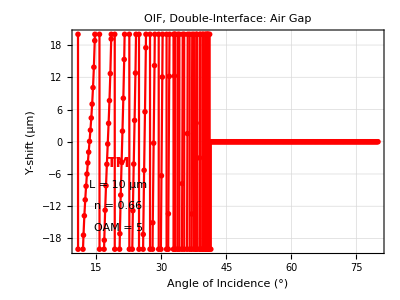

```mathematica
vmax =-20;
vmin = 20;

p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{10,45},{vmin,vmax}},PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF, Double-Interface: Air Gap",16]];



p$R1$final$y=Show[p$R1$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 10 μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Red,Text[font["TM",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

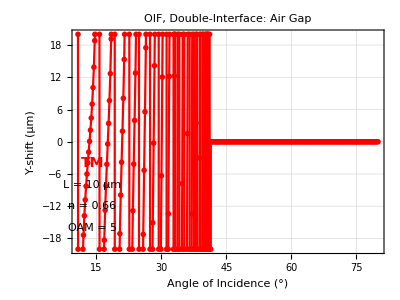

```mathematica
vmax =-20;
vmin = 20;

p$R1$y$zoom=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{10,20},{vmin,vmax}},PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF, Double-Interface: Air Gap",16]];

p$R1$final$y$zoom=Show[p$R1$y$zoom,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{14,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{14,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 10 μm",{14,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Red,Text[font["TM",14],{14,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

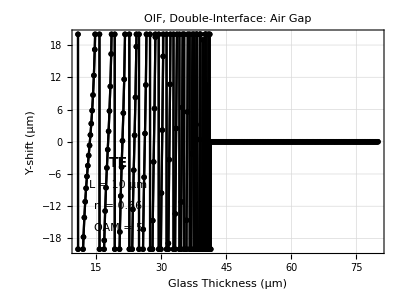

```mathematica
p$R2$y=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{10,45},{vmin,vmax}},PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF, Double-Interface: Air Gap",16]];

p$R2$final$y=Show[p$R2$y,p$R2$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 10 μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

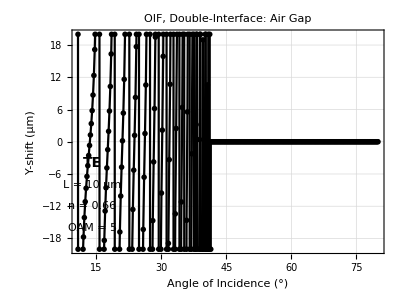

```mathematica
vmax =-20;
vmin = 20;

p$R2$y$zoom=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{10,20},{vmin,vmax}},PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["OIF, Double-Interface: Air Gap",16]];

p$R2$final$y$zoom=Show[p$R2$y$zoom,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{14,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{14,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 10 μm",{14,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text[font["TE",14],{14,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

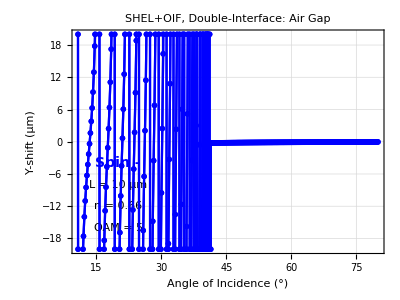

```mathematica
p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{10,45},{vmin,vmax}},PlotStyle->{Blue,Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF, Double-Interface: Air Gap",16]];

p$R3$final$y=Show[p$R3$y,p$R3$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 10 μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Blue,Text[font[" Spin - ",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

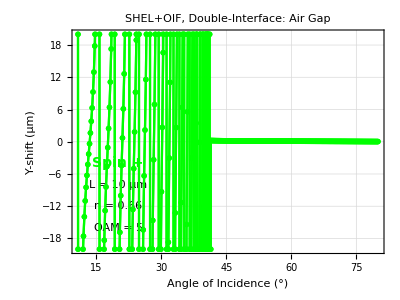

```mathematica
p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{10,45},{vmin,vmax}},PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shift (μm)",14]},PlotLabel->font["SHEL+OIF, Double-Interface: Air Gap",16]];


p$R4$final$y=Show[p$R4$y,p$R4$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{20,vmin + 0.9 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[0.01Round[100n /. params$here]],{20,vmin + 0.8(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["L = 10 μm",{20,vmin + 0.7 (vmax-vmin)},Background->White]}],
Graphics[{Green,Text[font[" Spin + ",14],{20,vmin + 0.6 (vmax-vmin)},Background->White]}],
AspectRatio->.75,FrameLabel->{font["Angle of Incidence (°)",14],font["Y-shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

#### Plot Graphics For Manuscript

```mathematica
ErB1$TE$func[n_,β_,L_]=ErB1$TE;
ErB1$TM$func[n_,β_,L_]=ErB1$TM;
```

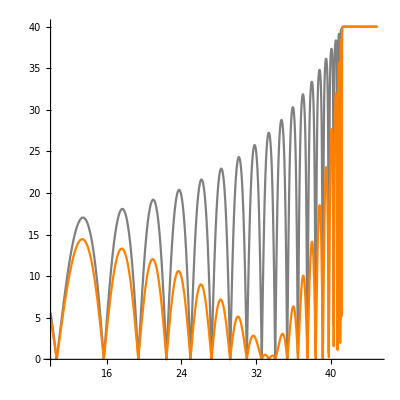

```mathematica
magfac = 40;

p$R=ParametricPlot[{{θ,magfac Abs[ErB1$TE$func[1/1.5168,θ Degree,99.29180321080256]]},{θ,magfac Abs[ErB1$TM$func[1/1.5168,θ Degree,99.29180321080256]]}},{θ,10 ,45 },AspectRatio->1,PlotStyle->{{Thickness[.004],Gray},{Thickness[.004],Orange}}]
```

```mathematica
R2check=ErB1$TE$func[1/1.5168,14.5 Degree,99.29180321080256]

Abs[R2check]^2
```

0.272086-0.208462 ⅈ

0.117487

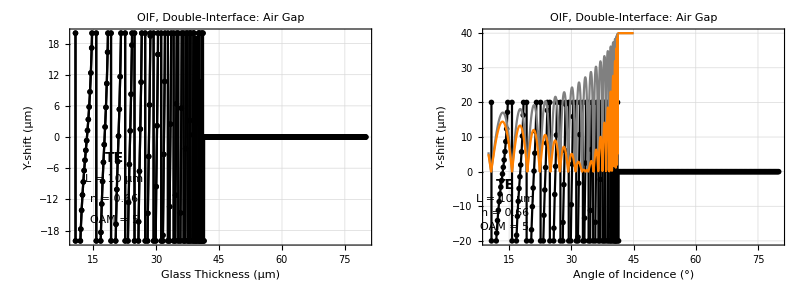

```mathematica
GraphicsRow[{p$R2$final$y,Show[p$R2$final$y$zoom,p$R]},ImageSize->800]
```

```mathematica
GraphicsGrid[{{p$R1$final$y,p$R2$final$y},{p$R3$final$y,p$R4$final$y}},ImageSize->800]
```

-Graphics-

### Centroid Shifts versus Gap Width: n = 1/1.5168, θ = 44°, OAM = 0 (Air Gap) Numerical Version of FIG 8

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.5
```

33.6901

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5
```

41.8103

#### Analysis

```mathematica
Clear[plots,k0];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1/1.5168,θ->44.0 Degree,k0->1,p->0,ℓ->0,L->Lloop};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

Print["k_0L: ",Lloop, ", Actual Gap: ",gap," μm"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;


R1 =Simplify[Expand[Normal[Series[-ErB1$TM/. params$here,{κx,0,1},{κy,0,1}]]],{κx^2->0,κy^2->0,κx κy->0}];

R2 =Simplify[Expand[Normal[Series[ErB1$TE/. params$here,{κx,0,1},{κy,0,1}]]],{κx^2->0,κy^2->0,κx κy->0}];


eR = {(f[[1]]R1-f[[2]]κy Cot[θR](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θR](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,gap,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,gap,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,gap,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,gap,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{Lloop,1.0,15.0,1.0}]
```

k_0L: 1., Actual Gap: 0.100713 μm

TM (Reflected) = {-0.1831,0} μm

TE (Reflected) = {-0.10661,0} μm

spin+ (Reflected) = {-0.127882,0.196211} μm

spin- (Reflected) = {-0.127882,-0.196211} μm

k_0L: 2., Actual Gap: 0.201426 μm

TM (Reflected) = {-0.357679,0} μm

TE (Reflected) = {-0.203705,0} μm

spin+ (Reflected) = {-0.25316,0.1949} μm

spin- (Reflected) = {-0.25316,-0.1949} μm

k_0L: 3., Actual Gap: 0.30214 μm

TM (Reflected) = {-0.51586,0} μm

TE (Reflected) = {-0.289141,0} μm

spin+ (Reflected) = {-0.37281,0.193445} μm

spin- (Reflected) = {-0.37281,-0.193445} μm

k_0L: 4., Actual Gap: 0.402853 μm

TM (Reflected) = {-0.651862,0} μm

TE (Reflected) = {-0.363119,0} μm

spin+ (Reflected) = {-0.481324,0.192218} μm

spin- (Reflected) = {-0.481324,-0.192218} μm

k_0L: 5., Actual Gap: 0.503566 μm

TM (Reflected) = {-0.763195,0} μm

TE (Reflected) = {-0.425723,0} μm

spin+ (Reflected) = {-0.573945,0.19131} μm

spin- (Reflected) = {-0.573945,-0.19131} μm

k_0L: 6., Actual Gap: 0.604279 μm

TM (Reflected) = {-0.850579,0} μm

TE (Reflected) = {-0.477278,0} μm

spin+ (Reflected) = {-0.648959,0.190681} μm

spin- (Reflected) = {-0.648959,-0.190681} μm

k_0L: 7., Actual Gap: 0.704993 μm

TM (Reflected) = {-0.916872,0} μm

TE (Reflected) = {-0.518608,0} μm

spin+ (Reflected) = {-0.7073,0.190258} μm

spin- (Reflected) = {-0.7073,-0.190258} μm

k_0L: 8., Actual Gap: 0.805706 μm

TM (Reflected) = {-0.96585,0} μm

TE (Reflected) = {-0.55094,0} μm

spin+ (Reflected) = {-0.751321,0.189979} μm

spin- (Reflected) = {-0.751321,-0.189979} μm

k_0L: 9., Actual Gap: 0.906419 μm

TM (Reflected) = {-1.00131,0} μm

TE (Reflected) = {-0.575695,0} μm

spin+ (Reflected) = {-0.783794,0.189797} μm

spin- (Reflected) = {-0.783794,-0.189797} μm

k_0L: 10., Actual Gap: 1.00713 μm

TM (Reflected) = {-1.02658,0} μm

TE (Reflected) = {-0.5943,0} μm

spin+ (Reflected) = {-0.807345,0.189679} μm

spin- (Reflected) = {-0.807345,-0.189679} μm

k_0L: 11., Actual Gap: 1.10785 μm

TM (Reflected) = {-1.04438,0} μm

TE (Reflected) = {-0.608062,0} μm

spin+ (Reflected) = {-0.824202,0.189602} μm

spin- (Reflected) = {-0.824202,-0.189602} μm

k_0L: 12., Actual Gap: 1.20856 μm

TM (Reflected) = {-1.0568,0} μm

TE (Reflected) = {-0.618105,0} μm

spin+ (Reflected) = {-0.836142,0.189552} μm

spin- (Reflected) = {-0.836142,-0.189552} μm

k_0L: 13., Actual Gap: 1.30927 μm

TM (Reflected) = {-1.06541,0} μm

TE (Reflected) = {-0.625349,0} μm

spin+ (Reflected) = {-0.844531,0.18952} μm

spin- (Reflected) = {-0.844531,-0.18952} μm

k_0L: 14., Actual Gap: 1.40999 μm

TM (Reflected) = {-1.07134,0} μm

TE (Reflected) = {-0.630523,0} μm

spin+ (Reflected) = {-0.850383,0.189499} μm

spin- (Reflected) = {-0.850383,-0.189499} μm

k_0L: 15., Actual Gap: 1.5107 μm

TM (Reflected) = {-1.07541,0} μm

TE (Reflected) = {-0.634187,0} μm

spin+ (Reflected) = {-0.854442,0.189485} μm

spin- (Reflected) = {-0.854442,-0.189485} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1/1.5168,θ->44.0 Degree,k0->1,p->0,ℓ->0,L->Lloop}
```

{wk→20000.,n→0.659283,θ→0.767945,k0→1,p→0,ℓ→0,L→Lloop}

```mathematica
shift$tab$R4
```

shift$tab$R4

```mathematica
shift$tab$R1={{0,0.10071324798855139,{-0.1831004086249214,0}},{0,0.20142649597710277,{-0.35767867044820517,0}},{0,0.30213974396565413,{-0.5158600001666845,0}},{0,0.40285299195420554,{-0.6518619840520099,0}},{0,0.503566239942757,{-0.7631953794653943,0}},{0,0.6042794879313083,{-0.8505789089273932,0}},{0,0.7049927359198597,{-0.9168722032219218,0}},{0,0.8057059839084111,{-0.9658495254719336,0}},{0,0.9064192318969625,{-1.0013058549219995,0}},{0,1.007132479885514,{-1.0265788996132816,0}},{0,1.1078457278740652,{-1.044380530907391,0}},{0,1.2085589758626165,{-1.056804567538561,0}},{0,1.309272223851168,{-1.06541288506817,0}},{0,1.4099854718397193,{-1.0713428331678558,0}},{0,1.5106987198282709,{-1.0754083974635409,0}}};
```

```mathematica
shift$tab$R2={{0,0.10071324798855139,{-0.10660950725956093,0}},{0,0.20142649597710277,{-0.20370544739405363,0}},{0,0.30213974396565413,{-0.28914054801408123,0}},{0,0.40285299195420554,{-0.36311882926296574,0}},{0,0.503566239942757,{-0.42572303211849577,0}},{0,0.6042794879313083,{-0.47727817949206286,0}},{0,0.7049927359198597,{-0.5186081804113402,0}},{0,0.8057059839084111,{-0.550939965842029,0}},{0,0.9064192318969625,{-0.575694711834631,0}},{0,1.007132479885514,{-0.594299580385484,0}},{0,1.1078457278740652,{-0.6080618670553479,0}},{0,1.2085589758626165,{-0.6181047650422907,0}},{0,1.309272223851168,{-0.625349006069791,0}},{0,1.4099854718397193,{-0.6305229071998419,0}},{0,1.5106987198282709,{-0.6341868012601762,0}}};
```

```mathematica
shift$tab$R3={{0,0.10071324798855139,{-0.12788174729478216,0.19621124156239986}},{0,0.20142649597710277,{-0.25316032452270054,0.19490038453329533}},{0,0.30213974396565413,{-0.37280959645111694,0.19344469175793041}},{0,0.40285299195420554,{-0.48132377997903913,0.1922176319307849}},{0,0.503566239942757,{-0.573944673896301,0.19131004523103387}},{0,0.6042794879313083,{-0.6489588715388102,0.19068068680239195}},{0,0.7049927359198597,{-0.7072999608390322,0.19025823850789056}},{0,0.8057059839084111,{-0.7513206169524694,0.18997943922526783}},{0,0.9064192318969625,{-0.7837944139060831,0.18979712063952525}},{0,1.007132479885514,{-0.8073450893390284,0.18967850766759212}},{0,1.1078457278740652,{-0.8242015807636882,0.18960157187238577}},{0,1.2085589758626165,{-0.8361423619845453,0.18955175900957802}},{0,1.309272223851168,{-0.8445305844881847,0.1895195427955392}},{0,1.4099854718397193,{-0.8503827553089428,0.18949872158220282}},{0,1.5106987198282709,{-0.8544420683160806,0.1894852707293756}}};
```

```mathematica
shift$tab$R4={{0,0.10071324798855139,{-0.1278817472890573,-0.19621124160819897}},{0,0.20142649597710277,{-0.25316032452270054,-0.19490038455619485}},{0,0.30213974396565413,{-0.37280959646256673,-0.1934446918323539}},{0,0.40285299195420554,{-0.48132377997331427,-0.19221763202810793}},{0,0.503566239942757,{-0.5739446738905761,-0.19131004529400758}},{0,0.6042794879313083,{-0.6489588715216356,-0.19068068684246614}},{0,0.7049927359198597,{-0.707299960850482,-0.19025823857086432}},{0,0.8057059839084111,{-0.7513206169467446,-0.18997943925961716}},{0,0.9064192318969625,{-0.7837944139118079,-0.1897971206967741}},{0,1.007132479885514,{-0.8073450893333035,-0.1896785077477405}},{0,1.1078457278740652,{-0.8242015807694131,-0.18960157195253413}},{0,1.2085589758626165,{-0.8361423619902701,-0.18955175906110197}},{0,1.309272223851168,{-0.8445305844881847,-0.18951954288141248}},{0,1.4099854718397193,{-0.8503827553146677,-0.18949872164517656}},{0,1.5106987198282709,{-0.8544420683160806,-0.18948527082097377}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### GH Shift Plots

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

x1$singleboundary$44R=-1.084011849773767;

p$x1$singleboundary$44R=Graphics[{Blue,Thick,Dashing->Tiny,Line[{{-100,x1$singleboundary$44R},{100,x1$singleboundary$44R}}]}];
```

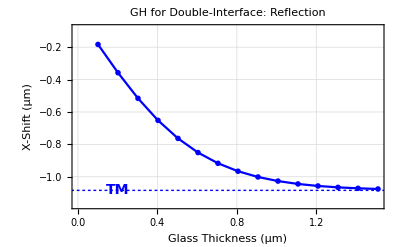

```mathematica
dat = Join[R1x$plotdata];

vmax= +0.1+Max[Transpose[dat][[2]]];
vmin= -0.1+Min[Transpose[dat][[2]]];

p$R1$x=ListLinePlot[dat,PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{vmin,vmax},PlotStyle->{Blue},FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},PlotLabel->font["GH for Double-Interface: Reflection",16]];


p$R1$final$x = Show[p$R1$x,p$x1$singleboundary$44R,Graphics[{Blue,Text[font[" TM ",14],{0.2,x1$singleboundary$44R},Background->White]}]]
```

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

x2$singleboundary$44R=-0.6425425265838541;

p$x2$singleboundary$44R=Graphics[{Darker[Red],Thick,Dashing->Tiny,Line[{{-100,x2$singleboundary$44R},{100,x2$singleboundary$44R}}]}];
```

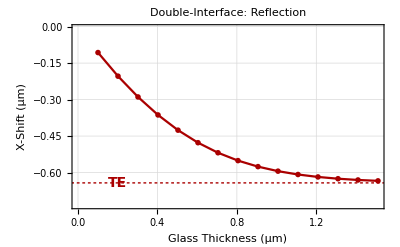

```mathematica
dat = R2x$plotdata;

vmax= 0.1+Max[Transpose[dat][[2]]];
vmin= -0.1+Min[Transpose[dat][[2]]];

p$R2$x=ListLinePlot[dat,PlotMarkers->{{Graphics[Disk[]],.02}},PlotRange->{vmin,vmax},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Darker[Red]},FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},PlotLabel->font["Double-Interface: Reflection",16]];


p$R2$final$x = Show[p$R2$x,p$x2$singleboundary$44R,Graphics[{Darker[Red],Text[font[" TE ",14],{0.2,x2$singleboundary$44R},Background->White]}]]
```

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

x3$singleboundary$44R=-0.8632771881931228;

p$x3$singleboundary$44R=Graphics[{Green,Thick,Dashing->Tiny,Line[{{-100,x3$singleboundary$44R},{100,x3$singleboundary$44R}}]}];
```

```mathematica
dat = R3x$plotdata;

vmax= 0.1+Max[Transpose[dat][[2]]];
vmin= -0.1+Min[Transpose[dat][[2]]];

p$R3$x=ListLinePlot[dat,PlotMarkers->{{Graphics[Disk[]],.02}},PlotRange->{vmin,vmax},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},PlotLabel->font["Double-Interface: Reflection",16]];


p$R3$final$x = Show[p$R3$x,p$x3$singleboundary$44R,Graphics[{Green,Text[font[" Spin^+ ",14],{0.15,x3$singleboundary$44R},Background->White]}],
Graphics[{Magenta,Text[font[" Spin^- ",14],{0.45,x4$singleboundary$44R},Background->White]}]]
```

-Graphics-

```mathematica
x4$singleboundary$44R=-0.8632771881931228;

p$x4$singleboundary$44R=Graphics[{Magenta,Thickness[.01],Dashing->Small,Line[{{-100,x4$singleboundary$44R},{100,x4$singleboundary$44R}}]}];
```

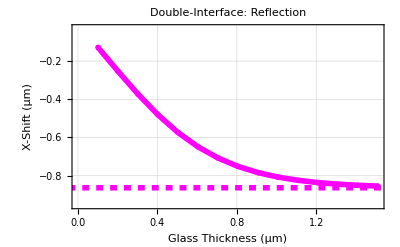

```mathematica
dat = R4x$plotdata;

vmax= 0.1+Max[Transpose[dat][[2]]];
vmin= -0.1+Min[Transpose[dat][[2]]];

p$R4$x=ListLinePlot[dat,PlotMarkers->{{Graphics[Disk[]],.03}},PlotRange->{vmin,vmax},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Magenta,Thickness[.01]},FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},PlotLabel->font["Double-Interface: Reflection",16]];


p$R4$final$x = Show[p$R4$x,p$x4$singleboundary$44R]
```

#### IF Shift Plots

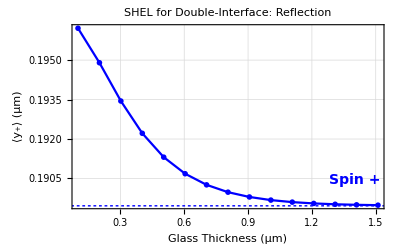

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

y3$singleboundary$44R=0.1894607634398401;

p$y3$singleboundary$44R=Graphics[{Blue,Thick,Dashing->Tiny,Line[{{-100,y3$singleboundary$44R},{100,y3$singleboundary$44R}}]}];

p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue,Green},FrameLabel->{font["Glass Thickness (μm)",14],font["⟨y_+⟩ (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

p$R3$final$y = Show[p$R3$y,p$y3$singleboundary$44R,Graphics[{Blue,Text[font[" Spin + ",14],{1.4,y3$singleboundary$44R+0.001},Background->White]}]]
```

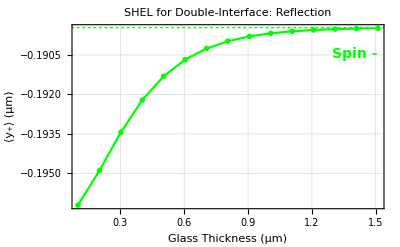

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

y4$singleboundary$44R=-0.1894607634398401;

p$y4$singleboundary$44R=Graphics[{Green,Thick,Dashing->Tiny,Line[{{-100,y4$singleboundary$44R},{100,y4$singleboundary$44R}}]}];

p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["⟨y_+⟩ (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

p$R4$final$y = Show[p$R4$y,p$y4$singleboundary$44R,Graphics[{Green,Text[font[" Spin - ",14],{1.4,y4$singleboundary$44R-0.001},Background->White]}]]
```

#### Plot Graphics For Manuscript

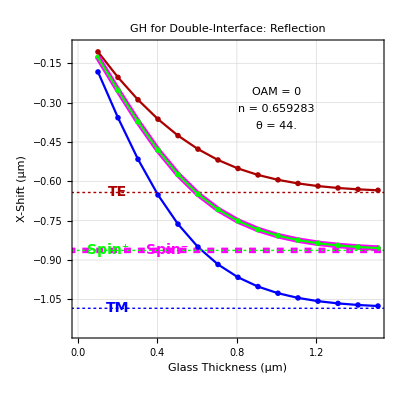

```mathematica
vmin = -1.3;
vmax = 0;

p$GH=Show[p$R1$final$x,p$R2$final$x,p$R4$final$x,p$R3$final$x,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.,vmin + 0.8 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.,vmin + 0.75(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.,vmin + 0.7 (vmax-vmin)},Background->White]}],
AspectRatio->1,FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

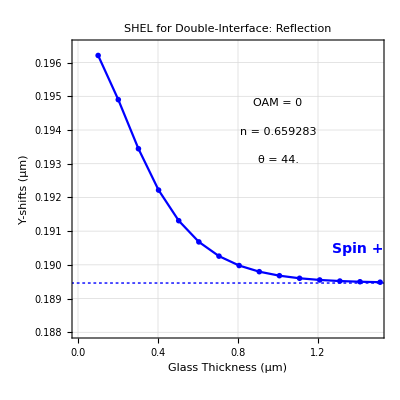

```mathematica
vmin =0.188;
vmax =0.1965;

p$IF$plus=Show[{p$R3$final$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.,vmin + 0.8 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.,vmin + 0.7(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.,vmin + 0.6 (vmax-vmin)},Background->White]}]
},PlotRange->{{0,1.5},{vmin,vmax}},
AspectRatio->1,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shifts (μm)",14]},BaseStyle->{"Tahoma",14}]
```

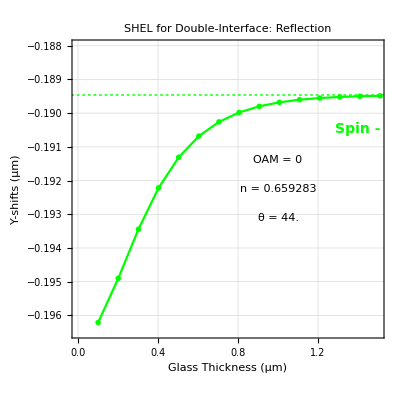

```mathematica
vmax=-0.188;
vmin =-0.1965;


p$IF$minus=Show[{p$R4$final$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.,vmin + 0.6 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.,vmin + 0.5(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.,vmin + 0.4 (vmax-vmin)},Background->White]}]
},PlotRange->{{0,1.5},{vmin,vmax}},
AspectRatio->1,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shifts (μm)",14]},BaseStyle->{"Tahoma",14}]
```

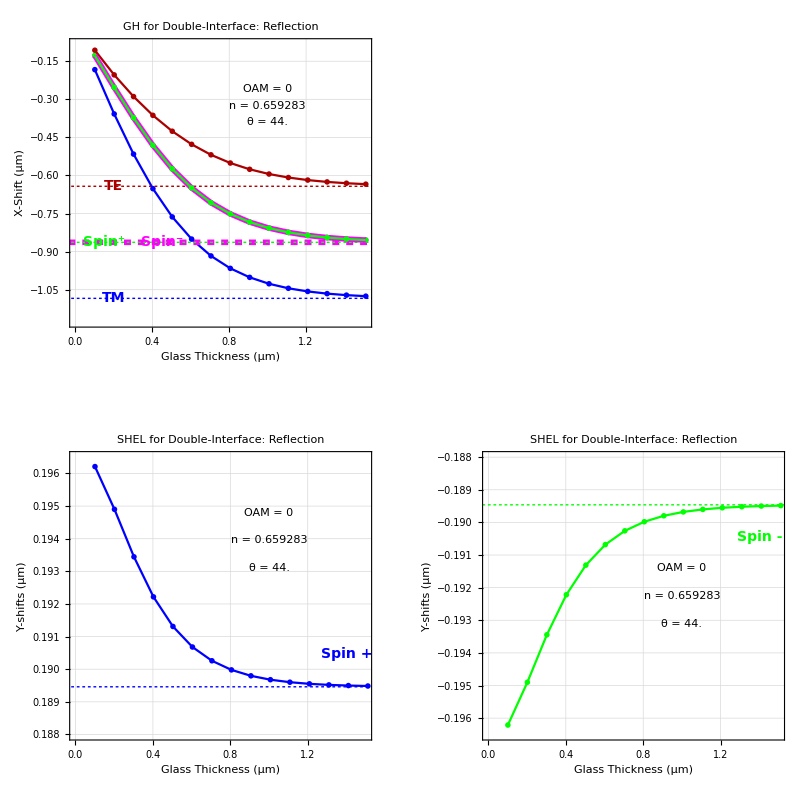

```mathematica
GraphicsGrid[{{p$GH},{p$IF$plus,p$IF$minus}},ImageSize->800]
```

### Centroid Shifts versus Gap Width: n = 1/1.5168, θ = 44°, OAM = 5 (Air Gap) FIG 11

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.1568
```

40.8419

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1.5168
```

56.6038

```mathematica
θcrit = ArcSin[n]/Degree /. n->1/1.5
```

41.8103

#### Analysis

```mathematica
Clear[plots,k0];

fontset = 6;

shift$tab$R1 = {};
shift$tab$R2 = {};
shift$tab$R3 = {};
shift$tab$R4 = {};

λ0 = 2 π;

dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

loopcount = 0;

Do[{
loopcount = loopcount +1;

params$here = {wk->20000.,n->1/1.5168,θ->44.0 Degree,k0->1,p->0,ℓ->5,L->Lloop};

gap = (L*10^6)/(2π/(632.8*10^-9)) /. params$here;

Print["k_0L: ",Lloop, ", Actual Gap: ",gap," μm"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;


R1 =Simplify[Expand[Normal[Series[-ErB1$TM/. params$here,{κx,0,1},{κy,0,1}]]],{κx^2->0,κy^2->0,κx κy->0}];

R2 =Simplify[Expand[Normal[Series[ErB1$TE/. params$here,{κx,0,1},{κy,0,1}]]],{κx^2->0,κy^2->0,κx κy->0}];


eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

shift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

shift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, shift$R1={shift$Rx,shift$Ry},f$flag==2,shift$R2={shift$Rx,shift$Ry},f$flag==3,shift$R3={shift$Rx,shift$Ry},f$flag==4,shift$R4={shift$Rx,shift$Ry}];

},{f$flag,1,4}];

AppendTo[shift$tab$R1 ,{ℓ /. params$here,gap,shift$R1}];
AppendTo[shift$tab$R2 ,{ℓ /. params$here,gap,shift$R2}];
AppendTo[shift$tab$R3 ,{ℓ /. params$here,gap,shift$R3}];
AppendTo[shift$tab$R4 ,{ℓ /. params$here,gap,shift$R4}];

shift$RΔ = shift$R1-shift$R2;

Print["TM (Reflected) = ",shift$R1," μm"];
Print["TE (Reflected) = ",shift$R2," μm"];
Print["spin+ (Reflected) = ",shift$R3," μm"];
Print["spin- (Reflected) = ",shift$R4," μm"];
Print["  "];

},{Lloop,0.05,1.0,0.05}]
```

k_0L: 0.05, Actual Gap: 0.00503566 μm

TM (Reflected) = {-0.00922635,-3.30488} μm

TE (Reflected) = {-0.00543575,-0.488742} μm

spin+ (Reflected) = {-0.00642148,-1.41783} μm

spin- (Reflected) = {-0.00642148,-1.02431} μm

k_0L: 0.1, Actual Gap: 0.0100713 μm

TM (Reflected) = {-0.0184516,-3.30416} μm

TE (Reflected) = {-0.0108698,-0.488808} μm

spin+ (Reflected) = {-0.0128425,-1.41809} μm

spin- (Reflected) = {-0.0128425,-1.02458} μm

k_0L: 0.15, Actual Gap: 0.015107 μm

TM (Reflected) = {-0.0276747,-3.30298} μm

TE (Reflected) = {-0.0163003,-0.488917} μm

spin+ (Reflected) = {-0.0192626,-1.41853} μm

spin- (Reflected) = {-0.0192626,-1.02504} μm

k_0L: 0.2, Actual Gap: 0.0201426 μm

TM (Reflected) = {-0.0368947,-3.30132} μm

TE (Reflected) = {-0.0217257,-0.489068} μm

spin+ (Reflected) = {-0.0256813,-1.41915} μm

spin- (Reflected) = {-0.0256813,-1.02567} μm

k_0L: 0.25, Actual Gap: 0.0251783 μm

TM (Reflected) = {-0.0461103,-3.29918} μm

TE (Reflected) = {-0.0271443,-0.48926} μm

spin+ (Reflected) = {-0.0320981,-1.41993} μm

spin- (Reflected) = {-0.0320981,-1.02648} μm

k_0L: 0.3, Actual Gap: 0.030214 μm

TM (Reflected) = {-0.0553205,-3.29658} μm

TE (Reflected) = {-0.0325543,-0.489492} μm

spin+ (Reflected) = {-0.0385128,-1.42088} μm

spin- (Reflected) = {-0.0385128,-1.02746} μm

k_0L: 0.35, Actual Gap: 0.0352496 μm

TM (Reflected) = {-0.0645243,-3.2935} μm

TE (Reflected) = {-0.0379543,-0.489759} μm

spin+ (Reflected) = {-0.0449247,-1.42198} μm

spin- (Reflected) = {-0.0449247,-1.0286} μm

k_0L: 0.4, Actual Gap: 0.0402853 μm

TM (Reflected) = {-0.0737206,-3.28996} μm

TE (Reflected) = {-0.0433426,-0.490061} μm

spin+ (Reflected) = {-0.0513335,-1.42324} μm

spin- (Reflected) = {-0.0513335,-1.0299} μm

k_0L: 0.45, Actual Gap: 0.045321 μm

TM (Reflected) = {-0.0829084,-3.28595} μm

TE (Reflected) = {-0.0487177,-0.490394} μm

spin+ (Reflected) = {-0.0577389,-1.42465} μm

spin- (Reflected) = {-0.0577389,-1.03136} μm

k_0L: 0.5, Actual Gap: 0.0503566 μm

TM (Reflected) = {-0.0920864,-3.28148} μm

TE (Reflected) = {-0.0540783,-0.490756} μm

spin+ (Reflected) = {-0.0641405,-1.42619} μm

spin- (Reflected) = {-0.0641405,-1.03295} μm

k_0L: 0.55, Actual Gap: 0.0553923 μm

TM (Reflected) = {-0.101254,-3.27655} μm

TE (Reflected) = {-0.0594228,-0.491142} μm

spin+ (Reflected) = {-0.0705379,-1.42786} μm

spin- (Reflected) = {-0.0705379,-1.03468} μm

k_0L: 0.6, Actual Gap: 0.0604279 μm

TM (Reflected) = {-0.110409,-3.27117} μm

TE (Reflected) = {-0.0647499,-0.491548} μm

spin+ (Reflected) = {-0.0769309,-1.42965} μm

spin- (Reflected) = {-0.0769309,-1.03653} μm

k_0L: 0.65, Actual Gap: 0.0654636 μm

TM (Reflected) = {-0.119552,-3.26533} μm

TE (Reflected) = {-0.0700585,-0.491972} μm

spin+ (Reflected) = {-0.083319,-1.43154} μm

spin- (Reflected) = {-0.083319,-1.0385} μm

k_0L: 0.7, Actual Gap: 0.0704993 μm

TM (Reflected) = {-0.128681,-3.25903} μm

TE (Reflected) = {-0.0753474,-0.49241} μm

spin+ (Reflected) = {-0.0897021,-1.43353} μm

spin- (Reflected) = {-0.0897021,-1.04057} μm

k_0L: 0.75, Actual Gap: 0.0755349 μm

TM (Reflected) = {-0.137794,-3.2523} μm

TE (Reflected) = {-0.0806154,-0.492856} μm

spin+ (Reflected) = {-0.09608,-1.43561} μm

spin- (Reflected) = {-0.09608,-1.04273} μm

k_0L: 0.8, Actual Gap: 0.0805706 μm

TM (Reflected) = {-0.146892,-3.24512} μm

TE (Reflected) = {-0.0858615,-0.493306} μm

spin+ (Reflected) = {-0.102452,-1.43777} μm

spin- (Reflected) = {-0.102452,-1.04497} μm

k_0L: 0.85, Actual Gap: 0.0856063 μm

TM (Reflected) = {-0.155972,-3.2375} μm

TE (Reflected) = {-0.0910849,-0.493758} μm

spin+ (Reflected) = {-0.108819,-1.43998} μm

spin- (Reflected) = {-0.108819,-1.04727} μm

k_0L: 0.9, Actual Gap: 0.0906419 μm

TM (Reflected) = {-0.165035,-3.22945} μm

TE (Reflected) = {-0.0962845,-0.494205} μm

spin+ (Reflected) = {-0.115179,-1.44225} μm

spin- (Reflected) = {-0.115179,-1.04963} μm

k_0L: 0.95, Actual Gap: 0.0956776 μm

TM (Reflected) = {-0.174078,-3.22097} μm

TE (Reflected) = {-0.10146,-0.494644} μm

spin+ (Reflected) = {-0.121534,-1.44456} μm

spin- (Reflected) = {-0.121534,-1.05203} μm

k_0L: 1., Actual Gap: 0.100713 μm

TM (Reflected) = {-0.1831,-3.21207} μm

TE (Reflected) = {-0.10661,-0.495071} μm

spin+ (Reflected) = {-0.127882,-1.44688} μm

spin- (Reflected) = {-0.127882,-1.05446} μm

#### Data Record

```mathematica
params$here = {wk->20000.,n->1/1.5168,θ->44.0 Degree,k0->1,p->0,ℓ->5,L->Lloop}
```

{wk→20000.,n→0.659283,θ→0.767945,k0→1,p→0,ℓ→5,L→Lloop}

```mathematica
shift$tab$R4
```

shift$tab$R4

```mathematica
shift$tab$R1={{5,0.00503566239942757,{-0.009226347377668176,-3.304876353580189}},{5,0.01007132479885514,{-0.018451621608404665,-3.304163879245292}},{5,0.01510698719828271,{-0.02767474972274923,-3.30297692750685}},{5,0.02014264959771028,{-0.03689465859094484,-3.30131625557827}},{5,0.025178311997137846,{-0.0461102751519331,-3.299182921956503}},{5,0.030213974396565414,{-0.055320526396179556,-3.2965782844469547}},{5,0.03524963679599299,{-0.0645243393084249,-3.293503998194125}},{5,0.04028529919542056,{-0.07372064098218262,-3.2899620127561926}},{5,0.04532096159484812,{-0.0829083586369137,-3.285954568984952}},{5,0.05035662399427569,{-0.09208641971534964,-3.2814841954878347}},{5,0.05539228639370326,{-0.1012537517976192,-3.2765537044544666}},{5,0.06042794879313084,{-0.11040928305923921,-3.271166187145461}},{5,0.06546361119255842,{-0.11955194196769563,-3.265325009146485}},{5,0.07049927359198598,{-0.12868065775188423,-3.2590338046662777}},{5,0.07553493599141355,{-0.1377943603334118,-3.2522964712182274}},{5,0.08057059839084112,{-0.14689198073306328,-3.245117163345901}},{5,0.08560626079026869,{-0.1559724510364521,-3.2375002861424718}},{5,0.09064192318969626,{-0.16503470489208552,-3.2294504887987747}},{5,0.09567758558912383,{-0.17407767759723772,-3.220972657166679}},{5,0.10071324798855139,{-0.1831003063498448,-3.2120719067346557}},{5,0.10071324798855139,{-0.1831003063498448,-3.2120719067346557}},{5,0.15106987198282706,{-0.271976016527492,-3.1010775611978767}},{5,0.20142649597710277,{-0.3576784567267856,-2.9548077731804225}},{5,0.2517831199713785,{-0.4392483784246737,-2.7808479808706674}},{5,0.30213974396565413,{-0.5158596555972856,-2.5872248118449095}},{5,0.35249636795992983,{-0.5868715505415374,-2.3817050032694613}},{5,0.40285299195420554,{-0.6518614845901134,-2.1712984852079003}},{5,0.45320961594848125,{-0.7106320992308455,-1.9619676007621203}},{5,0.503566239942757,{-0.7631947075699512,-1.7585079331722633}},{5,0.5539228639370326,{-0.8097362394967168,-1.5645545868918462}},{5,0.6042794879313083,{-0.8505780617531357,-1.3826703910564933}},{5,0.654636111925584,{-0.8861338220136458,-1.2144806895219953}},{5,0.7049927359198597,{-0.9168711932204753,-1.0608284266284804}},{5,0.7553493599141354,{-0.9432801176503856,-0.9219312482902449}},{5,0.8057059839084111,{-0.9658483750562246,-0.7975288284965025}},{5,0.8560626079026867,{-0.9850441422388291,-0.6870136232423054}},{5,0.9064192318969625,{-1.0013045904608495,-0.5895419272185916}},{5,0.9567758558912381,{-1.0150293336532457,-0.5041246618548291}},{5,1.007132479885514,{-1.026577546702653,-0.42969897242392235}},{5,1.0574891038797896,{-1.0362677088162229,-0.3651826618950697}},{5,1.1078457278740652,{-1.044379111708315,-0.30951392817584283}},{5,1.1582023518683409,{-1.0511544647038484,-0.26167896109371713}},{5,1.2085589758626165,{-1.0568030998955054,-0.22072982401245744}},{5,1.2589155998568924,{-1.0615044247362087,-0.18579479232240576}},{5,1.309272223851168,{-1.0654113828181824,-0.15608301086370108}},{5,1.3596288478454437,{-1.0686537686559872,-0.1308850156408053}},{5,1.4099854718397193,{-1.071341306466883,-0.10957036492792309}},{5,1.460342095833995,{-1.0735664450770266,-0.09158335624755862}},{5,1.5106987198282709,{-1.075406853685235,-0.07643757798568744}}};
```

```mathematica
shift$tab$R2={{5,0.00503566239942757,{-0.005435748918408334,-0.4887417605882549}},{5,0.01007132479885514,{-0.010869765921603998,-0.48880770728285433}},{5,0.01510698719828271,{-0.01630032753858019,-0.4889169126709305}},{5,0.02014264959771028,{-0.021725727329864008,-0.4890683261158007}},{5,0.025178311997137846,{-0.02714428373633423,-0.48926049259205673}},{5,0.030213974396565414,{-0.03255434802536218,-0.4894915679423839}},{5,0.03524963679599299,{-0.037954311715987996,-0.48975933855399223}},{5,0.04028529919542056,{-0.043342613202613005,-0.49006124399481277}},{5,0.04532096159484812,{-0.04871774412679707,-0.49039440329072154}},{5,0.05035662399427569,{-0.05407825474720104,-0.49075564347554257}},{5,0.05539228639370326,{-0.05942275886871308,-0.491141530763049}},{5,0.06042794879313084,{-0.06474993772964573,-0.4915484028753899}},{5,0.06546361119255842,{-0.07005854314469803,-0.4919724028943379}},{5,0.07049927359198598,{-0.07534740028152488,-0.49240951383387127}},{5,0.07553493599141355,{-0.08061540889731231,-0.4928555929379626}},{5,0.08057059839084112,{-0.08586154450092909,-0.4933064060298902}},{5,0.08560626079026869,{-0.09108485843307529,-0.4937576609741931}},{5,0.09064192318969626,{-0.09628447741401623,-0.49420503993640047}},{5,0.09567758558912383,{-0.10145960227265793,-0.49464423025733734}},{5,0.10071324798855139,{-0.10660950654395027,-0.49507095339814583}},{5,0.10071324798855139,{-0.10660950654395027,-0.49507095339814583}},{5,0.15106987198282706,{-0.1566079918317467,-0.4977828571969572}},{5,0.20142649597710277,{-0.20370543859490486,-0.49553836164457554}},{5,0.2517831199713785,{-0.2478670260255516,-0.48676783583202354}},{5,0.30213974396565413,{-0.2891405209868975,-0.4714705100999915}},{5,0.35249636795992983,{-0.32755585593889613,-0.45054168843535713}},{5,0.40285299195420554,{-0.363118774578861,-0.42523403753352884}},{5,0.45320961594848125,{-0.3958333549086416,-0.3968501488398818}},{5,0.503566239942757,{-0.42572294298775587,-0.3665951671086583}},{5,0.5539228639370326,{-0.452841759772025,-0.3355156368514448}},{5,0.6042794879313083,{-0.47727805301217097,-0.3044805682750392}},{5,0.654636111925584,{-0.49915158933612125,-0.2741829039570006}},{5,0.7049927359198597,{-0.5186080172406582,-0.24515118743862235}},{5,0.7553493599141354,{-0.5358119240478014,-0.21776649302760664}},{5,0.8057059839084111,{-0.5509397693525144,-0.19228191126970362}},{5,0.8560626079026867,{-0.5641733961170655,-0.16884286147163596}},{5,0.9064192318969625,{-0.5756944868409123,-0.1475070161283213}},{5,0.9567758558912381,{-0.5856801066401401,-0.12826297072429776}},{5,1.007132479885514,{-0.5942993322346041,-0.11104708392476842}},{5,1.0574891038797896,{-0.601710879893211,-0.09575815985699021}},{5,1.1078457278740652,{-0.608061600676433,-0.08226985031295367}},{5,1.1582023518683409,{-0.6134856930928264,-0.07044081315195241}},{5,1.2085589758626165,{-0.6181044848091534,-0.060122774708131765}},{5,1.2589155998568924,{-0.622026646274479,-0.05116671552337401}},{5,1.309272223851168,{-0.62534871553186,-0.043427431970286784}},{5,1.3596288478454437,{-0.6281558336542898,-0.0367667379630283}},{5,1.4099854718397193,{-0.6305226091107872,-0.03105555827308169}},{5,1.460342095833995,{-0.6325140474935003,-0.02617514642991258}},{5,1.5106987198282709,{-0.634186497749655,-0.022017629123215622}}};
```

```mathematica
shift$tab$R3={{5,0.00503566239942757,{-0.00642147816767148,-1.4178261098859553}},{5,0.01007132479885514,{-0.0128424907075187,-1.4180918324942566}},{5,0.01510698719828271,{-0.01926257539229928,-1.4185329526110682}},{5,0.02014264959771028,{-0.025681276801659526,-1.4191468582460034}},{5,0.025178311997137846,{-0.032098149230376155,-1.4199299206404152}},{5,0.030213974396565414,{-0.03851275983131836,-1.42087752226781}},{5,0.03524963679599299,{-0.04492469109432317,-1.4219840916869493}},{5,0.04028529919542056,{-0.051333543010202085,-1.4232431452075653}},{5,0.04532096159484812,{-0.05773893480538135,-1.4246473346645294}},{5,0.05035662399427569,{-0.06414050656204452,-1.426188500951255}},{5,0.05539228639370326,{-0.07053791945857761,-1.427857731800964}},{5,0.06042794879313084,{-0.0769308565596033,-1.4296454242108387}},{5,0.06546361119255842,{-0.08331902224921728,-1.4315413496770883}},{5,0.07049927359198598,{-0.08970214188749512,-1.43353472214934}},{5,0.07553493599141355,{-0.09607996017317506,-1.4356142675937178}},{5,0.08057059839084112,{-0.10245223985555885,-1.4377682945348826}},{5,0.08560626079026869,{-0.10881875950180642,-1.4399847650045343}},{5,0.09064192318969626,{-0.11517931131575454,-1.4422513647227817}},{5,0.09567758558912383,{-0.12153369830409867,-1.4445555726383261}},{5,0.10071324798855139,{-0.12788173141395023,-1.44688472852218}},{5,0.10071324798855139,{-0.12788173141395023,-1.44688472852218}},{5,0.15106987198282706,{-0.19097043449886147,-1.4687862074389872}},{5,0.20142649597710277,{-0.25316027618176873,-1.4803352484900114}},{5,0.2517831199713785,{-0.3140000179087158,-1.4736602642300622}},{5,0.30213974396565413,{-0.37280949148534426,-1.4457181186466992}},{5,0.35249636795992983,{-0.428817536731336,-1.3974447488733615}},{5,0.40285299195420554,{-0.4813235949850942,-1.332251407685011}},{5,0.45320961594848125,{-0.5298028534814294,-1.2546450684978052}},{5,0.503566239942757,{-0.5739443927357322,-1.1692491281945379}},{5,0.5539228639370326,{-0.613641743448652,-1.080228146515258}},{5,0.6042794879313083,{-0.648958488738627,-0.9910200252040676}},{5,0.654636111925584,{-0.6800854902431469,-0.9042678815587055}},{5,0.7049927359198597,{-0.7072994811623393,-0.821865740217467}},{5,0.7553493599141354,{-0.7309276960567506,-0.7450593196911958}},{5,0.8057059839084111,{-0.751320052072308,-0.6745655711636742}},{5,0.8560626079026867,{-0.7688286757656634,-0.6106904011351134}},{5,0.9064192318969625,{-0.7837937787815786,-0.5534342062255699}},{5,0.9567758558912381,{-0.7965346290503831,-0.5025810383499927}},{5,1.007132479885514,{-0.8073443988949568,-0.45777075487567875}},{5,1.0574891038797896,{-0.8164878288366958,-0.4185553661268272}},{5,1.1078457278740652,{-0.8242008483275827,-0.384441633483497}},{5,1.1582023518683409,{-0.8306914894762368,-0.3549222230683763}},{5,1.2085589758626165,{-0.8361415985596353,-0.32949764454361014}},{5,1.2589155998568924,{-0.8407089907554577,-0.30769097593953776}},{5,1.309272223851168,{-0.844529798638899,-0.2890570803193477}},{5,1.3596288478454437,{-0.847720848027261,-0.2731877205290386}},{5,1.4099854718397193,{-0.8503819534929519,-0.25971370089992435}},{5,1.460342095833995,{-0.8525980684930229,-0.24830492020954797}},{5,1.5106987198282709,{-0.8544412552678645,-0.2386690168074181}}};
```

```mathematica
shift$tab$R4={{5,0.00503566239942757,{-0.00642147773830508,-1.0243050995407197}},{5,0.01007132479885514,{-0.012842489825886356,-1.0245796090866086}},{5,0.01510698719828271,{-0.019262574069850765,-1.0250353552549851}},{5,0.02014264959771028,{-0.02568127504984461,-1.025669697980625}},{5,0.025178311997137846,{-0.032098147066369494,-1.0264789692035434}},{5,0.030213974396565414,{-0.03851275723222042,-1.027458501407548}},{5,0.03524963679599299,{-0.04492468806013394,-1.0286026623302178}},{5,0.04028529919542056,{-0.051333539518022026,-1.0299048971495857}},{5,0.04532096159484812,{-0.05773893094680863,-1.0313577765330981}},{5,0.05035662399427569,{-0.06414050222830632,-1.032953050359941}},{5,0.05539228639370326,{-0.07053791471264766,-1.0346817063266907}},{5,0.06042794879313084,{-0.07693085140148162,-1.036534032239791}},{5,0.06546361119255842,{-0.08331901671325316,-1.0384996821494283}},{5,0.07049927359198598,{-0.08970213589926505,-1.0405677446817645}},{5,0.07553493599141355,{-0.0960799537956528,-1.0427268130771825}},{5,0.08057059839084112,{-0.1024522330486702,-1.0449650563620614}},{5,0.08560626079026869,{-0.1088187523228002,-1.0472702907209228}},{5,0.09064192318969626,{-0.1151793037589059,-1.04963005035906}},{5,0.09567758558912383,{-0.12153369033505827,-1.0520316576724593}},{5,0.10071324798855139,{-0.1278817230727923,-1.0544622913109605}},{5,0.10071324798855139,{-0.1278817230727923,-1.0544622913109605}},{5,0.15106987198282706,{-0.19097042268269812,-1.0775653496608177}},{5,0.20142649597710277,{-0.2531602616520097,-1.0905345180263224}},{5,0.2517831199713785,{-0.31400000131799805,-1.0853419393261765}},{5,0.30213974396565413,{-0.37280947344050563,-1.0588287669841003}},{5,0.35249636795992983,{-0.4288175178048651,-1.0118606825238345}},{5,0.40285299195420554,{-0.4813235756120822,-0.9478161717494319}},{5,0.45320961594848125,{-0.5298028339939197,-0.8711951363093865}},{5,0.503566239942757,{-0.5739443732825718,-0.7866290645993571}},{5,0.5539228639370326,{-0.6136417242645613,-0.6982981573472554}},{5,0.6042794879313083,{-0.6489584698923044,-0.6096586793535278}},{5,0.654636111925584,{-0.6800854718490903,-0.5233720806246398}},{5,0.7049927359198597,{-0.7072994631346753,-0.441349292753544}},{5,0.7553493599141354,{-0.7309276785214268,-0.364850934770827}},{5,0.8057059839084111,{-0.7513200349434511,-0.29460672434313}},{5,0.8560626079026867,{-0.7688286590718977,-0.23093330658463812}},{5,0.9064192318969625,{-0.7837937624427558,-0.1738399984485484}},{5,0.9567758558912381,{-0.7965346130779529,-0.12311819787383173}},{5,1.007132479885514,{-0.8073443832144959,-0.07841377452526878}},{5,1.0574891038797896,{-0.8164878134596537,-0.03928363728817391}},{5,1.1078457278740652,{-0.8242008332081605,-0.005238525920000861}},{5,1.1582023518683409,{-0.8306914745571856,0.024225670592285833}},{5,1.2085589758626165,{-0.83614158384668,0.049605836406913295}},{5,1.2589155998568924,{-0.8407089762371485,0.07137678895699276}},{5,1.309272223851168,{-0.8445297842751617,0.0899819676535091}},{5,1.3596288478454437,{-0.8477208337837462,0.10582824148874072}},{5,1.4099854718397193,{-0.8503819393753846,0.11928370417109425}},{5,1.460342095833995,{-0.8525980544498792,0.13067756982341858}},{5,1.5106987198282709,{-0.8544412413105941,0.1403014862774267}}};
```

```mathematica
R1x$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,1]]},{i,1,Length[shift$tab$R1]}];
R1y$plotdata = Table[{shift$tab$R1[[i,2]],shift$tab$R1[[i,3,2]]},{i,1,Length[shift$tab$R1]}];

R2x$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,1]]},{i,1,Length[shift$tab$R2]}];
R2y$plotdata = Table[{shift$tab$R2[[i,2]],shift$tab$R2[[i,3,2]]},{i,1,Length[shift$tab$R2]}];

R3x$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,1]]},{i,1,Length[shift$tab$R3]}];
R3y$plotdata = Table[{shift$tab$R3[[i,2]],shift$tab$R3[[i,3,2]]},{i,1,Length[shift$tab$R3]}];

R4x$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,1]]},{i,1,Length[shift$tab$R4]}];
R4y$plotdata = Table[{shift$tab$R4[[i,2]],shift$tab$R4[[i,3,2]]},{i,1,Length[shift$tab$R4]}];
```

#### GH Shift Plots

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

x1$singleboundary$44R=-1.084011849773767;

p$x1$singleboundary$44R=Graphics[{Blue,Thick,Dashing->Tiny,Line[{{-100,x1$singleboundary$44R},{100,x1$singleboundary$44R}}]}];
```

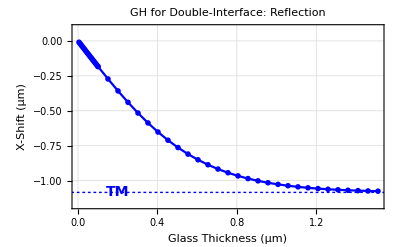

```mathematica
dat = Join[R1x$plotdata];

vmax= +0.1+Max[Transpose[dat][[2]]];
vmin= -0.1+Min[Transpose[dat][[2]]];

p$R1$x=ListLinePlot[dat,PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{vmin,vmax},PlotStyle->{Blue},FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},PlotLabel->font["GH for Double-Interface: Reflection",16]];


p$R1$final$x = Show[p$R1$x,p$x1$singleboundary$44R,Graphics[{Blue,Text[font[" TM ",14],{0.2,x1$singleboundary$44R},Background->White]}]]
```

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

x2$singleboundary$44R=-0.6425425265838541;

p$x2$singleboundary$44R=Graphics[{Darker[Red],Thick,Dashing->Tiny,Line[{{-100,x2$singleboundary$44R},{100,x2$singleboundary$44R}}]}];
```

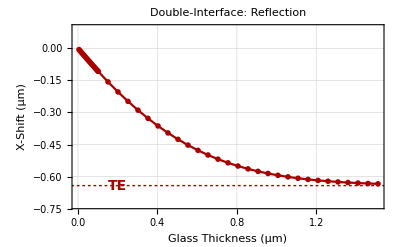

```mathematica
dat = R2x$plotdata;

vmax= 0.1+Max[Transpose[dat][[2]]];
vmin= -0.1+Min[Transpose[dat][[2]]];

p$R2$x=ListLinePlot[dat,PlotMarkers->{{Graphics[Disk[]],.02}},PlotRange->{vmin,vmax},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Darker[Red]},FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},PlotLabel->font["Double-Interface: Reflection",16]];


p$R2$final$x = Show[p$R2$x,p$x2$singleboundary$44R,Graphics[{Darker[Red],Text[font[" TE ",14],{0.2,x2$singleboundary$44R},Background->White]}]]
```

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

x3$singleboundary$44R=-0.8632771881931228;

p$x3$singleboundary$44R=Graphics[{Green,Thick,Dashing->Tiny,Line[{{-100,x3$singleboundary$44R},{100,x3$singleboundary$44R}}]}];
```

```mathematica
dat = R3x$plotdata;

vmax= 0.1+Max[Transpose[dat][[2]]];
vmin= -0.1+Min[Transpose[dat][[2]]];

p$R3$x=ListLinePlot[dat,PlotMarkers->{{Graphics[Disk[]],.02}},PlotRange->{vmin,vmax},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},PlotLabel->font["Double-Interface: Reflection",16]];


p$R3$final$x = Show[p$R3$x,p$x3$singleboundary$44R,Graphics[{Green,Text[font[" Spin^+ ",14],{0.15,x3$singleboundary$44R},Background->White]}],
Graphics[{Magenta,Text[font[" Spin^- ",14],{0.45,x4$singleboundary$44R},Background->White]}]]
```

-Graphics-

```mathematica
x4$singleboundary$44R=-0.8632771881931228;

p$x4$singleboundary$44R=Graphics[{Magenta,Thickness[.01],Dashing->Small,Line[{{-100,x4$singleboundary$44R},{100,x4$singleboundary$44R}}]}];
```

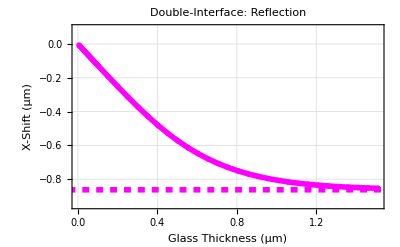

```mathematica
dat = R4x$plotdata;

vmax= 0.1+Max[Transpose[dat][[2]]];
vmin= -0.1+Min[Transpose[dat][[2]]];

p$R4$x=ListLinePlot[dat,PlotMarkers->{{Graphics[Disk[]],.03}},PlotRange->{vmin,vmax},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Magenta,Thickness[.01]},FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},PlotLabel->font["Double-Interface: Reflection",16]];


p$R4$final$x = Show[p$R4$x,p$x4$singleboundary$44R]
```

#### IF Shift Plots

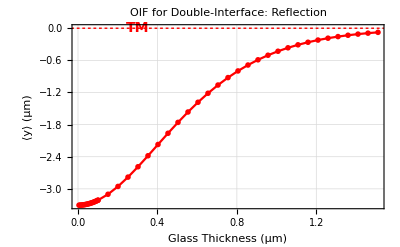

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

y1$singleboundary$44R=0;

p$y1$singleboundary$44R=Graphics[{Red,Thick,Dashing->Tiny,Line[{{-100,y1$singleboundary$44R},{100,y1$singleboundary$44R}}]}];

p$R1$y=ListLinePlot[{R1y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},FrameLabel->{font["Glass Thickness (μm)",14],font["⟨y⟩ (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

p$R1$final$y = Show[p$R1$y,p$y1$singleboundary$44R,Graphics[{Red,Text[font[" TM ",14],{0.3,y1$singleboundary$44R+0.001},Background->White]}]]
```

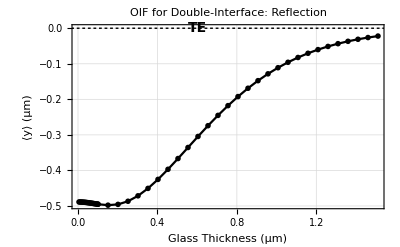

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

y2$singleboundary$44R=0;

p$y2$singleboundary$44R=Graphics[{Black,Thick,Dashing->Tiny,Line[{{-100,y2$singleboundary$44R},{100,y2$singleboundary$44R}}]}];

p$R2$y=ListLinePlot[{R2y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Black},FrameLabel->{font["Glass Thickness (μm)",14],font["⟨y⟩ (μm)",14]},PlotLabel->font["OIF for Double-Interface: Reflection",16]];

p$R2$final$y = Show[p$R2$y,p$y2$singleboundary$44R,Graphics[{Black,Text[font[" TE ",14],{0.6,y2$singleboundary$44R+0.001},Background->White]}]]
```

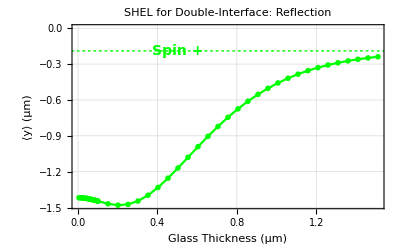

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

y3$singleboundary$44R=-0.1894607634398401;

p$y3$singleboundary$44R=Graphics[{Green,Thick,Dashing->Tiny,Line[{{-100,y3$singleboundary$44R},{100,y3$singleboundary$44R}}]}];

p$R3$y=ListLinePlot[{R3y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green},FrameLabel->{font["Glass Thickness (μm)",14],font["⟨y⟩ (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

p$R3$final$y = Show[p$R3$y,p$y3$singleboundary$44R,Graphics[{Green,Text[font[" Spin + ",14],{0.5,y3$singleboundary$44R+0.001},Background->White]}]]
```

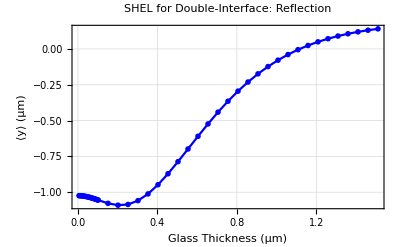

```mathematica
(* Data from Centroid_Shifts_Single-Interface_Beam.nb *)

y4$singleboundary$44R=0.1894607634398401;

p$y4$singleboundary$44R=Graphics[{Blue,Thick,Dashing->Tiny,Line[{{-100,y4$singleboundary$44R},{100,y4$singleboundary$44R}}]}];

p$R4$y=ListLinePlot[{R4y$plotdata},PlotMarkers->{{Graphics[Disk[]],.02}},Joined->True,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},FrameLabel->{font["Glass Thickness (μm)",14],font["⟨y⟩ (μm)",14]},PlotLabel->font["SHEL for Double-Interface: Reflection",16]];

p$R4$final$y = Show[p$R4$y,p$y4$singleboundary$44R,Graphics[{Blue,Text[font[" Spin - ",14],{0.4,y4$singleboundary$44R-0.001},Background->White]}]]
```

#### Plot Graphics For Manuscript

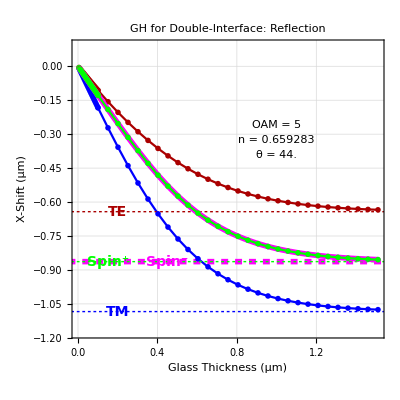

```mathematica
vmin = -1.3;
vmax = 0;

p$GH=Show[p$R1$final$x,p$R2$final$x,p$R4$final$x,p$R3$final$x,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.,vmin + 0.8 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.,vmin + 0.75(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.,vmin + 0.7 (vmax-vmin)},Background->White]}],
AspectRatio->1,FrameLabel->{font["Glass Thickness (μm)",14],font["X-Shift (μm)",14]},BaseStyle->{"Tahoma",14}]
```

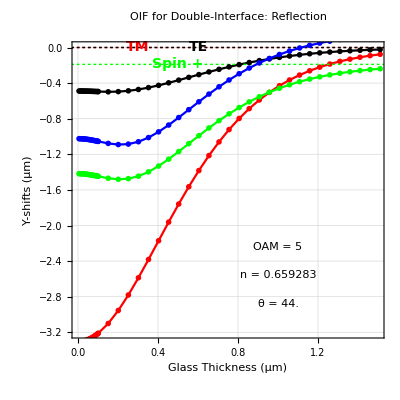

```mathematica
vmin = -3.2;

Show[{p$R1$final$y,p$R2$final$y,p$R3$final$y,p$R4$final$y,
Graphics[{Black,Text["OAM = "<>ToString[ℓ /. params$here],{1.,vmin + 0.3 (vmax-vmin)},Background->White]}],
Graphics[{Black,Text["n = "<>ToString[n /. params$here],{1.,vmin + 0.2(vmax-vmin)},Background->White]}],
Graphics[{Black,Text["θ = "<>ToString[θ/Degree /. params$here],{1.,vmin + 0.1(vmax-vmin)},Background->White]}]
},PlotRange->{{0,1.5},{vmin,vmax}},
AspectRatio->1,FrameLabel->{font["Glass Thickness (μm)",14],font["Y-shifts (μm)",14]},BaseStyle->{"Tahoma",14}]
```

```mathematica
θbrewster = ArcTan[n]/Degree /. n->1/1.1568
```

40.8419

```mathematica
GraphicsGrid[{{p$GH},{p$IF$plus,p$IF$minus}},ImageSize->800]
```

-Graphics-